## Robotic Manipulator

In this note book the Vector tools by Dr . Alan A Barhorst was used . Please contact him via alan.barhorst@louisiana.edu for it .
Please cite the vector tools by using:
Barhorst, A.A., 1997. Symbolic equation processing utilizing vector/dyad notation. Journal of Sound and Vibration, 208(5), pp.823-839.

# Forward Kinematics

### Load the vector tools

```mathematica
<<"/home/nasa-hp/Desktop/vectorDefsMM30.m"(* Call Vector Tools here*)
```

These Engineering Vector algorithms are copyright Alan A. Barhorst

```mathematica
Off[ReplaceRepeated::rrlim];
```

### Typical rotations

Generic 0 rotation (Identity)

```mathematica
rot0[q_:1]={{1,0,0},{0,1,0},
		            {0,0,1}};MatrixForm [rot0[ ]]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

Generic 1 rotation

```mathematica
rot1[q_]={{1,0,0},{0,Cos[q],Sin[q]},
		            {0,-Sin[q],Cos[q]}};MatrixForm [rot1[Subscript[q, 1][t]]]
```

(1 | 0 | 0
0 | Cos[q_1[t]] | Sin[q_1[t]]
0 | -Sin[q_1[t]] | Cos[q_1[t]])

Generic rotation 2

```mathematica
rot2[q_]={{Cos[q],0,-Sin[q]},{0,1,0},{Sin[q],0,Cos[q]}};
MatrixForm[rot2[Subscript[q, 2][t]]]
```

(Cos[q_2[t]] | 0 | -Sin[q_2[t]]
0 | 1 | 0
Sin[q_2[t]] | 0 | Cos[q_2[t]])

Generic Rotation 3

```mathematica
rot3[q_]={{Cos[q],Sin[q],0},{-Sin[q],Cos[q],0},{0,0,1}};
MatrixForm[rot3[Subscript[q, 3][t]]]
```

(Cos[q_3[t]] | Sin[q_3[t]] | 0
-Sin[q_3[t]] | Cos[q_3[t]] | 0
0 | 0 | 1)

### Define the symbols used for unit vectors and unit Dyads

```mathematica
a[x_]:=unitVector[A,a,x]
b[x_]:=unitVector[B,b,x]
c[x_]:=unitVector[C,c,x]
d[x_]:=unitVector[D,d,x]
e[x_]:=unitVector[E,e,x]
f[x_]:=unitVector[F,f,x]
g[x_]:=unitVector[G,g,x]
h[x_]:=unitVector[H,h,x]
l[x_]:=unitVector[L,l,x]
m[x_]:=unitVector[M,m,x]
n[x_]:=unitVector[N,n,x]
p[x_]:=unitVector[P,p,x]
s[x_]:=unitVector[S,s,x]
aa[x_,y_]:=unitDyad[a[x],a[y]]
bb[x_,y_]:=unitDyad[b[x],b[y]]
cc[x_,y_]:=unitDyad[c[x],c[y]]
dd[x_,y_]:=unitDyad[d[x],d[y]]
ee[x_,y_]:=unitDyad[e[x],e[y]]
ff[x_,y_]:=unitDyad[f[x],f[y]]
gg[x_,y_]:=unitDyad[g[x],g[y]]
hh[x_,y_]:=unitDyad[h[x],h[y]]
ll[x_,y_]:=unitDyad[l[x],l[y]]
mm[x_,y_]:=unitDyad[m[x],m[y]]
pp[x_,y_]:=unitDyad[p[x],p[y]]
ss[x_,y_]:=unitDyad[s[x],s[y]]
```

### Robot graphic

-Graphics3D-

#### Base

```mathematica
vecL=2;
```

```mathematica
widthBase=4;depthBase=3;heightBase=1/2;
```

```mathematica
baseShape=Cuboid[
{-widthBase/2,-depthBase/2,-heightBase/2},
{widthBase/2,depthBase/2,heightBase/2}];
```

```mathematica
baseGraphic={baseShape,
{{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}}};
```

```mathematica
Show[Graphics3D[baseGraphic],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

#### Wheels

```mathematica
vecL=1;
```

```mathematica
halfHeightwheel=1/12;
wheelBase={0,0,-halfHeightwheel};
wheelTop={0,0,halfHeightwheel};
wheelRadius=1/2;
```

```mathematica
wheelGraphic1={Rotate[Cylinder[{wheelBase,wheelTop},wheelRadius],Pi/2,{1,0,0}],
		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}};
```

```mathematica
Show[Graphics3D[{Glow[Red],wheelGraphic1}],ViewPoint->{1,1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

```mathematica
wheelGraphic2={Rotate[Cylinder[{wheelBase,wheelTop},wheelRadius],Pi/2,{1,0,0}],

		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}};
```

```mathematica
Show[Graphics3D[{Glow[Yellow],wheelGraphic2}],ViewPoint->{1,1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

```mathematica
wheelGraphic3={Rotate[Cylinder[{wheelBase,wheelTop},wheelRadius],Pi/2,{0,1,0}],

		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}};
```

```mathematica
Show[Graphics3D[{Glow[Green],wheelGraphic3}],ViewPoint->{1,1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

```mathematica
wheelGraphic4={Rotate[Cylinder[{wheelBase,wheelTop},wheelRadius],Pi/2,{0,1,0}],

		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}};
```

```mathematica
Show[Graphics3D[{Glow[Blue],wheelGraphic4}],ViewPoint->{1,1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

#### Base rotator

```mathematica
halfHeightrotator=1/4;
rotatorBase={0,0,-halfHeightrotator};
rotatorTop={0,0,halfHeightrotator};
rotatorRadius=1/2.5;
```

```mathematica
rotatorGraphic={Rotate[Cylinder[{rotatorBase,rotatorTop},rotatorRadius],Pi/2,{0,0,1}],
		{{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}}};
```

```mathematica
Show[Graphics3D[{Glow[Red],rotatorGraphic}],ViewPoint->{1,1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

#### Joint1

```mathematica
halfHeightwheel1=1/2.5;
wheelBase1={0,0,-halfHeightwheel1};
wheelTop1={0,0,halfHeightwheel1};
wheelRadius1=1/2;
```

```mathematica
jointGraphic1={Rotate[Cylinder[{wheelBase1,wheelTop1},wheelRadius1],Pi/2,{1,0,0}],
{{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,1.5vecL}}]}}};
```

```mathematica
Show[Graphics3D[{Glow[Blue],jointGraphic1}],ViewPoint->{1,1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

#### Arm 1

```mathematica
arm1widthBase=2.5;arm1depthBase=0.25;arm1heightBase=0.5;
```

```mathematica
arm1baseShape=Cuboid[
{-arm1widthBase/2,-arm1depthBase/2,-arm1heightBase/2},
{arm1widthBase/2,arm1depthBase/2,arm1heightBase/2}];
```

```mathematica
arm1baseGraphic={arm1baseShape,
{
		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,1.5vecL}}]}}};
```

```mathematica
Show[Graphics3D[arm1baseGraphic],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

#### Arm 2

```mathematica
arm2widthBase = 2; arm2depthBase = 0.25; arm2heightBase = 0.5;
```

```mathematica
arm2baseShape=Cuboid[
{-arm2widthBase/2,-arm2depthBase/2,-arm2heightBase/2},
{arm2widthBase/2,arm2depthBase/2,arm2heightBase/2}];
```

```mathematica
arm2baseGraphic={arm2baseShape,
{
		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{1.5vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}}};
```

```mathematica
Show[Graphics3D[arm2baseGraphic],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

#### Arm 3

```mathematica
arm3widthBase = 2; arm3depthBase = 0.25; arm3heightBase = 0.5;
```

```mathematica
arm3baseShape=Cuboid[
{-arm3widthBase/2,-arm3depthBase/2,-arm3heightBase/2},
{arm3widthBase/2,arm3depthBase/2,arm3heightBase/2}];
```

```mathematica
arm3baseGraphic={arm3baseShape,
{
		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{1.5vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}}};
```

```mathematica
Show[Graphics3D[arm3baseGraphic],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

#### Wrist 1

```mathematica
halfHeightwrist1=1/8;
wristBase1={0,0,-halfHeightwrist1};
wristTop1={0,0,halfHeightwrist1};
wristRadius1=1/3;
```

```mathematica
wristGraphic1={Rotate[Cylinder[{wristBase1,wristTop1},wristRadius1],Pi/2,{1,0,0}],
		{		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}}};
```

```mathematica
Show[Graphics3D[{Glow[Red],wristGraphic1}],ViewPoint->{1,1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

#### Wrist 2

```mathematica
halfHeightwrist2=1/10;
wristBase2={0,0,-halfHeightwrist2};
wristTop2={0,0,halfHeightwrist2};
wristRadius2=1/4;
pointerLength=1/4;
```

```mathematica
wristGraphic2={Rotate[Cylinder[{wristBase2,wristTop2},wristRadius2],Pi/2,{0,1,0}],{AbsoluteThickness[4],Line[{{halfHeightwrist2,0,0},{halfHeightwrist2+pointerLength,0,0}}]},
		{
		{AbsoluteThickness[1],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[1],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[1],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}}};
```

```mathematica
Show[Graphics3D[{Glow[Red],wristGraphic2}],ViewPoint->{1,1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]
```

-Graphics3D-

#### Graphic

```mathematica
robotGraphic1=
(*Base*){Translate[baseGraphic,{0,0, 0}],

(*wheel 1*)Translate[wheelGraphic1,{0widthBase,(0.5+1/24) depthBase,0 heightBase}],

(*wheel 2*)Translate[wheelGraphic2,{ 0widthBase,-(0.5+1/24) depthBase,0 heightBase}],

(*wheel 3*)Translate[wheelGraphic3,{(0.5widthBase+halfHeightwheel),0 depthBase,0 heightBase}],

(*wheel 4*)Translate[wheelGraphic4,{ -(0.5widthBase+halfHeightwheel),0depthBase,0 heightBase}],

(*rotor*)Translate[rotatorGraphic,{  0,0,(0.5heightBase+halfHeightrotator)}],

(*joint 1*)Translate[jointGraphic1,{0,0,(0.5heightBase+2halfHeightrotator+0.5wheelRadius1)}],

(*arm 1*)Translate[arm1baseGraphic,{(0.5 arm1widthBase-wheelRadius1),(halfHeightwheel1+0.5arm1depthBase),(0.5heightBase+2halfHeightrotator+0.5wheelRadius1)}],

(*arm 2*)Translate[arm2baseGraphic,{( arm1widthBase-wheelRadius1+1/3 arm2widthBase),(halfHeightwheel1+0.5arm1depthBase-0.5arm1depthBase-0.5arm2depthBase),(0.5heightBase+2halfHeightrotator+0.5wheelRadius1)}],

(*arm 3*)Translate[arm3baseGraphic,{ ( arm1widthBase-wheelRadius1+ arm2widthBase+1/5arm3widthBase),(halfHeightwheel1+0.5arm1depthBase-0.5arm1depthBase-0.5arm2depthBase+0.5arm2depthBase+0.5arm3depthBase),(0.5heightBase+2halfHeightrotator+0.5wheelRadius1)}],

(*wrist 1*)Translate[wristGraphic1,{( arm1widthBase-wheelRadius1+ arm2widthBase+1/5arm3widthBase+1/2arm3widthBase+0.5wheelRadius1),(halfHeightwheel1+0.5arm1depthBase-0.5arm1depthBase-0.5arm2depthBase+0.5arm2depthBase+0.5arm3depthBase),(0.5heightBase+2halfHeightrotator+0.5wheelRadius1)}],


(*wrist 2*)Translate[wristGraphic2,{(  arm1widthBase-wheelRadius1+ arm2widthBase+1/5arm3widthBase+1/2arm3widthBase+wheelRadius1+halfHeightwrist1),(halfHeightwheel1+0.5arm1depthBase-0.5arm1depthBase-0.5arm2depthBase+0.5arm2depthBase+0.5arm3depthBase),(0.5heightBase+2halfHeightrotator+0.5wheelRadius1)}]
};
```

```mathematica
Show[Graphics3D[robotGraphic1],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{0.5,0.5,0.5},Boxed->False,PlotRange->All]
```

-Graphics3D-

### Rotations

Rotation sequence is 3-2-2-2-2-1

```mathematica
rotA=rot0[];
AtoN=rotA.{n[1],n[2],n[3]}
```

{(n̂)_1,(n̂)_2,(n̂)_3}

```mathematica
TransAtoN[x_]:=x//.{a[1]-> AtoN[[1]],a[2]->AtoN[[2]],a[3]->AtoN[[3]]}
```

```mathematica
{a[1]->AtoN[[1]],a[2]->AtoN[[2]],a[3]->AtoN[[3]]}
```

{(â)_1→(n̂)_1,(â)_2→(n̂)_2,(â)_3→(n̂)_3}

------------------------------------------------Wheel--------------------------------------------------------------------------------------------------------------------------------------------------

```mathematica
rotB=rot2[Subscript[q, 2][t]].rotA;
BtoN=rotB.{n[1],n[2],n[3]}
```

{Cos[q_2[t]] (n̂)_1-Sin[q_2[t]] (n̂)_3,(n̂)_2,Sin[q_2[t]] (n̂)_1+Cos[q_2[t]] (n̂)_3}

```mathematica
TransBtoN[x_]:=x//.{b[1]->BtoN[[1]],b[2]->BtoN[[2]],b[3]->BtoN[[3]]}
{b[1]->BtoN[[1]],b[2]->BtoN[[2]],b[3]->BtoN[[3]]}
```

{(b̂)_1→Cos[q_2[t]] (n̂)_1-Sin[q_2[t]] (n̂)_3,(b̂)_2→(n̂)_2,(b̂)_3→Sin[q_2[t]] (n̂)_1+Cos[q_2[t]] (n̂)_3}

```mathematica
rotC=rot2[Subscript[q, 2][t]].rotA;
CtoN=rotC.{n[1],n[2],n[3]}
```

{Cos[q_2[t]] (n̂)_1-Sin[q_2[t]] (n̂)_3,(n̂)_2,Sin[q_2[t]] (n̂)_1+Cos[q_2[t]] (n̂)_3}

```mathematica
TransCtoN[x_]:=x//.{c[1]->CtoN[[1]],c[2]->CtoN[[2]],c[3]->CtoN[[3]]}
{c[1]->CtoN[[1]],c[2]->CtoN[[2]],c[3]->CtoN[[3]]}
```

{(ĉ)_1→Cos[q_2[t]] (n̂)_1-Sin[q_2[t]] (n̂)_3,(ĉ)_2→(n̂)_2,(ĉ)_3→Sin[q_2[t]] (n̂)_1+Cos[q_2[t]] (n̂)_3}

```mathematica
rotD=rot1[Subscript[q, 3][t]].rotA;
DtoN=rotD.{n[1],n[2],n[3]}
```

{(n̂)_1,Cos[q_3[t]] (n̂)_2+Sin[q_3[t]] (n̂)_3,-Sin[q_3[t]] (n̂)_2+Cos[q_3[t]] (n̂)_3}

```mathematica
TransDtoN[x_]:=x//.{d[1]->DtoN[[1]],d[2]->DtoN[[2]],d[3]->DtoN[[3]]}
{d[1]->DtoN[[1]],d[2]->DtoN[[2]],d[3]->DtoN[[3]]}
```

{(d̂)_1→(n̂)_1,(d̂)_2→Cos[q_3[t]] (n̂)_2+Sin[q_3[t]] (n̂)_3,(d̂)_3→-Sin[q_3[t]] (n̂)_2+Cos[q_3[t]] (n̂)_3}

```mathematica
rotE=rot1[Subscript[q, 4][t]].rotA;
EtoN=rotE.{n[1],n[2],n[3]}
```

{(n̂)_1,Cos[q_4[t]] (n̂)_2+Sin[q_4[t]] (n̂)_3,-Sin[q_4[t]] (n̂)_2+Cos[q_4[t]] (n̂)_3}

```mathematica
TransEtoN[x_]:=x//.{e[1]->EtoN[[1]],e[2]->EtoN[[2]],e[3]->EtoN[[3]]}
{e[1]->EtoN[[1]],e[2]->EtoN[[2]],e[3]->EtoN[[3]]}
```

{(ê)_1→(n̂)_1,(ê)_2→Cos[q_4[t]] (n̂)_2+Sin[q_4[t]] (n̂)_3,(ê)_3→-Sin[q_4[t]] (n̂)_2+Cos[q_4[t]] (n̂)_3}

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

Rotation Base to base barrel is along 3rd axis.

```mathematica
rotF=rot0[].rotA;
FtoN=rotF.{n[1],n[2],n[3]}
```

{(n̂)_1,(n̂)_2,(n̂)_3}

```mathematica
TransFtoN[x_]:=x//.{f[1]->FtoN[[1]],f[2]->FtoN[[2]],f[3]->FtoN[[3]]}
{f[1]->FtoN[[1]],f[2]->FtoN[[2]],f[3]->FtoN[[3]]}
```

{(f̂)_1→(n̂)_1,(f̂)_2→(n̂)_2,(f̂)_3→(n̂)_3}

Frame g and f are identical

```mathematica
rotG=rot3[Subscript[q, 5][t]].rotF;
GtoN=rotG.{n[1],n[2],n[3]}
```

{Cos[q_5[t]] (n̂)_1+Sin[q_5[t]] (n̂)_2,-Sin[q_5[t]] (n̂)_1+Cos[q_5[t]] (n̂)_2,(n̂)_3}

```mathematica
TransGtoN[x_]:=x//.{g[1]->GtoN[[1]],g[2]->GtoN[[2]],g[3]->GtoN[[3]]}
```

```mathematica
{g[1]->GtoN[[1]],g[2]->GtoN[[2]],g[3]->GtoN[[3]]}
```

{(ĝ)_1→Cos[q_5[t]] (n̂)_1+Sin[q_5[t]] (n̂)_2,(ĝ)_2→-Sin[q_5[t]] (n̂)_1+Cos[q_5[t]] (n̂)_2,(ĝ)_3→(n̂)_3}

Rotation of Arm 1 is along 2nd axis

```mathematica
rotH=rot2[Subscript[q, 6][t]].rotG;
HtoN=rotH.{n[1],n[2],n[3]}
```

{Cos[q_5[t]] Cos[q_6[t]] (n̂)_1+Cos[q_6[t]] Sin[q_5[t]] (n̂)_2-Sin[q_6[t]] (n̂)_3,-Sin[q_5[t]] (n̂)_1+Cos[q_5[t]] (n̂)_2,Cos[q_5[t]] Sin[q_6[t]] (n̂)_1+Sin[q_5[t]] Sin[q_6[t]] (n̂)_2+Cos[q_6[t]] (n̂)_3}

```mathematica
TransHtoN[x_]:=x//.{h[1]->HtoN[[1]],h[2]->HtoN[[2]],h[3]->HtoN[[3]]}
{h[1]->HtoN[[1]],h[2]->HtoN[[2]],h[3]->HtoN[[3]]}
```

{(ĥ)_1→Cos[q_5[t]] Cos[q_6[t]] (n̂)_1+Cos[q_6[t]] Sin[q_5[t]] (n̂)_2-Sin[q_6[t]] (n̂)_3,(ĥ)_2→-Sin[q_5[t]] (n̂)_1+Cos[q_5[t]] (n̂)_2,(ĥ)_3→Cos[q_5[t]] Sin[q_6[t]] (n̂)_1+Sin[q_5[t]] Sin[q_6[t]] (n̂)_2+Cos[q_6[t]] (n̂)_3}

Rotation of Arm2 is around 2nd axis

```mathematica
rotL=rot2[Subscript[q, 7][t]].rotH;
LtoN=rotL.{n[1],n[2],n[3]}
```

{(Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]]-Cos[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]) (n̂)_1+(Cos[q_6[t]] Cos[q_7[t]] Sin[q_5[t]]-Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]) (n̂)_2+(-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]]) (n̂)_3,-Sin[q_5[t]] (n̂)_1+Cos[q_5[t]] (n̂)_2,(Cos[q_5[t]] Cos[q_7[t]] Sin[q_6[t]]+Cos[q_5[t]] Cos[q_6[t]] Sin[q_7[t]]) (n̂)_1+(Cos[q_7[t]] Sin[q_5[t]] Sin[q_6[t]]+Cos[q_6[t]] Sin[q_5[t]] Sin[q_7[t]]) (n̂)_2+(Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]]) (n̂)_3}

```mathematica
TransLtoN[x_]:=x//.{l[1]->LtoN[[1]],l[2]->LtoN[[2]],l[3]->LtoN[[3]]}
{l[1]->LtoN[[1]],l[2]->LtoN[[2]],l[3]->LtoN[[3]]}
```

{(l̂)_1→(Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]]-Cos[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]) (n̂)_1+(Cos[q_6[t]] Cos[q_7[t]] Sin[q_5[t]]-Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]) (n̂)_2+(-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]]) (n̂)_3,(l̂)_2→-Sin[q_5[t]] (n̂)_1+Cos[q_5[t]] (n̂)_2,(l̂)_3→(Cos[q_5[t]] Cos[q_7[t]] Sin[q_6[t]]+Cos[q_5[t]] Cos[q_6[t]] Sin[q_7[t]]) (n̂)_1+(Cos[q_7[t]] Sin[q_5[t]] Sin[q_6[t]]+Cos[q_6[t]] Sin[q_5[t]] Sin[q_7[t]]) (n̂)_2+(Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]]) (n̂)_3}

Rotation of Arm3 is around 2 nd axis

```mathematica
rotS=rot2[Subscript[q, 8][t]].rotL;
StoN=rotS.{n[1],n[2],n[3]}
```

{(Cos[q_8[t]] (Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]]-Cos[q_5[t]] Sin[q_6[t]] Sin[q_7[t]])-(Cos[q_5[t]] Cos[q_7[t]] Sin[q_6[t]]+Cos[q_5[t]] Cos[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) (n̂)_1+(Cos[q_8[t]] (Cos[q_6[t]] Cos[q_7[t]] Sin[q_5[t]]-Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]])-(Cos[q_7[t]] Sin[q_5[t]] Sin[q_6[t]]+Cos[q_6[t]] Sin[q_5[t]] Sin[q_7[t]]) Sin[q_8[t]]) (n̂)_2+(Cos[q_8[t]] (-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]])-(Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) (n̂)_3,-Sin[q_5[t]] (n̂)_1+Cos[q_5[t]] (n̂)_2,(Cos[q_8[t]] (Cos[q_5[t]] Cos[q_7[t]] Sin[q_6[t]]+Cos[q_5[t]] Cos[q_6[t]] Sin[q_7[t]])+(Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]]-Cos[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) (n̂)_1+(Cos[q_8[t]] (Cos[q_7[t]] Sin[q_5[t]] Sin[q_6[t]]+Cos[q_6[t]] Sin[q_5[t]] Sin[q_7[t]])+(Cos[q_6[t]] Cos[q_7[t]] Sin[q_5[t]]-Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) (n̂)_2+(Cos[q_8[t]] (Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]])+(-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) (n̂)_3}

```mathematica
TransStoN[x_]:=x//.{s[1]->StoN[[1]],s[2]->StoN[[2]],s[3]->StoN[[3]]}
{s[1]->StoN[[1]],s[2]->StoN[[2]],s[3]->StoN[[3]]}
```

{(ŝ)_1→(Cos[q_8[t]] (Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]]-Cos[q_5[t]] Sin[q_6[t]] Sin[q_7[t]])-(Cos[q_5[t]] Cos[q_7[t]] Sin[q_6[t]]+Cos[q_5[t]] Cos[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) (n̂)_1+(Cos[q_8[t]] (Cos[q_6[t]] Cos[q_7[t]] Sin[q_5[t]]-Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]])-(Cos[q_7[t]] Sin[q_5[t]] Sin[q_6[t]]+Cos[q_6[t]] Sin[q_5[t]] Sin[q_7[t]]) Sin[q_8[t]]) (n̂)_2+(Cos[q_8[t]] (-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]])-(Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) (n̂)_3,(ŝ)_2→-Sin[q_5[t]] (n̂)_1+Cos[q_5[t]] (n̂)_2,(ŝ)_3→(Cos[q_8[t]] (Cos[q_5[t]] Cos[q_7[t]] Sin[q_6[t]]+Cos[q_5[t]] Cos[q_6[t]] Sin[q_7[t]])+(Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]]-Cos[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) (n̂)_1+(Cos[q_8[t]] (Cos[q_7[t]] Sin[q_5[t]] Sin[q_6[t]]+Cos[q_6[t]] Sin[q_5[t]] Sin[q_7[t]])+(Cos[q_6[t]] Cos[q_7[t]] Sin[q_5[t]]-Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) (n̂)_2+(Cos[q_8[t]] (Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]])+(-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) (n̂)_3}

Rotation of wrist 1 is around axis 1

```mathematica
rotM=rot2[Subscript[q, 9][t]].rotS;
MtoN=rotM.{n[1],n[2],n[3]}
```

{(Cos[q_9[t]] (Cos[q_8[t]] (Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]]-Cos[q_5[t]] Sin[q_6[t]] Sin[q_7[t]])-(Cos[q_5[t]] Cos[q_7[t]] Sin[q_6[t]]+Cos[q_5[t]] Cos[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]])-(Cos[q_8[t]] (Cos[q_5[t]] Cos[q_7[t]] Sin[q_6[t]]+Cos[q_5[t]] Cos[q_6[t]] Sin[q_7[t]])+(Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]]-Cos[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]]) (n̂)_1+(Cos[q_9[t]] (Cos[q_8[t]] (Cos[q_6[t]] Cos[q_7[t]] Sin[q_5[t]]-Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]])-(Cos[q_7[t]] Sin[q_5[t]] Sin[q_6[t]]+Cos[q_6[t]] Sin[q_5[t]] Sin[q_7[t]]) Sin[q_8[t]])-(Cos[q_8[t]] (Cos[q_7[t]] Sin[q_5[t]] Sin[q_6[t]]+Cos[q_6[t]] Sin[q_5[t]] Sin[q_7[t]])+(Cos[q_6[t]] Cos[q_7[t]] Sin[q_5[t]]-Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]]) (n̂)_2+(Cos[q_9[t]] (Cos[q_8[t]] (-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]])-(Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]])-(Cos[q_8[t]] (Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]])+(-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]]) (n̂)_3,-Sin[q_5[t]] (n̂)_1+Cos[q_5[t]] (n̂)_2,(Cos[q_9[t]] (Cos[q_8[t]] (Cos[q_5[t]] Cos[q_7[t]] Sin[q_6[t]]+Cos[q_5[t]] Cos[q_6[t]] Sin[q_7[t]])+(Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]]-Cos[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]])+(Cos[q_8[t]] (Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]]-Cos[q_5[t]] Sin[q_6[t]] Sin[q_7[t]])-(Cos[q_5[t]] Cos[q_7[t]] Sin[q_6[t]]+Cos[q_5[t]] Cos[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]]) (n̂)_1+(Cos[q_9[t]] (Cos[q_8[t]] (Cos[q_7[t]] Sin[q_5[t]] Sin[q_6[t]]+Cos[q_6[t]] Sin[q_5[t]] Sin[q_7[t]])+(Cos[q_6[t]] Cos[q_7[t]] Sin[q_5[t]]-Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]])+(Cos[q_8[t]] (Cos[q_6[t]] Cos[q_7[t]] Sin[q_5[t]]-Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]])-(Cos[q_7[t]] Sin[q_5[t]] Sin[q_6[t]]+Cos[q_6[t]] Sin[q_5[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]]) (n̂)_2+(Cos[q_9[t]] (Cos[q_8[t]] (Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]])+(-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]])+(Cos[q_8[t]] (-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]])-(Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]]) (n̂)_3}

```mathematica
TransMtoN[x_]:=x//.{m[1]->MtoN[[1]],m[2]->MtoN[[2]],m[3]->MtoN[[3]]}
{m[1]->MtoN[[1]],m[2]->MtoN[[2]],m[3]->MtoN[[3]]}
```

{(m̂)_1→(Cos[q_9[t]] (Cos[q_8[t]] (Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]]-Cos[q_5[t]] Sin[q_6[t]] Sin[q_7[t]])-(Cos[q_5[t]] Cos[q_7[t]] Sin[q_6[t]]+Cos[q_5[t]] Cos[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]])-(Cos[q_8[t]] (Cos[q_5[t]] Cos[q_7[t]] Sin[q_6[t]]+Cos[q_5[t]] Cos[q_6[t]] Sin[q_7[t]])+(Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]]-Cos[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]]) (n̂)_1+(Cos[q_9[t]] (Cos[q_8[t]] (Cos[q_6[t]] Cos[q_7[t]] Sin[q_5[t]]-Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]])-(Cos[q_7[t]] Sin[q_5[t]] Sin[q_6[t]]+Cos[q_6[t]] Sin[q_5[t]] Sin[q_7[t]]) Sin[q_8[t]])-(Cos[q_8[t]] (Cos[q_7[t]] Sin[q_5[t]] Sin[q_6[t]]+Cos[q_6[t]] Sin[q_5[t]] Sin[q_7[t]])+(Cos[q_6[t]] Cos[q_7[t]] Sin[q_5[t]]-Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]]) (n̂)_2+(Cos[q_9[t]] (Cos[q_8[t]] (-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]])-(Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]])-(Cos[q_8[t]] (Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]])+(-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]]) (n̂)_3,(m̂)_2→-Sin[q_5[t]] (n̂)_1+Cos[q_5[t]] (n̂)_2,(m̂)_3→(Cos[q_9[t]] (Cos[q_8[t]] (Cos[q_5[t]] Cos[q_7[t]] Sin[q_6[t]]+Cos[q_5[t]] Cos[q_6[t]] Sin[q_7[t]])+(Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]]-Cos[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]])+(Cos[q_8[t]] (Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]]-Cos[q_5[t]] Sin[q_6[t]] Sin[q_7[t]])-(Cos[q_5[t]] Cos[q_7[t]] Sin[q_6[t]]+Cos[q_5[t]] Cos[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]]) (n̂)_1+(Cos[q_9[t]] (Cos[q_8[t]] (Cos[q_7[t]] Sin[q_5[t]] Sin[q_6[t]]+Cos[q_6[t]] Sin[q_5[t]] Sin[q_7[t]])+(Cos[q_6[t]] Cos[q_7[t]] Sin[q_5[t]]-Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]])+(Cos[q_8[t]] (Cos[q_6[t]] Cos[q_7[t]] Sin[q_5[t]]-Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]])-(Cos[q_7[t]] Sin[q_5[t]] Sin[q_6[t]]+Cos[q_6[t]] Sin[q_5[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]]) (n̂)_2+(Cos[q_9[t]] (Cos[q_8[t]] (Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]])+(-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]])+(Cos[q_8[t]] (-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]])-(Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]]) (n̂)_3}

Rotation of wrist 2 is around axis1

```mathematica
rotP=rot1[Subscript[q, 10][t]].rotM;
PtoN=rotP.{n[1],n[2],n[3]}
```

{(Cos[q_9[t]] (Cos[q_8[t]] (Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]]-Cos[q_5[t]] Sin[q_6[t]] Sin[q_7[t]])-(Cos[q_5[t]] Cos[q_7[t]] Sin[q_6[t]]+Cos[q_5[t]] Cos[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]])-(Cos[q_8[t]] (Cos[q_5[t]] Cos[q_7[t]] Sin[q_6[t]]+Cos[q_5[t]] Cos[q_6[t]] Sin[q_7[t]])+(Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]]-Cos[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]]) (n̂)_1+(Cos[q_9[t]] (Cos[q_8[t]] (Cos[q_6[t]] Cos[q_7[t]] Sin[q_5[t]]-Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]])-(Cos[q_7[t]] Sin[q_5[t]] Sin[q_6[t]]+Cos[q_6[t]] Sin[q_5[t]] Sin[q_7[t]]) Sin[q_8[t]])-(Cos[q_8[t]] (Cos[q_7[t]] Sin[q_5[t]] Sin[q_6[t]]+Cos[q_6[t]] Sin[q_5[t]] Sin[q_7[t]])+(Cos[q_6[t]] Cos[q_7[t]] Sin[q_5[t]]-Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]]) (n̂)_2+(Cos[q_9[t]] (Cos[q_8[t]] (-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]])-(Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]])-(Cos[q_8[t]] (Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]])+(-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]]) (n̂)_3,(-Cos[q_10[t]] Sin[q_5[t]]+(Cos[q_9[t]] (Cos[q_8[t]] (Cos[q_5[t]] Cos[q_7[t]] Sin[q_6[t]]+Cos[q_5[t]] Cos[q_6[t]] Sin[q_7[t]])+(Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]]-Cos[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]])+(Cos[q_8[t]] (Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]]-Cos[q_5[t]] Sin[q_6[t]] Sin[q_7[t]])-(Cos[q_5[t]] Cos[q_7[t]] Sin[q_6[t]]+Cos[q_5[t]] Cos[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]]) Sin[q_10[t]]) (n̂)_1+(Cos[q_5[t]] Cos[q_10[t]]+(Cos[q_9[t]] (Cos[q_8[t]] (Cos[q_7[t]] Sin[q_5[t]] Sin[q_6[t]]+Cos[q_6[t]] Sin[q_5[t]] Sin[q_7[t]])+(Cos[q_6[t]] Cos[q_7[t]] Sin[q_5[t]]-Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]])+(Cos[q_8[t]] (Cos[q_6[t]] Cos[q_7[t]] Sin[q_5[t]]-Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]])-(Cos[q_7[t]] Sin[q_5[t]] Sin[q_6[t]]+Cos[q_6[t]] Sin[q_5[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]]) Sin[q_10[t]]) (n̂)_2+(Cos[q_9[t]] (Cos[q_8[t]] (Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]])+(-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]])+(Cos[q_8[t]] (-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]])-(Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]]) Sin[q_10[t]] (n̂)_3,(Cos[q_10[t]] (Cos[q_9[t]] (Cos[q_8[t]] (Cos[q_5[t]] Cos[q_7[t]] Sin[q_6[t]]+Cos[q_5[t]] Cos[q_6[t]] Sin[q_7[t]])+(Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]]-Cos[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]])+(Cos[q_8[t]] (Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]]-Cos[q_5[t]] Sin[q_6[t]] Sin[q_7[t]])-(Cos[q_5[t]] Cos[q_7[t]] Sin[q_6[t]]+Cos[q_5[t]] Cos[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]])+Sin[q_5[t]] Sin[q_10[t]]) (n̂)_1+(Cos[q_10[t]] (Cos[q_9[t]] (Cos[q_8[t]] (Cos[q_7[t]] Sin[q_5[t]] Sin[q_6[t]]+Cos[q_6[t]] Sin[q_5[t]] Sin[q_7[t]])+(Cos[q_6[t]] Cos[q_7[t]] Sin[q_5[t]]-Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]])+(Cos[q_8[t]] (Cos[q_6[t]] Cos[q_7[t]] Sin[q_5[t]]-Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]])-(Cos[q_7[t]] Sin[q_5[t]] Sin[q_6[t]]+Cos[q_6[t]] Sin[q_5[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]])-Cos[q_5[t]] Sin[q_10[t]]) (n̂)_2+Cos[q_10[t]] (Cos[q_9[t]] (Cos[q_8[t]] (Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]])+(-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]])+(Cos[q_8[t]] (-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]])-(Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]]) (n̂)_3}

```mathematica
TransPtoN[x_]:=x//.{p[1]->PtoN[[1]],p[2]->PtoN[[2]],p[3]->PtoN[[3]]}
{p[1]->PtoN[[1]],p[2]->PtoN[[2]],p[3]->PtoN[[3]]}
```

{(p̂)_1→(Cos[q_9[t]] (Cos[q_8[t]] (Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]]-Cos[q_5[t]] Sin[q_6[t]] Sin[q_7[t]])-(Cos[q_5[t]] Cos[q_7[t]] Sin[q_6[t]]+Cos[q_5[t]] Cos[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]])-(Cos[q_8[t]] (Cos[q_5[t]] Cos[q_7[t]] Sin[q_6[t]]+Cos[q_5[t]] Cos[q_6[t]] Sin[q_7[t]])+(Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]]-Cos[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]]) (n̂)_1+(Cos[q_9[t]] (Cos[q_8[t]] (Cos[q_6[t]] Cos[q_7[t]] Sin[q_5[t]]-Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]])-(Cos[q_7[t]] Sin[q_5[t]] Sin[q_6[t]]+Cos[q_6[t]] Sin[q_5[t]] Sin[q_7[t]]) Sin[q_8[t]])-(Cos[q_8[t]] (Cos[q_7[t]] Sin[q_5[t]] Sin[q_6[t]]+Cos[q_6[t]] Sin[q_5[t]] Sin[q_7[t]])+(Cos[q_6[t]] Cos[q_7[t]] Sin[q_5[t]]-Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]]) (n̂)_2+(Cos[q_9[t]] (Cos[q_8[t]] (-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]])-(Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]])-(Cos[q_8[t]] (Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]])+(-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]]) (n̂)_3,(p̂)_2→(-Cos[q_10[t]] Sin[q_5[t]]+(Cos[q_9[t]] (Cos[q_8[t]] (Cos[q_5[t]] Cos[q_7[t]] Sin[q_6[t]]+Cos[q_5[t]] Cos[q_6[t]] Sin[q_7[t]])+(Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]]-Cos[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]])+(Cos[q_8[t]] (Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]]-Cos[q_5[t]] Sin[q_6[t]] Sin[q_7[t]])-(Cos[q_5[t]] Cos[q_7[t]] Sin[q_6[t]]+Cos[q_5[t]] Cos[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]]) Sin[q_10[t]]) (n̂)_1+(Cos[q_5[t]] Cos[q_10[t]]+(Cos[q_9[t]] (Cos[q_8[t]] (Cos[q_7[t]] Sin[q_5[t]] Sin[q_6[t]]+Cos[q_6[t]] Sin[q_5[t]] Sin[q_7[t]])+(Cos[q_6[t]] Cos[q_7[t]] Sin[q_5[t]]-Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]])+(Cos[q_8[t]] (Cos[q_6[t]] Cos[q_7[t]] Sin[q_5[t]]-Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]])-(Cos[q_7[t]] Sin[q_5[t]] Sin[q_6[t]]+Cos[q_6[t]] Sin[q_5[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]]) Sin[q_10[t]]) (n̂)_2+(Cos[q_9[t]] (Cos[q_8[t]] (Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]])+(-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]])+(Cos[q_8[t]] (-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]])-(Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]]) Sin[q_10[t]] (n̂)_3,(p̂)_3→(Cos[q_10[t]] (Cos[q_9[t]] (Cos[q_8[t]] (Cos[q_5[t]] Cos[q_7[t]] Sin[q_6[t]]+Cos[q_5[t]] Cos[q_6[t]] Sin[q_7[t]])+(Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]]-Cos[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]])+(Cos[q_8[t]] (Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]]-Cos[q_5[t]] Sin[q_6[t]] Sin[q_7[t]])-(Cos[q_5[t]] Cos[q_7[t]] Sin[q_6[t]]+Cos[q_5[t]] Cos[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]])+Sin[q_5[t]] Sin[q_10[t]]) (n̂)_1+(Cos[q_10[t]] (Cos[q_9[t]] (Cos[q_8[t]] (Cos[q_7[t]] Sin[q_5[t]] Sin[q_6[t]]+Cos[q_6[t]] Sin[q_5[t]] Sin[q_7[t]])+(Cos[q_6[t]] Cos[q_7[t]] Sin[q_5[t]]-Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]])+(Cos[q_8[t]] (Cos[q_6[t]] Cos[q_7[t]] Sin[q_5[t]]-Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]])-(Cos[q_7[t]] Sin[q_5[t]] Sin[q_6[t]]+Cos[q_6[t]] Sin[q_5[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]])-Cos[q_5[t]] Sin[q_10[t]]) (n̂)_2+Cos[q_10[t]] (Cos[q_9[t]] (Cos[q_8[t]] (Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]])+(-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]])+(Cos[q_8[t]] (-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]])-(Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]]) (n̂)_3}

### Relative position vectors

```mathematica
Show[Graphics3D[robotGraphic1,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]]
```

-Graphics3D-

#### Relative position Vectors

Base

```mathematica
OrAo=x[t] n[1]+ y[t] n[2]+1/2  heightBase n[3]
```

((n̂)_3)/4+(n̂)_1 x[t]+(n̂)_2 y[t]

-----------------------------Adding wheels into animation-------------------------------------------------------------------------------------------------------------------------------

Wheel 1

```mathematica
AorBo=((0.5+1/24) depthBase)a[2]
```

1.625 (â)_2

Wheel 2

```mathematica
AorCo=-((0.5+1/24) depthBase)a[2]
```

-1.625 (â)_2

Wheel 3

```mathematica
AorDo=(0.5widthBase+1/12)a[1]
```

2.08333 (â)_1

Wheel 4

```mathematica
AorEo=-(0.5 widthBase+1/12)a[1]
```

-2.08333 (â)_1

----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

Base Rotor

```mathematica
AorFo=(1/2  heightBase+halfHeightrotator) a[3]
```

((â)_3)/2

Joint1

```mathematica
ForGo=(halfHeightrotator+wheelRadius1)f[3]
```

(3 (f̂)_3)/4

Arm 1

```mathematica
GorHo=(halfHeightwheel1+1/2 arm1depthBase)g[2]+(0.5arm1widthBase-wheelRadius1)h[1]
```

0.525 (ĝ)_2+0.75 (ĥ)_1

Arm 2

```mathematica
HorLo=(0.5arm1widthBase -arm1heightBase/arm1widthBase)h[1]+(0.5arm2widthBase-arm2heightBase/arm2widthBase)l[1]+(-0.5arm2depthBase -0.5arm3depthBase)h[2]
```

1.05 (ĥ)_1-0.25 (ĥ)_2+0.75 (l̂)_1

Arm 3

```mathematica
LorSo=(0.5arm2widthBase-arm2heightBase/arm2widthBase)l[1]+(0.5arm3widthBase-arm3heightBase/arm3widthBase)s[1]+0.5arm2depthBase l[2]+0.5arm3depthBase s[2]
```

0.75 (l̂)_1+0.125 (l̂)_2+0.75 (ŝ)_1+0.125 (ŝ)_2

Wrist 1

```mathematica
SorMo=0.5arm3widthBase s[1]+wristRadius1 m[1]
```

((m̂)_1)/3+1. (ŝ)_1

Wrist 2

```mathematica
MorPo=wristRadius1 m[1]+halfHeightwrist2 p[1]
```

((m̂)_1)/3+((p̂)_1)/10

### Animation

Coordinates for Ao , Base

```mathematica
xAo=OrAo . n[1]
yAo=OrAo . n[2]
zAo=OrAo . n[3]
```

x[t]

y[t]

1/4

Coordinates for Fo, Base Barrel

```mathematica
xFo=(OrAo + AorFo) . n[1]//TransAtoN//TransFtoN
yFo=(OrAo + AorFo) . n[2]//TransAtoN//TransFtoN
zFo=(OrAo + AorFo) . n[3]//TransAtoN//TransFtoN
```

x[t]

y[t]

3/4

------------------------------------Wheel --------------------------------------------------------------------------------------------------------------------------------------------------------------

```mathematica
xBo=(OrAo + AorBo) . n[1]//TransAtoN//TransBtoN
yBo=(OrAo + AorBo) . n[2]//TransAtoN//TransBtoN
zBo=(OrAo + AorBo) . n[3]//TransAtoN//TransBtoN
```

0.+x[t]

1.625+y[t]

0.25

```mathematica
xCo=(OrAo + AorCo) . n[1]//TransAtoN//TransBtoN
yCo=(OrAo + AorCo) . n[2]//TransAtoN//TransBtoN
zCo=(OrAo +AorCo) . n[3]//TransAtoN//TransBtoN
```

0.+x[t]

-1.625+y[t]

0.25

```mathematica
xDo=(OrAo + AorDo) . n[1]//TransAtoN//TransBtoN
yDo=(OrAo + AorDo) . n[2]//TransAtoN//TransBtoN
zDo=(OrAo + AorDo) . n[3]//TransAtoN//TransBtoN
```

2.08333+x[t]

0.+y[t]

0.25

```mathematica
xEo=(OrAo + AorEo) . n[1]//TransAtoN//TransBtoN
yEo=(OrAo + AorEo) . n[2]//TransAtoN//TransBtoN
zEo=(OrAo + AorEo) . n[3]//TransAtoN//TransBtoN
```

-2.08333+x[t]

0.+y[t]

0.25

-----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------

Coordinates for Go, Joint 1

```mathematica
xGo=(OrAo + AorFo + ForGo) . n[1]//TransAtoN//TransFtoN//TransGtoN
yGo=(OrAo + AorFo+ ForGo) . n[2]//TransAtoN//TransFtoN//TransGtoN
zGo=(OrAo + AorFo+ForGo) . n[3]//TransAtoN//TransFtoN//TransGtoN
```

x[t]

y[t]

3/2

Coordinates for Ho, Arm1

```mathematica
xHo=(OrAo + AorFo + ForGo+GorHo) . n[1]//TransAtoN//TransFtoN//TransGtoN//TransHtoN//distributeScalars
yHo=(OrAo + AorFo+ ForGo+GorHo) . n[2]//TransAtoN//TransFtoN//TransGtoN//TransHtoN//distributeScalars
zHo=(OrAo + AorFo+ForGo+GorHo) . n[3]//TransAtoN//TransFtoN//TransGtoN//TransHtoN//distributeScalars
```

0.75 Cos[q_5[t]] Cos[q_6[t]]-0.525 Sin[q_5[t]]+x[t]

0.525 Cos[q_5[t]]+0.75 Cos[q_6[t]] Sin[q_5[t]]+y[t]

1.5-0.75 Sin[q_6[t]]

Coordinates for Lo, Arm2

```mathematica
xLo=(OrAo + AorFo + ForGo+GorHo+HorLo) . n[1]//TransAtoN//TransFtoN//TransGtoN//TransHtoN//TransLtoN//distributeScalars
yLo=(OrAo + AorFo+ ForGo+GorHo+HorLo) . n[2]//TransAtoN//TransFtoN//TransGtoN//TransHtoN//TransLtoN//distributeScalars
zLo=(OrAo + AorFo+ForGo+GorHo+HorLo) . n[3]//TransAtoN//TransFtoN//TransGtoN//TransHtoN//TransLtoN//distributeScalars
```

1.8 Cos[q_5[t]] Cos[q_6[t]]+0.75 Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]]-0.275 Sin[q_5[t]]-0.75 Cos[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]+x[t]

0.275 Cos[q_5[t]]+1.8 Cos[q_6[t]] Sin[q_5[t]]+0.75 Cos[q_6[t]] Cos[q_7[t]] Sin[q_5[t]]-0.75 Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]+y[t]

1.5-1.8 Sin[q_6[t]]-0.75 Cos[q_7[t]] Sin[q_6[t]]-0.75 Cos[q_6[t]] Sin[q_7[t]]

Coordinates for So, Arm3

```mathematica
xSo=(OrAo + AorFo + ForGo+GorHo+HorLo+LorSo) . n[1]//TransAtoN//TransFtoN//TransGtoN//TransHtoN//TransLtoN//TransStoN//distributeScalars
ySo=(OrAo + AorFo+ ForGo+GorHo+HorLo+LorSo) . n[2]//TransAtoN//TransFtoN//TransGtoN//TransHtoN//TransLtoN//TransStoN//distributeScalars
zSo=(OrAo + AorFo+ForGo+GorHo+HorLo+LorSo) . n[3]//TransAtoN//TransFtoN//TransGtoN//TransHtoN//TransLtoN//TransStoN//distributeScalars
```

1.8 Cos[q_5[t]] Cos[q_6[t]]+1.5 Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]]+0.75 Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]]-0.525 Sin[q_5[t]]-1.5 Cos[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]-0.75 Cos[q_5[t]] Cos[q_8[t]] Sin[q_6[t]] Sin[q_7[t]]-0.75 Cos[q_5[t]] Cos[q_7[t]] Sin[q_6[t]] Sin[q_8[t]]-0.75 Cos[q_5[t]] Cos[q_6[t]] Sin[q_7[t]] Sin[q_8[t]]+x[t]

0.525 Cos[q_5[t]]+1.8 Cos[q_6[t]] Sin[q_5[t]]+1.5 Cos[q_6[t]] Cos[q_7[t]] Sin[q_5[t]]+0.75 Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] Sin[q_5[t]]-1.5 Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]-0.75 Cos[q_8[t]] Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]-0.75 Cos[q_7[t]] Sin[q_5[t]] Sin[q_6[t]] Sin[q_8[t]]-0.75 Cos[q_6[t]] Sin[q_5[t]] Sin[q_7[t]] Sin[q_8[t]]+y[t]

1.5-1.8 Sin[q_6[t]]-1.5 Cos[q_7[t]] Sin[q_6[t]]-0.75 Cos[q_7[t]] Cos[q_8[t]] Sin[q_6[t]]-1.5 Cos[q_6[t]] Sin[q_7[t]]-0.75 Cos[q_6[t]] Cos[q_8[t]] Sin[q_7[t]]-0.75 Cos[q_6[t]] Cos[q_7[t]] Sin[q_8[t]]+0.75 Sin[q_6[t]] Sin[q_7[t]] Sin[q_8[t]]

Coordinates for Mo, Wrist 1

```mathematica
xMo=(OrAo + AorFo + ForGo+GorHo+HorLo+LorSo+SorMo) . n[1]//TransAtoN//TransFtoN//TransGtoN//TransHtoN//TransLtoN//TransStoN//TransMtoN//distributeScalars
yMo=(OrAo + AorFo+ ForGo+GorHo+HorLo+LorSo+SorMo) . n[2]//TransAtoN//TransFtoN//TransGtoN//TransHtoN//TransLtoN//TransStoN//TransMtoN//distributeScalars
zMo=(OrAo + AorFo+ForGo+GorHo+HorLo+LorSo+SorMo) . n[3]//TransAtoN//TransFtoN//TransGtoN//TransHtoN//TransLtoN//TransStoN//TransMtoN//distributeScalars
```

1.8 Cos[q_5[t]] Cos[q_6[t]]+1.5 Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]]+1.75 Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]]+1/3 Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] Cos[q_9[t]]-0.525 Sin[q_5[t]]-1.5 Cos[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]-1.75 Cos[q_5[t]] Cos[q_8[t]] Sin[q_6[t]] Sin[q_7[t]]-1/3 Cos[q_5[t]] Cos[q_8[t]] Cos[q_9[t]] Sin[q_6[t]] Sin[q_7[t]]-1.75 Cos[q_5[t]] Cos[q_7[t]] Sin[q_6[t]] Sin[q_8[t]]-1/3 Cos[q_5[t]] Cos[q_7[t]] Cos[q_9[t]] Sin[q_6[t]] Sin[q_8[t]]-1.75 Cos[q_5[t]] Cos[q_6[t]] Sin[q_7[t]] Sin[q_8[t]]-1/3 Cos[q_5[t]] Cos[q_6[t]] Cos[q_9[t]] Sin[q_7[t]] Sin[q_8[t]]-1/3 Cos[q_5[t]] Cos[q_7[t]] Cos[q_8[t]] Sin[q_6[t]] Sin[q_9[t]]-1/3 Cos[q_5[t]] Cos[q_6[t]] Cos[q_8[t]] Sin[q_7[t]] Sin[q_9[t]]-1/3 Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]] Sin[q_8[t]] Sin[q_9[t]]+1/3 Cos[q_5[t]] Sin[q_6[t]] Sin[q_7[t]] Sin[q_8[t]] Sin[q_9[t]]+x[t]

0.525 Cos[q_5[t]]+1.8 Cos[q_6[t]] Sin[q_5[t]]+1.5 Cos[q_6[t]] Cos[q_7[t]] Sin[q_5[t]]+1.75 Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] Sin[q_5[t]]+1/3 Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] Cos[q_9[t]] Sin[q_5[t]]-1.5 Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]-1.75 Cos[q_8[t]] Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]-1/3 Cos[q_8[t]] Cos[q_9[t]] Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]-1.75 Cos[q_7[t]] Sin[q_5[t]] Sin[q_6[t]] Sin[q_8[t]]-1/3 Cos[q_7[t]] Cos[q_9[t]] Sin[q_5[t]] Sin[q_6[t]] Sin[q_8[t]]-1.75 Cos[q_6[t]] Sin[q_5[t]] Sin[q_7[t]] Sin[q_8[t]]-1/3 Cos[q_6[t]] Cos[q_9[t]] Sin[q_5[t]] Sin[q_7[t]] Sin[q_8[t]]-1/3 Cos[q_7[t]] Cos[q_8[t]] Sin[q_5[t]] Sin[q_6[t]] Sin[q_9[t]]-1/3 Cos[q_6[t]] Cos[q_8[t]] Sin[q_5[t]] Sin[q_7[t]] Sin[q_9[t]]-1/3 Cos[q_6[t]] Cos[q_7[t]] Sin[q_5[t]] Sin[q_8[t]] Sin[q_9[t]]+1/3 Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]] Sin[q_8[t]] Sin[q_9[t]]+y[t]

1.5-1.8 Sin[q_6[t]]-1.5 Cos[q_7[t]] Sin[q_6[t]]-1.75 Cos[q_7[t]] Cos[q_8[t]] Sin[q_6[t]]-1.5 Cos[q_6[t]] Sin[q_7[t]]-1.75 Cos[q_6[t]] Cos[q_8[t]] Sin[q_7[t]]+1/3 Cos[q_8[t]] Cos[q_9[t]] (-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]])-1.75 Cos[q_6[t]] Cos[q_7[t]] Sin[q_8[t]]+1.75 Sin[q_6[t]] Sin[q_7[t]] Sin[q_8[t]]-1/3 Cos[q_9[t]] (Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]-1/3 Cos[q_8[t]] (Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]]) Sin[q_9[t]]-1/3 (-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]] Sin[q_9[t]]

Coordinates for Po, Wrist 2

```mathematica
xPo=(OrAo + AorFo + ForGo+GorHo+HorLo+LorSo+SorMo+MorPo) . n[1]//TransAtoN//TransFtoN//TransGtoN//TransHtoN//TransLtoN//TransStoN//TransMtoN//TransPtoN//distributeScalars
yPo=(OrAo + AorFo+ ForGo+GorHo+HorLo+LorSo+SorMo+MorPo) . n[2]//TransAtoN//TransFtoN//TransGtoN//TransHtoN//TransLtoN//TransStoN//TransMtoN//TransPtoN//distributeScalars
zPo=(OrAo + AorFo+ForGo+GorHo+HorLo+LorSo+SorMo+MorPo) . n[3]//TransAtoN//TransFtoN//TransGtoN//TransHtoN//TransLtoN//TransStoN//TransMtoN//TransPtoN//distributeScalars
```

1.8 Cos[q_5[t]] Cos[q_6[t]]+1.5 Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]]+1.75 Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]]+23/30 Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] Cos[q_9[t]]-0.525 Sin[q_5[t]]-1.5 Cos[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]-1.75 Cos[q_5[t]] Cos[q_8[t]] Sin[q_6[t]] Sin[q_7[t]]-23/30 Cos[q_5[t]] Cos[q_8[t]] Cos[q_9[t]] Sin[q_6[t]] Sin[q_7[t]]-1.75 Cos[q_5[t]] Cos[q_7[t]] Sin[q_6[t]] Sin[q_8[t]]-23/30 Cos[q_5[t]] Cos[q_7[t]] Cos[q_9[t]] Sin[q_6[t]] Sin[q_8[t]]-1.75 Cos[q_5[t]] Cos[q_6[t]] Sin[q_7[t]] Sin[q_8[t]]-23/30 Cos[q_5[t]] Cos[q_6[t]] Cos[q_9[t]] Sin[q_7[t]] Sin[q_8[t]]-23/30 Cos[q_5[t]] Cos[q_7[t]] Cos[q_8[t]] Sin[q_6[t]] Sin[q_9[t]]-23/30 Cos[q_5[t]] Cos[q_6[t]] Cos[q_8[t]] Sin[q_7[t]] Sin[q_9[t]]-23/30 Cos[q_5[t]] Cos[q_6[t]] Cos[q_7[t]] Sin[q_8[t]] Sin[q_9[t]]+23/30 Cos[q_5[t]] Sin[q_6[t]] Sin[q_7[t]] Sin[q_8[t]] Sin[q_9[t]]+x[t]

0.525 Cos[q_5[t]]+1.8 Cos[q_6[t]] Sin[q_5[t]]+1.5 Cos[q_6[t]] Cos[q_7[t]] Sin[q_5[t]]+1.75 Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] Sin[q_5[t]]+23/30 Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] Cos[q_9[t]] Sin[q_5[t]]-1.5 Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]-1.75 Cos[q_8[t]] Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]-23/30 Cos[q_8[t]] Cos[q_9[t]] Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]]-1.75 Cos[q_7[t]] Sin[q_5[t]] Sin[q_6[t]] Sin[q_8[t]]-23/30 Cos[q_7[t]] Cos[q_9[t]] Sin[q_5[t]] Sin[q_6[t]] Sin[q_8[t]]-1.75 Cos[q_6[t]] Sin[q_5[t]] Sin[q_7[t]] Sin[q_8[t]]-23/30 Cos[q_6[t]] Cos[q_9[t]] Sin[q_5[t]] Sin[q_7[t]] Sin[q_8[t]]-23/30 Cos[q_7[t]] Cos[q_8[t]] Sin[q_5[t]] Sin[q_6[t]] Sin[q_9[t]]-23/30 Cos[q_6[t]] Cos[q_8[t]] Sin[q_5[t]] Sin[q_7[t]] Sin[q_9[t]]-23/30 Cos[q_6[t]] Cos[q_7[t]] Sin[q_5[t]] Sin[q_8[t]] Sin[q_9[t]]+23/30 Sin[q_5[t]] Sin[q_6[t]] Sin[q_7[t]] Sin[q_8[t]] Sin[q_9[t]]+y[t]

1.5-1.8 Sin[q_6[t]]-1.5 Cos[q_7[t]] Sin[q_6[t]]-1.75 Cos[q_7[t]] Cos[q_8[t]] Sin[q_6[t]]-1.5 Cos[q_6[t]] Sin[q_7[t]]-1.75 Cos[q_6[t]] Cos[q_8[t]] Sin[q_7[t]]+23/30 Cos[q_8[t]] Cos[q_9[t]] (-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]])-1.75 Cos[q_6[t]] Cos[q_7[t]] Sin[q_8[t]]+1.75 Sin[q_6[t]] Sin[q_7[t]] Sin[q_8[t]]-23/30 Cos[q_9[t]] (Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]-23/30 Cos[q_8[t]] (Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]]) Sin[q_9[t]]-23/30 (-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]] Sin[q_9[t]]

#### Animation

Create functions for the coordinates for demonstration purposes.

```mathematica
A=3;B=1;Cc=0;ω=2 Pi (.1);
```

```mathematica
x[t_]:=A Cos[ω t]
y[t_]:=A Sin[ω t]
Subscript[q, 6][t_]:= B t + Cc
Subscript[q, 7][t_]:= B t + Cc
Subscript[q, 8][t_]:= B t + Cc
Subscript[q, 9][t_]:= B t + Cc
Subscript[q, 10][t_]:= B t + Cc
Subscript[q, 1][t_]:= B t + Cc
Subscript[q, 2][t_]:= B t + Cc
Subscript[q, 3][t_]:= B t + Cc
Subscript[q, 4][t_]:= B t + Cc
Subscript[q, 5][t_]:= B t + Cc
```

Create composite graphic out of parts that have been rotated and translated

```mathematica
robotGraphicAnim={
(*Base graphic*)
Translate[GeometricTransformation[baseGraphic,Transpose[rotA]],{xAo,yAo,zAo}],

(*Wheel graphic*)
Translate[GeometricTransformation[wheelGraphic1,Transpose[rotB]],{xBo,yBo,zBo}],
Translate[GeometricTransformation[wheelGraphic2,Transpose[rotC]],{xCo,yCo,zCo}],
Translate[GeometricTransformation[wheelGraphic3,Transpose[rotD]],{xDo,yDo,zDo}],
Translate[GeometricTransformation[wheelGraphic4,Transpose[rotE]],{xEo,yEo,zEo}],

(*rotor graphic*)
Translate[GeometricTransformation[rotatorGraphic,Transpose[rotF]],{xFo,yFo,zFo}],
(*Joint 1 graphic*)
Translate[GeometricTransformation[jointGraphic1,Transpose[rotG]],{xGo,yGo,zGo}],
(*Arm1 graphic*)
Translate[GeometricTransformation[arm1baseGraphic,Transpose[rotH]],{xHo,yHo,zHo}],
(*Arm2 graphic*)
Translate[GeometricTransformation[arm2baseGraphic,Transpose[rotL]],
{xLo,yLo,zLo}],
(*Arm3 graphic*)
Translate[GeometricTransformation[arm3baseGraphic,Transpose[rotS]],
{xSo,ySo,zSo}],
(*Wrist1 graphic*)
Translate[GeometricTransformation[wristGraphic1,Transpose[rotM]],{xMo,yMo,zMo}],
(*Wrist2 graphic*)
Translate[GeometricTransformation[wristGraphic2,Transpose[rotP]],{xPo,yPo,zPo}]
};
```

Make it a function of to so it can be looped over time

```mathematica
robotGraphicAnimT[t_]=robotGraphicAnim;
(*NtPp[t_]=NtP;*)
```

```mathematica
tf=15;
scale=3A;
```

```mathematica
Animate[{Show[Graphics3D[robotGraphicAnimT[t],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-scale,scale},{-scale,scale},{-scale,scale}},AspectRatio->1,AxesLabel->{"X","Y","Z"}],ImageSize->500](*,MatrixForm[NtPp[t]//N]*)},{t,0,tf,tf/500},AnimationRunning->False]
```

```mathematica
Animate[{Show[Graphics3D[robotGraphicAnimT[t],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->All,AspectRatio->1,AxesLabel->{"X","Y","Z"}],ImageSize->500](*,MatrixForm[NtPp[t]//N]*)},{t,0,tf,tf/1000},AnimationRunning->False]
```

# Inverse Kinematic

### Inverse Kinematics

We need to set up nonlinear equations to be solved to find angles and positions given desired pointer grip location and the tool frame orientation.

First clear all the variables of the kinematics.  Sometimes this may cause an error if they have not been assigned numbers yet. Ignore the error and proceed.

```mathematica
x[t_]=.
y[t_]=.
Subscript[q, 1][t_]=.
Subscript[q, 2][t_]=.
Subscript[q, 3][t_]=.
Subscript[q, 4][t_]=.
Subscript[q, 5][t_]=.
Subscript[q, 6][t_]=.
Subscript[q, 7][t_]=.
Subscript[q, 8][t_]=.
Subscript[q, 9][t_]=.
Subscript[q, 10][t_]=.
```

#### Desired and actual tool orientation

Using the generic rotations from above we will assume an Euler: roll-pitch-yaw sequence or an Euler 1-2-3 sequence to construct the desired tool orientation.

```mathematica
Subscript[C, des][roll_,pitch_ ,yaw_]:=rot3[yaw].rot2[pitch].rot1[roll]
```

The actual rotation matrix in terms of our robot parameters is given as follows with the time dependence removed for simplicity

```mathematica
Subscript[C, act]=rotP//.{Subscript[q, n_][t]->Subscript[Q, n]};
```

#### Desired and actual tool tip position

The desired position is just a set of three numbers (X_des,Y_des,Z_des).  The actual position vector out to the gripper is given as follows with the time dependence removed

```mathematica
OrP = OrAo + AorFo+ ForGo + GorHo + HorLo+LorSo+SorMo+MorPo//.{x[t]->Subscript[X, base],y[t]->Subscript[Y, base]}
```

((â)_3)/2+(3 (f̂)_3)/4+0.525 (ĝ)_2+1.8 (ĥ)_1-0.25 (ĥ)_2+1.5 (l̂)_1+0.125 (l̂)_2+(2 (m̂)_1)/3+X_base (n̂)_1+Y_base (n̂)_2+((n̂)_3)/4+((p̂)_1)/10+1.75 (ŝ)_1+0.125 (ŝ)_2

The Newtonian X,Y,Z position of the point is given as follows with the time dependence removed

```mathematica
Subscript[X, act]=(OrP.n[1]//TransAtoN//TransBtoN//TransCtoN//TransDtoN//TransEtoN//TransFtoN//TransGtoN//TransHtoN//TransLtoN//TransStoN//TransMtoN//TransPtoN)//.{Subscript[q, n_][t]->Subscript[Q, n]}
```

1.8 Cos[Q_5] Cos[Q_6]-0.525 Sin[Q_5]+1.5 (Cos[Q_5] Cos[Q_6] Cos[Q_7]-Cos[Q_5] Sin[Q_6] Sin[Q_7])+1.75 (Cos[Q_8] (Cos[Q_5] Cos[Q_6] Cos[Q_7]-Cos[Q_5] Sin[Q_6] Sin[Q_7])-(Cos[Q_5] Cos[Q_7] Sin[Q_6]+Cos[Q_5] Cos[Q_6] Sin[Q_7]) Sin[Q_8])+23/30 (Cos[Q_9] (Cos[Q_8] (Cos[Q_5] Cos[Q_6] Cos[Q_7]-Cos[Q_5] Sin[Q_6] Sin[Q_7])-(Cos[Q_5] Cos[Q_7] Sin[Q_6]+Cos[Q_5] Cos[Q_6] Sin[Q_7]) Sin[Q_8])-(Cos[Q_8] (Cos[Q_5] Cos[Q_7] Sin[Q_6]+Cos[Q_5] Cos[Q_6] Sin[Q_7])+(Cos[Q_5] Cos[Q_6] Cos[Q_7]-Cos[Q_5] Sin[Q_6] Sin[Q_7]) Sin[Q_8]) Sin[Q_9])+X_base

```mathematica
Subscript[Y, act]=(OrP.n[2]//TransAtoN//TransBtoN//TransCtoN//TransDtoN//TransEtoN//TransFtoN//TransGtoN//TransHtoN//TransLtoN//TransStoN//TransMtoN//TransPtoN)//.{Subscript[q, n_][t]->Subscript[Q, n]}
```

0.525 Cos[Q_5]+1.8 Cos[Q_6] Sin[Q_5]+1.5 (Cos[Q_6] Cos[Q_7] Sin[Q_5]-Sin[Q_5] Sin[Q_6] Sin[Q_7])+1.75 (Cos[Q_8] (Cos[Q_6] Cos[Q_7] Sin[Q_5]-Sin[Q_5] Sin[Q_6] Sin[Q_7])-(Cos[Q_7] Sin[Q_5] Sin[Q_6]+Cos[Q_6] Sin[Q_5] Sin[Q_7]) Sin[Q_8])+23/30 (Cos[Q_9] (Cos[Q_8] (Cos[Q_6] Cos[Q_7] Sin[Q_5]-Sin[Q_5] Sin[Q_6] Sin[Q_7])-(Cos[Q_7] Sin[Q_5] Sin[Q_6]+Cos[Q_6] Sin[Q_5] Sin[Q_7]) Sin[Q_8])-(Cos[Q_8] (Cos[Q_7] Sin[Q_5] Sin[Q_6]+Cos[Q_6] Sin[Q_5] Sin[Q_7])+(Cos[Q_6] Cos[Q_7] Sin[Q_5]-Sin[Q_5] Sin[Q_6] Sin[Q_7]) Sin[Q_8]) Sin[Q_9])+Y_base

```mathematica
Subscript[Z, act]=(OrP.n[3]//TransAtoN//TransBtoN//TransCtoN//TransDtoN//TransEtoN//TransFtoN//TransGtoN//TransHtoN//TransLtoN//TransStoN//TransMtoN//TransPtoN)//.{Subscript[q, n_][t]->Subscript[Q, n]}
```

1.5-1.8 Sin[Q_6]+1.5 (-Cos[Q_7] Sin[Q_6]-Cos[Q_6] Sin[Q_7])+1.75 (Cos[Q_8] (-Cos[Q_7] Sin[Q_6]-Cos[Q_6] Sin[Q_7])-(Cos[Q_6] Cos[Q_7]-Sin[Q_6] Sin[Q_7]) Sin[Q_8])+23/30 (Cos[Q_9] (Cos[Q_8] (-Cos[Q_7] Sin[Q_6]-Cos[Q_6] Sin[Q_7])-(Cos[Q_6] Cos[Q_7]-Sin[Q_6] Sin[Q_7]) Sin[Q_8])-(Cos[Q_8] (Cos[Q_6] Cos[Q_7]-Sin[Q_6] Sin[Q_7])+(-Cos[Q_7] Sin[Q_6]-Cos[Q_6] Sin[Q_7]) Sin[Q_8]) Sin[Q_9])

#### Create the equations for the actual angles and positions

This robot has 8 degrees of freedom, so we need at least 8 equations.

First enter desired values.

```mathematica
Subscript[X, des]:=4;
Subscript[Y, des]:=3;
Subscript[Z, des]:=5;
Subscript[θ, r]:= Pi/2;
Subscript[θ, p]:=Pi/4;
Subscript[θ, y]:=Pi/4;
```

Lets see if we can reach this point.  Since the base is mobile we need only check the Z direction when the arm is straight up

```mathematica
Subscript[Z, des]<=Subscript[Z, act]//.{Subscript[Q, 5]-> 0,Subscript[Q, 6]-> -Pi/2,Subscript[Q, 7]-> 0,Subscript[Q, 8]-> 0,Subscript[Q, 9]->0,Subscript[Q, 10]->0}
```

True

Here is the current desired tool orientation

```mathematica
MatrixForm[Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]]]
```

(1/2 | 1/2 | 1/(√2)
-1/2 | -1/2 | 1/(√2)
1/(√2) | -1/(√2) | 0)

Using the three positions first, we have

```mathematica
eq1=Subscript[X, act]-Subscript[X, des]//distributeScalars
eq2=Subscript[Y, act]-Subscript[Y, des]//distributeScalars
eq3=Subscript[Z, act]-Subscript[Z, des]//distributeScalars
```

-4+1.8 Cos[Q_5] Cos[Q_6]+1.5 Cos[Q_5] Cos[Q_6] Cos[Q_7]+1.75 Cos[Q_5] Cos[Q_6] Cos[Q_7] Cos[Q_8]+23/30 Cos[Q_5] Cos[Q_6] Cos[Q_7] Cos[Q_8] Cos[Q_9]-0.525 Sin[Q_5]-1.5 Cos[Q_5] Sin[Q_6] Sin[Q_7]-1.75 Cos[Q_5] Cos[Q_8] Sin[Q_6] Sin[Q_7]-23/30 Cos[Q_5] Cos[Q_8] Cos[Q_9] Sin[Q_6] Sin[Q_7]-1.75 Cos[Q_5] Cos[Q_7] Sin[Q_6] Sin[Q_8]-23/30 Cos[Q_5] Cos[Q_7] Cos[Q_9] Sin[Q_6] Sin[Q_8]-1.75 Cos[Q_5] Cos[Q_6] Sin[Q_7] Sin[Q_8]-23/30 Cos[Q_5] Cos[Q_6] Cos[Q_9] Sin[Q_7] Sin[Q_8]-23/30 Cos[Q_5] Cos[Q_7] Cos[Q_8] Sin[Q_6] Sin[Q_9]-23/30 Cos[Q_5] Cos[Q_6] Cos[Q_8] Sin[Q_7] Sin[Q_9]-23/30 Cos[Q_5] Cos[Q_6] Cos[Q_7] Sin[Q_8] Sin[Q_9]+23/30 Cos[Q_5] Sin[Q_6] Sin[Q_7] Sin[Q_8] Sin[Q_9]+X_base

-3+0.525 Cos[Q_5]+1.8 Cos[Q_6] Sin[Q_5]+1.5 Cos[Q_6] Cos[Q_7] Sin[Q_5]+1.75 Cos[Q_6] Cos[Q_7] Cos[Q_8] Sin[Q_5]+23/30 Cos[Q_6] Cos[Q_7] Cos[Q_8] Cos[Q_9] Sin[Q_5]-1.5 Sin[Q_5] Sin[Q_6] Sin[Q_7]-1.75 Cos[Q_8] Sin[Q_5] Sin[Q_6] Sin[Q_7]-23/30 Cos[Q_8] Cos[Q_9] Sin[Q_5] Sin[Q_6] Sin[Q_7]-1.75 Cos[Q_7] Sin[Q_5] Sin[Q_6] Sin[Q_8]-23/30 Cos[Q_7] Cos[Q_9] Sin[Q_5] Sin[Q_6] Sin[Q_8]-1.75 Cos[Q_6] Sin[Q_5] Sin[Q_7] Sin[Q_8]-23/30 Cos[Q_6] Cos[Q_9] Sin[Q_5] Sin[Q_7] Sin[Q_8]-23/30 Cos[Q_7] Cos[Q_8] Sin[Q_5] Sin[Q_6] Sin[Q_9]-23/30 Cos[Q_6] Cos[Q_8] Sin[Q_5] Sin[Q_7] Sin[Q_9]-23/30 Cos[Q_6] Cos[Q_7] Sin[Q_5] Sin[Q_8] Sin[Q_9]+23/30 Sin[Q_5] Sin[Q_6] Sin[Q_7] Sin[Q_8] Sin[Q_9]+Y_base

-3.5-1.8 Sin[Q_6]-1.5 Cos[Q_7] Sin[Q_6]-1.75 Cos[Q_7] Cos[Q_8] Sin[Q_6]-1.5 Cos[Q_6] Sin[Q_7]-1.75 Cos[Q_6] Cos[Q_8] Sin[Q_7]+23/30 Cos[Q_8] Cos[Q_9] (-Cos[Q_7] Sin[Q_6]-Cos[Q_6] Sin[Q_7])-1.75 Cos[Q_6] Cos[Q_7] Sin[Q_8]+1.75 Sin[Q_6] Sin[Q_7] Sin[Q_8]-23/30 Cos[Q_9] (Cos[Q_6] Cos[Q_7]-Sin[Q_6] Sin[Q_7]) Sin[Q_8]-23/30 Cos[Q_8] (Cos[Q_6] Cos[Q_7]-Sin[Q_6] Sin[Q_7]) Sin[Q_9]-23/30 (-Cos[Q_7] Sin[Q_6]-Cos[Q_6] Sin[Q_7]) Sin[Q_8] Sin[Q_9]

where the equations will be set to zero below.  The remaining equations will be selected from the C matrices being equated element by element (set to zero below)

```mathematica
eq4=Subscript[C, act][[1]][[1]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[1]][[1]];
eq5=Subscript[C, act][[1]][[2]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[1]][[2]];
eq6=Subscript[C, act][[1]][[3]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[1]][[3]];

eq7=Subscript[C, act][[2]][[1]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[2]][[1]];
eq8=Subscript[C, act][[2]][[2]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[2]][[2]];
eq9=Subscript[C, act][[2]][[3]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[2]][[3]];

eq10=Subscript[C, act][[3]][[1]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[3]][[1]];
eq11=Subscript[C, act][[3]][[2]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[3]][[2]];eq12=Subscript[C, act][[3]][[3]]- Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[3]][[3]];
```

#### Solve the equations for best first guess at angles and base position

The strategy to solve the inverse kinematics depends on the design of the robot. There are several closed form solutions for industrial robots, see Ch4 of the class textbook by Craig.

First try to lock in initial estimates of the base location and angles , X_base,Y_base, Q_5,Q_6,Q_7,Q_8,Q_9, and Q_10.  Since the base can move this has many possible solutions.

```mathematica
eq1temp=eq1
```

-4+1.8 Cos[Q_5] Cos[Q_6]+1.5 Cos[Q_5] Cos[Q_6] Cos[Q_7]+1.75 Cos[Q_5] Cos[Q_6] Cos[Q_7] Cos[Q_8]+23/30 Cos[Q_5] Cos[Q_6] Cos[Q_7] Cos[Q_8] Cos[Q_9]-0.525 Sin[Q_5]-1.5 Cos[Q_5] Sin[Q_6] Sin[Q_7]-1.75 Cos[Q_5] Cos[Q_8] Sin[Q_6] Sin[Q_7]-23/30 Cos[Q_5] Cos[Q_8] Cos[Q_9] Sin[Q_6] Sin[Q_7]-1.75 Cos[Q_5] Cos[Q_7] Sin[Q_6] Sin[Q_8]-23/30 Cos[Q_5] Cos[Q_7] Cos[Q_9] Sin[Q_6] Sin[Q_8]-1.75 Cos[Q_5] Cos[Q_6] Sin[Q_7] Sin[Q_8]-23/30 Cos[Q_5] Cos[Q_6] Cos[Q_9] Sin[Q_7] Sin[Q_8]-23/30 Cos[Q_5] Cos[Q_7] Cos[Q_8] Sin[Q_6] Sin[Q_9]-23/30 Cos[Q_5] Cos[Q_6] Cos[Q_8] Sin[Q_7] Sin[Q_9]-23/30 Cos[Q_5] Cos[Q_6] Cos[Q_7] Sin[Q_8] Sin[Q_9]+23/30 Cos[Q_5] Sin[Q_6] Sin[Q_7] Sin[Q_8] Sin[Q_9]+X_base

```mathematica
eq2temp=eq2
```

-3+0.525 Cos[Q_5]+1.8 Cos[Q_6] Sin[Q_5]+1.5 Cos[Q_6] Cos[Q_7] Sin[Q_5]+1.75 Cos[Q_6] Cos[Q_7] Cos[Q_8] Sin[Q_5]+23/30 Cos[Q_6] Cos[Q_7] Cos[Q_8] Cos[Q_9] Sin[Q_5]-1.5 Sin[Q_5] Sin[Q_6] Sin[Q_7]-1.75 Cos[Q_8] Sin[Q_5] Sin[Q_6] Sin[Q_7]-23/30 Cos[Q_8] Cos[Q_9] Sin[Q_5] Sin[Q_6] Sin[Q_7]-1.75 Cos[Q_7] Sin[Q_5] Sin[Q_6] Sin[Q_8]-23/30 Cos[Q_7] Cos[Q_9] Sin[Q_5] Sin[Q_6] Sin[Q_8]-1.75 Cos[Q_6] Sin[Q_5] Sin[Q_7] Sin[Q_8]-23/30 Cos[Q_6] Cos[Q_9] Sin[Q_5] Sin[Q_7] Sin[Q_8]-23/30 Cos[Q_7] Cos[Q_8] Sin[Q_5] Sin[Q_6] Sin[Q_9]-23/30 Cos[Q_6] Cos[Q_8] Sin[Q_5] Sin[Q_7] Sin[Q_9]-23/30 Cos[Q_6] Cos[Q_7] Sin[Q_5] Sin[Q_8] Sin[Q_9]+23/30 Sin[Q_5] Sin[Q_6] Sin[Q_7] Sin[Q_8] Sin[Q_9]+Y_base

```mathematica
eq3temp=eq3
```

-3.5-1.8 Sin[Q_6]-1.5 Cos[Q_7] Sin[Q_6]-1.75 Cos[Q_7] Cos[Q_8] Sin[Q_6]-1.5 Cos[Q_6] Sin[Q_7]-1.75 Cos[Q_6] Cos[Q_8] Sin[Q_7]+23/30 Cos[Q_8] Cos[Q_9] (-Cos[Q_7] Sin[Q_6]-Cos[Q_6] Sin[Q_7])-1.75 Cos[Q_6] Cos[Q_7] Sin[Q_8]+1.75 Sin[Q_6] Sin[Q_7] Sin[Q_8]-23/30 Cos[Q_9] (Cos[Q_6] Cos[Q_7]-Sin[Q_6] Sin[Q_7]) Sin[Q_8]-23/30 Cos[Q_8] (Cos[Q_6] Cos[Q_7]-Sin[Q_6] Sin[Q_7]) Sin[Q_9]-23/30 (-Cos[Q_7] Sin[Q_6]-Cos[Q_6] Sin[Q_7]) Sin[Q_8] Sin[Q_9]

We need something to drive the base to a position that will not have the robot all tied up on itself or outstretched to far.  So we will try to align the tool axes with the desired axes is some optimal sense.  Here we want the dot products to be 1 for the main components.

```mathematica
desTool1=Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[1]][[1]] n[1]+Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[1]][[2]] n[2] + Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[1]][[3]] n[3]
```

((n̂)_1)/2+((n̂)_2)/2+((n̂)_3)/(√2)

```mathematica
eqV1temp=1 == (p[1].desTool1//TransPtoN)//.{Subscript[q, n_][t]->Subscript[Q, n]}
```

1==1/(√2)(Cos[Q_9] (Cos[Q_8] (-Cos[Q_7] Sin[Q_6]-Cos[Q_6] Sin[Q_7])-(Cos[Q_6] Cos[Q_7]-Sin[Q_6] Sin[Q_7]) Sin[Q_8])-(Cos[Q_8] (Cos[Q_6] Cos[Q_7]-Sin[Q_6] Sin[Q_7])+(-Cos[Q_7] Sin[Q_6]-Cos[Q_6] Sin[Q_7]) Sin[Q_8]) Sin[Q_9])+1/2 (Cos[Q_9] (Cos[Q_8] (Cos[Q_5] Cos[Q_6] Cos[Q_7]-Cos[Q_5] Sin[Q_6] Sin[Q_7])-(Cos[Q_5] Cos[Q_7] Sin[Q_6]+Cos[Q_5] Cos[Q_6] Sin[Q_7]) Sin[Q_8])-(Cos[Q_8] (Cos[Q_5] Cos[Q_7] Sin[Q_6]+Cos[Q_5] Cos[Q_6] Sin[Q_7])+(Cos[Q_5] Cos[Q_6] Cos[Q_7]-Cos[Q_5] Sin[Q_6] Sin[Q_7]) Sin[Q_8]) Sin[Q_9])+1/2 (Cos[Q_9] (Cos[Q_8] (Cos[Q_6] Cos[Q_7] Sin[Q_5]-Sin[Q_5] Sin[Q_6] Sin[Q_7])-(Cos[Q_7] Sin[Q_5] Sin[Q_6]+Cos[Q_6] Sin[Q_5] Sin[Q_7]) Sin[Q_8])-(Cos[Q_8] (Cos[Q_7] Sin[Q_5] Sin[Q_6]+Cos[Q_6] Sin[Q_5] Sin[Q_7])+(Cos[Q_6] Cos[Q_7] Sin[Q_5]-Sin[Q_5] Sin[Q_6] Sin[Q_7]) Sin[Q_8]) Sin[Q_9])

```mathematica
desTool2=Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[2]][[1]] n[1]+Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[2]][[2]] n[2] + Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[2]][[3]] n[3]
```

-((n̂)_1)/2-((n̂)_2)/2+((n̂)_3)/(√2)

```mathematica
eqV2temp=1 == (p[2].desTool2//TransPtoN)//.{Subscript[q, n_][t]->Subscript[Q, n]}
```

1==1/(√2)(Cos[Q_9] (Cos[Q_8] (Cos[Q_6] Cos[Q_7]-Sin[Q_6] Sin[Q_7])+(-Cos[Q_7] Sin[Q_6]-Cos[Q_6] Sin[Q_7]) Sin[Q_8])+(Cos[Q_8] (-Cos[Q_7] Sin[Q_6]-Cos[Q_6] Sin[Q_7])-(Cos[Q_6] Cos[Q_7]-Sin[Q_6] Sin[Q_7]) Sin[Q_8]) Sin[Q_9]) Sin[Q_10]+1/2 (Cos[Q_10] Sin[Q_5]-(Cos[Q_9] (Cos[Q_8] (Cos[Q_5] Cos[Q_7] Sin[Q_6]+Cos[Q_5] Cos[Q_6] Sin[Q_7])+(Cos[Q_5] Cos[Q_6] Cos[Q_7]-Cos[Q_5] Sin[Q_6] Sin[Q_7]) Sin[Q_8])+(Cos[Q_8] (Cos[Q_5] Cos[Q_6] Cos[Q_7]-Cos[Q_5] Sin[Q_6] Sin[Q_7])-(Cos[Q_5] Cos[Q_7] Sin[Q_6]+Cos[Q_5] Cos[Q_6] Sin[Q_7]) Sin[Q_8]) Sin[Q_9]) Sin[Q_10])+1/2 (-Cos[Q_5] Cos[Q_10]-(Cos[Q_9] (Cos[Q_8] (Cos[Q_7] Sin[Q_5] Sin[Q_6]+Cos[Q_6] Sin[Q_5] Sin[Q_7])+(Cos[Q_6] Cos[Q_7] Sin[Q_5]-Sin[Q_5] Sin[Q_6] Sin[Q_7]) Sin[Q_8])+(Cos[Q_8] (Cos[Q_6] Cos[Q_7] Sin[Q_5]-Sin[Q_5] Sin[Q_6] Sin[Q_7])-(Cos[Q_7] Sin[Q_5] Sin[Q_6]+Cos[Q_6] Sin[Q_5] Sin[Q_7]) Sin[Q_8]) Sin[Q_9]) Sin[Q_10])

```mathematica
desTool3=Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[3]][[1]] n[1]+Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[3]][[2]] n[2] + Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]][[3]][[3]] n[3]
```

((n̂)_1)/(√2)-((n̂)_2)/(√2)

```mathematica
eqV3temp=1 == (p[3].desTool3//TransPtoN)//.{Subscript[q, n_][t]->Subscript[Q, n]}
```

1==-1/(√2)(Cos[Q_10] (Cos[Q_9] (Cos[Q_8] (Cos[Q_7] Sin[Q_5] Sin[Q_6]+Cos[Q_6] Sin[Q_5] Sin[Q_7])+(Cos[Q_6] Cos[Q_7] Sin[Q_5]-Sin[Q_5] Sin[Q_6] Sin[Q_7]) Sin[Q_8])+(Cos[Q_8] (Cos[Q_6] Cos[Q_7] Sin[Q_5]-Sin[Q_5] Sin[Q_6] Sin[Q_7])-(Cos[Q_7] Sin[Q_5] Sin[Q_6]+Cos[Q_6] Sin[Q_5] Sin[Q_7]) Sin[Q_8]) Sin[Q_9])-Cos[Q_5] Sin[Q_10])+1/(√2)(Cos[Q_10] (Cos[Q_9] (Cos[Q_8] (Cos[Q_5] Cos[Q_7] Sin[Q_6]+Cos[Q_5] Cos[Q_6] Sin[Q_7])+(Cos[Q_5] Cos[Q_6] Cos[Q_7]-Cos[Q_5] Sin[Q_6] Sin[Q_7]) Sin[Q_8])+(Cos[Q_8] (Cos[Q_5] Cos[Q_6] Cos[Q_7]-Cos[Q_5] Sin[Q_6] Sin[Q_7])-(Cos[Q_5] Cos[Q_7] Sin[Q_6]+Cos[Q_5] Cos[Q_6] Sin[Q_7]) Sin[Q_8]) Sin[Q_9])+Sin[Q_5] Sin[Q_10])

The robot reach is defined on a sphere about the base coordinate origin.  Need to get the base within reach.  The minimum base position with respect to reach sphere is found subject to the constraints that the tool axes should be closely aligned with the desired axes and that the joint angles have physical limits due to collisions with other parts, etc.

First we calculate the radius of the sphere of reach based on just the straight reach of the robot.  The scaled pointerLength is subtracted to get closer if needed.

```mathematica
scalePointer=0.02  ;
```

```mathematica
radius=(OrP.n[1]//TransAtoN//TransBtoN//TransCtoN//TransDtoN//TransEtoN//TransFtoN//TransGtoN//TransHtoN//TransLtoN//TransStoN//TransMtoN//TransPtoN)//.{Subscript[q, n_][t]->0,Subscript[X, base]->0,Subscript[Y, base]->0}
```

5.81667

```mathematica
eqReach=(eq1temp)^2+(eq2temp)^2+ (eq3temp)^2 - (radius - scalePointer pointerLength )^2;
```

```mathematica
minQXY=Minimize[{eqReach,eqV1temp,eqV2temp,eqV3temp,- .9Pi ≤ Subscript[Q, 5]≤  .9Pi,- (Pi + Pi/4 )≤ Subscript[Q, 6]≤  Pi/4,- Pi/2 ≤ Subscript[Q, 7]≤  Pi/2,- Pi /2≤ Subscript[Q, 8]≤  Pi/2,-Pi ≤ Subscript[Q, 9]≤ Pi, - 2Pi /6≤ Subscript[Q, 10]≤2 Pi},{Subscript[Q, 5],Subscript[Q, 6],Subscript[Q, 7],Subscript[Q, 8],Subscript[Q, 9],Subscript[Q, 10],Subscript[X, base],Subscript[Y, base]}]
```

{-33.7755,{Q_5→0.7854,Q_6→-0.186949,Q_7→-0.893282,Q_8→0.242702,Q_9→0.0521324,Q_10→1.5708,X_base→1.40937,Y_base→-0.333105}}

Here are the initial guess at the base coordinates and angles

```mathematica
solX=minQXY[[2]][[7]]
```

X_base→1.40937

```mathematica
solY=minQXY[[2]][[8]]
```

Y_base→-0.333105

```mathematica
solQ5=minQXY[[2]][[1]]
```

Q_5→0.7854

```mathematica
solQ6=minQXY[[2]][[2]]
```

Q_6→-0.186949

```mathematica
solQ7=minQXY[[2]][[3]]
```

Q_7→-0.893282

```mathematica
solQ8=minQXY[[2]][[4]]
```

Q_8→0.242702

```mathematica
solQ9=minQXY[[2]][[5]]
```

Q_9→0.0521324

```mathematica
solQ10=minQXY[[2]][[6]]
```

Q_10→1.5708

#### Solve the full equations for angles with base positions known

Initial guesses at solution and root finder algorithm to refine the initial solutions.  The optimal search above is too slow for real-time operations, but if we have good initial guesses, they can be refined with this operation and then this result can be used to start the next solution if the next desired location is near this one.

```mathematica
q5o=Subscript[Q, 5]/.solQ5;
q6o=Subscript[Q, 6]/.solQ6;
q7o=Subscript[Q, 7]/.solQ7;
q8o=Subscript[Q, 8]/.solQ8;
q9o=Subscript[Q, 9]/.solQ9;
q10o=Subscript[Q, 10]/.solQ10;
invKinSol=FindRoot[{(eq1/.solX)==0,(eq2/.solY)==0,(eq3)==0,(eq4)==0,(eq5)==0, (eq6)==0},{{Subscript[Q, 5],q5o,-.9 Pi,.9Pi},{Subscript[Q, 6],q6o,- (Pi+Pi /4),Pi/4},{Subscript[Q, 7],q7o,- Pi/2,Pi/2},{Subscript[Q, 8],q8o,-Pi/2,Pi/2},{Subscript[Q, 9],q9o,- Pi,Pi},{Subscript[Q, 10],q10o,- 2Pi,2Pi}},MaxIterations->10000]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {Q_5,Q_6,Q_7,Q_8,Q_9,Q_10} = {0.7854,-0.186949,-0.893282,0.242702,0.0521324,1.5708}. Try perturbing the initial point(s).

{Q_5→0.7854,Q_6→-0.186949,Q_7→-0.893282,Q_8→0.242702,Q_9→0.0521324,Q_10→1.5708}

{kinematic singularity is a point in the workspace where the robot loses its ability to move the end effector in some direction no matter how it moves its joints. It typically occurs when two of the robot’s joints line up, making them redundant.}

Compare desired to actual orientations

```mathematica
Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]]//MatrixForm
Subscript[C, act]//.invKinSol//Chop//MatrixForm
Cerr=(Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]]-Subscript[C, act])//.invKinSol//Chop//MatrixForm
```

(1/2 | 1/2 | 1/(√2)
-1/2 | -1/2 | 1/(√2)
1/(√2) | -1/(√2) | 0)

(0.5 | 0.500002 | 0.707106
-0.499999 | -0.499999 | 0.707108
0.707107 | -0.707106 | 6.51174×10^-7)

(-1.43576×10^-7 | -1.58226×10^-6 | 1.22035×10^-6
-9.31086×10^-7 | -7.94753×10^-7 | -1.22035×10^-6
-5.56853×10^-7 | -5.56854×10^-7 | -6.51174×10^-7)

Compare desired and actual position

```mathematica
Xerr=eq1//.solX//.invKinSol//Chop
Yerr=eq2//.solY//.invKinSol//Chop
Zerr=eq3//.invKinSol//Chop
```

0

0

0

See if these solutions work. Create composite graphic to check the inverse solution feasibility

```mathematica
x[t_]=Subscript[X, base]/.solX;
y[t_]=Subscript[Y, base]/.solY;
Subscript[q, 5][t_]=Subscript[Q, 5]/.invKinSol;
Subscript[q, 6][t_]=Subscript[Q, 6]/.invKinSol;
Subscript[q, 7][t_]=Subscript[Q, 7]/.invKinSol;
Subscript[q, 8][t_]=Subscript[Q, 8]/.invKinSol;
Subscript[q, 9][t_]=Subscript[Q, 9]/.invKinSol;
Subscript[q, 10][t_]=Subscript[Q, 10]/.invKinSol;
```

```mathematica
robotGraphicInvKin={
(*desired point*)
{PointSize[.01],Point[{Subscript[X, des],Subscript[Y, des],Subscript[Z, des]}]},

(*desired tool orientation*)
Translate[GeometricTransformation[{{AbsoluteThickness[2],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[2],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[2],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}},Transpose[Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]]]],{Subscript[X, des],Subscript[Y, des],Subscript[Z, des]}],

(*Base graphic*)
Translate[GeometricTransformation[baseGraphic,Transpose[rotA]],{xAo,yAo,zAo}],
(*Wheel graphic*)
Translate[GeometricTransformation[wheelGraphic1,Transpose[rotA]],{xBo,yBo,zBo}],
Translate[GeometricTransformation[wheelGraphic2,Transpose[rotA]],{xCo,yCo,zCo}],
Translate[GeometricTransformation[wheelGraphic3,Transpose[rotA]],{xDo,yDo,zDo}],
Translate[GeometricTransformation[wheelGraphic4,Transpose[rotA]],{xEo,yEo,zEo}],

(*rotor*)
Translate[GeometricTransformation[rotatorGraphic,Transpose[rotF]],{xFo,yFo,zFo}],

(*joint 1*)
Translate[GeometricTransformation[jointGraphic1,Transpose[rotG]],{xGo,yGo,zGo}],

(*Arm1 graphic*)
Translate[GeometricTransformation[arm1baseGraphic,Transpose[rotH]],{xHo,yHo,zHo}],

(*Arm2 graphic*)
Translate[GeometricTransformation[arm2baseGraphic,Transpose[rotL]],{xLo,yLo,zLo}],

(*Arm3 graphic*)
Translate[GeometricTransformation[arm3baseGraphic,Transpose[rotS]],{xSo,ySo,zSo}],

(*Wrist1 graphic*)
Translate[GeometricTransformation[wristGraphic1,Transpose[rotM]],{xMo,yMo,zMo}],

(*Wrist2 graphic*)
Translate[GeometricTransformation[wristGraphic2,Transpose[rotP]],{xPo,yPo,zPo}]

};
Show[Graphics3D[robotGraphicInvKin,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-scale,scale},{-scale,scale},{0,scale}},AspectRatio->1,AxesLabel->{"X","Y","Z"}]]
```

-Graphics3D-

#### Inverse Kinematics Animation

Here we create a simple path plan to get form the rest position to the desired position.

```mathematica
x[t_]=.
y[t_]=.
Subscript[q, 1][t_]=.
Subscript[q, 2][t_]=.
Subscript[q, 3][t_]=.
Subscript[q, 4][t_]=.
Subscript[q, 5][t_]=.
Subscript[q, 6][t_]=.
Subscript[q, 7][t_]=.
Subscript[q, 8][t_]=.
Subscript[q, 9][t_]=.
Subscript[q, 10][t_]=.
tf=.
```

Unset::norep: Assignment on Subscript for q_1[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_2[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_3[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_4[t_] not found.

$Failed

```mathematica
x[t_]=Subscript[X, base] t/tf/.solX;
y[t_]=Subscript[Y, base] t/tf/.solY;
Subscript[q, 5][t_]=Subscript[Q, 5] t/tf/.invKinSol;
Subscript[q, 6][t_]=Subscript[Q, 6] t/tf/.invKinSol;
Subscript[q, 7][t_]=Subscript[Q, 7] t/tf/.invKinSol;
Subscript[q, 8][t_]=Subscript[Q, 8] t/tf/.invKinSol;
Subscript[q, 9][t_]=Subscript[Q, 9] t/tf/.invKinSol;
Subscript[q, 10][t_]=Subscript[Q, 10] t/tf/.invKinSol;
```

Create composite graphic out of parts that have been rotated and translated

```mathematica
robotGraphicInvKinAnim={
(*desired point*)
{PointSize[.01],Point[{Subscript[X, des],Subscript[Y, des],Subscript[Z, des]}]},

(*desired tool orientation*)
Translate[GeometricTransformation[{{AbsoluteThickness[2],RGBColor[1,0,0],Line[{{0,0,0},{vecL,0,0}}]},{AbsoluteThickness[2],RGBColor[0,1,0],Line[{{0,0,0},{0,vecL,0}}]},{AbsoluteThickness[2],RGBColor[0,0,1],Line[{{0,0,0},{0,0,vecL}}]}},Transpose[Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]]]],{Subscript[X, des],Subscript[Y, des],Subscript[Z, des]}],

(*Base graphic*)
Translate[GeometricTransformation[baseGraphic,Transpose[rotA]],{xAo,yAo,zAo}],

(*Wheel graphic*)
Translate[GeometricTransformation[wheelGraphic1,Transpose[rotA]],{xBo,yBo,zBo}],
Translate[GeometricTransformation[wheelGraphic2,Transpose[rotA]],{xCo,yCo,zCo}],
Translate[GeometricTransformation[wheelGraphic3,Transpose[rotA]],{xDo,yDo,zDo}],
Translate[GeometricTransformation[wheelGraphic4,Transpose[rotA]],{xEo,yEo,zEo}],


(*rotor*)
Translate[GeometricTransformation[rotatorGraphic,Transpose[rotF]],{xFo,yFo,zFo}],

(*joint 1*)
Translate[GeometricTransformation[jointGraphic1,Transpose[rotG]],{xGo,yGo,zGo}],

(*Arm1 graphic*)
Translate[GeometricTransformation[arm1baseGraphic,Transpose[rotH]],{xHo,yHo,zHo}],

(*Arm2 graphic*)
Translate[GeometricTransformation[arm2baseGraphic,Transpose[rotL]],{xLo,yLo,zLo}],

(*Arm3 graphic*)
Translate[GeometricTransformation[arm3baseGraphic,Transpose[rotS]],{xSo,ySo,zSo}],

(*Wrist1 graphic*)
Translate[GeometricTransformation[wristGraphic1,Transpose[rotM]],{xMo,yMo,zMo}],

(*Wrist2 graphic*)
Translate[GeometricTransformation[wristGraphic2,Transpose[rotP]],{xPo,yPo,zPo}]
};
```

```mathematica
robotGraphicInvKinAnimT[t_]=robotGraphicInvKinAnim;
```

Loop over time

```mathematica
tf=3;
```

```mathematica
Animate[Show[Graphics3D[robotGraphicInvKinAnimT[t],ViewPoint->{1,1,1},Boxed->True,Axes->True,PlotRange->{{-scale,scale},{-scale,scale},{-scale,scale}},AspectRatio->1,AxesLabel->{"X","Y","Z"}]],{t,0,tf,tf/500},AnimationRunning->False]
```

# Dynamics

### Dynamic Equations of Motion

In this section we will generate the equations of motion for the system.  We will use this to calculate loads that must be equilibrated to maintain static equilibrium, as well we will use the equations to predict motion given motor forces and torques.  The method we will used is based on the projection method called Kane's equations, or Kane's form of the Gibbs-Appell equations.

First clear all the variables of the kinematics.  Sometimes this may cause an error if they have not been assigned numbers yet. Ignore the error and proceed.

```mathematica
x[t_]=.;
y[t_]=.;
Subscript[q, 1][t_]=.;
Subscript[q, 2][t_]=.;
Subscript[q, 3][t_]=.;
Subscript[q, 4][t_]=.;
Subscript[q, 5][t_]=.;
Subscript[q, 6][t_]=.;
Subscript[q, 7][t_]=.;
Subscript[q, 8][t_]=.;
Subscript[q, 9][t_]=.;
Subscript[q, 10][t_]=.;
A=.;
B=.;
t=.;
```

Unset::norep: Assignment on Subscript for q_1[t_] not found.

Unset::norep: Assignment on Subscript for q_2[t_] not found.

Unset::norep: Assignment on Subscript for q_3[t_] not found.

Unset::norep: Assignment on Subscript for q_4[t_] not found.

```mathematica
Show[Graphics3D[robotGraphic1,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]]
```

-Graphics3D-

Create the needed terms for each body

#### Base

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body. The forces F_motxand F_moty are from the positional motors.

The forces F_motxand F_moty are from the positional motors. For the moment I am adopting the same two motors. But I need to control wheels to control the base.

```mathematica
Subscript[F, app][1]=- Subscript[M, 1] g n[3] + Subscript[F, motx] a[1] + Subscript[F, moty] a[2]
```

F_motx (â)_1+F_moty (â)_2-g M_1 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Subscript[T, app][1]=0
```

0

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the current body's center of mass.

```mathematica
OrB[1] = OrAo
BrCM[1] = 0
```

((n̂)_3)/4+(n̂)_1 x[t]+(n̂)_2 y[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[1] = OrB[1] + BrCM[1]
```

((n̂)_3)/4+(n̂)_1 x[t]+(n̂)_2 y[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[1] = omega[N,A]=0
```

0

Now we calculate the velocity and acceleration of the origin and center of mass for this body.

```mathematica
OvB[1] = DvDt[N,OrB[1]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]

```mathematica
OvCM[1] = DvDt[N,OrCM[1]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]

```mathematica
OxB[1] = DvDt[N,OvB[1]]
```

(n̂)_1 x''[t]+(n̂)_2 y''[t]

```mathematica
OxCM[1] = DvDt[N,OvCM[1]]
```

(n̂)_1 x''[t]+(n̂)_2 y''[t]

We also need the angular acceleration.

```mathematica
NαB[1]=DvDt[N,NωB[1]]
```

0

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][1] = Subscript[Ai, 11] aa[1,1] + Subscript[Ai, 22] aa[2,2] +Subscript[Ai, 33] aa[3,3]
```

Ai_11 ((â)_1(â)_1)+Ai_22 ((â)_2(â)_2)+Ai_33 ((â)_3(â)_3)

Next we develop a transformation from this body to the previous body or frame, not all the way back to the Newtonian frame in general.

```mathematica
relT[1]=rot0[].{n[1],n[2],n[3]};
```

```mathematica
relTran[1]={a[1]->relT[1][[1]],a[2]->relT[1][[2]],a[3]->relT[1][[3]]}
```

{(â)_1→(n̂)_1,(â)_2→(n̂)_2,(â)_3→(n̂)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][1]= Subscript[M, 1] OxCM[1]//distributeScalars
```

M_1 (n̂)_1 x''[t]+M_1 (n̂)_2 y''[t]

```mathematica
Subscript[I, t][1]= (Subscript[M, 1] BrCM[1] × OxB[1] + Subscript[I, b][1]. NαB[1]+ (NωB[1] ×Subscript[I, b][1]).NωB[1])
```

0

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[1]=Subscript[M, 1] g n[3].OrCM[1]
```

(g M_1)/4

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[1]=1/2 Subscript[M, 1] OvB[1].OvB[1]+Subscript[M, 1] OvB[1].(NωB[1] ×BrCM[1])+1/2( NωB[1] .Subscript[I, b][1]).NωB[1]//Expand
```

1/2 M_1 x'[t]^2+1/2 M_1 y'[t]^2

#### Base rotor

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Subscript[F, app][2]=- Subscript[M, 2] g n[3]
```

-g M_2 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Subscript[T, app][2]=- Subscript[T, mot][1] f[3]
```

-(f̂)_3 T_mot[1]

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the curent body's center of mass.

```mathematica
OrB[2] = OrAo + AorFo
BrCM[2] = 0
```

((â)_3)/2+((n̂)_3)/4+(n̂)_1 x[t]+(n̂)_2 y[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[2] = OrB[2] + BrCM[2]
```

((â)_3)/2+((n̂)_3)/4+(n̂)_1 x[t]+(n̂)_2 y[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[2] = omega[N,F]=0
```

0

Now we calculate the velocity and acceleration of the orign and center of mass for this body.

```mathematica
OvB[2] = DvDt[N,OrB[2]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]

```mathematica
OvCM[2] = DvDt[N,OrCM[2]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]

```mathematica
OxB[2] = DvDt[N,OvB[2]]
```

(n̂)_1 x''[t]+(n̂)_2 y''[t]

```mathematica
OxCM[2] = DvDt[N,OvCM[2]]
```

(n̂)_1 x''[t]+(n̂)_2 y''[t]

We also need the angular acceleration.

```mathematica
NαB[2]=DvDt[N,NωB[2]]
```

0

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][2] = Subscript[Fi, 11] ff[1,1] + Subscript[Fi, 22] ff[2,2] + Subscript[Fi, 33] ff[3,3]
```

Fi_11 ((f̂)_1(f̂)_1)+Fi_22 ((f̂)_2(f̂)_2)+Fi_33 ((f̂)_3(f̂)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[2]=rot0[].{a[1],a[2],a[3]};
```

```mathematica
relTran[2]={f[1]->relT[2][[1]],f[2]->relT[2][[2]],f[3]->relT[2][[3]]}
```

{(f̂)_1→(â)_1,(f̂)_2→(â)_2,(f̂)_3→(â)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][2]= Subscript[M, 2] OxCM[2]//distributeScalars
```

M_2 (n̂)_1 x''[t]+M_2 (n̂)_2 y''[t]

```mathematica
Subscript[I, t][2]= (Subscript[M, 2] BrCM[2] × OxB[2] + Subscript[I, b][2]. NαB[2] + (NωB[2] ×Subscript[I, b][2]).NωB[2])
```

0

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[2]=Subscript[M, 2] g n[3].OrCM[2]//Expand
```

(g M_2)/4+1/2 g (â)_3.(n̂)_3 M_2

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[2]=1/2 Subscript[M, 2] OvB[2].OvB[2]+Subscript[M, 2] OvB[2].(NωB[2] ×BrCM[2])+1/2( NωB[2] .Subscript[I, b][2]).NωB[2]//Expand
```

1/2 M_2 x'[t]^2+1/2 M_2 y'[t]^2

#### Joint 1

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Subscript[F, app][3]=- Subscript[M, 3] g n[3]
```

-g M_3 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Subscript[T, app][3]=Subscript[T, mot][1]g[3]-  Subscript[T, mot][2] g[2]
```

(ĝ)_3 T_mot[1]-(ĝ)_2 T_mot[2]

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the current body's center of mass.

```mathematica
OrB[3] = OrAo + AorFo + ForGo
BrCM[3] = 0
```

((â)_3)/2+(3 (f̂)_3)/4+((n̂)_3)/4+(n̂)_1 x[t]+(n̂)_2 y[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[3] = OrB[3] + BrCM[3]
```

((â)_3)/2+(3 (f̂)_3)/4+((n̂)_3)/4+(n̂)_1 x[t]+(n̂)_2 y[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[3] = omega[N,G]=Subscript[q, 5]'[t]g[3]
```

(ĝ)_3 q_5'[t]

Now we calculate the velocity and acceleration of the origin and center of mass for this body.

```mathematica
OvB[3] = DvDt[N,OrB[3]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]

```mathematica
OvCM[3] = DvDt[N,OrCM[3]]
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]

```mathematica
OxB[3] = DvDt[N,OvB[3]]
```

(n̂)_1 x''[t]+(n̂)_2 y''[t]

```mathematica
OxCM[3] = DvDt[N,OvCM[3]]
```

(n̂)_1 x''[t]+(n̂)_2 y''[t]

We also need the angular acceleration.

```mathematica
NαB[3]=DvDt[N,NωB[3]]
```

(ĝ)_3 q_5''[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][3] = Subscript[Gi, 11] gg[1,1] + Subscript[Gi, 22] gg[2,2] + Subscript[Gi, 33] gg[3,3]
```

Gi_11 ((ĝ)_1(ĝ)_1)+Gi_22 ((ĝ)_2(ĝ)_2)+Gi_33 ((ĝ)_3(ĝ)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[3]=rot0[].{f[1],f[2],f[3]};
```

```mathematica
relTran[3]={g[1]->relT[3][[1]],g[2]->relT[3][[2]],g[3]->relT[3][[3]]}
```

{(ĝ)_1→(f̂)_1,(ĝ)_2→(f̂)_2,(ĝ)_3→(f̂)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][3]=  Subscript[M, 3] OxCM[3]//distributeScalars
```

M_3 (n̂)_1 x''[t]+M_3 (n̂)_2 y''[t]

```mathematica
Subscript[I, t][3]= (Subscript[M, 3] BrCM[3] × OxB[3] + Subscript[I, b][3]. NαB[3]  + (NωB[3] ×Subscript[I, b][3]).NωB[3])
```

Gi_33 (ĝ)_3 q_5''[t]

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[3]=Subscript[M, 3] g n[3].OrCM[3]//Expand
```

(g M_3)/4+1/2 g (â)_3.(n̂)_3 M_3+3/4 g (f̂)_3.(n̂)_3 M_3

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[3]=1/2 Subscript[M, 3] OvB[3].OvB[3]+Subscript[M, 3] OvB[3].(NωB[3] ×BrCM[3])+1/2( NωB[3] .Subscript[I, b][3]).NωB[3]//Expand
```

1/2 M_3 x'[t]^2+1/2 M_3 y'[t]^2+1/2 Gi_33 q_5'[t]^2

#### Arm 1

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Subscript[F, app][4]=- Subscript[M, 4] g n[3]
```

-g M_4 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Subscript[T, app][4]= Subscript[T, mot][2] h[2] -  Subscript[T, mot][3] h[2]
```

(ĥ)_2 T_mot[2]-(ĥ)_2 T_mot[3]

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the current body's center of mass.

```mathematica
OrB[4] = OrAo + AorFo + ForGo + GorHo
BrCM[4] = 0 h[1]
```

((â)_3)/2+(3 (f̂)_3)/4+0.525 (ĝ)_2+0.75 (ĥ)_1+((n̂)_3)/4+(n̂)_1 x[t]+(n̂)_2 y[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[4] = OrB[4] + BrCM[4]
```

((â)_3)/2+(3 (f̂)_3)/4+0.525 (ĝ)_2+0.75 (ĥ)_1+((n̂)_3)/4+(n̂)_1 x[t]+(n̂)_2 y[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[4] = omega[N,H]=Subscript[q, 5]'[t] g[3] + Subscript[q, 6]'[t]g[2]
```

(ĝ)_3 q_5'[t]+(ĝ)_2 q_6'[t]

Now we calculate the velocity and acceleration of the origin and center of mass for this body.

```mathematica
OvB[4] = DvDt[N,OrB[4]]//distributeScalars
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+0.75 (ĝ)_3×(ĥ)_1 q_5'[t]-0.525 (ĝ)_1 q_5'[t]+0.75 (ĝ)_2×(ĥ)_1 q_6'[t]

```mathematica
OvCM[4] = DvDt[N,OrCM[4]]//distributeScalars
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+0.75 (ĝ)_3×(ĥ)_1 q_5'[t]-0.525 (ĝ)_1 q_5'[t]+0.75 (ĝ)_2×(ĥ)_1 q_6'[t]

```mathematica
OxB[4] = DvDt[N,OvB[4]]//distributeScalars
```

-0.525 (ĝ)_2 q_5'[t]^2+0.75 ((ĝ)_3.(ĥ)_1 (ĝ)_3-(ĥ)_1) q_5'[t]^2-0.75 (ĝ)_1×(ĥ)_1 q_5'[t] q_6'[t]+0.75 (ĝ)_3.(ĥ)_1 (ĝ)_2 q_5'[t] q_6'[t]+0.75 q_6'[t] ((ĝ)_2.(ĥ)_1 (ĝ)_3 q_5'[t]+((ĝ)_2.(ĥ)_1 (ĝ)_2-(ĥ)_1) q_6'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+0.75 (ĝ)_3×(ĥ)_1 q_5''[t]-0.525 (ĝ)_1 q_5''[t]+0.75 (ĝ)_2×(ĥ)_1 q_6''[t]

```mathematica
OxCM[4] = DvDt[N,OvCM[4]]//distributeScalars
```

-0.525 (ĝ)_2 q_5'[t]^2+0.75 ((ĝ)_3.(ĥ)_1 (ĝ)_3-(ĥ)_1) q_5'[t]^2-0.75 (ĝ)_1×(ĥ)_1 q_5'[t] q_6'[t]+0.75 (ĝ)_3.(ĥ)_1 (ĝ)_2 q_5'[t] q_6'[t]+0.75 q_6'[t] ((ĝ)_2.(ĥ)_1 (ĝ)_3 q_5'[t]+((ĝ)_2.(ĥ)_1 (ĝ)_2-(ĥ)_1) q_6'[t])+(n̂)_1 x''[t]+(n̂)_2 y''[t]+0.75 (ĝ)_3×(ĥ)_1 q_5''[t]-0.525 (ĝ)_1 q_5''[t]+0.75 (ĝ)_2×(ĥ)_1 q_6''[t]

We also need the angular acceleration.

```mathematica
NαB[4]=DvDt[N,NωB[4]]
```

-(ĝ)_1 q_5'[t] q_6'[t]+(ĝ)_3 q_5''[t]+(ĝ)_2 q_6''[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the pricipal axes.

```mathematica
Subscript[I, b][4] = Subscript[Hi, 11] hh[1,1] + Subscript[Hi, 22] hh[2,2] +Subscript[Hi, 33] hh[3,3]
```

Hi_11 ((ĥ)_1(ĥ)_1)+Hi_22 ((ĥ)_2(ĥ)_2)+Hi_33 ((ĥ)_3(ĥ)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[4]=rot2[Subscript[q, 6][t]].{g[1],g[2],g[3]};
```

```mathematica
relTran[4]={h[1]->relT[4][[1]],h[2]->relT[4][[2]],h[3]->relT[4][[3]]}
```

{(ĥ)_1→Cos[q_6[t]] (ĝ)_1-Sin[q_6[t]] (ĝ)_3,(ĥ)_2→(ĝ)_2,(ĥ)_3→Sin[q_6[t]] (ĝ)_1+Cos[q_6[t]] (ĝ)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][4]=  Subscript[M, 4] OxCM[4]//distributeScalars//gatherVectors
```

-0.75 (ĝ)_1×(ĥ)_1 M_4 q_5'[t] q_6'[t]+(ĝ)_3 (0.75 (ĝ)_3.(ĥ)_1 M_4 q_5'[t]^2+0.75 (ĝ)_2.(ĥ)_1 M_4 q_5'[t] q_6'[t])+(ĥ)_1 (-0.75 M_4 q_5'[t]^2-0.75 M_4 q_6'[t]^2)+(ĝ)_2 (-0.525 M_4 q_5'[t]^2+0.75 (ĝ)_3.(ĥ)_1 M_4 q_5'[t] q_6'[t]+0.75 (ĝ)_2.(ĥ)_1 M_4 q_6'[t]^2)+M_4 (n̂)_1 x''[t]+M_4 (n̂)_2 y''[t]+0.75 (ĝ)_3×(ĥ)_1 M_4 q_5''[t]-0.525 M_4 (ĝ)_1 q_5''[t]+0.75 (ĝ)_2×(ĥ)_1 M_4 q_6''[t]

```mathematica
Subscript[I, t][4]= (Subscript[M, 4] BrCM[4] × OxB[4] + Subscript[I, b][4]. NαB[4] + (NωB[4] ×Subscript[I, b][4]).NωB[4])//.{0×A_->0}//distributeScalars//gatherVectors
```

(ĝ)_3×(ĥ)_1 ((ĝ)_3.(ĥ)_1 Hi_11 q_5'[t]^2+(ĝ)_2.(ĥ)_1 Hi_11 q_5'[t] q_6'[t])+(ĝ)_3×(ĥ)_2 ((ĝ)_3.(ĥ)_2 Hi_22 q_5'[t]^2+(ĝ)_2.(ĥ)_2 Hi_22 q_5'[t] q_6'[t])+(ĝ)_3×(ĥ)_3 ((ĝ)_3.(ĥ)_3 Hi_33 q_5'[t]^2+(ĝ)_2.(ĥ)_3 Hi_33 q_5'[t] q_6'[t])+(ĝ)_2×(ĥ)_1 ((ĝ)_3.(ĥ)_1 Hi_11 q_5'[t] q_6'[t]+(ĝ)_2.(ĥ)_1 Hi_11 q_6'[t]^2)+(ĝ)_2×(ĥ)_2 ((ĝ)_3.(ĥ)_2 Hi_22 q_5'[t] q_6'[t]+(ĝ)_2.(ĥ)_2 Hi_22 q_6'[t]^2)+(ĝ)_2×(ĥ)_3 ((ĝ)_3.(ĥ)_3 Hi_33 q_5'[t] q_6'[t]+(ĝ)_2.(ĥ)_3 Hi_33 q_6'[t]^2)+(ĥ)_1 (-(ĝ)_1.(ĥ)_1 Hi_11 q_5'[t] q_6'[t]+(ĝ)_3.(ĥ)_1 Hi_11 q_5''[t]+(ĝ)_2.(ĥ)_1 Hi_11 q_6''[t])+(ĥ)_2 (-(ĝ)_1.(ĥ)_2 Hi_22 q_5'[t] q_6'[t]+(ĝ)_3.(ĥ)_2 Hi_22 q_5''[t]+(ĝ)_2.(ĥ)_2 Hi_22 q_6''[t])+(ĥ)_3 (-(ĝ)_1.(ĥ)_3 Hi_33 q_5'[t] q_6'[t]+(ĝ)_3.(ĥ)_3 Hi_33 q_5''[t]+(ĝ)_2.(ĥ)_3 Hi_33 q_6''[t])

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[4]=Subscript[M, 4] g n[3].OrCM[4]
```

g (1/4+1/2 (â)_3.(n̂)_3+3/4 (f̂)_3.(n̂)_3+0.525 (ĝ)_2.(n̂)_3+0.75 (ĥ)_1.(n̂)_3) M_4

```mathematica
g (1/4+1/2 Subscript[â, 3].Subscript[n̂, 3]+3/4 Subscript[f̂, 3].Subscript[n̂, 3]+0.525 Subscript[ĝ, 2].Subscript[n̂, 3]+0.75 Subscript[ĥ, 1].Subscript[n̂, 3]) Subscript[M, 4]//Expand
```

(g M_4)/4+1/2 g (â)_3.(n̂)_3 M_4+3/4 g (f̂)_3.(n̂)_3 M_4+0.525 g (ĝ)_2.(n̂)_3 M_4+0.75 g (ĥ)_1.(n̂)_3 M_4

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[4]=1/2 Subscript[M, 4] OvB[4].OvB[4]+Subscript[M, 4] OvB[4].(NωB[4] ×BrCM[4])+1/2( NωB[4] .Subscript[I, b][4]).NωB[4]//Expand
```

1/2 M_4 x'[t]^2+1/2 M_4 y'[t]^2+0.75 (ĝ)_3×(ĥ)_1.(n̂)_1 M_4 x'[t] q_5'[t]-0.525 (ĝ)_1.(n̂)_1 M_4 x'[t] q_5'[t]+0.75 (ĝ)_3×(ĥ)_1.(n̂)_2 M_4 y'[t] q_5'[t]-0.525 (ĝ)_1.(n̂)_2 M_4 y'[t] q_5'[t]+1/2 ((ĝ)_3.(ĥ)_1)^2 Hi_11 q_5'[t]^2+1/2 ((ĝ)_3.(ĥ)_2)^2 Hi_22 q_5'[t]^2+1/2 ((ĝ)_3.(ĥ)_3)^2 Hi_33 q_5'[t]^2+0.419063 M_4 q_5'[t]^2+0.39375 (ĝ)_2.(ĥ)_1 M_4 q_5'[t]^2+0.75 (ĝ)_2×(ĥ)_1.(n̂)_1 M_4 x'[t] q_6'[t]+0.75 (ĝ)_2×(ĥ)_1.(n̂)_2 M_4 y'[t] q_6'[t]+(ĝ)_2.(ĥ)_1 (ĝ)_3.(ĥ)_1 Hi_11 q_5'[t] q_6'[t]+(ĝ)_2.(ĥ)_2 (ĝ)_3.(ĥ)_2 Hi_22 q_5'[t] q_6'[t]+(ĝ)_2.(ĥ)_3 (ĝ)_3.(ĥ)_3 Hi_33 q_5'[t] q_6'[t]+0.28125 (ĝ)_2×(ĥ)_1.(ĝ)_3×(ĥ)_1 M_4 q_5'[t] q_6'[t]+0.28125 (ĝ)_3×(ĥ)_1.(ĝ)_2×(ĥ)_1 M_4 q_5'[t] q_6'[t]-0.39375 (ĝ)_3.(ĥ)_1 M_4 q_5'[t] q_6'[t]+1/2 ((ĝ)_2.(ĥ)_1)^2 Hi_11 q_6'[t]^2+1/2 ((ĝ)_2.(ĥ)_2)^2 Hi_22 q_6'[t]^2+1/2 ((ĝ)_2.(ĥ)_3)^2 Hi_33 q_6'[t]^2+0.28125 M_4 q_6'[t]^2

#### Arm segment 2

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Subscript[F, app][5]=- Subscript[M, 5] g n[3]
```

-g M_5 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Subscript[T, app][5]= Subscript[T, mot][3] l[2] -  Subscript[T, mot][4] l[2]
```

(l̂)_2 T_mot[3]-(l̂)_2 T_mot[4]

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the current body's center of mass.

```mathematica
OrB[5] = OrAo + AorFo + ForGo + GorHo + HorLo
BrCM[5] = 0 l[1]
```

((â)_3)/2+(3 (f̂)_3)/4+0.525 (ĝ)_2+1.8 (ĥ)_1-0.25 (ĥ)_2+0.75 (l̂)_1+((n̂)_3)/4+(n̂)_1 x[t]+(n̂)_2 y[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[5] = OrB[5] + BrCM[5]
```

((â)_3)/2+(3 (f̂)_3)/4+0.525 (ĝ)_2+1.8 (ĥ)_1-0.25 (ĥ)_2+0.75 (l̂)_1+((n̂)_3)/4+(n̂)_1 x[t]+(n̂)_2 y[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[5] = omega[N,L]=Subscript[q, 5]'[t] g[3] + Subscript[q, 6]'[t]g[2]+ Subscript[q, 7]'[t]h[2]
```

(ĝ)_3 q_5'[t]+(ĝ)_2 q_6'[t]+(ĥ)_2 q_7'[t]

Now we calculate the velocity and acceleration of the origin and center of mass for this body.

```mathematica
OvB[5] = DvDt[N,OrB[5]]//distributeScalars
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+1.8 (ĝ)_3×(ĥ)_1 q_5'[t]-0.25 (ĝ)_3×(ĥ)_2 q_5'[t]+0.75 (ĝ)_3×(l̂)_1 q_5'[t]-0.525 (ĝ)_1 q_5'[t]+1.8 (ĝ)_2×(ĥ)_1 q_6'[t]-0.25 (ĝ)_2×(ĥ)_2 q_6'[t]+0.75 (ĝ)_2×(l̂)_1 q_6'[t]+0.75 (ĥ)_2×(l̂)_1 q_7'[t]

```mathematica
OvCM[5] = DvDt[N,OrCM[5]]//distributeScalars
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+1.8 (ĝ)_3×(ĥ)_1 q_5'[t]-0.25 (ĝ)_3×(ĥ)_2 q_5'[t]+0.75 (ĝ)_3×(l̂)_1 q_5'[t]-0.525 (ĝ)_1 q_5'[t]+1.8 (ĝ)_2×(ĥ)_1 q_6'[t]-0.25 (ĝ)_2×(ĥ)_2 q_6'[t]+0.75 (ĝ)_2×(l̂)_1 q_6'[t]+0.75 (ĥ)_2×(l̂)_1 q_7'[t]

```mathematica
OxB[5] = DvDt[N,OvB[5]]//distributeScalars//gatherVectors//Chop
```

-1.8 (ĝ)_1×(ĥ)_1 q_5'[t] q_6'[t]+0.25 (ĝ)_1×(ĥ)_2 q_5'[t] q_6'[t]-0.75 (ĝ)_1×(l̂)_1 q_5'[t] q_6'[t]+(ĝ)_3 (1.8 (ĝ)_3.(ĥ)_1 q_5'[t]^2-0.25 (ĝ)_3.(ĥ)_2 q_5'[t]^2+0.75 (ĝ)_3.(l̂)_1 q_5'[t]^2+1.8 (ĝ)_2.(ĥ)_1 q_5'[t] q_6'[t]-0.25 (ĝ)_2.(ĥ)_2 q_5'[t] q_6'[t]+0.75 (ĝ)_2.(l̂)_1 q_5'[t] q_6'[t])+(ĥ)_1 (-1.8 q_5'[t]^2-1.8 q_6'[t]^2)+(ĝ)_2 (-0.525 q_5'[t]^2+1.8 (ĝ)_3.(ĥ)_1 q_5'[t] q_6'[t]-0.25 (ĝ)_3.(ĥ)_2 q_5'[t] q_6'[t]+0.75 (ĝ)_3.(l̂)_1 q_5'[t] q_6'[t]+1.8 (ĝ)_2.(ĥ)_1 q_6'[t]^2-0.25 (ĝ)_2.(ĥ)_2 q_6'[t]^2+0.75 (ĝ)_2.(l̂)_1 q_6'[t]^2)+(l̂)_1 (-0.75 q_5'[t]^2-0.75 q_6'[t]^2-1.5 (ĝ)_3.(ĥ)_2 q_5'[t] q_7'[t]-1.5 (ĝ)_2.(ĥ)_2 q_6'[t] q_7'[t]-0.75 q_7'[t]^2)+(ĥ)_2 (0.25 q_5'[t]^2+0.25 q_6'[t]^2+1.5 (ĝ)_3.(l̂)_1 q_5'[t] q_7'[t]+1.5 (ĝ)_2.(l̂)_1 q_6'[t] q_7'[t]+0.75 (ĥ)_2.(l̂)_1 q_7'[t]^2)+(n̂)_1 x''[t]+(n̂)_2 y''[t]+1.8 (ĝ)_3×(ĥ)_1 q_5''[t]-0.25 (ĝ)_3×(ĥ)_2 q_5''[t]+0.75 (ĝ)_3×(l̂)_1 q_5''[t]-0.525 (ĝ)_1 q_5''[t]+1.8 (ĝ)_2×(ĥ)_1 q_6''[t]-0.25 (ĝ)_2×(ĥ)_2 q_6''[t]+0.75 (ĝ)_2×(l̂)_1 q_6''[t]+0.75 (ĥ)_2×(l̂)_1 q_7''[t]

```mathematica
OxCM[5] = DvDt[N,OvCM[5]]//distributeScalars//gatherVectors//Chop
```

-1.8 (ĝ)_1×(ĥ)_1 q_5'[t] q_6'[t]+0.25 (ĝ)_1×(ĥ)_2 q_5'[t] q_6'[t]-0.75 (ĝ)_1×(l̂)_1 q_5'[t] q_6'[t]+(ĝ)_3 (1.8 (ĝ)_3.(ĥ)_1 q_5'[t]^2-0.25 (ĝ)_3.(ĥ)_2 q_5'[t]^2+0.75 (ĝ)_3.(l̂)_1 q_5'[t]^2+1.8 (ĝ)_2.(ĥ)_1 q_5'[t] q_6'[t]-0.25 (ĝ)_2.(ĥ)_2 q_5'[t] q_6'[t]+0.75 (ĝ)_2.(l̂)_1 q_5'[t] q_6'[t])+(ĥ)_1 (-1.8 q_5'[t]^2-1.8 q_6'[t]^2)+(ĝ)_2 (-0.525 q_5'[t]^2+1.8 (ĝ)_3.(ĥ)_1 q_5'[t] q_6'[t]-0.25 (ĝ)_3.(ĥ)_2 q_5'[t] q_6'[t]+0.75 (ĝ)_3.(l̂)_1 q_5'[t] q_6'[t]+1.8 (ĝ)_2.(ĥ)_1 q_6'[t]^2-0.25 (ĝ)_2.(ĥ)_2 q_6'[t]^2+0.75 (ĝ)_2.(l̂)_1 q_6'[t]^2)+(l̂)_1 (-0.75 q_5'[t]^2-0.75 q_6'[t]^2-1.5 (ĝ)_3.(ĥ)_2 q_5'[t] q_7'[t]-1.5 (ĝ)_2.(ĥ)_2 q_6'[t] q_7'[t]-0.75 q_7'[t]^2)+(ĥ)_2 (0.25 q_5'[t]^2+0.25 q_6'[t]^2+1.5 (ĝ)_3.(l̂)_1 q_5'[t] q_7'[t]+1.5 (ĝ)_2.(l̂)_1 q_6'[t] q_7'[t]+0.75 (ĥ)_2.(l̂)_1 q_7'[t]^2)+(n̂)_1 x''[t]+(n̂)_2 y''[t]+1.8 (ĝ)_3×(ĥ)_1 q_5''[t]-0.25 (ĝ)_3×(ĥ)_2 q_5''[t]+0.75 (ĝ)_3×(l̂)_1 q_5''[t]-0.525 (ĝ)_1 q_5''[t]+1.8 (ĝ)_2×(ĥ)_1 q_6''[t]-0.25 (ĝ)_2×(ĥ)_2 q_6''[t]+0.75 (ĝ)_2×(l̂)_1 q_6''[t]+0.75 (ĥ)_2×(l̂)_1 q_7''[t]

We also need the angular acceleration.

```mathematica
NαB[5]=DvDt[N,NωB[5]]//distributeScalars
```

-(ĝ)_1 q_5'[t] q_6'[t]+(ĝ)_3×(ĥ)_2 q_5'[t] q_7'[t]+(ĝ)_2×(ĥ)_2 q_6'[t] q_7'[t]+(ĝ)_3 q_5''[t]+(ĝ)_2 q_6''[t]+(ĥ)_2 q_7''[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the pricipal axes.

```mathematica
Subscript[I, b][5] = Subscript[Li, 11] ll[1,1] + Subscript[Li, 22] ll[2,2] +Subscript[Li, 33] ll[3,3]
```

Li_11 ((l̂)_1(l̂)_1)+Li_22 ((l̂)_2(l̂)_2)+Li_33 ((l̂)_3(l̂)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[5]=rot2[Subscript[q, 7][t]].{h[1],h[2],h[3]};
```

```mathematica
relTran[5]={l[1]->relT[5][[1]],l[2]->relT[5][[2]],l[3]->relT[5][[3]]}
```

{(l̂)_1→Cos[q_7[t]] (ĥ)_1-Sin[q_7[t]] (ĥ)_3,(l̂)_2→(ĥ)_2,(l̂)_3→Sin[q_7[t]] (ĥ)_1+Cos[q_7[t]] (ĥ)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][5]=  Subscript[M, 5] OxCM[5]//distributeScalars//gatherVectors
```

-1.8 (ĝ)_1×(ĥ)_1 M_5 q_5'[t] q_6'[t]+0.25 (ĝ)_1×(ĥ)_2 M_5 q_5'[t] q_6'[t]-0.75 (ĝ)_1×(l̂)_1 M_5 q_5'[t] q_6'[t]+(ĝ)_3 (1.8 (ĝ)_3.(ĥ)_1 M_5 q_5'[t]^2-0.25 (ĝ)_3.(ĥ)_2 M_5 q_5'[t]^2+0.75 (ĝ)_3.(l̂)_1 M_5 q_5'[t]^2+1.8 (ĝ)_2.(ĥ)_1 M_5 q_5'[t] q_6'[t]-0.25 (ĝ)_2.(ĥ)_2 M_5 q_5'[t] q_6'[t]+0.75 (ĝ)_2.(l̂)_1 M_5 q_5'[t] q_6'[t])+(ĥ)_1 (-1.8 M_5 q_5'[t]^2-1.8 M_5 q_6'[t]^2)+(ĝ)_2 (-0.525 M_5 q_5'[t]^2+1.8 (ĝ)_3.(ĥ)_1 M_5 q_5'[t] q_6'[t]-0.25 (ĝ)_3.(ĥ)_2 M_5 q_5'[t] q_6'[t]+0.75 (ĝ)_3.(l̂)_1 M_5 q_5'[t] q_6'[t]+1.8 (ĝ)_2.(ĥ)_1 M_5 q_6'[t]^2-0.25 (ĝ)_2.(ĥ)_2 M_5 q_6'[t]^2+0.75 (ĝ)_2.(l̂)_1 M_5 q_6'[t]^2)+(l̂)_1 (-0.75 M_5 q_5'[t]^2-0.75 M_5 q_6'[t]^2-1.5 (ĝ)_3.(ĥ)_2 M_5 q_5'[t] q_7'[t]-1.5 (ĝ)_2.(ĥ)_2 M_5 q_6'[t] q_7'[t]-0.75 M_5 q_7'[t]^2)+(ĥ)_2 (0.25 M_5 q_5'[t]^2+0.25 M_5 q_6'[t]^2+1.5 (ĝ)_3.(l̂)_1 M_5 q_5'[t] q_7'[t]+1.5 (ĝ)_2.(l̂)_1 M_5 q_6'[t] q_7'[t]+0.75 (ĥ)_2.(l̂)_1 M_5 q_7'[t]^2)+M_5 (n̂)_1 x''[t]+M_5 (n̂)_2 y''[t]+1.8 (ĝ)_3×(ĥ)_1 M_5 q_5''[t]-0.25 (ĝ)_3×(ĥ)_2 M_5 q_5''[t]+0.75 (ĝ)_3×(l̂)_1 M_5 q_5''[t]-0.525 M_5 (ĝ)_1 q_5''[t]+1.8 (ĝ)_2×(ĥ)_1 M_5 q_6''[t]-0.25 (ĝ)_2×(ĥ)_2 M_5 q_6''[t]+0.75 (ĝ)_2×(l̂)_1 M_5 q_6''[t]+0.75 (ĥ)_2×(l̂)_1 M_5 q_7''[t]

```mathematica
Subscript[I, t][5]= ((Subscript[M, 5] BrCM[5] × OxB[5] + Subscript[I, b][5]. NαB[5] + (NωB[5] ×Subscript[I, b][5]).NωB[5])//distributeScalars//gatherVectors)//.{0×A_->0}
```

(ĝ)_3×(l̂)_1 ((ĝ)_3.(l̂)_1 Li_11 q_5'[t]^2+(ĝ)_2.(l̂)_1 Li_11 q_5'[t] q_6'[t]+(ĥ)_2.(l̂)_1 Li_11 q_5'[t] q_7'[t])+(ĝ)_3×(l̂)_2 ((ĝ)_3.(l̂)_2 Li_22 q_5'[t]^2+(ĝ)_2.(l̂)_2 Li_22 q_5'[t] q_6'[t]+(ĥ)_2.(l̂)_2 Li_22 q_5'[t] q_7'[t])+(ĝ)_3×(l̂)_3 ((ĝ)_3.(l̂)_3 Li_33 q_5'[t]^2+(ĝ)_2.(l̂)_3 Li_33 q_5'[t] q_6'[t]+(ĥ)_2.(l̂)_3 Li_33 q_5'[t] q_7'[t])+(ĝ)_2×(l̂)_1 ((ĝ)_3.(l̂)_1 Li_11 q_5'[t] q_6'[t]+(ĝ)_2.(l̂)_1 Li_11 q_6'[t]^2+(ĥ)_2.(l̂)_1 Li_11 q_6'[t] q_7'[t])+(ĝ)_2×(l̂)_2 ((ĝ)_3.(l̂)_2 Li_22 q_5'[t] q_6'[t]+(ĝ)_2.(l̂)_2 Li_22 q_6'[t]^2+(ĥ)_2.(l̂)_2 Li_22 q_6'[t] q_7'[t])+(ĝ)_2×(l̂)_3 ((ĝ)_3.(l̂)_3 Li_33 q_5'[t] q_6'[t]+(ĝ)_2.(l̂)_3 Li_33 q_6'[t]^2+(ĥ)_2.(l̂)_3 Li_33 q_6'[t] q_7'[t])+(ĥ)_2×(l̂)_1 ((ĝ)_3.(l̂)_1 Li_11 q_5'[t] q_7'[t]+(ĝ)_2.(l̂)_1 Li_11 q_6'[t] q_7'[t]+(ĥ)_2.(l̂)_1 Li_11 q_7'[t]^2)+(ĥ)_2×(l̂)_2 ((ĝ)_3.(l̂)_2 Li_22 q_5'[t] q_7'[t]+(ĝ)_2.(l̂)_2 Li_22 q_6'[t] q_7'[t]+(ĥ)_2.(l̂)_2 Li_22 q_7'[t]^2)+(ĥ)_2×(l̂)_3 ((ĝ)_3.(l̂)_3 Li_33 q_5'[t] q_7'[t]+(ĝ)_2.(l̂)_3 Li_33 q_6'[t] q_7'[t]+(ĥ)_2.(l̂)_3 Li_33 q_7'[t]^2)+(l̂)_1 (-(ĝ)_1.(l̂)_1 Li_11 q_5'[t] q_6'[t]+(ĝ)_3×(ĥ)_2.(l̂)_1 Li_11 q_5'[t] q_7'[t]+(ĝ)_2×(ĥ)_2.(l̂)_1 Li_11 q_6'[t] q_7'[t]+(ĝ)_3.(l̂)_1 Li_11 q_5''[t]+(ĝ)_2.(l̂)_1 Li_11 q_6''[t]+(ĥ)_2.(l̂)_1 Li_11 q_7''[t])+(l̂)_2 (-(ĝ)_1.(l̂)_2 Li_22 q_5'[t] q_6'[t]+(ĝ)_3×(ĥ)_2.(l̂)_2 Li_22 q_5'[t] q_7'[t]+(ĝ)_2×(ĥ)_2.(l̂)_2 Li_22 q_6'[t] q_7'[t]+(ĝ)_3.(l̂)_2 Li_22 q_5''[t]+(ĝ)_2.(l̂)_2 Li_22 q_6''[t]+(ĥ)_2.(l̂)_2 Li_22 q_7''[t])+(l̂)_3 (-(ĝ)_1.(l̂)_3 Li_33 q_5'[t] q_6'[t]+(ĝ)_3×(ĥ)_2.(l̂)_3 Li_33 q_5'[t] q_7'[t]+(ĝ)_2×(ĥ)_2.(l̂)_3 Li_33 q_6'[t] q_7'[t]+(ĝ)_3.(l̂)_3 Li_33 q_5''[t]+(ĝ)_2.(l̂)_3 Li_33 q_6''[t]+(ĥ)_2.(l̂)_3 Li_33 q_7''[t])

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[5]=Subscript[M, 5] g n[3].OrCM[5]
```

g (1/4+1/2 (â)_3.(n̂)_3+3/4 (f̂)_3.(n̂)_3+0.525 (ĝ)_2.(n̂)_3+1.8 (ĥ)_1.(n̂)_3-0.25 (ĥ)_2.(n̂)_3+0.75 (l̂)_1.(n̂)_3) M_5

```mathematica
g (1/4+1/2 Subscript[â, 3].Subscript[n̂, 3]+3/4 Subscript[f̂, 3].Subscript[n̂, 3]+0.525 Subscript[ĝ, 2].Subscript[n̂, 3]+1.8 Subscript[ĥ, 1].Subscript[n̂, 3]-0.25 Subscript[ĥ, 2].Subscript[n̂, 3]+0.75 Subscript[l̂, 1].Subscript[n̂, 3]) Subscript[M, 5]//Expand
```

(g M_5)/4+1/2 g (â)_3.(n̂)_3 M_5+3/4 g (f̂)_3.(n̂)_3 M_5+0.525 g (ĝ)_2.(n̂)_3 M_5+1.8 g (ĥ)_1.(n̂)_3 M_5-0.25 g (ĥ)_2.(n̂)_3 M_5+0.75 g (l̂)_1.(n̂)_3 M_5

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[5]=1/2 Subscript[M, 5] OvB[5].OvB[5]+Subscript[M, 5] OvB[5].(NωB[5] ×BrCM[5])+1/2( NωB[5] .Subscript[I, b][5]).NωB[5]//Expand
```

1/2 M_5 x'[t]^2+1/2 M_5 y'[t]^2+1.8 (ĝ)_3×(ĥ)_1.(n̂)_1 M_5 x'[t] q_5'[t]-0.25 (ĝ)_3×(ĥ)_2.(n̂)_1 M_5 x'[t] q_5'[t]+0.75 (ĝ)_3×(l̂)_1.(n̂)_1 M_5 x'[t] q_5'[t]-0.525 (ĝ)_1.(n̂)_1 M_5 x'[t] q_5'[t]+1.8 (ĝ)_3×(ĥ)_1.(n̂)_2 M_5 y'[t] q_5'[t]-0.25 (ĝ)_3×(ĥ)_2.(n̂)_2 M_5 y'[t] q_5'[t]+0.75 (ĝ)_3×(l̂)_1.(n̂)_2 M_5 y'[t] q_5'[t]-0.525 (ĝ)_1.(n̂)_2 M_5 y'[t] q_5'[t]+1/2 ((ĝ)_3.(l̂)_1)^2 Li_11 q_5'[t]^2+1/2 ((ĝ)_3.(l̂)_2)^2 Li_22 q_5'[t]^2+1/2 ((ĝ)_3.(l̂)_3)^2 Li_33 q_5'[t]^2+2.07031 M_5 q_5'[t]^2-0.225 (ĝ)_3×(ĥ)_1.(ĝ)_3×(ĥ)_2 M_5 q_5'[t]^2+0.675 (ĝ)_3×(ĥ)_1.(ĝ)_3×(l̂)_1 M_5 q_5'[t]^2-0.225 (ĝ)_3×(ĥ)_2.(ĝ)_3×(ĥ)_1 M_5 q_5'[t]^2-0.09375 (ĝ)_3×(ĥ)_2.(ĝ)_3×(l̂)_1 M_5 q_5'[t]^2+0.675 (ĝ)_3×(l̂)_1.(ĝ)_3×(ĥ)_1 M_5 q_5'[t]^2-0.09375 (ĝ)_3×(l̂)_1.(ĝ)_3×(ĥ)_2 M_5 q_5'[t]^2+0.945 (ĝ)_2.(ĥ)_1 M_5 q_5'[t]^2-0.13125 (ĝ)_2.(ĥ)_2 M_5 q_5'[t]^2+0.39375 (ĝ)_2.(l̂)_1 M_5 q_5'[t]^2+1.8 (ĝ)_2×(ĥ)_1.(n̂)_1 M_5 x'[t] q_6'[t]-0.25 (ĝ)_2×(ĥ)_2.(n̂)_1 M_5 x'[t] q_6'[t]+0.75 (ĝ)_2×(l̂)_1.(n̂)_1 M_5 x'[t] q_6'[t]+1.8 (ĝ)_2×(ĥ)_1.(n̂)_2 M_5 y'[t] q_6'[t]-0.25 (ĝ)_2×(ĥ)_2.(n̂)_2 M_5 y'[t] q_6'[t]+0.75 (ĝ)_2×(l̂)_1.(n̂)_2 M_5 y'[t] q_6'[t]+(ĝ)_2.(l̂)_1 (ĝ)_3.(l̂)_1 Li_11 q_5'[t] q_6'[t]+(ĝ)_2.(l̂)_2 (ĝ)_3.(l̂)_2 Li_22 q_5'[t] q_6'[t]+(ĝ)_2.(l̂)_3 (ĝ)_3.(l̂)_3 Li_33 q_5'[t] q_6'[t]+1.62 (ĝ)_2×(ĥ)_1.(ĝ)_3×(ĥ)_1 M_5 q_5'[t] q_6'[t]-0.225 (ĝ)_2×(ĥ)_1.(ĝ)_3×(ĥ)_2 M_5 q_5'[t] q_6'[t]+0.675 (ĝ)_2×(ĥ)_1.(ĝ)_3×(l̂)_1 M_5 q_5'[t] q_6'[t]-0.225 (ĝ)_2×(ĥ)_2.(ĝ)_3×(ĥ)_1 M_5 q_5'[t] q_6'[t]+0.03125 (ĝ)_2×(ĥ)_2.(ĝ)_3×(ĥ)_2 M_5 q_5'[t] q_6'[t]-0.09375 (ĝ)_2×(ĥ)_2.(ĝ)_3×(l̂)_1 M_5 q_5'[t] q_6'[t]+0.675 (ĝ)_2×(l̂)_1.(ĝ)_3×(ĥ)_1 M_5 q_5'[t] q_6'[t]-0.09375 (ĝ)_2×(l̂)_1.(ĝ)_3×(ĥ)_2 M_5 q_5'[t] q_6'[t]+0.28125 (ĝ)_2×(l̂)_1.(ĝ)_3×(l̂)_1 M_5 q_5'[t] q_6'[t]+1.62 (ĝ)_3×(ĥ)_1.(ĝ)_2×(ĥ)_1 M_5 q_5'[t] q_6'[t]-0.225 (ĝ)_3×(ĥ)_1.(ĝ)_2×(ĥ)_2 M_5 q_5'[t] q_6'[t]+0.675 (ĝ)_3×(ĥ)_1.(ĝ)_2×(l̂)_1 M_5 q_5'[t] q_6'[t]-0.225 (ĝ)_3×(ĥ)_2.(ĝ)_2×(ĥ)_1 M_5 q_5'[t] q_6'[t]+0.03125 (ĝ)_3×(ĥ)_2.(ĝ)_2×(ĥ)_2 M_5 q_5'[t] q_6'[t]-0.09375 (ĝ)_3×(ĥ)_2.(ĝ)_2×(l̂)_1 M_5 q_5'[t] q_6'[t]+0.675 (ĝ)_3×(l̂)_1.(ĝ)_2×(ĥ)_1 M_5 q_5'[t] q_6'[t]-0.09375 (ĝ)_3×(l̂)_1.(ĝ)_2×(ĥ)_2 M_5 q_5'[t] q_6'[t]+0.28125 (ĝ)_3×(l̂)_1.(ĝ)_2×(l̂)_1 M_5 q_5'[t] q_6'[t]-0.945 (ĝ)_3.(ĥ)_1 M_5 q_5'[t] q_6'[t]+0.13125 (ĝ)_3.(ĥ)_2 M_5 q_5'[t] q_6'[t]-0.39375 (ĝ)_3.(l̂)_1 M_5 q_5'[t] q_6'[t]+1/2 ((ĝ)_2.(l̂)_1)^2 Li_11 q_6'[t]^2+1/2 ((ĝ)_2.(l̂)_2)^2 Li_22 q_6'[t]^2+1/2 ((ĝ)_2.(l̂)_3)^2 Li_33 q_6'[t]^2+1.9325 M_5 q_6'[t]^2-0.225 (ĝ)_2×(ĥ)_1.(ĝ)_2×(ĥ)_2 M_5 q_6'[t]^2+0.675 (ĝ)_2×(ĥ)_1.(ĝ)_2×(l̂)_1 M_5 q_6'[t]^2-0.225 (ĝ)_2×(ĥ)_2.(ĝ)_2×(ĥ)_1 M_5 q_6'[t]^2-0.09375 (ĝ)_2×(ĥ)_2.(ĝ)_2×(l̂)_1 M_5 q_6'[t]^2+0.675 (ĝ)_2×(l̂)_1.(ĝ)_2×(ĥ)_1 M_5 q_6'[t]^2-0.09375 (ĝ)_2×(l̂)_1.(ĝ)_2×(ĥ)_2 M_5 q_6'[t]^2+0.75 (ĥ)_2×(l̂)_1.(n̂)_1 M_5 x'[t] q_7'[t]+0.75 (ĥ)_2×(l̂)_1.(n̂)_2 M_5 y'[t] q_7'[t]+(ĝ)_3.(l̂)_1 (ĥ)_2.(l̂)_1 Li_11 q_5'[t] q_7'[t]+(ĝ)_3.(l̂)_2 (ĥ)_2.(l̂)_2 Li_22 q_5'[t] q_7'[t]+(ĝ)_3.(l̂)_3 (ĥ)_2.(l̂)_3 Li_33 q_5'[t] q_7'[t]-0.39375 (ĝ)_1×(ĥ)_2.(l̂)_1 M_5 q_5'[t] q_7'[t]+0.675 (ĝ)_3×(ĥ)_1.(ĥ)_2×(l̂)_1 M_5 q_5'[t] q_7'[t]-0.09375 (ĝ)_3×(ĥ)_2.(ĥ)_2×(l̂)_1 M_5 q_5'[t] q_7'[t]+0.28125 (ĝ)_3×(l̂)_1.(ĥ)_2×(l̂)_1 M_5 q_5'[t] q_7'[t]+0.675 (ĥ)_2×(l̂)_1.(ĝ)_3×(ĥ)_1 M_5 q_5'[t] q_7'[t]-0.09375 (ĥ)_2×(l̂)_1.(ĝ)_3×(ĥ)_2 M_5 q_5'[t] q_7'[t]+0.28125 (ĥ)_2×(l̂)_1.(ĝ)_3×(l̂)_1 M_5 q_5'[t] q_7'[t]+(ĝ)_2.(l̂)_1 (ĥ)_2.(l̂)_1 Li_11 q_6'[t] q_7'[t]+(ĝ)_2.(l̂)_2 (ĥ)_2.(l̂)_2 Li_22 q_6'[t] q_7'[t]+(ĝ)_2.(l̂)_3 (ĥ)_2.(l̂)_3 Li_33 q_6'[t] q_7'[t]+0.675 (ĝ)_2×(ĥ)_1.(ĥ)_2×(l̂)_1 M_5 q_6'[t] q_7'[t]-0.09375 (ĝ)_2×(ĥ)_2.(ĥ)_2×(l̂)_1 M_5 q_6'[t] q_7'[t]+0.28125 (ĝ)_2×(l̂)_1.(ĥ)_2×(l̂)_1 M_5 q_6'[t] q_7'[t]+0.675 (ĥ)_2×(l̂)_1.(ĝ)_2×(ĥ)_1 M_5 q_6'[t] q_7'[t]-0.09375 (ĥ)_2×(l̂)_1.(ĝ)_2×(ĥ)_2 M_5 q_6'[t] q_7'[t]+0.28125 (ĥ)_2×(l̂)_1.(ĝ)_2×(l̂)_1 M_5 q_6'[t] q_7'[t]+1/2 ((ĥ)_2.(l̂)_1)^2 Li_11 q_7'[t]^2+1/2 ((ĥ)_2.(l̂)_2)^2 Li_22 q_7'[t]^2+1/2 ((ĥ)_2.(l̂)_3)^2 Li_33 q_7'[t]^2+0.28125 M_5 q_7'[t]^2

#### Arm segment 3

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Subscript[F, app][6]=- Subscript[M, 6] g n[3]
```

-g M_6 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Subscript[T, app][6]= Subscript[T, mot][4] s[2] -  Subscript[T, mot][5] s[2]
```

(ŝ)_2 T_mot[4]-(ŝ)_2 T_mot[5]

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the current body's center of mass.

```mathematica
OrB[6] = OrAo + AorFo + ForGo + GorHo + HorLo + LorSo
BrCM[6] = 0 s[1]
```

((â)_3)/2+(3 (f̂)_3)/4+0.525 (ĝ)_2+1.8 (ĥ)_1-0.25 (ĥ)_2+1.5 (l̂)_1+0.125 (l̂)_2+((n̂)_3)/4+0.75 (ŝ)_1+0.125 (ŝ)_2+(n̂)_1 x[t]+(n̂)_2 y[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[6] = OrB[6] + BrCM[6]
```

((â)_3)/2+(3 (f̂)_3)/4+0.525 (ĝ)_2+1.8 (ĥ)_1-0.25 (ĥ)_2+1.5 (l̂)_1+0.125 (l̂)_2+((n̂)_3)/4+0.75 (ŝ)_1+0.125 (ŝ)_2+(n̂)_1 x[t]+(n̂)_2 y[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[6] = omega[N,S]=Subscript[q, 5]'[t] g[3] + Subscript[q, 6]'[t]g[2]+ Subscript[q, 7]'[t]h[2]+ Subscript[q, 8]'[t]l[2]
```

(ĝ)_3 q_5'[t]+(ĝ)_2 q_6'[t]+(ĥ)_2 q_7'[t]+(l̂)_2 q_8'[t]

Now we calculate the velocity and acceleration of the origin and center of mass for this body.

```mathematica
OvB[6] = DvDt[N,OrB[6]]//distributeScalars
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+1.8 (ĝ)_3×(ĥ)_1 q_5'[t]-0.25 (ĝ)_3×(ĥ)_2 q_5'[t]+1.5 (ĝ)_3×(l̂)_1 q_5'[t]+0.125 (ĝ)_3×(l̂)_2 q_5'[t]+0.75 (ĝ)_3×(ŝ)_1 q_5'[t]+0.125 (ĝ)_3×(ŝ)_2 q_5'[t]-0.525 (ĝ)_1 q_5'[t]+1.8 (ĝ)_2×(ĥ)_1 q_6'[t]-0.25 (ĝ)_2×(ĥ)_2 q_6'[t]+1.5 (ĝ)_2×(l̂)_1 q_6'[t]+0.125 (ĝ)_2×(l̂)_2 q_6'[t]+0.75 (ĝ)_2×(ŝ)_1 q_6'[t]+0.125 (ĝ)_2×(ŝ)_2 q_6'[t]+1.5 (ĥ)_2×(l̂)_1 q_7'[t]+0.125 (ĥ)_2×(l̂)_2 q_7'[t]+0.75 (ĥ)_2×(ŝ)_1 q_7'[t]+0.125 (ĥ)_2×(ŝ)_2 q_7'[t]+0.75 (l̂)_2×(ŝ)_1 q_8'[t]+0.125 (l̂)_2×(ŝ)_2 q_8'[t]

```mathematica
OvCM[6] = DvDt[N,OrCM[6]]//distributeScalars
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+1.8 (ĝ)_3×(ĥ)_1 q_5'[t]-0.25 (ĝ)_3×(ĥ)_2 q_5'[t]+1.5 (ĝ)_3×(l̂)_1 q_5'[t]+0.125 (ĝ)_3×(l̂)_2 q_5'[t]+0.75 (ĝ)_3×(ŝ)_1 q_5'[t]+0.125 (ĝ)_3×(ŝ)_2 q_5'[t]-0.525 (ĝ)_1 q_5'[t]+1.8 (ĝ)_2×(ĥ)_1 q_6'[t]-0.25 (ĝ)_2×(ĥ)_2 q_6'[t]+1.5 (ĝ)_2×(l̂)_1 q_6'[t]+0.125 (ĝ)_2×(l̂)_2 q_6'[t]+0.75 (ĝ)_2×(ŝ)_1 q_6'[t]+0.125 (ĝ)_2×(ŝ)_2 q_6'[t]+1.5 (ĥ)_2×(l̂)_1 q_7'[t]+0.125 (ĥ)_2×(l̂)_2 q_7'[t]+0.75 (ĥ)_2×(ŝ)_1 q_7'[t]+0.125 (ĥ)_2×(ŝ)_2 q_7'[t]+0.75 (l̂)_2×(ŝ)_1 q_8'[t]+0.125 (l̂)_2×(ŝ)_2 q_8'[t]

```mathematica
OxB[6] = DvDt[N,OvB[6]]//distributeScalars//gatherVectors//Chop
```

-1.8 (ĝ)_1×(ĥ)_1 q_5'[t] q_6'[t]+0.25 (ĝ)_1×(ĥ)_2 q_5'[t] q_6'[t]-1.5 (ĝ)_1×(l̂)_1 q_5'[t] q_6'[t]-0.125 (ĝ)_1×(l̂)_2 q_5'[t] q_6'[t]-0.75 (ĝ)_1×(ŝ)_1 q_5'[t] q_6'[t]-0.125 (ĝ)_1×(ŝ)_2 q_5'[t] q_6'[t]+(ĝ)_3 (1.8 (ĝ)_3.(ĥ)_1 q_5'[t]^2-0.25 (ĝ)_3.(ĥ)_2 q_5'[t]^2+1.5 (ĝ)_3.(l̂)_1 q_5'[t]^2+0.125 (ĝ)_3.(l̂)_2 q_5'[t]^2+0.75 (ĝ)_3.(ŝ)_1 q_5'[t]^2+0.125 (ĝ)_3.(ŝ)_2 q_5'[t]^2+1.8 (ĝ)_2.(ĥ)_1 q_5'[t] q_6'[t]-0.25 (ĝ)_2.(ĥ)_2 q_5'[t] q_6'[t]+1.5 (ĝ)_2.(l̂)_1 q_5'[t] q_6'[t]+0.125 (ĝ)_2.(l̂)_2 q_5'[t] q_6'[t]+0.75 (ĝ)_2.(ŝ)_1 q_5'[t] q_6'[t]+0.125 (ĝ)_2.(ŝ)_2 q_5'[t] q_6'[t])+(ĥ)_1 (-1.8 q_5'[t]^2-1.8 q_6'[t]^2)+(ĝ)_2 (-0.525 q_5'[t]^2+1.8 (ĝ)_3.(ĥ)_1 q_5'[t] q_6'[t]-0.25 (ĝ)_3.(ĥ)_2 q_5'[t] q_6'[t]+1.5 (ĝ)_3.(l̂)_1 q_5'[t] q_6'[t]+0.125 (ĝ)_3.(l̂)_2 q_5'[t] q_6'[t]+0.75 (ĝ)_3.(ŝ)_1 q_5'[t] q_6'[t]+0.125 (ĝ)_3.(ŝ)_2 q_5'[t] q_6'[t]+1.8 (ĝ)_2.(ĥ)_1 q_6'[t]^2-0.25 (ĝ)_2.(ĥ)_2 q_6'[t]^2+1.5 (ĝ)_2.(l̂)_1 q_6'[t]^2+0.125 (ĝ)_2.(l̂)_2 q_6'[t]^2+0.75 (ĝ)_2.(ŝ)_1 q_6'[t]^2+0.125 (ĝ)_2.(ŝ)_2 q_6'[t]^2)+(l̂)_1 (-1.5 q_5'[t]^2-1.5 q_6'[t]^2-3. (ĝ)_3.(ĥ)_2 q_5'[t] q_7'[t]-3. (ĝ)_2.(ĥ)_2 q_6'[t] q_7'[t]-1.5 q_7'[t]^2)+(ĥ)_2 (0.25 q_5'[t]^2+0.25 q_6'[t]^2+3. (ĝ)_3.(l̂)_1 q_5'[t] q_7'[t]+0.25 (ĝ)_3.(l̂)_2 q_5'[t] q_7'[t]+1.5 (ĝ)_3.(ŝ)_1 q_5'[t] q_7'[t]+0.25 (ĝ)_3.(ŝ)_2 q_5'[t] q_7'[t]+3. (ĝ)_2.(l̂)_1 q_6'[t] q_7'[t]+0.25 (ĝ)_2.(l̂)_2 q_6'[t] q_7'[t]+1.5 (ĝ)_2.(ŝ)_1 q_6'[t] q_7'[t]+0.25 (ĝ)_2.(ŝ)_2 q_6'[t] q_7'[t]+1.5 (ĥ)_2.(l̂)_1 q_7'[t]^2+0.125 (ĥ)_2.(l̂)_2 q_7'[t]^2+0.75 (ĥ)_2.(ŝ)_1 q_7'[t]^2+0.125 (ĥ)_2.(ŝ)_2 q_7'[t]^2)+(ŝ)_1 (-0.75 q_5'[t]^2-0.75 q_6'[t]^2-1.5 (ĝ)_3.(ĥ)_2 q_5'[t] q_7'[t]-1.5 (ĝ)_2.(ĥ)_2 q_6'[t] q_7'[t]-0.75 q_7'[t]^2-1.5 (ĝ)_3.(l̂)_2 q_5'[t] q_8'[t]-1.5 (ĝ)_2.(l̂)_2 q_6'[t] q_8'[t]-1.5 (ĥ)_2.(l̂)_2 q_7'[t] q_8'[t]-0.75 q_8'[t]^2)+(ŝ)_2 (-0.125 q_5'[t]^2-0.125 q_6'[t]^2-0.25 (ĝ)_3.(ĥ)_2 q_5'[t] q_7'[t]-0.25 (ĝ)_2.(ĥ)_2 q_6'[t] q_7'[t]-0.125 q_7'[t]^2-0.25 (ĝ)_3.(l̂)_2 q_5'[t] q_8'[t]-0.25 (ĝ)_2.(l̂)_2 q_6'[t] q_8'[t]-0.25 (ĥ)_2.(l̂)_2 q_7'[t] q_8'[t]-0.125 q_8'[t]^2)+(l̂)_2 (-0.125 q_5'[t]^2-0.125 q_6'[t]^2-0.25 (ĝ)_3.(ĥ)_2 q_5'[t] q_7'[t]-0.25 (ĝ)_2.(ĥ)_2 q_6'[t] q_7'[t]-0.125 q_7'[t]^2+1.5 (ĝ)_3.(ŝ)_1 q_5'[t] q_8'[t]+0.25 (ĝ)_3.(ŝ)_2 q_5'[t] q_8'[t]+1.5 (ĝ)_2.(ŝ)_1 q_6'[t] q_8'[t]+0.25 (ĝ)_2.(ŝ)_2 q_6'[t] q_8'[t]+1.5 (ĥ)_2.(ŝ)_1 q_7'[t] q_8'[t]+0.25 (ĥ)_2.(ŝ)_2 q_7'[t] q_8'[t]+0.75 (l̂)_2.(ŝ)_1 q_8'[t]^2+0.125 (l̂)_2.(ŝ)_2 q_8'[t]^2)+(n̂)_1 x''[t]+(n̂)_2 y''[t]+1.8 (ĝ)_3×(ĥ)_1 q_5''[t]-0.25 (ĝ)_3×(ĥ)_2 q_5''[t]+1.5 (ĝ)_3×(l̂)_1 q_5''[t]+0.125 (ĝ)_3×(l̂)_2 q_5''[t]+0.75 (ĝ)_3×(ŝ)_1 q_5''[t]+0.125 (ĝ)_3×(ŝ)_2 q_5''[t]-0.525 (ĝ)_1 q_5''[t]+1.8 (ĝ)_2×(ĥ)_1 q_6''[t]-0.25 (ĝ)_2×(ĥ)_2 q_6''[t]+1.5 (ĝ)_2×(l̂)_1 q_6''[t]+0.125 (ĝ)_2×(l̂)_2 q_6''[t]+0.75 (ĝ)_2×(ŝ)_1 q_6''[t]+0.125 (ĝ)_2×(ŝ)_2 q_6''[t]+1.5 (ĥ)_2×(l̂)_1 q_7''[t]+0.125 (ĥ)_2×(l̂)_2 q_7''[t]+0.75 (ĥ)_2×(ŝ)_1 q_7''[t]+0.125 (ĥ)_2×(ŝ)_2 q_7''[t]+0.75 (l̂)_2×(ŝ)_1 q_8''[t]+0.125 (l̂)_2×(ŝ)_2 q_8''[t]

```mathematica
OxCM[6] = DvDt[N,OvCM[6]]//distributeScalars//gatherVectors//Chop
```

-1.8 (ĝ)_1×(ĥ)_1 q_5'[t] q_6'[t]+0.25 (ĝ)_1×(ĥ)_2 q_5'[t] q_6'[t]-1.5 (ĝ)_1×(l̂)_1 q_5'[t] q_6'[t]-0.125 (ĝ)_1×(l̂)_2 q_5'[t] q_6'[t]-0.75 (ĝ)_1×(ŝ)_1 q_5'[t] q_6'[t]-0.125 (ĝ)_1×(ŝ)_2 q_5'[t] q_6'[t]+(ĝ)_3 (1.8 (ĝ)_3.(ĥ)_1 q_5'[t]^2-0.25 (ĝ)_3.(ĥ)_2 q_5'[t]^2+1.5 (ĝ)_3.(l̂)_1 q_5'[t]^2+0.125 (ĝ)_3.(l̂)_2 q_5'[t]^2+0.75 (ĝ)_3.(ŝ)_1 q_5'[t]^2+0.125 (ĝ)_3.(ŝ)_2 q_5'[t]^2+1.8 (ĝ)_2.(ĥ)_1 q_5'[t] q_6'[t]-0.25 (ĝ)_2.(ĥ)_2 q_5'[t] q_6'[t]+1.5 (ĝ)_2.(l̂)_1 q_5'[t] q_6'[t]+0.125 (ĝ)_2.(l̂)_2 q_5'[t] q_6'[t]+0.75 (ĝ)_2.(ŝ)_1 q_5'[t] q_6'[t]+0.125 (ĝ)_2.(ŝ)_2 q_5'[t] q_6'[t])+(ĥ)_1 (-1.8 q_5'[t]^2-1.8 q_6'[t]^2)+(ĝ)_2 (-0.525 q_5'[t]^2+1.8 (ĝ)_3.(ĥ)_1 q_5'[t] q_6'[t]-0.25 (ĝ)_3.(ĥ)_2 q_5'[t] q_6'[t]+1.5 (ĝ)_3.(l̂)_1 q_5'[t] q_6'[t]+0.125 (ĝ)_3.(l̂)_2 q_5'[t] q_6'[t]+0.75 (ĝ)_3.(ŝ)_1 q_5'[t] q_6'[t]+0.125 (ĝ)_3.(ŝ)_2 q_5'[t] q_6'[t]+1.8 (ĝ)_2.(ĥ)_1 q_6'[t]^2-0.25 (ĝ)_2.(ĥ)_2 q_6'[t]^2+1.5 (ĝ)_2.(l̂)_1 q_6'[t]^2+0.125 (ĝ)_2.(l̂)_2 q_6'[t]^2+0.75 (ĝ)_2.(ŝ)_1 q_6'[t]^2+0.125 (ĝ)_2.(ŝ)_2 q_6'[t]^2)+(l̂)_1 (-1.5 q_5'[t]^2-1.5 q_6'[t]^2-3. (ĝ)_3.(ĥ)_2 q_5'[t] q_7'[t]-3. (ĝ)_2.(ĥ)_2 q_6'[t] q_7'[t]-1.5 q_7'[t]^2)+(ĥ)_2 (0.25 q_5'[t]^2+0.25 q_6'[t]^2+3. (ĝ)_3.(l̂)_1 q_5'[t] q_7'[t]+0.25 (ĝ)_3.(l̂)_2 q_5'[t] q_7'[t]+1.5 (ĝ)_3.(ŝ)_1 q_5'[t] q_7'[t]+0.25 (ĝ)_3.(ŝ)_2 q_5'[t] q_7'[t]+3. (ĝ)_2.(l̂)_1 q_6'[t] q_7'[t]+0.25 (ĝ)_2.(l̂)_2 q_6'[t] q_7'[t]+1.5 (ĝ)_2.(ŝ)_1 q_6'[t] q_7'[t]+0.25 (ĝ)_2.(ŝ)_2 q_6'[t] q_7'[t]+1.5 (ĥ)_2.(l̂)_1 q_7'[t]^2+0.125 (ĥ)_2.(l̂)_2 q_7'[t]^2+0.75 (ĥ)_2.(ŝ)_1 q_7'[t]^2+0.125 (ĥ)_2.(ŝ)_2 q_7'[t]^2)+(ŝ)_1 (-0.75 q_5'[t]^2-0.75 q_6'[t]^2-1.5 (ĝ)_3.(ĥ)_2 q_5'[t] q_7'[t]-1.5 (ĝ)_2.(ĥ)_2 q_6'[t] q_7'[t]-0.75 q_7'[t]^2-1.5 (ĝ)_3.(l̂)_2 q_5'[t] q_8'[t]-1.5 (ĝ)_2.(l̂)_2 q_6'[t] q_8'[t]-1.5 (ĥ)_2.(l̂)_2 q_7'[t] q_8'[t]-0.75 q_8'[t]^2)+(ŝ)_2 (-0.125 q_5'[t]^2-0.125 q_6'[t]^2-0.25 (ĝ)_3.(ĥ)_2 q_5'[t] q_7'[t]-0.25 (ĝ)_2.(ĥ)_2 q_6'[t] q_7'[t]-0.125 q_7'[t]^2-0.25 (ĝ)_3.(l̂)_2 q_5'[t] q_8'[t]-0.25 (ĝ)_2.(l̂)_2 q_6'[t] q_8'[t]-0.25 (ĥ)_2.(l̂)_2 q_7'[t] q_8'[t]-0.125 q_8'[t]^2)+(l̂)_2 (-0.125 q_5'[t]^2-0.125 q_6'[t]^2-0.25 (ĝ)_3.(ĥ)_2 q_5'[t] q_7'[t]-0.25 (ĝ)_2.(ĥ)_2 q_6'[t] q_7'[t]-0.125 q_7'[t]^2+1.5 (ĝ)_3.(ŝ)_1 q_5'[t] q_8'[t]+0.25 (ĝ)_3.(ŝ)_2 q_5'[t] q_8'[t]+1.5 (ĝ)_2.(ŝ)_1 q_6'[t] q_8'[t]+0.25 (ĝ)_2.(ŝ)_2 q_6'[t] q_8'[t]+1.5 (ĥ)_2.(ŝ)_1 q_7'[t] q_8'[t]+0.25 (ĥ)_2.(ŝ)_2 q_7'[t] q_8'[t]+0.75 (l̂)_2.(ŝ)_1 q_8'[t]^2+0.125 (l̂)_2.(ŝ)_2 q_8'[t]^2)+(n̂)_1 x''[t]+(n̂)_2 y''[t]+1.8 (ĝ)_3×(ĥ)_1 q_5''[t]-0.25 (ĝ)_3×(ĥ)_2 q_5''[t]+1.5 (ĝ)_3×(l̂)_1 q_5''[t]+0.125 (ĝ)_3×(l̂)_2 q_5''[t]+0.75 (ĝ)_3×(ŝ)_1 q_5''[t]+0.125 (ĝ)_3×(ŝ)_2 q_5''[t]-0.525 (ĝ)_1 q_5''[t]+1.8 (ĝ)_2×(ĥ)_1 q_6''[t]-0.25 (ĝ)_2×(ĥ)_2 q_6''[t]+1.5 (ĝ)_2×(l̂)_1 q_6''[t]+0.125 (ĝ)_2×(l̂)_2 q_6''[t]+0.75 (ĝ)_2×(ŝ)_1 q_6''[t]+0.125 (ĝ)_2×(ŝ)_2 q_6''[t]+1.5 (ĥ)_2×(l̂)_1 q_7''[t]+0.125 (ĥ)_2×(l̂)_2 q_7''[t]+0.75 (ĥ)_2×(ŝ)_1 q_7''[t]+0.125 (ĥ)_2×(ŝ)_2 q_7''[t]+0.75 (l̂)_2×(ŝ)_1 q_8''[t]+0.125 (l̂)_2×(ŝ)_2 q_8''[t]

We also need the angular acceleration.

```mathematica
NαB[6]=DvDt[N,NωB[6]]//distributeScalars
```

-(ĝ)_1 q_5'[t] q_6'[t]+(ĝ)_3×(ĥ)_2 q_5'[t] q_7'[t]+(ĝ)_2×(ĥ)_2 q_6'[t] q_7'[t]+(ĝ)_3×(l̂)_2 q_5'[t] q_8'[t]+(ĝ)_2×(l̂)_2 q_6'[t] q_8'[t]+(ĥ)_2×(l̂)_2 q_7'[t] q_8'[t]+(ĝ)_3 q_5''[t]+(ĝ)_2 q_6''[t]+(ĥ)_2 q_7''[t]+(l̂)_2 q_8''[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the pricipal axes.

```mathematica
Subscript[I, b][6] = Subscript[Si, 11] ss[1,1] + Subscript[Si, 22] ss[2,2] +Subscript[Si, 33] ss[3,3]
```

Si_11 ((ŝ)_1(ŝ)_1)+Si_22 ((ŝ)_2(ŝ)_2)+Si_33 ((ŝ)_3(ŝ)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[6]=rot2[Subscript[q, 8][t]].{l[1],l[2],l[3]};
```

```mathematica
relTran[6]={s[1]->relT[6][[1]],s[2]->relT[6][[2]],s[3]->relT[6][[3]]}
```

{(ŝ)_1→Cos[q_8[t]] (l̂)_1-Sin[q_8[t]] (l̂)_3,(ŝ)_2→(l̂)_2,(ŝ)_3→Sin[q_8[t]] (l̂)_1+Cos[q_8[t]] (l̂)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][6]=  Subscript[M, 6] OxCM[6]//distributeScalars//gatherVectors
```

-1.8 (ĝ)_1×(ĥ)_1 M_6 q_5'[t] q_6'[t]+0.25 (ĝ)_1×(ĥ)_2 M_6 q_5'[t] q_6'[t]-1.5 (ĝ)_1×(l̂)_1 M_6 q_5'[t] q_6'[t]-0.125 (ĝ)_1×(l̂)_2 M_6 q_5'[t] q_6'[t]-0.75 (ĝ)_1×(ŝ)_1 M_6 q_5'[t] q_6'[t]-0.125 (ĝ)_1×(ŝ)_2 M_6 q_5'[t] q_6'[t]+(ĝ)_3 (1.8 (ĝ)_3.(ĥ)_1 M_6 q_5'[t]^2-0.25 (ĝ)_3.(ĥ)_2 M_6 q_5'[t]^2+1.5 (ĝ)_3.(l̂)_1 M_6 q_5'[t]^2+0.125 (ĝ)_3.(l̂)_2 M_6 q_5'[t]^2+0.75 (ĝ)_3.(ŝ)_1 M_6 q_5'[t]^2+0.125 (ĝ)_3.(ŝ)_2 M_6 q_5'[t]^2+1.8 (ĝ)_2.(ĥ)_1 M_6 q_5'[t] q_6'[t]-0.25 (ĝ)_2.(ĥ)_2 M_6 q_5'[t] q_6'[t]+1.5 (ĝ)_2.(l̂)_1 M_6 q_5'[t] q_6'[t]+0.125 (ĝ)_2.(l̂)_2 M_6 q_5'[t] q_6'[t]+0.75 (ĝ)_2.(ŝ)_1 M_6 q_5'[t] q_6'[t]+0.125 (ĝ)_2.(ŝ)_2 M_6 q_5'[t] q_6'[t])+(ĥ)_1 (-1.8 M_6 q_5'[t]^2-1.8 M_6 q_6'[t]^2)+(ĝ)_2 (-0.525 M_6 q_5'[t]^2+1.8 (ĝ)_3.(ĥ)_1 M_6 q_5'[t] q_6'[t]-0.25 (ĝ)_3.(ĥ)_2 M_6 q_5'[t] q_6'[t]+1.5 (ĝ)_3.(l̂)_1 M_6 q_5'[t] q_6'[t]+0.125 (ĝ)_3.(l̂)_2 M_6 q_5'[t] q_6'[t]+0.75 (ĝ)_3.(ŝ)_1 M_6 q_5'[t] q_6'[t]+0.125 (ĝ)_3.(ŝ)_2 M_6 q_5'[t] q_6'[t]+1.8 (ĝ)_2.(ĥ)_1 M_6 q_6'[t]^2-0.25 (ĝ)_2.(ĥ)_2 M_6 q_6'[t]^2+1.5 (ĝ)_2.(l̂)_1 M_6 q_6'[t]^2+0.125 (ĝ)_2.(l̂)_2 M_6 q_6'[t]^2+0.75 (ĝ)_2.(ŝ)_1 M_6 q_6'[t]^2+0.125 (ĝ)_2.(ŝ)_2 M_6 q_6'[t]^2)+(l̂)_1 (-1.5 M_6 q_5'[t]^2-1.5 M_6 q_6'[t]^2-3. (ĝ)_3.(ĥ)_2 M_6 q_5'[t] q_7'[t]-3. (ĝ)_2.(ĥ)_2 M_6 q_6'[t] q_7'[t]-1.5 M_6 q_7'[t]^2)+(ĥ)_2 (0.25 M_6 q_5'[t]^2+0.25 M_6 q_6'[t]^2+3. (ĝ)_3.(l̂)_1 M_6 q_5'[t] q_7'[t]+0.25 (ĝ)_3.(l̂)_2 M_6 q_5'[t] q_7'[t]+1.5 (ĝ)_3.(ŝ)_1 M_6 q_5'[t] q_7'[t]+0.25 (ĝ)_3.(ŝ)_2 M_6 q_5'[t] q_7'[t]+3. (ĝ)_2.(l̂)_1 M_6 q_6'[t] q_7'[t]+0.25 (ĝ)_2.(l̂)_2 M_6 q_6'[t] q_7'[t]+1.5 (ĝ)_2.(ŝ)_1 M_6 q_6'[t] q_7'[t]+0.25 (ĝ)_2.(ŝ)_2 M_6 q_6'[t] q_7'[t]+1.5 (ĥ)_2.(l̂)_1 M_6 q_7'[t]^2+0.125 (ĥ)_2.(l̂)_2 M_6 q_7'[t]^2+0.75 (ĥ)_2.(ŝ)_1 M_6 q_7'[t]^2+0.125 (ĥ)_2.(ŝ)_2 M_6 q_7'[t]^2)+(ŝ)_1 (-0.75 M_6 q_5'[t]^2-0.75 M_6 q_6'[t]^2-1.5 (ĝ)_3.(ĥ)_2 M_6 q_5'[t] q_7'[t]-1.5 (ĝ)_2.(ĥ)_2 M_6 q_6'[t] q_7'[t]-0.75 M_6 q_7'[t]^2-1.5 (ĝ)_3.(l̂)_2 M_6 q_5'[t] q_8'[t]-1.5 (ĝ)_2.(l̂)_2 M_6 q_6'[t] q_8'[t]-1.5 (ĥ)_2.(l̂)_2 M_6 q_7'[t] q_8'[t]-0.75 M_6 q_8'[t]^2)+(ŝ)_2 (-0.125 M_6 q_5'[t]^2-0.125 M_6 q_6'[t]^2-0.25 (ĝ)_3.(ĥ)_2 M_6 q_5'[t] q_7'[t]-0.25 (ĝ)_2.(ĥ)_2 M_6 q_6'[t] q_7'[t]-0.125 M_6 q_7'[t]^2-0.25 (ĝ)_3.(l̂)_2 M_6 q_5'[t] q_8'[t]-0.25 (ĝ)_2.(l̂)_2 M_6 q_6'[t] q_8'[t]-0.25 (ĥ)_2.(l̂)_2 M_6 q_7'[t] q_8'[t]-0.125 M_6 q_8'[t]^2)+(l̂)_2 (-0.125 M_6 q_5'[t]^2-0.125 M_6 q_6'[t]^2-0.25 (ĝ)_3.(ĥ)_2 M_6 q_5'[t] q_7'[t]-0.25 (ĝ)_2.(ĥ)_2 M_6 q_6'[t] q_7'[t]-0.125 M_6 q_7'[t]^2+1.5 (ĝ)_3.(ŝ)_1 M_6 q_5'[t] q_8'[t]+0.25 (ĝ)_3.(ŝ)_2 M_6 q_5'[t] q_8'[t]+1.5 (ĝ)_2.(ŝ)_1 M_6 q_6'[t] q_8'[t]+0.25 (ĝ)_2.(ŝ)_2 M_6 q_6'[t] q_8'[t]+1.5 (ĥ)_2.(ŝ)_1 M_6 q_7'[t] q_8'[t]+0.25 (ĥ)_2.(ŝ)_2 M_6 q_7'[t] q_8'[t]+0.75 (l̂)_2.(ŝ)_1 M_6 q_8'[t]^2+0.125 (l̂)_2.(ŝ)_2 M_6 q_8'[t]^2)+M_6 (n̂)_1 x''[t]+M_6 (n̂)_2 y''[t]+1.8 (ĝ)_3×(ĥ)_1 M_6 q_5''[t]-0.25 (ĝ)_3×(ĥ)_2 M_6 q_5''[t]+1.5 (ĝ)_3×(l̂)_1 M_6 q_5''[t]+0.125 (ĝ)_3×(l̂)_2 M_6 q_5''[t]+0.75 (ĝ)_3×(ŝ)_1 M_6 q_5''[t]+0.125 (ĝ)_3×(ŝ)_2 M_6 q_5''[t]-0.525 M_6 (ĝ)_1 q_5''[t]+1.8 (ĝ)_2×(ĥ)_1 M_6 q_6''[t]-0.25 (ĝ)_2×(ĥ)_2 M_6 q_6''[t]+1.5 (ĝ)_2×(l̂)_1 M_6 q_6''[t]+0.125 (ĝ)_2×(l̂)_2 M_6 q_6''[t]+0.75 (ĝ)_2×(ŝ)_1 M_6 q_6''[t]+0.125 (ĝ)_2×(ŝ)_2 M_6 q_6''[t]+1.5 (ĥ)_2×(l̂)_1 M_6 q_7''[t]+0.125 (ĥ)_2×(l̂)_2 M_6 q_7''[t]+0.75 (ĥ)_2×(ŝ)_1 M_6 q_7''[t]+0.125 (ĥ)_2×(ŝ)_2 M_6 q_7''[t]+0.75 (l̂)_2×(ŝ)_1 M_6 q_8''[t]+0.125 (l̂)_2×(ŝ)_2 M_6 q_8''[t]

```mathematica
Subscript[I, t][6]= ((Subscript[M, 6] BrCM[6] × OxB[6] + Subscript[I, b][6]. NαB[6]  + (NωB[6] ×Subscript[I, b][6]).NωB[6])//distributeScalars//gatherVectors)//.{0×A_->0}
```

(ĝ)_3×(ŝ)_1 ((ĝ)_3.(ŝ)_1 Si_11 q_5'[t]^2+(ĝ)_2.(ŝ)_1 Si_11 q_5'[t] q_6'[t]+(ĥ)_2.(ŝ)_1 Si_11 q_5'[t] q_7'[t]+(l̂)_2.(ŝ)_1 Si_11 q_5'[t] q_8'[t])+(ĝ)_3×(ŝ)_2 ((ĝ)_3.(ŝ)_2 Si_22 q_5'[t]^2+(ĝ)_2.(ŝ)_2 Si_22 q_5'[t] q_6'[t]+(ĥ)_2.(ŝ)_2 Si_22 q_5'[t] q_7'[t]+(l̂)_2.(ŝ)_2 Si_22 q_5'[t] q_8'[t])+(ĝ)_3×(ŝ)_3 ((ĝ)_3.(ŝ)_3 Si_33 q_5'[t]^2+(ĝ)_2.(ŝ)_3 Si_33 q_5'[t] q_6'[t]+(ĥ)_2.(ŝ)_3 Si_33 q_5'[t] q_7'[t]+(l̂)_2.(ŝ)_3 Si_33 q_5'[t] q_8'[t])+(ĝ)_2×(ŝ)_1 ((ĝ)_3.(ŝ)_1 Si_11 q_5'[t] q_6'[t]+(ĝ)_2.(ŝ)_1 Si_11 q_6'[t]^2+(ĥ)_2.(ŝ)_1 Si_11 q_6'[t] q_7'[t]+(l̂)_2.(ŝ)_1 Si_11 q_6'[t] q_8'[t])+(ĝ)_2×(ŝ)_2 ((ĝ)_3.(ŝ)_2 Si_22 q_5'[t] q_6'[t]+(ĝ)_2.(ŝ)_2 Si_22 q_6'[t]^2+(ĥ)_2.(ŝ)_2 Si_22 q_6'[t] q_7'[t]+(l̂)_2.(ŝ)_2 Si_22 q_6'[t] q_8'[t])+(ĝ)_2×(ŝ)_3 ((ĝ)_3.(ŝ)_3 Si_33 q_5'[t] q_6'[t]+(ĝ)_2.(ŝ)_3 Si_33 q_6'[t]^2+(ĥ)_2.(ŝ)_3 Si_33 q_6'[t] q_7'[t]+(l̂)_2.(ŝ)_3 Si_33 q_6'[t] q_8'[t])+(ĥ)_2×(ŝ)_1 ((ĝ)_3.(ŝ)_1 Si_11 q_5'[t] q_7'[t]+(ĝ)_2.(ŝ)_1 Si_11 q_6'[t] q_7'[t]+(ĥ)_2.(ŝ)_1 Si_11 q_7'[t]^2+(l̂)_2.(ŝ)_1 Si_11 q_7'[t] q_8'[t])+(ĥ)_2×(ŝ)_2 ((ĝ)_3.(ŝ)_2 Si_22 q_5'[t] q_7'[t]+(ĝ)_2.(ŝ)_2 Si_22 q_6'[t] q_7'[t]+(ĥ)_2.(ŝ)_2 Si_22 q_7'[t]^2+(l̂)_2.(ŝ)_2 Si_22 q_7'[t] q_8'[t])+(ĥ)_2×(ŝ)_3 ((ĝ)_3.(ŝ)_3 Si_33 q_5'[t] q_7'[t]+(ĝ)_2.(ŝ)_3 Si_33 q_6'[t] q_7'[t]+(ĥ)_2.(ŝ)_3 Si_33 q_7'[t]^2+(l̂)_2.(ŝ)_3 Si_33 q_7'[t] q_8'[t])+(l̂)_2×(ŝ)_1 ((ĝ)_3.(ŝ)_1 Si_11 q_5'[t] q_8'[t]+(ĝ)_2.(ŝ)_1 Si_11 q_6'[t] q_8'[t]+(ĥ)_2.(ŝ)_1 Si_11 q_7'[t] q_8'[t]+(l̂)_2.(ŝ)_1 Si_11 q_8'[t]^2)+(l̂)_2×(ŝ)_2 ((ĝ)_3.(ŝ)_2 Si_22 q_5'[t] q_8'[t]+(ĝ)_2.(ŝ)_2 Si_22 q_6'[t] q_8'[t]+(ĥ)_2.(ŝ)_2 Si_22 q_7'[t] q_8'[t]+(l̂)_2.(ŝ)_2 Si_22 q_8'[t]^2)+(l̂)_2×(ŝ)_3 ((ĝ)_3.(ŝ)_3 Si_33 q_5'[t] q_8'[t]+(ĝ)_2.(ŝ)_3 Si_33 q_6'[t] q_8'[t]+(ĥ)_2.(ŝ)_3 Si_33 q_7'[t] q_8'[t]+(l̂)_2.(ŝ)_3 Si_33 q_8'[t]^2)+(ŝ)_1 (-(ĝ)_1.(ŝ)_1 Si_11 q_5'[t] q_6'[t]+(ĝ)_3×(ĥ)_2.(ŝ)_1 Si_11 q_5'[t] q_7'[t]+(ĝ)_2×(ĥ)_2.(ŝ)_1 Si_11 q_6'[t] q_7'[t]+(ĝ)_3×(l̂)_2.(ŝ)_1 Si_11 q_5'[t] q_8'[t]+(ĝ)_2×(l̂)_2.(ŝ)_1 Si_11 q_6'[t] q_8'[t]+(ĥ)_2×(l̂)_2.(ŝ)_1 Si_11 q_7'[t] q_8'[t]+(ĝ)_3.(ŝ)_1 Si_11 q_5''[t]+(ĝ)_2.(ŝ)_1 Si_11 q_6''[t]+(ĥ)_2.(ŝ)_1 Si_11 q_7''[t]+(l̂)_2.(ŝ)_1 Si_11 q_8''[t])+(ŝ)_2 (-(ĝ)_1.(ŝ)_2 Si_22 q_5'[t] q_6'[t]+(ĝ)_3×(ĥ)_2.(ŝ)_2 Si_22 q_5'[t] q_7'[t]+(ĝ)_2×(ĥ)_2.(ŝ)_2 Si_22 q_6'[t] q_7'[t]+(ĝ)_3×(l̂)_2.(ŝ)_2 Si_22 q_5'[t] q_8'[t]+(ĝ)_2×(l̂)_2.(ŝ)_2 Si_22 q_6'[t] q_8'[t]+(ĥ)_2×(l̂)_2.(ŝ)_2 Si_22 q_7'[t] q_8'[t]+(ĝ)_3.(ŝ)_2 Si_22 q_5''[t]+(ĝ)_2.(ŝ)_2 Si_22 q_6''[t]+(ĥ)_2.(ŝ)_2 Si_22 q_7''[t]+(l̂)_2.(ŝ)_2 Si_22 q_8''[t])+(ŝ)_3 (-(ĝ)_1.(ŝ)_3 Si_33 q_5'[t] q_6'[t]+(ĝ)_3×(ĥ)_2.(ŝ)_3 Si_33 q_5'[t] q_7'[t]+(ĝ)_2×(ĥ)_2.(ŝ)_3 Si_33 q_6'[t] q_7'[t]+(ĝ)_3×(l̂)_2.(ŝ)_3 Si_33 q_5'[t] q_8'[t]+(ĝ)_2×(l̂)_2.(ŝ)_3 Si_33 q_6'[t] q_8'[t]+(ĥ)_2×(l̂)_2.(ŝ)_3 Si_33 q_7'[t] q_8'[t]+(ĝ)_3.(ŝ)_3 Si_33 q_5''[t]+(ĝ)_2.(ŝ)_3 Si_33 q_6''[t]+(ĥ)_2.(ŝ)_3 Si_33 q_7''[t]+(l̂)_2.(ŝ)_3 Si_33 q_8''[t])

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[6]=Subscript[M, 6] g n[3].OrCM[6]
```

g (1/4+1/2 (â)_3.(n̂)_3+3/4 (f̂)_3.(n̂)_3+0.525 (ĝ)_2.(n̂)_3+1.8 (ĥ)_1.(n̂)_3-0.25 (ĥ)_2.(n̂)_3+1.5 (l̂)_1.(n̂)_3+0.125 (l̂)_2.(n̂)_3+0.75 (n̂)_3.(ŝ)_1+0.125 (n̂)_3.(ŝ)_2) M_6

```mathematica
g (1/4+1/2 Subscript[â, 3].Subscript[n̂, 3]+3/4 Subscript[f̂, 3].Subscript[n̂, 3]+0.525 Subscript[ĝ, 2].Subscript[n̂, 3]+1.8 Subscript[ĥ, 1].Subscript[n̂, 3]-0.25. Subscript[ĥ, 2].Subscript[n̂, 3]+1.5 Subscript[l̂, 1].Subscript[n̂, 3]+0.125 Subscript[l̂, 2].Subscript[n̂, 3]+0.75 Subscript[n̂, 3].Subscript[ŝ, 1]+0.125 Subscript[n̂, 3].Subscript[ŝ, 2]) Subscript[M, 6]//Expand
```

(g M_6)/4+1/2 g (â)_3.(n̂)_3 M_6+3/4 g (f̂)_3.(n̂)_3 M_6+0.525 g (ĝ)_2.(n̂)_3 M_6+1.8 g (ĥ)_1.(n̂)_3 M_6+1.5 g (l̂)_1.(n̂)_3 M_6+0.125 g (l̂)_2.(n̂)_3 M_6+0.75 g (n̂)_3.(ŝ)_1 M_6+0.125 g (n̂)_3.(ŝ)_2 M_6-g 0.25.(ĥ)_2.(n̂)_3 M_6

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[6]=1/2 Subscript[M, 6] OvB[6].OvB[6]+Subscript[M, 6] OvB[6].(NωB[6] ×BrCM[6])+1/2( NωB[6] .Subscript[I, b][6]).NωB[6]//Expand
```

1/2 M_6 x'[t]^2+1/2 M_6 y'[t]^2+1.8 (ĝ)_3×(ĥ)_1.(n̂)_1 M_6 x'[t] q_5'[t]-0.25 (ĝ)_3×(ĥ)_2.(n̂)_1 M_6 x'[t] q_5'[t]+1.5 (ĝ)_3×(l̂)_1.(n̂)_1 M_6 x'[t] q_5'[t]+0.125 (ĝ)_3×(l̂)_2.(n̂)_1 M_6 x'[t] q_5'[t]-0.75 (ĝ)_3×(n̂)_1.(ŝ)_1 M_6 x'[t] q_5'[t]-0.125 (ĝ)_3×(n̂)_1.(ŝ)_2 M_6 x'[t] q_5'[t]-0.525 (ĝ)_1.(n̂)_1 M_6 x'[t] q_5'[t]+1.8 (ĝ)_3×(ĥ)_1.(n̂)_2 M_6 y'[t] q_5'[t]-0.25 (ĝ)_3×(ĥ)_2.(n̂)_2 M_6 y'[t] q_5'[t]+1.5 (ĝ)_3×(l̂)_1.(n̂)_2 M_6 y'[t] q_5'[t]+0.125 (ĝ)_3×(l̂)_2.(n̂)_2 M_6 y'[t] q_5'[t]-0.75 (ĝ)_3×(n̂)_2.(ŝ)_1 M_6 y'[t] q_5'[t]-0.125 (ĝ)_3×(n̂)_2.(ŝ)_2 M_6 y'[t] q_5'[t]-0.525 (ĝ)_1.(n̂)_2 M_6 y'[t] q_5'[t]+3.21094 M_6 q_5'[t]^2-0.225 (ĝ)_3×(ĥ)_1.(ĝ)_3×(ĥ)_2 M_6 q_5'[t]^2+1.35 (ĝ)_3×(ĥ)_1.(ĝ)_3×(l̂)_1 M_6 q_5'[t]^2+0.1125 (ĝ)_3×(ĥ)_1.(ĝ)_3×(l̂)_2 M_6 q_5'[t]^2+0.675 (ĝ)_3×(ĥ)_1.(ĝ)_3×(ŝ)_1 M_6 q_5'[t]^2+0.1125 (ĝ)_3×(ĥ)_1.(ĝ)_3×(ŝ)_2 M_6 q_5'[t]^2-0.225 (ĝ)_3×(ĥ)_2.(ĝ)_3×(ĥ)_1 M_6 q_5'[t]^2-0.1875 (ĝ)_3×(ĥ)_2.(ĝ)_3×(l̂)_1 M_6 q_5'[t]^2-0.015625 (ĝ)_3×(ĥ)_2.(ĝ)_3×(l̂)_2 M_6 q_5'[t]^2-0.09375 (ĝ)_3×(ĥ)_2.(ĝ)_3×(ŝ)_1 M_6 q_5'[t]^2-0.015625 (ĝ)_3×(ĥ)_2.(ĝ)_3×(ŝ)_2 M_6 q_5'[t]^2+1.35 (ĝ)_3×(l̂)_1.(ĝ)_3×(ĥ)_1 M_6 q_5'[t]^2-0.1875 (ĝ)_3×(l̂)_1.(ĝ)_3×(ĥ)_2 M_6 q_5'[t]^2+0.09375 (ĝ)_3×(l̂)_1.(ĝ)_3×(l̂)_2 M_6 q_5'[t]^2+0.5625 (ĝ)_3×(l̂)_1.(ĝ)_3×(ŝ)_1 M_6 q_5'[t]^2+0.09375 (ĝ)_3×(l̂)_1.(ĝ)_3×(ŝ)_2 M_6 q_5'[t]^2+0.1125 (ĝ)_3×(l̂)_2.(ĝ)_3×(ĥ)_1 M_6 q_5'[t]^2-0.015625 (ĝ)_3×(l̂)_2.(ĝ)_3×(ĥ)_2 M_6 q_5'[t]^2+0.09375 (ĝ)_3×(l̂)_2.(ĝ)_3×(l̂)_1 M_6 q_5'[t]^2+0.046875 (ĝ)_3×(l̂)_2.(ĝ)_3×(ŝ)_1 M_6 q_5'[t]^2+0.0078125 (ĝ)_3×(l̂)_2.(ĝ)_3×(ŝ)_2 M_6 q_5'[t]^2+0.675 (ĝ)_3×(ŝ)_1.(ĝ)_3×(ĥ)_1 M_6 q_5'[t]^2-0.09375 (ĝ)_3×(ŝ)_1.(ĝ)_3×(ĥ)_2 M_6 q_5'[t]^2+0.5625 (ĝ)_3×(ŝ)_1.(ĝ)_3×(l̂)_1 M_6 q_5'[t]^2+0.046875 (ĝ)_3×(ŝ)_1.(ĝ)_3×(l̂)_2 M_6 q_5'[t]^2+0.046875 (ĝ)_3×(ŝ)_1.(ĝ)_3×(ŝ)_2 M_6 q_5'[t]^2+0.1125 (ĝ)_3×(ŝ)_2.(ĝ)_3×(ĥ)_1 M_6 q_5'[t]^2-0.015625 (ĝ)_3×(ŝ)_2.(ĝ)_3×(ĥ)_2 M_6 q_5'[t]^2+0.09375 (ĝ)_3×(ŝ)_2.(ĝ)_3×(l̂)_1 M_6 q_5'[t]^2+0.0078125 (ĝ)_3×(ŝ)_2.(ĝ)_3×(l̂)_2 M_6 q_5'[t]^2+0.046875 (ĝ)_3×(ŝ)_2.(ĝ)_3×(ŝ)_1 M_6 q_5'[t]^2+0.945 (ĝ)_2.(ĥ)_1 M_6 q_5'[t]^2-0.13125 (ĝ)_2.(ĥ)_2 M_6 q_5'[t]^2+0.7875 (ĝ)_2.(l̂)_1 M_6 q_5'[t]^2+0.065625 (ĝ)_2.(l̂)_2 M_6 q_5'[t]^2+0.39375 (ĝ)_2.(ŝ)_1 M_6 q_5'[t]^2+0.065625 (ĝ)_2.(ŝ)_2 M_6 q_5'[t]^2+1/2 ((ĝ)_3.(ŝ)_1)^2 Si_11 q_5'[t]^2+1/2 ((ĝ)_3.(ŝ)_2)^2 Si_22 q_5'[t]^2+1/2 ((ĝ)_3.(ŝ)_3)^2 Si_33 q_5'[t]^2+1.8 (ĝ)_2×(ĥ)_1.(n̂)_1 M_6 x'[t] q_6'[t]-0.25 (ĝ)_2×(ĥ)_2.(n̂)_1 M_6 x'[t] q_6'[t]+1.5 (ĝ)_2×(l̂)_1.(n̂)_1 M_6 x'[t] q_6'[t]+0.125 (ĝ)_2×(l̂)_2.(n̂)_1 M_6 x'[t] q_6'[t]-0.75 (ĝ)_2×(n̂)_1.(ŝ)_1 M_6 x'[t] q_6'[t]-0.125 (ĝ)_2×(n̂)_1.(ŝ)_2 M_6 x'[t] q_6'[t]+1.8 (ĝ)_2×(ĥ)_1.(n̂)_2 M_6 y'[t] q_6'[t]-0.25 (ĝ)_2×(ĥ)_2.(n̂)_2 M_6 y'[t] q_6'[t]+1.5 (ĝ)_2×(l̂)_1.(n̂)_2 M_6 y'[t] q_6'[t]+0.125 (ĝ)_2×(l̂)_2.(n̂)_2 M_6 y'[t] q_6'[t]-0.75 (ĝ)_2×(n̂)_2.(ŝ)_1 M_6 y'[t] q_6'[t]-0.125 (ĝ)_2×(n̂)_2.(ŝ)_2 M_6 y'[t] q_6'[t]+1.62 (ĝ)_2×(ĥ)_1.(ĝ)_3×(ĥ)_1 M_6 q_5'[t] q_6'[t]-0.225 (ĝ)_2×(ĥ)_1.(ĝ)_3×(ĥ)_2 M_6 q_5'[t] q_6'[t]+1.35 (ĝ)_2×(ĥ)_1.(ĝ)_3×(l̂)_1 M_6 q_5'[t] q_6'[t]+0.1125 (ĝ)_2×(ĥ)_1.(ĝ)_3×(l̂)_2 M_6 q_5'[t] q_6'[t]+0.675 (ĝ)_2×(ĥ)_1.(ĝ)_3×(ŝ)_1 M_6 q_5'[t] q_6'[t]+0.1125 (ĝ)_2×(ĥ)_1.(ĝ)_3×(ŝ)_2 M_6 q_5'[t] q_6'[t]-0.225 (ĝ)_2×(ĥ)_2.(ĝ)_3×(ĥ)_1 M_6 q_5'[t] q_6'[t]+0.03125 (ĝ)_2×(ĥ)_2.(ĝ)_3×(ĥ)_2 M_6 q_5'[t] q_6'[t]-0.1875 (ĝ)_2×(ĥ)_2.(ĝ)_3×(l̂)_1 M_6 q_5'[t] q_6'[t]-0.015625 (ĝ)_2×(ĥ)_2.(ĝ)_3×(l̂)_2 M_6 q_5'[t] q_6'[t]-0.09375 (ĝ)_2×(ĥ)_2.(ĝ)_3×(ŝ)_1 M_6 q_5'[t] q_6'[t]-0.015625 (ĝ)_2×(ĥ)_2.(ĝ)_3×(ŝ)_2 M_6 q_5'[t] q_6'[t]+1.35 (ĝ)_2×(l̂)_1.(ĝ)_3×(ĥ)_1 M_6 q_5'[t] q_6'[t]-0.1875 (ĝ)_2×(l̂)_1.(ĝ)_3×(ĥ)_2 M_6 q_5'[t] q_6'[t]+1.125 (ĝ)_2×(l̂)_1.(ĝ)_3×(l̂)_1 M_6 q_5'[t] q_6'[t]+0.09375 (ĝ)_2×(l̂)_1.(ĝ)_3×(l̂)_2 M_6 q_5'[t] q_6'[t]+0.5625 (ĝ)_2×(l̂)_1.(ĝ)_3×(ŝ)_1 M_6 q_5'[t] q_6'[t]+0.09375 (ĝ)_2×(l̂)_1.(ĝ)_3×(ŝ)_2 M_6 q_5'[t] q_6'[t]+0.1125 (ĝ)_2×(l̂)_2.(ĝ)_3×(ĥ)_1 M_6 q_5'[t] q_6'[t]-0.015625 (ĝ)_2×(l̂)_2.(ĝ)_3×(ĥ)_2 M_6 q_5'[t] q_6'[t]+0.09375 (ĝ)_2×(l̂)_2.(ĝ)_3×(l̂)_1 M_6 q_5'[t] q_6'[t]+0.0078125 (ĝ)_2×(l̂)_2.(ĝ)_3×(l̂)_2 M_6 q_5'[t] q_6'[t]+0.046875 (ĝ)_2×(l̂)_2.(ĝ)_3×(ŝ)_1 M_6 q_5'[t] q_6'[t]+0.0078125 (ĝ)_2×(l̂)_2.(ĝ)_3×(ŝ)_2 M_6 q_5'[t] q_6'[t]+0.675 (ĝ)_2×(ŝ)_1.(ĝ)_3×(ĥ)_1 M_6 q_5'[t] q_6'[t]-0.09375 (ĝ)_2×(ŝ)_1.(ĝ)_3×(ĥ)_2 M_6 q_5'[t] q_6'[t]+0.5625 (ĝ)_2×(ŝ)_1.(ĝ)_3×(l̂)_1 M_6 q_5'[t] q_6'[t]+0.046875 (ĝ)_2×(ŝ)_1.(ĝ)_3×(l̂)_2 M_6 q_5'[t] q_6'[t]+0.28125 (ĝ)_2×(ŝ)_1.(ĝ)_3×(ŝ)_1 M_6 q_5'[t] q_6'[t]+0.046875 (ĝ)_2×(ŝ)_1.(ĝ)_3×(ŝ)_2 M_6 q_5'[t] q_6'[t]+0.1125 (ĝ)_2×(ŝ)_2.(ĝ)_3×(ĥ)_1 M_6 q_5'[t] q_6'[t]-0.015625 (ĝ)_2×(ŝ)_2.(ĝ)_3×(ĥ)_2 M_6 q_5'[t] q_6'[t]+0.09375 (ĝ)_2×(ŝ)_2.(ĝ)_3×(l̂)_1 M_6 q_5'[t] q_6'[t]+0.0078125 (ĝ)_2×(ŝ)_2.(ĝ)_3×(l̂)_2 M_6 q_5'[t] q_6'[t]+0.046875 (ĝ)_2×(ŝ)_2.(ĝ)_3×(ŝ)_1 M_6 q_5'[t] q_6'[t]+0.0078125 (ĝ)_2×(ŝ)_2.(ĝ)_3×(ŝ)_2 M_6 q_5'[t] q_6'[t]+1.62 (ĝ)_3×(ĥ)_1.(ĝ)_2×(ĥ)_1 M_6 q_5'[t] q_6'[t]-0.225 (ĝ)_3×(ĥ)_1.(ĝ)_2×(ĥ)_2 M_6 q_5'[t] q_6'[t]+1.35 (ĝ)_3×(ĥ)_1.(ĝ)_2×(l̂)_1 M_6 q_5'[t] q_6'[t]+0.1125 (ĝ)_3×(ĥ)_1.(ĝ)_2×(l̂)_2 M_6 q_5'[t] q_6'[t]+0.675 (ĝ)_3×(ĥ)_1.(ĝ)_2×(ŝ)_1 M_6 q_5'[t] q_6'[t]+0.1125 (ĝ)_3×(ĥ)_1.(ĝ)_2×(ŝ)_2 M_6 q_5'[t] q_6'[t]-0.225 (ĝ)_3×(ĥ)_2.(ĝ)_2×(ĥ)_1 M_6 q_5'[t] q_6'[t]+0.03125 (ĝ)_3×(ĥ)_2.(ĝ)_2×(ĥ)_2 M_6 q_5'[t] q_6'[t]-0.1875 (ĝ)_3×(ĥ)_2.(ĝ)_2×(l̂)_1 M_6 q_5'[t] q_6'[t]-0.015625 (ĝ)_3×(ĥ)_2.(ĝ)_2×(l̂)_2 M_6 q_5'[t] q_6'[t]-0.09375 (ĝ)_3×(ĥ)_2.(ĝ)_2×(ŝ)_1 M_6 q_5'[t] q_6'[t]-0.015625 (ĝ)_3×(ĥ)_2.(ĝ)_2×(ŝ)_2 M_6 q_5'[t] q_6'[t]+1.35 (ĝ)_3×(l̂)_1.(ĝ)_2×(ĥ)_1 M_6 q_5'[t] q_6'[t]-0.1875 (ĝ)_3×(l̂)_1.(ĝ)_2×(ĥ)_2 M_6 q_5'[t] q_6'[t]+1.125 (ĝ)_3×(l̂)_1.(ĝ)_2×(l̂)_1 M_6 q_5'[t] q_6'[t]+0.09375 (ĝ)_3×(l̂)_1.(ĝ)_2×(l̂)_2 M_6 q_5'[t] q_6'[t]+0.5625 (ĝ)_3×(l̂)_1.(ĝ)_2×(ŝ)_1 M_6 q_5'[t] q_6'[t]+0.09375 (ĝ)_3×(l̂)_1.(ĝ)_2×(ŝ)_2 M_6 q_5'[t] q_6'[t]+0.1125 (ĝ)_3×(l̂)_2.(ĝ)_2×(ĥ)_1 M_6 q_5'[t] q_6'[t]-0.015625 (ĝ)_3×(l̂)_2.(ĝ)_2×(ĥ)_2 M_6 q_5'[t] q_6'[t]+0.09375 (ĝ)_3×(l̂)_2.(ĝ)_2×(l̂)_1 M_6 q_5'[t] q_6'[t]+0.0078125 (ĝ)_3×(l̂)_2.(ĝ)_2×(l̂)_2 M_6 q_5'[t] q_6'[t]+0.046875 (ĝ)_3×(l̂)_2.(ĝ)_2×(ŝ)_1 M_6 q_5'[t] q_6'[t]+0.0078125 (ĝ)_3×(l̂)_2.(ĝ)_2×(ŝ)_2 M_6 q_5'[t] q_6'[t]+0.675 (ĝ)_3×(ŝ)_1.(ĝ)_2×(ĥ)_1 M_6 q_5'[t] q_6'[t]-0.09375 (ĝ)_3×(ŝ)_1.(ĝ)_2×(ĥ)_2 M_6 q_5'[t] q_6'[t]+0.5625 (ĝ)_3×(ŝ)_1.(ĝ)_2×(l̂)_1 M_6 q_5'[t] q_6'[t]+0.046875 (ĝ)_3×(ŝ)_1.(ĝ)_2×(l̂)_2 M_6 q_5'[t] q_6'[t]+0.28125 (ĝ)_3×(ŝ)_1.(ĝ)_2×(ŝ)_1 M_6 q_5'[t] q_6'[t]+0.046875 (ĝ)_3×(ŝ)_1.(ĝ)_2×(ŝ)_2 M_6 q_5'[t] q_6'[t]+0.1125 (ĝ)_3×(ŝ)_2.(ĝ)_2×(ĥ)_1 M_6 q_5'[t] q_6'[t]-0.015625 (ĝ)_3×(ŝ)_2.(ĝ)_2×(ĥ)_2 M_6 q_5'[t] q_6'[t]+0.09375 (ĝ)_3×(ŝ)_2.(ĝ)_2×(l̂)_1 M_6 q_5'[t] q_6'[t]+0.0078125 (ĝ)_3×(ŝ)_2.(ĝ)_2×(l̂)_2 M_6 q_5'[t] q_6'[t]+0.046875 (ĝ)_3×(ŝ)_2.(ĝ)_2×(ŝ)_1 M_6 q_5'[t] q_6'[t]+0.0078125 (ĝ)_3×(ŝ)_2.(ĝ)_2×(ŝ)_2 M_6 q_5'[t] q_6'[t]-0.945 (ĝ)_3.(ĥ)_1 M_6 q_5'[t] q_6'[t]+0.13125 (ĝ)_3.(ĥ)_2 M_6 q_5'[t] q_6'[t]-0.7875 (ĝ)_3.(l̂)_1 M_6 q_5'[t] q_6'[t]-0.065625 (ĝ)_3.(l̂)_2 M_6 q_5'[t] q_6'[t]-0.39375 (ĝ)_3.(ŝ)_1 M_6 q_5'[t] q_6'[t]-0.065625 (ĝ)_3.(ŝ)_2 M_6 q_5'[t] q_6'[t]+(ĝ)_2.(ŝ)_1 (ĝ)_3.(ŝ)_1 Si_11 q_5'[t] q_6'[t]+(ĝ)_2.(ŝ)_2 (ĝ)_3.(ŝ)_2 Si_22 q_5'[t] q_6'[t]+(ĝ)_2.(ŝ)_3 (ĝ)_3.(ŝ)_3 Si_33 q_5'[t] q_6'[t]+3.07313 M_6 q_6'[t]^2-0.225 (ĝ)_2×(ĥ)_1.(ĝ)_2×(ĥ)_2 M_6 q_6'[t]^2+1.35 (ĝ)_2×(ĥ)_1.(ĝ)_2×(l̂)_1 M_6 q_6'[t]^2+0.1125 (ĝ)_2×(ĥ)_1.(ĝ)_2×(l̂)_2 M_6 q_6'[t]^2+0.675 (ĝ)_2×(ĥ)_1.(ĝ)_2×(ŝ)_1 M_6 q_6'[t]^2+0.1125 (ĝ)_2×(ĥ)_1.(ĝ)_2×(ŝ)_2 M_6 q_6'[t]^2-0.225 (ĝ)_2×(ĥ)_2.(ĝ)_2×(ĥ)_1 M_6 q_6'[t]^2-0.1875 (ĝ)_2×(ĥ)_2.(ĝ)_2×(l̂)_1 M_6 q_6'[t]^2-0.015625 (ĝ)_2×(ĥ)_2.(ĝ)_2×(l̂)_2 M_6 q_6'[t]^2-0.09375 (ĝ)_2×(ĥ)_2.(ĝ)_2×(ŝ)_1 M_6 q_6'[t]^2-0.015625 (ĝ)_2×(ĥ)_2.(ĝ)_2×(ŝ)_2 M_6 q_6'[t]^2+1.35 (ĝ)_2×(l̂)_1.(ĝ)_2×(ĥ)_1 M_6 q_6'[t]^2-0.1875 (ĝ)_2×(l̂)_1.(ĝ)_2×(ĥ)_2 M_6 q_6'[t]^2+0.09375 (ĝ)_2×(l̂)_1.(ĝ)_2×(l̂)_2 M_6 q_6'[t]^2+0.5625 (ĝ)_2×(l̂)_1.(ĝ)_2×(ŝ)_1 M_6 q_6'[t]^2+0.09375 (ĝ)_2×(l̂)_1.(ĝ)_2×(ŝ)_2 M_6 q_6'[t]^2+0.1125 (ĝ)_2×(l̂)_2.(ĝ)_2×(ĥ)_1 M_6 q_6'[t]^2-0.015625 (ĝ)_2×(l̂)_2.(ĝ)_2×(ĥ)_2 M_6 q_6'[t]^2+0.09375 (ĝ)_2×(l̂)_2.(ĝ)_2×(l̂)_1 M_6 q_6'[t]^2+0.046875 (ĝ)_2×(l̂)_2.(ĝ)_2×(ŝ)_1 M_6 q_6'[t]^2+0.0078125 (ĝ)_2×(l̂)_2.(ĝ)_2×(ŝ)_2 M_6 q_6'[t]^2+0.675 (ĝ)_2×(ŝ)_1.(ĝ)_2×(ĥ)_1 M_6 q_6'[t]^2-0.09375 (ĝ)_2×(ŝ)_1.(ĝ)_2×(ĥ)_2 M_6 q_6'[t]^2+0.5625 (ĝ)_2×(ŝ)_1.(ĝ)_2×(l̂)_1 M_6 q_6'[t]^2+0.046875 (ĝ)_2×(ŝ)_1.(ĝ)_2×(l̂)_2 M_6 q_6'[t]^2+0.046875 (ĝ)_2×(ŝ)_1.(ĝ)_2×(ŝ)_2 M_6 q_6'[t]^2+0.1125 (ĝ)_2×(ŝ)_2.(ĝ)_2×(ĥ)_1 M_6 q_6'[t]^2-0.015625 (ĝ)_2×(ŝ)_2.(ĝ)_2×(ĥ)_2 M_6 q_6'[t]^2+0.09375 (ĝ)_2×(ŝ)_2.(ĝ)_2×(l̂)_1 M_6 q_6'[t]^2+0.0078125 (ĝ)_2×(ŝ)_2.(ĝ)_2×(l̂)_2 M_6 q_6'[t]^2+0.046875 (ĝ)_2×(ŝ)_2.(ĝ)_2×(ŝ)_1 M_6 q_6'[t]^2+1/2 ((ĝ)_2.(ŝ)_1)^2 Si_11 q_6'[t]^2+1/2 ((ĝ)_2.(ŝ)_2)^2 Si_22 q_6'[t]^2+1/2 ((ĝ)_2.(ŝ)_3)^2 Si_33 q_6'[t]^2+1.5 (ĥ)_2×(l̂)_1.(n̂)_1 M_6 x'[t] q_7'[t]+0.125 (ĥ)_2×(l̂)_2.(n̂)_1 M_6 x'[t] q_7'[t]-0.75 (ĥ)_2×(n̂)_1.(ŝ)_1 M_6 x'[t] q_7'[t]-0.125 (ĥ)_2×(n̂)_1.(ŝ)_2 M_6 x'[t] q_7'[t]+1.5 (ĥ)_2×(l̂)_1.(n̂)_2 M_6 y'[t] q_7'[t]+0.125 (ĥ)_2×(l̂)_2.(n̂)_2 M_6 y'[t] q_7'[t]-0.75 (ĥ)_2×(n̂)_2.(ŝ)_1 M_6 y'[t] q_7'[t]-0.125 (ĥ)_2×(n̂)_2.(ŝ)_2 M_6 y'[t] q_7'[t]-0.7875 (ĝ)_1×(ĥ)_2.(l̂)_1 M_6 q_5'[t] q_7'[t]-0.065625 (ĝ)_1×(ĥ)_2.(l̂)_2 M_6 q_5'[t] q_7'[t]-0.39375 (ĝ)_1×(ĥ)_2.(ŝ)_1 M_6 q_5'[t] q_7'[t]-0.065625 (ĝ)_1×(ĥ)_2.(ŝ)_2 M_6 q_5'[t] q_7'[t]+1.35 (ĝ)_3×(ĥ)_1.(ĥ)_2×(l̂)_1 M_6 q_5'[t] q_7'[t]+0.1125 (ĝ)_3×(ĥ)_1.(ĥ)_2×(l̂)_2 M_6 q_5'[t] q_7'[t]+0.675 (ĝ)_3×(ĥ)_1.(ĥ)_2×(ŝ)_1 M_6 q_5'[t] q_7'[t]+0.1125 (ĝ)_3×(ĥ)_1.(ĥ)_2×(ŝ)_2 M_6 q_5'[t] q_7'[t]-0.1875 (ĝ)_3×(ĥ)_2.(ĥ)_2×(l̂)_1 M_6 q_5'[t] q_7'[t]-0.015625 (ĝ)_3×(ĥ)_2.(ĥ)_2×(l̂)_2 M_6 q_5'[t] q_7'[t]-0.09375 (ĝ)_3×(ĥ)_2.(ĥ)_2×(ŝ)_1 M_6 q_5'[t] q_7'[t]-0.015625 (ĝ)_3×(ĥ)_2.(ĥ)_2×(ŝ)_2 M_6 q_5'[t] q_7'[t]+1.125 (ĝ)_3×(l̂)_1.(ĥ)_2×(l̂)_1 M_6 q_5'[t] q_7'[t]+0.09375 (ĝ)_3×(l̂)_1.(ĥ)_2×(l̂)_2 M_6 q_5'[t] q_7'[t]+0.5625 (ĝ)_3×(l̂)_1.(ĥ)_2×(ŝ)_1 M_6 q_5'[t] q_7'[t]+0.09375 (ĝ)_3×(l̂)_1.(ĥ)_2×(ŝ)_2 M_6 q_5'[t] q_7'[t]+0.09375 (ĝ)_3×(l̂)_2.(ĥ)_2×(l̂)_1 M_6 q_5'[t] q_7'[t]+0.0078125 (ĝ)_3×(l̂)_2.(ĥ)_2×(l̂)_2 M_6 q_5'[t] q_7'[t]+0.046875 (ĝ)_3×(l̂)_2.(ĥ)_2×(ŝ)_1 M_6 q_5'[t] q_7'[t]+0.0078125 (ĝ)_3×(l̂)_2.(ĥ)_2×(ŝ)_2 M_6 q_5'[t] q_7'[t]+0.5625 (ĝ)_3×(ŝ)_1.(ĥ)_2×(l̂)_1 M_6 q_5'[t] q_7'[t]+0.046875 (ĝ)_3×(ŝ)_1.(ĥ)_2×(l̂)_2 M_6 q_5'[t] q_7'[t]+0.28125 (ĝ)_3×(ŝ)_1.(ĥ)_2×(ŝ)_1 M_6 q_5'[t] q_7'[t]+0.046875 (ĝ)_3×(ŝ)_1.(ĥ)_2×(ŝ)_2 M_6 q_5'[t] q_7'[t]+0.09375 (ĝ)_3×(ŝ)_2.(ĥ)_2×(l̂)_1 M_6 q_5'[t] q_7'[t]+0.0078125 (ĝ)_3×(ŝ)_2.(ĥ)_2×(l̂)_2 M_6 q_5'[t] q_7'[t]+0.046875 (ĝ)_3×(ŝ)_2.(ĥ)_2×(ŝ)_1 M_6 q_5'[t] q_7'[t]+0.0078125 (ĝ)_3×(ŝ)_2.(ĥ)_2×(ŝ)_2 M_6 q_5'[t] q_7'[t]+1.35 (ĥ)_2×(l̂)_1.(ĝ)_3×(ĥ)_1 M_6 q_5'[t] q_7'[t]-0.1875 (ĥ)_2×(l̂)_1.(ĝ)_3×(ĥ)_2 M_6 q_5'[t] q_7'[t]+1.125 (ĥ)_2×(l̂)_1.(ĝ)_3×(l̂)_1 M_6 q_5'[t] q_7'[t]+0.09375 (ĥ)_2×(l̂)_1.(ĝ)_3×(l̂)_2 M_6 q_5'[t] q_7'[t]+0.5625 (ĥ)_2×(l̂)_1.(ĝ)_3×(ŝ)_1 M_6 q_5'[t] q_7'[t]+0.09375 (ĥ)_2×(l̂)_1.(ĝ)_3×(ŝ)_2 M_6 q_5'[t] q_7'[t]+0.1125 (ĥ)_2×(l̂)_2.(ĝ)_3×(ĥ)_1 M_6 q_5'[t] q_7'[t]-0.015625 (ĥ)_2×(l̂)_2.(ĝ)_3×(ĥ)_2 M_6 q_5'[t] q_7'[t]+0.09375 (ĥ)_2×(l̂)_2.(ĝ)_3×(l̂)_1 M_6 q_5'[t] q_7'[t]+0.0078125 (ĥ)_2×(l̂)_2.(ĝ)_3×(l̂)_2 M_6 q_5'[t] q_7'[t]+0.046875 (ĥ)_2×(l̂)_2.(ĝ)_3×(ŝ)_1 M_6 q_5'[t] q_7'[t]+0.0078125 (ĥ)_2×(l̂)_2.(ĝ)_3×(ŝ)_2 M_6 q_5'[t] q_7'[t]+0.675 (ĥ)_2×(ŝ)_1.(ĝ)_3×(ĥ)_1 M_6 q_5'[t] q_7'[t]-0.09375 (ĥ)_2×(ŝ)_1.(ĝ)_3×(ĥ)_2 M_6 q_5'[t] q_7'[t]+0.5625 (ĥ)_2×(ŝ)_1.(ĝ)_3×(l̂)_1 M_6 q_5'[t] q_7'[t]+0.046875 (ĥ)_2×(ŝ)_1.(ĝ)_3×(l̂)_2 M_6 q_5'[t] q_7'[t]+0.28125 (ĥ)_2×(ŝ)_1.(ĝ)_3×(ŝ)_1 M_6 q_5'[t] q_7'[t]+0.046875 (ĥ)_2×(ŝ)_1.(ĝ)_3×(ŝ)_2 M_6 q_5'[t] q_7'[t]+0.1125 (ĥ)_2×(ŝ)_2.(ĝ)_3×(ĥ)_1 M_6 q_5'[t] q_7'[t]-0.015625 (ĥ)_2×(ŝ)_2.(ĝ)_3×(ĥ)_2 M_6 q_5'[t] q_7'[t]+0.09375 (ĥ)_2×(ŝ)_2.(ĝ)_3×(l̂)_1 M_6 q_5'[t] q_7'[t]+0.0078125 (ĥ)_2×(ŝ)_2.(ĝ)_3×(l̂)_2 M_6 q_5'[t] q_7'[t]+0.046875 (ĥ)_2×(ŝ)_2.(ĝ)_3×(ŝ)_1 M_6 q_5'[t] q_7'[t]+0.0078125 (ĥ)_2×(ŝ)_2.(ĝ)_3×(ŝ)_2 M_6 q_5'[t] q_7'[t]+(ĝ)_3.(ŝ)_1 (ĥ)_2.(ŝ)_1 Si_11 q_5'[t] q_7'[t]+(ĝ)_3.(ŝ)_2 (ĥ)_2.(ŝ)_2 Si_22 q_5'[t] q_7'[t]+(ĝ)_3.(ŝ)_3 (ĥ)_2.(ŝ)_3 Si_33 q_5'[t] q_7'[t]+1.35 (ĝ)_2×(ĥ)_1.(ĥ)_2×(l̂)_1 M_6 q_6'[t] q_7'[t]+0.1125 (ĝ)_2×(ĥ)_1.(ĥ)_2×(l̂)_2 M_6 q_6'[t] q_7'[t]+0.675 (ĝ)_2×(ĥ)_1.(ĥ)_2×(ŝ)_1 M_6 q_6'[t] q_7'[t]+0.1125 (ĝ)_2×(ĥ)_1.(ĥ)_2×(ŝ)_2 M_6 q_6'[t] q_7'[t]-0.1875 (ĝ)_2×(ĥ)_2.(ĥ)_2×(l̂)_1 M_6 q_6'[t] q_7'[t]-0.015625 (ĝ)_2×(ĥ)_2.(ĥ)_2×(l̂)_2 M_6 q_6'[t] q_7'[t]-0.09375 (ĝ)_2×(ĥ)_2.(ĥ)_2×(ŝ)_1 M_6 q_6'[t] q_7'[t]-0.015625 (ĝ)_2×(ĥ)_2.(ĥ)_2×(ŝ)_2 M_6 q_6'[t] q_7'[t]+1.125 (ĝ)_2×(l̂)_1.(ĥ)_2×(l̂)_1 M_6 q_6'[t] q_7'[t]+0.09375 (ĝ)_2×(l̂)_1.(ĥ)_2×(l̂)_2 M_6 q_6'[t] q_7'[t]+0.5625 (ĝ)_2×(l̂)_1.(ĥ)_2×(ŝ)_1 M_6 q_6'[t] q_7'[t]+0.09375 (ĝ)_2×(l̂)_1.(ĥ)_2×(ŝ)_2 M_6 q_6'[t] q_7'[t]+0.09375 (ĝ)_2×(l̂)_2.(ĥ)_2×(l̂)_1 M_6 q_6'[t] q_7'[t]+0.0078125 (ĝ)_2×(l̂)_2.(ĥ)_2×(l̂)_2 M_6 q_6'[t] q_7'[t]+0.046875 (ĝ)_2×(l̂)_2.(ĥ)_2×(ŝ)_1 M_6 q_6'[t] q_7'[t]+0.0078125 (ĝ)_2×(l̂)_2.(ĥ)_2×(ŝ)_2 M_6 q_6'[t] q_7'[t]+0.5625 (ĝ)_2×(ŝ)_1.(ĥ)_2×(l̂)_1 M_6 q_6'[t] q_7'[t]+0.046875 (ĝ)_2×(ŝ)_1.(ĥ)_2×(l̂)_2 M_6 q_6'[t] q_7'[t]+0.28125 (ĝ)_2×(ŝ)_1.(ĥ)_2×(ŝ)_1 M_6 q_6'[t] q_7'[t]+0.046875 (ĝ)_2×(ŝ)_1.(ĥ)_2×(ŝ)_2 M_6 q_6'[t] q_7'[t]+0.09375 (ĝ)_2×(ŝ)_2.(ĥ)_2×(l̂)_1 M_6 q_6'[t] q_7'[t]+0.0078125 (ĝ)_2×(ŝ)_2.(ĥ)_2×(l̂)_2 M_6 q_6'[t] q_7'[t]+0.046875 (ĝ)_2×(ŝ)_2.(ĥ)_2×(ŝ)_1 M_6 q_6'[t] q_7'[t]+0.0078125 (ĝ)_2×(ŝ)_2.(ĥ)_2×(ŝ)_2 M_6 q_6'[t] q_7'[t]+1.35 (ĥ)_2×(l̂)_1.(ĝ)_2×(ĥ)_1 M_6 q_6'[t] q_7'[t]-0.1875 (ĥ)_2×(l̂)_1.(ĝ)_2×(ĥ)_2 M_6 q_6'[t] q_7'[t]+1.125 (ĥ)_2×(l̂)_1.(ĝ)_2×(l̂)_1 M_6 q_6'[t] q_7'[t]+0.09375 (ĥ)_2×(l̂)_1.(ĝ)_2×(l̂)_2 M_6 q_6'[t] q_7'[t]+0.5625 (ĥ)_2×(l̂)_1.(ĝ)_2×(ŝ)_1 M_6 q_6'[t] q_7'[t]+0.09375 (ĥ)_2×(l̂)_1.(ĝ)_2×(ŝ)_2 M_6 q_6'[t] q_7'[t]+0.1125 (ĥ)_2×(l̂)_2.(ĝ)_2×(ĥ)_1 M_6 q_6'[t] q_7'[t]-0.015625 (ĥ)_2×(l̂)_2.(ĝ)_2×(ĥ)_2 M_6 q_6'[t] q_7'[t]+0.09375 (ĥ)_2×(l̂)_2.(ĝ)_2×(l̂)_1 M_6 q_6'[t] q_7'[t]+0.0078125 (ĥ)_2×(l̂)_2.(ĝ)_2×(l̂)_2 M_6 q_6'[t] q_7'[t]+0.046875 (ĥ)_2×(l̂)_2.(ĝ)_2×(ŝ)_1 M_6 q_6'[t] q_7'[t]+0.0078125 (ĥ)_2×(l̂)_2.(ĝ)_2×(ŝ)_2 M_6 q_6'[t] q_7'[t]+0.675 (ĥ)_2×(ŝ)_1.(ĝ)_2×(ĥ)_1 M_6 q_6'[t] q_7'[t]-0.09375 (ĥ)_2×(ŝ)_1.(ĝ)_2×(ĥ)_2 M_6 q_6'[t] q_7'[t]+0.5625 (ĥ)_2×(ŝ)_1.(ĝ)_2×(l̂)_1 M_6 q_6'[t] q_7'[t]+0.046875 (ĥ)_2×(ŝ)_1.(ĝ)_2×(l̂)_2 M_6 q_6'[t] q_7'[t]+0.28125 (ĥ)_2×(ŝ)_1.(ĝ)_2×(ŝ)_1 M_6 q_6'[t] q_7'[t]+0.046875 (ĥ)_2×(ŝ)_1.(ĝ)_2×(ŝ)_2 M_6 q_6'[t] q_7'[t]+0.1125 (ĥ)_2×(ŝ)_2.(ĝ)_2×(ĥ)_1 M_6 q_6'[t] q_7'[t]-0.015625 (ĥ)_2×(ŝ)_2.(ĝ)_2×(ĥ)_2 M_6 q_6'[t] q_7'[t]+0.09375 (ĥ)_2×(ŝ)_2.(ĝ)_2×(l̂)_1 M_6 q_6'[t] q_7'[t]+0.0078125 (ĥ)_2×(ŝ)_2.(ĝ)_2×(l̂)_2 M_6 q_6'[t] q_7'[t]+0.046875 (ĥ)_2×(ŝ)_2.(ĝ)_2×(ŝ)_1 M_6 q_6'[t] q_7'[t]+0.0078125 (ĥ)_2×(ŝ)_2.(ĝ)_2×(ŝ)_2 M_6 q_6'[t] q_7'[t]+(ĝ)_2.(ŝ)_1 (ĥ)_2.(ŝ)_1 Si_11 q_6'[t] q_7'[t]+(ĝ)_2.(ŝ)_2 (ĥ)_2.(ŝ)_2 Si_22 q_6'[t] q_7'[t]+(ĝ)_2.(ŝ)_3 (ĥ)_2.(ŝ)_3 Si_33 q_6'[t] q_7'[t]+1.42188 M_6 q_7'[t]^2+0.09375 (ĥ)_2×(l̂)_1.(ĥ)_2×(l̂)_2 M_6 q_7'[t]^2+0.5625 (ĥ)_2×(l̂)_1.(ĥ)_2×(ŝ)_1 M_6 q_7'[t]^2+0.09375 (ĥ)_2×(l̂)_1.(ĥ)_2×(ŝ)_2 M_6 q_7'[t]^2+0.09375 (ĥ)_2×(l̂)_2.(ĥ)_2×(l̂)_1 M_6 q_7'[t]^2+0.046875 (ĥ)_2×(l̂)_2.(ĥ)_2×(ŝ)_1 M_6 q_7'[t]^2+0.0078125 (ĥ)_2×(l̂)_2.(ĥ)_2×(ŝ)_2 M_6 q_7'[t]^2+0.5625 (ĥ)_2×(ŝ)_1.(ĥ)_2×(l̂)_1 M_6 q_7'[t]^2+0.046875 (ĥ)_2×(ŝ)_1.(ĥ)_2×(l̂)_2 M_6 q_7'[t]^2+0.046875 (ĥ)_2×(ŝ)_1.(ĥ)_2×(ŝ)_2 M_6 q_7'[t]^2+0.09375 (ĥ)_2×(ŝ)_2.(ĥ)_2×(l̂)_1 M_6 q_7'[t]^2+0.0078125 (ĥ)_2×(ŝ)_2.(ĥ)_2×(l̂)_2 M_6 q_7'[t]^2+0.046875 (ĥ)_2×(ŝ)_2.(ĥ)_2×(ŝ)_1 M_6 q_7'[t]^2+1/2 ((ĥ)_2.(ŝ)_1)^2 Si_11 q_7'[t]^2+1/2 ((ĥ)_2.(ŝ)_2)^2 Si_22 q_7'[t]^2+1/2 ((ĥ)_2.(ŝ)_3)^2 Si_33 q_7'[t]^2-0.75 (l̂)_2×(n̂)_1.(ŝ)_1 M_6 x'[t] q_8'[t]-0.125 (l̂)_2×(n̂)_1.(ŝ)_2 M_6 x'[t] q_8'[t]-0.75 (l̂)_2×(n̂)_2.(ŝ)_1 M_6 y'[t] q_8'[t]-0.125 (l̂)_2×(n̂)_2.(ŝ)_2 M_6 y'[t] q_8'[t]-0.39375 (ĝ)_1×(l̂)_2.(ŝ)_1 M_6 q_5'[t] q_8'[t]-0.065625 (ĝ)_1×(l̂)_2.(ŝ)_2 M_6 q_5'[t] q_8'[t]+0.675 (ĝ)_3×(ĥ)_1.(l̂)_2×(ŝ)_1 M_6 q_5'[t] q_8'[t]+0.1125 (ĝ)_3×(ĥ)_1.(l̂)_2×(ŝ)_2 M_6 q_5'[t] q_8'[t]-0.09375 (ĝ)_3×(ĥ)_2.(l̂)_2×(ŝ)_1 M_6 q_5'[t] q_8'[t]-0.015625 (ĝ)_3×(ĥ)_2.(l̂)_2×(ŝ)_2 M_6 q_5'[t] q_8'[t]+0.5625 (ĝ)_3×(l̂)_1.(l̂)_2×(ŝ)_1 M_6 q_5'[t] q_8'[t]+0.09375 (ĝ)_3×(l̂)_1.(l̂)_2×(ŝ)_2 M_6 q_5'[t] q_8'[t]+0.046875 (ĝ)_3×(l̂)_2.(l̂)_2×(ŝ)_1 M_6 q_5'[t] q_8'[t]+0.0078125 (ĝ)_3×(l̂)_2.(l̂)_2×(ŝ)_2 M_6 q_5'[t] q_8'[t]+0.28125 (ĝ)_3×(ŝ)_1.(l̂)_2×(ŝ)_1 M_6 q_5'[t] q_8'[t]+0.046875 (ĝ)_3×(ŝ)_1.(l̂)_2×(ŝ)_2 M_6 q_5'[t] q_8'[t]+0.046875 (ĝ)_3×(ŝ)_2.(l̂)_2×(ŝ)_1 M_6 q_5'[t] q_8'[t]+0.0078125 (ĝ)_3×(ŝ)_2.(l̂)_2×(ŝ)_2 M_6 q_5'[t] q_8'[t]+0.675 (l̂)_2×(ŝ)_1.(ĝ)_3×(ĥ)_1 M_6 q_5'[t] q_8'[t]-0.09375 (l̂)_2×(ŝ)_1.(ĝ)_3×(ĥ)_2 M_6 q_5'[t] q_8'[t]+0.5625 (l̂)_2×(ŝ)_1.(ĝ)_3×(l̂)_1 M_6 q_5'[t] q_8'[t]+0.046875 (l̂)_2×(ŝ)_1.(ĝ)_3×(l̂)_2 M_6 q_5'[t] q_8'[t]+0.28125 (l̂)_2×(ŝ)_1.(ĝ)_3×(ŝ)_1 M_6 q_5'[t] q_8'[t]+0.046875 (l̂)_2×(ŝ)_1.(ĝ)_3×(ŝ)_2 M_6 q_5'[t] q_8'[t]+0.1125 (l̂)_2×(ŝ)_2.(ĝ)_3×(ĥ)_1 M_6 q_5'[t] q_8'[t]-0.015625 (l̂)_2×(ŝ)_2.(ĝ)_3×(ĥ)_2 M_6 q_5'[t] q_8'[t]+0.09375 (l̂)_2×(ŝ)_2.(ĝ)_3×(l̂)_1 M_6 q_5'[t] q_8'[t]+0.0078125 (l̂)_2×(ŝ)_2.(ĝ)_3×(l̂)_2 M_6 q_5'[t] q_8'[t]+0.046875 (l̂)_2×(ŝ)_2.(ĝ)_3×(ŝ)_1 M_6 q_5'[t] q_8'[t]+0.0078125 (l̂)_2×(ŝ)_2.(ĝ)_3×(ŝ)_2 M_6 q_5'[t] q_8'[t]+(ĝ)_3.(ŝ)_1 (l̂)_2.(ŝ)_1 Si_11 q_5'[t] q_8'[t]+(ĝ)_3.(ŝ)_2 (l̂)_2.(ŝ)_2 Si_22 q_5'[t] q_8'[t]+(ĝ)_3.(ŝ)_3 (l̂)_2.(ŝ)_3 Si_33 q_5'[t] q_8'[t]+0.675 (ĝ)_2×(ĥ)_1.(l̂)_2×(ŝ)_1 M_6 q_6'[t] q_8'[t]+0.1125 (ĝ)_2×(ĥ)_1.(l̂)_2×(ŝ)_2 M_6 q_6'[t] q_8'[t]-0.09375 (ĝ)_2×(ĥ)_2.(l̂)_2×(ŝ)_1 M_6 q_6'[t] q_8'[t]-0.015625 (ĝ)_2×(ĥ)_2.(l̂)_2×(ŝ)_2 M_6 q_6'[t] q_8'[t]+0.5625 (ĝ)_2×(l̂)_1.(l̂)_2×(ŝ)_1 M_6 q_6'[t] q_8'[t]+0.09375 (ĝ)_2×(l̂)_1.(l̂)_2×(ŝ)_2 M_6 q_6'[t] q_8'[t]+0.046875 (ĝ)_2×(l̂)_2.(l̂)_2×(ŝ)_1 M_6 q_6'[t] q_8'[t]+0.0078125 (ĝ)_2×(l̂)_2.(l̂)_2×(ŝ)_2 M_6 q_6'[t] q_8'[t]+0.28125 (ĝ)_2×(ŝ)_1.(l̂)_2×(ŝ)_1 M_6 q_6'[t] q_8'[t]+0.046875 (ĝ)_2×(ŝ)_1.(l̂)_2×(ŝ)_2 M_6 q_6'[t] q_8'[t]+0.046875 (ĝ)_2×(ŝ)_2.(l̂)_2×(ŝ)_1 M_6 q_6'[t] q_8'[t]+0.0078125 (ĝ)_2×(ŝ)_2.(l̂)_2×(ŝ)_2 M_6 q_6'[t] q_8'[t]+0.675 (l̂)_2×(ŝ)_1.(ĝ)_2×(ĥ)_1 M_6 q_6'[t] q_8'[t]-0.09375 (l̂)_2×(ŝ)_1.(ĝ)_2×(ĥ)_2 M_6 q_6'[t] q_8'[t]+0.5625 (l̂)_2×(ŝ)_1.(ĝ)_2×(l̂)_1 M_6 q_6'[t] q_8'[t]+0.046875 (l̂)_2×(ŝ)_1.(ĝ)_2×(l̂)_2 M_6 q_6'[t] q_8'[t]+0.28125 (l̂)_2×(ŝ)_1.(ĝ)_2×(ŝ)_1 M_6 q_6'[t] q_8'[t]+0.046875 (l̂)_2×(ŝ)_1.(ĝ)_2×(ŝ)_2 M_6 q_6'[t] q_8'[t]+0.1125 (l̂)_2×(ŝ)_2.(ĝ)_2×(ĥ)_1 M_6 q_6'[t] q_8'[t]-0.015625 (l̂)_2×(ŝ)_2.(ĝ)_2×(ĥ)_2 M_6 q_6'[t] q_8'[t]+0.09375 (l̂)_2×(ŝ)_2.(ĝ)_2×(l̂)_1 M_6 q_6'[t] q_8'[t]+0.0078125 (l̂)_2×(ŝ)_2.(ĝ)_2×(l̂)_2 M_6 q_6'[t] q_8'[t]+0.046875 (l̂)_2×(ŝ)_2.(ĝ)_2×(ŝ)_1 M_6 q_6'[t] q_8'[t]+0.0078125 (l̂)_2×(ŝ)_2.(ĝ)_2×(ŝ)_2 M_6 q_6'[t] q_8'[t]+(ĝ)_2.(ŝ)_1 (l̂)_2.(ŝ)_1 Si_11 q_6'[t] q_8'[t]+(ĝ)_2.(ŝ)_2 (l̂)_2.(ŝ)_2 Si_22 q_6'[t] q_8'[t]+(ĝ)_2.(ŝ)_3 (l̂)_2.(ŝ)_3 Si_33 q_6'[t] q_8'[t]+0.5625 (ĥ)_2×(l̂)_1.(l̂)_2×(ŝ)_1 M_6 q_7'[t] q_8'[t]+0.09375 (ĥ)_2×(l̂)_1.(l̂)_2×(ŝ)_2 M_6 q_7'[t] q_8'[t]+0.046875 (ĥ)_2×(l̂)_2.(l̂)_2×(ŝ)_1 M_6 q_7'[t] q_8'[t]+0.0078125 (ĥ)_2×(l̂)_2.(l̂)_2×(ŝ)_2 M_6 q_7'[t] q_8'[t]+0.28125 (ĥ)_2×(ŝ)_1.(l̂)_2×(ŝ)_1 M_6 q_7'[t] q_8'[t]+0.046875 (ĥ)_2×(ŝ)_1.(l̂)_2×(ŝ)_2 M_6 q_7'[t] q_8'[t]+0.046875 (ĥ)_2×(ŝ)_2.(l̂)_2×(ŝ)_1 M_6 q_7'[t] q_8'[t]+0.0078125 (ĥ)_2×(ŝ)_2.(l̂)_2×(ŝ)_2 M_6 q_7'[t] q_8'[t]+0.5625 (l̂)_2×(ŝ)_1.(ĥ)_2×(l̂)_1 M_6 q_7'[t] q_8'[t]+0.046875 (l̂)_2×(ŝ)_1.(ĥ)_2×(l̂)_2 M_6 q_7'[t] q_8'[t]+0.28125 (l̂)_2×(ŝ)_1.(ĥ)_2×(ŝ)_1 M_6 q_7'[t] q_8'[t]+0.046875 (l̂)_2×(ŝ)_1.(ĥ)_2×(ŝ)_2 M_6 q_7'[t] q_8'[t]+0.09375 (l̂)_2×(ŝ)_2.(ĥ)_2×(l̂)_1 M_6 q_7'[t] q_8'[t]+0.0078125 (l̂)_2×(ŝ)_2.(ĥ)_2×(l̂)_2 M_6 q_7'[t] q_8'[t]+0.046875 (l̂)_2×(ŝ)_2.(ĥ)_2×(ŝ)_1 M_6 q_7'[t] q_8'[t]+0.0078125 (l̂)_2×(ŝ)_2.(ĥ)_2×(ŝ)_2 M_6 q_7'[t] q_8'[t]+(ĥ)_2.(ŝ)_1 (l̂)_2.(ŝ)_1 Si_11 q_7'[t] q_8'[t]+(ĥ)_2.(ŝ)_2 (l̂)_2.(ŝ)_2 Si_22 q_7'[t] q_8'[t]+(ĥ)_2.(ŝ)_3 (l̂)_2.(ŝ)_3 Si_33 q_7'[t] q_8'[t]+0.289063 M_6 q_8'[t]^2+0.046875 (l̂)_2×(ŝ)_1.(l̂)_2×(ŝ)_2 M_6 q_8'[t]^2+0.046875 (l̂)_2×(ŝ)_2.(l̂)_2×(ŝ)_1 M_6 q_8'[t]^2+1/2 ((l̂)_2.(ŝ)_1)^2 Si_11 q_8'[t]^2+1/2 ((l̂)_2.(ŝ)_2)^2 Si_22 q_8'[t]^2+1/2 ((l̂)_2.(ŝ)_3)^2 Si_33 q_8'[t]^2

#### Wrist1

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.

```mathematica
Subscript[F, app][7]=- Subscript[M, 7] g n[3]
```

-g M_7 (n̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.

```mathematica
Subscript[T, app][7]= Subscript[T, mot][5] m[2] -  Subscript[T, mot][6] m[1]
```

(m̂)_2 T_mot[5]-(m̂)_1 T_mot[6]

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the curent body's center of mass.

```mathematica
OrB[7] = OrAo + AorFo+ ForGo + GorHo + HorLo + LorSo + SorMo
BrCM[7] = 0 m[1]
```

((â)_3)/2+(3 (f̂)_3)/4+0.525 (ĝ)_2+1.8 (ĥ)_1-0.25 (ĥ)_2+1.5 (l̂)_1+0.125 (l̂)_2+((m̂)_1)/3+((n̂)_3)/4+1.75 (ŝ)_1+0.125 (ŝ)_2+(n̂)_1 x[t]+(n̂)_2 y[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[7] = OrB[7] + BrCM[7]
```

((â)_3)/2+(3 (f̂)_3)/4+0.525 (ĝ)_2+1.8 (ĥ)_1-0.25 (ĥ)_2+1.5 (l̂)_1+0.125 (l̂)_2+((m̂)_1)/3+((n̂)_3)/4+1.75 (ŝ)_1+0.125 (ŝ)_2+(n̂)_1 x[t]+(n̂)_2 y[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[7] = omega[N,M]=Subscript[q, 5]'[t] g[3] + Subscript[q, 6]'[t]g[2]+ Subscript[q, 7]'[t]h[2]+ Subscript[q, 8]'[t]l[2]+ Subscript[q, 9]'[t]s[2]
```

(ĝ)_3 q_5'[t]+(ĝ)_2 q_6'[t]+(ĥ)_2 q_7'[t]+(l̂)_2 q_8'[t]+(ŝ)_2 q_9'[t]

Now we calculate the velocity and acceleration of the origin and center of mass for this body.

```mathematica
OvB[7] = DvDt[N,OrB[7]]//distributeScalars
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+1.8 (ĝ)_3×(ĥ)_1 q_5'[t]-0.25 (ĝ)_3×(ĥ)_2 q_5'[t]+1.5 (ĝ)_3×(l̂)_1 q_5'[t]+0.125 (ĝ)_3×(l̂)_2 q_5'[t]+1/3 (ĝ)_3×(m̂)_1 q_5'[t]+1.75 (ĝ)_3×(ŝ)_1 q_5'[t]+0.125 (ĝ)_3×(ŝ)_2 q_5'[t]-0.525 (ĝ)_1 q_5'[t]+1.8 (ĝ)_2×(ĥ)_1 q_6'[t]-0.25 (ĝ)_2×(ĥ)_2 q_6'[t]+1.5 (ĝ)_2×(l̂)_1 q_6'[t]+0.125 (ĝ)_2×(l̂)_2 q_6'[t]+1/3 (ĝ)_2×(m̂)_1 q_6'[t]+1.75 (ĝ)_2×(ŝ)_1 q_6'[t]+0.125 (ĝ)_2×(ŝ)_2 q_6'[t]+1.5 (ĥ)_2×(l̂)_1 q_7'[t]+0.125 (ĥ)_2×(l̂)_2 q_7'[t]+1/3 (ĥ)_2×(m̂)_1 q_7'[t]+1.75 (ĥ)_2×(ŝ)_1 q_7'[t]+0.125 (ĥ)_2×(ŝ)_2 q_7'[t]+1.75 (l̂)_2×(ŝ)_1 q_8'[t]+0.125 (l̂)_2×(ŝ)_2 q_8'[t]+1/3 ((l̂)_2×(m̂)_1 q_8'[t]+(ŝ)_2×(m̂)_1 q_9'[t])

```mathematica
OvCM[7] = DvDt[N,OrCM[7]]//distributeScalars
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+1.8 (ĝ)_3×(ĥ)_1 q_5'[t]-0.25 (ĝ)_3×(ĥ)_2 q_5'[t]+1.5 (ĝ)_3×(l̂)_1 q_5'[t]+0.125 (ĝ)_3×(l̂)_2 q_5'[t]+1/3 (ĝ)_3×(m̂)_1 q_5'[t]+1.75 (ĝ)_3×(ŝ)_1 q_5'[t]+0.125 (ĝ)_3×(ŝ)_2 q_5'[t]-0.525 (ĝ)_1 q_5'[t]+1.8 (ĝ)_2×(ĥ)_1 q_6'[t]-0.25 (ĝ)_2×(ĥ)_2 q_6'[t]+1.5 (ĝ)_2×(l̂)_1 q_6'[t]+0.125 (ĝ)_2×(l̂)_2 q_6'[t]+1/3 (ĝ)_2×(m̂)_1 q_6'[t]+1.75 (ĝ)_2×(ŝ)_1 q_6'[t]+0.125 (ĝ)_2×(ŝ)_2 q_6'[t]+1.5 (ĥ)_2×(l̂)_1 q_7'[t]+0.125 (ĥ)_2×(l̂)_2 q_7'[t]+1/3 (ĥ)_2×(m̂)_1 q_7'[t]+1.75 (ĥ)_2×(ŝ)_1 q_7'[t]+0.125 (ĥ)_2×(ŝ)_2 q_7'[t]+1.75 (l̂)_2×(ŝ)_1 q_8'[t]+0.125 (l̂)_2×(ŝ)_2 q_8'[t]+1/3 ((l̂)_2×(m̂)_1 q_8'[t]+(ŝ)_2×(m̂)_1 q_9'[t])

```mathematica
OxB[7] = DvDt[N,OvB[7]]//distributeScalars//gatherVectors//Chop
```

-1.8 (ĝ)_1×(ĥ)_1 q_5'[t] q_6'[t]+0.25 (ĝ)_1×(ĥ)_2 q_5'[t] q_6'[t]-1.5 (ĝ)_1×(l̂)_1 q_5'[t] q_6'[t]-0.125 (ĝ)_1×(l̂)_2 q_5'[t] q_6'[t]-1/3 (ĝ)_1×(m̂)_1 q_5'[t] q_6'[t]-1.75 (ĝ)_1×(ŝ)_1 q_5'[t] q_6'[t]-0.125 (ĝ)_1×(ŝ)_2 q_5'[t] q_6'[t]+(ĝ)_3 (1.8 (ĝ)_3.(ĥ)_1 q_5'[t]^2-0.25 (ĝ)_3.(ĥ)_2 q_5'[t]^2+1.5 (ĝ)_3.(l̂)_1 q_5'[t]^2+0.125 (ĝ)_3.(l̂)_2 q_5'[t]^2+1/3 (ĝ)_3.(m̂)_1 q_5'[t]^2+1.75 (ĝ)_3.(ŝ)_1 q_5'[t]^2+0.125 (ĝ)_3.(ŝ)_2 q_5'[t]^2+1.8 (ĝ)_2.(ĥ)_1 q_5'[t] q_6'[t]-0.25 (ĝ)_2.(ĥ)_2 q_5'[t] q_6'[t]+1.5 (ĝ)_2.(l̂)_1 q_5'[t] q_6'[t]+0.125 (ĝ)_2.(l̂)_2 q_5'[t] q_6'[t]+1/3 (ĝ)_2.(m̂)_1 q_5'[t] q_6'[t]+1.75 (ĝ)_2.(ŝ)_1 q_5'[t] q_6'[t]+0.125 (ĝ)_2.(ŝ)_2 q_5'[t] q_6'[t])+(ĥ)_1 (-1.8 q_5'[t]^2-1.8 q_6'[t]^2)+(ĝ)_2 (-0.525 q_5'[t]^2+1.8 (ĝ)_3.(ĥ)_1 q_5'[t] q_6'[t]-0.25 (ĝ)_3.(ĥ)_2 q_5'[t] q_6'[t]+1.5 (ĝ)_3.(l̂)_1 q_5'[t] q_6'[t]+0.125 (ĝ)_3.(l̂)_2 q_5'[t] q_6'[t]+1/3 (ĝ)_3.(m̂)_1 q_5'[t] q_6'[t]+1.75 (ĝ)_3.(ŝ)_1 q_5'[t] q_6'[t]+0.125 (ĝ)_3.(ŝ)_2 q_5'[t] q_6'[t]+1.8 (ĝ)_2.(ĥ)_1 q_6'[t]^2-0.25 (ĝ)_2.(ĥ)_2 q_6'[t]^2+1.5 (ĝ)_2.(l̂)_1 q_6'[t]^2+0.125 (ĝ)_2.(l̂)_2 q_6'[t]^2+1/3 (ĝ)_2.(m̂)_1 q_6'[t]^2+1.75 (ĝ)_2.(ŝ)_1 q_6'[t]^2+0.125 (ĝ)_2.(ŝ)_2 q_6'[t]^2)+(l̂)_1 (-1.5 q_5'[t]^2-1.5 q_6'[t]^2-3. (ĝ)_3.(ĥ)_2 q_5'[t] q_7'[t]-3. (ĝ)_2.(ĥ)_2 q_6'[t] q_7'[t]-1.5 q_7'[t]^2)+(ĥ)_2 (0.25 q_5'[t]^2+0.25 q_6'[t]^2+3. (ĝ)_3.(l̂)_1 q_5'[t] q_7'[t]+0.25 (ĝ)_3.(l̂)_2 q_5'[t] q_7'[t]+2/3 (ĝ)_3.(m̂)_1 q_5'[t] q_7'[t]+3.5 (ĝ)_3.(ŝ)_1 q_5'[t] q_7'[t]+0.25 (ĝ)_3.(ŝ)_2 q_5'[t] q_7'[t]+3. (ĝ)_2.(l̂)_1 q_6'[t] q_7'[t]+0.25 (ĝ)_2.(l̂)_2 q_6'[t] q_7'[t]+2/3 (ĝ)_2.(m̂)_1 q_6'[t] q_7'[t]+3.5 (ĝ)_2.(ŝ)_1 q_6'[t] q_7'[t]+0.25 (ĝ)_2.(ŝ)_2 q_6'[t] q_7'[t]+1.5 (ĥ)_2.(l̂)_1 q_7'[t]^2+0.125 (ĥ)_2.(l̂)_2 q_7'[t]^2+1/3 (ĥ)_2.(m̂)_1 q_7'[t]^2+1.75 (ĥ)_2.(ŝ)_1 q_7'[t]^2+0.125 (ĥ)_2.(ŝ)_2 q_7'[t]^2)+(ŝ)_1 (-1.75 q_5'[t]^2-1.75 q_6'[t]^2-3.5 (ĝ)_3.(ĥ)_2 q_5'[t] q_7'[t]-3.5 (ĝ)_2.(ĥ)_2 q_6'[t] q_7'[t]-1.75 q_7'[t]^2-3.5 (ĝ)_3.(l̂)_2 q_5'[t] q_8'[t]-3.5 (ĝ)_2.(l̂)_2 q_6'[t] q_8'[t]-3.5 (ĥ)_2.(l̂)_2 q_7'[t] q_8'[t]-1.75 q_8'[t]^2)+(l̂)_2 (-0.125 q_5'[t]^2-0.125 q_6'[t]^2-0.25 (ĝ)_3.(ĥ)_2 q_5'[t] q_7'[t]-0.25 (ĝ)_2.(ĥ)_2 q_6'[t] q_7'[t]-0.125 q_7'[t]^2+2/3 (ĝ)_3.(m̂)_1 q_5'[t] q_8'[t]+3.5 (ĝ)_3.(ŝ)_1 q_5'[t] q_8'[t]+0.25 (ĝ)_3.(ŝ)_2 q_5'[t] q_8'[t]+2/3 (ĝ)_2.(m̂)_1 q_6'[t] q_8'[t]+3.5 (ĝ)_2.(ŝ)_1 q_6'[t] q_8'[t]+0.25 (ĝ)_2.(ŝ)_2 q_6'[t] q_8'[t]+2/3 (ĥ)_2.(m̂)_1 q_7'[t] q_8'[t]+3.5 (ĥ)_2.(ŝ)_1 q_7'[t] q_8'[t]+0.25 (ĥ)_2.(ŝ)_2 q_7'[t] q_8'[t]+1/3 (l̂)_2.(m̂)_1 q_8'[t]^2+1.75 (l̂)_2.(ŝ)_1 q_8'[t]^2+0.125 (l̂)_2.(ŝ)_2 q_8'[t]^2)+(m̂)_1 (-1/3 q_5'[t]^2-1/3 q_6'[t]^2-2/3 (ĝ)_3.(ĥ)_2 q_5'[t] q_7'[t]-2/3 (ĝ)_2.(ĥ)_2 q_6'[t] q_7'[t]-1/3 q_7'[t]^2-2/3 (ĝ)_3.(l̂)_2 q_5'[t] q_8'[t]-2/3 (ĝ)_2.(l̂)_2 q_6'[t] q_8'[t]-2/3 (ĥ)_2.(l̂)_2 q_7'[t] q_8'[t]-1/3 q_8'[t]^2-2/3 (ĝ)_3.(ŝ)_2 q_5'[t] q_9'[t]-2/3 (ĝ)_2.(ŝ)_2 q_6'[t] q_9'[t]-2/3 (ĥ)_2.(ŝ)_2 q_7'[t] q_9'[t]-2/3 (l̂)_2.(ŝ)_2 q_8'[t] q_9'[t]-1/3 q_9'[t]^2)+(ŝ)_2 (-0.125 q_5'[t]^2-0.125 q_6'[t]^2-0.25 (ĝ)_3.(ĥ)_2 q_5'[t] q_7'[t]-0.25 (ĝ)_2.(ĥ)_2 q_6'[t] q_7'[t]-0.125 q_7'[t]^2-0.25 (ĝ)_3.(l̂)_2 q_5'[t] q_8'[t]-0.25 (ĝ)_2.(l̂)_2 q_6'[t] q_8'[t]-0.25 (ĥ)_2.(l̂)_2 q_7'[t] q_8'[t]-0.125 q_8'[t]^2+2/3 (ĝ)_3.(m̂)_1 q_5'[t] q_9'[t]+2/3 (ĝ)_2.(m̂)_1 q_6'[t] q_9'[t]+2/3 (ĥ)_2.(m̂)_1 q_7'[t] q_9'[t]+2/3 (l̂)_2.(m̂)_1 q_8'[t] q_9'[t]+1/3 (m̂)_1.(ŝ)_2 q_9'[t]^2)+(n̂)_1 x''[t]+(n̂)_2 y''[t]+1.8 (ĝ)_3×(ĥ)_1 q_5''[t]-0.25 (ĝ)_3×(ĥ)_2 q_5''[t]+1.5 (ĝ)_3×(l̂)_1 q_5''[t]+0.125 (ĝ)_3×(l̂)_2 q_5''[t]+1/3 (ĝ)_3×(m̂)_1 q_5''[t]+1.75 (ĝ)_3×(ŝ)_1 q_5''[t]+0.125 (ĝ)_3×(ŝ)_2 q_5''[t]-0.525 (ĝ)_1 q_5''[t]+1.8 (ĝ)_2×(ĥ)_1 q_6''[t]-0.25 (ĝ)_2×(ĥ)_2 q_6''[t]+1.5 (ĝ)_2×(l̂)_1 q_6''[t]+0.125 (ĝ)_2×(l̂)_2 q_6''[t]+1/3 (ĝ)_2×(m̂)_1 q_6''[t]+1.75 (ĝ)_2×(ŝ)_1 q_6''[t]+0.125 (ĝ)_2×(ŝ)_2 q_6''[t]+1.5 (ĥ)_2×(l̂)_1 q_7''[t]+0.125 (ĥ)_2×(l̂)_2 q_7''[t]+1/3 (ĥ)_2×(m̂)_1 q_7''[t]+1.75 (ĥ)_2×(ŝ)_1 q_7''[t]+0.125 (ĥ)_2×(ŝ)_2 q_7''[t]+1/3 (l̂)_2×(m̂)_1 q_8''[t]+1.75 (l̂)_2×(ŝ)_1 q_8''[t]+0.125 (l̂)_2×(ŝ)_2 q_8''[t]+1/3 (ŝ)_2×(m̂)_1 q_9''[t]

```mathematica
OxCM[7] = DvDt[N,OvCM[7]]//distributeScalars//gatherVectors//Chop
```

-1.8 (ĝ)_1×(ĥ)_1 q_5'[t] q_6'[t]+0.25 (ĝ)_1×(ĥ)_2 q_5'[t] q_6'[t]-1.5 (ĝ)_1×(l̂)_1 q_5'[t] q_6'[t]-0.125 (ĝ)_1×(l̂)_2 q_5'[t] q_6'[t]-1/3 (ĝ)_1×(m̂)_1 q_5'[t] q_6'[t]-1.75 (ĝ)_1×(ŝ)_1 q_5'[t] q_6'[t]-0.125 (ĝ)_1×(ŝ)_2 q_5'[t] q_6'[t]+(ĝ)_3 (1.8 (ĝ)_3.(ĥ)_1 q_5'[t]^2-0.25 (ĝ)_3.(ĥ)_2 q_5'[t]^2+1.5 (ĝ)_3.(l̂)_1 q_5'[t]^2+0.125 (ĝ)_3.(l̂)_2 q_5'[t]^2+1/3 (ĝ)_3.(m̂)_1 q_5'[t]^2+1.75 (ĝ)_3.(ŝ)_1 q_5'[t]^2+0.125 (ĝ)_3.(ŝ)_2 q_5'[t]^2+1.8 (ĝ)_2.(ĥ)_1 q_5'[t] q_6'[t]-0.25 (ĝ)_2.(ĥ)_2 q_5'[t] q_6'[t]+1.5 (ĝ)_2.(l̂)_1 q_5'[t] q_6'[t]+0.125 (ĝ)_2.(l̂)_2 q_5'[t] q_6'[t]+1/3 (ĝ)_2.(m̂)_1 q_5'[t] q_6'[t]+1.75 (ĝ)_2.(ŝ)_1 q_5'[t] q_6'[t]+0.125 (ĝ)_2.(ŝ)_2 q_5'[t] q_6'[t])+(ĥ)_1 (-1.8 q_5'[t]^2-1.8 q_6'[t]^2)+(ĝ)_2 (-0.525 q_5'[t]^2+1.8 (ĝ)_3.(ĥ)_1 q_5'[t] q_6'[t]-0.25 (ĝ)_3.(ĥ)_2 q_5'[t] q_6'[t]+1.5 (ĝ)_3.(l̂)_1 q_5'[t] q_6'[t]+0.125 (ĝ)_3.(l̂)_2 q_5'[t] q_6'[t]+1/3 (ĝ)_3.(m̂)_1 q_5'[t] q_6'[t]+1.75 (ĝ)_3.(ŝ)_1 q_5'[t] q_6'[t]+0.125 (ĝ)_3.(ŝ)_2 q_5'[t] q_6'[t]+1.8 (ĝ)_2.(ĥ)_1 q_6'[t]^2-0.25 (ĝ)_2.(ĥ)_2 q_6'[t]^2+1.5 (ĝ)_2.(l̂)_1 q_6'[t]^2+0.125 (ĝ)_2.(l̂)_2 q_6'[t]^2+1/3 (ĝ)_2.(m̂)_1 q_6'[t]^2+1.75 (ĝ)_2.(ŝ)_1 q_6'[t]^2+0.125 (ĝ)_2.(ŝ)_2 q_6'[t]^2)+(l̂)_1 (-1.5 q_5'[t]^2-1.5 q_6'[t]^2-3. (ĝ)_3.(ĥ)_2 q_5'[t] q_7'[t]-3. (ĝ)_2.(ĥ)_2 q_6'[t] q_7'[t]-1.5 q_7'[t]^2)+(ĥ)_2 (0.25 q_5'[t]^2+0.25 q_6'[t]^2+3. (ĝ)_3.(l̂)_1 q_5'[t] q_7'[t]+0.25 (ĝ)_3.(l̂)_2 q_5'[t] q_7'[t]+2/3 (ĝ)_3.(m̂)_1 q_5'[t] q_7'[t]+3.5 (ĝ)_3.(ŝ)_1 q_5'[t] q_7'[t]+0.25 (ĝ)_3.(ŝ)_2 q_5'[t] q_7'[t]+3. (ĝ)_2.(l̂)_1 q_6'[t] q_7'[t]+0.25 (ĝ)_2.(l̂)_2 q_6'[t] q_7'[t]+2/3 (ĝ)_2.(m̂)_1 q_6'[t] q_7'[t]+3.5 (ĝ)_2.(ŝ)_1 q_6'[t] q_7'[t]+0.25 (ĝ)_2.(ŝ)_2 q_6'[t] q_7'[t]+1.5 (ĥ)_2.(l̂)_1 q_7'[t]^2+0.125 (ĥ)_2.(l̂)_2 q_7'[t]^2+1/3 (ĥ)_2.(m̂)_1 q_7'[t]^2+1.75 (ĥ)_2.(ŝ)_1 q_7'[t]^2+0.125 (ĥ)_2.(ŝ)_2 q_7'[t]^2)+(ŝ)_1 (-1.75 q_5'[t]^2-1.75 q_6'[t]^2-3.5 (ĝ)_3.(ĥ)_2 q_5'[t] q_7'[t]-3.5 (ĝ)_2.(ĥ)_2 q_6'[t] q_7'[t]-1.75 q_7'[t]^2-3.5 (ĝ)_3.(l̂)_2 q_5'[t] q_8'[t]-3.5 (ĝ)_2.(l̂)_2 q_6'[t] q_8'[t]-3.5 (ĥ)_2.(l̂)_2 q_7'[t] q_8'[t]-1.75 q_8'[t]^2)+(l̂)_2 (-0.125 q_5'[t]^2-0.125 q_6'[t]^2-0.25 (ĝ)_3.(ĥ)_2 q_5'[t] q_7'[t]-0.25 (ĝ)_2.(ĥ)_2 q_6'[t] q_7'[t]-0.125 q_7'[t]^2+2/3 (ĝ)_3.(m̂)_1 q_5'[t] q_8'[t]+3.5 (ĝ)_3.(ŝ)_1 q_5'[t] q_8'[t]+0.25 (ĝ)_3.(ŝ)_2 q_5'[t] q_8'[t]+2/3 (ĝ)_2.(m̂)_1 q_6'[t] q_8'[t]+3.5 (ĝ)_2.(ŝ)_1 q_6'[t] q_8'[t]+0.25 (ĝ)_2.(ŝ)_2 q_6'[t] q_8'[t]+2/3 (ĥ)_2.(m̂)_1 q_7'[t] q_8'[t]+3.5 (ĥ)_2.(ŝ)_1 q_7'[t] q_8'[t]+0.25 (ĥ)_2.(ŝ)_2 q_7'[t] q_8'[t]+1/3 (l̂)_2.(m̂)_1 q_8'[t]^2+1.75 (l̂)_2.(ŝ)_1 q_8'[t]^2+0.125 (l̂)_2.(ŝ)_2 q_8'[t]^2)+(m̂)_1 (-1/3 q_5'[t]^2-1/3 q_6'[t]^2-2/3 (ĝ)_3.(ĥ)_2 q_5'[t] q_7'[t]-2/3 (ĝ)_2.(ĥ)_2 q_6'[t] q_7'[t]-1/3 q_7'[t]^2-2/3 (ĝ)_3.(l̂)_2 q_5'[t] q_8'[t]-2/3 (ĝ)_2.(l̂)_2 q_6'[t] q_8'[t]-2/3 (ĥ)_2.(l̂)_2 q_7'[t] q_8'[t]-1/3 q_8'[t]^2-2/3 (ĝ)_3.(ŝ)_2 q_5'[t] q_9'[t]-2/3 (ĝ)_2.(ŝ)_2 q_6'[t] q_9'[t]-2/3 (ĥ)_2.(ŝ)_2 q_7'[t] q_9'[t]-2/3 (l̂)_2.(ŝ)_2 q_8'[t] q_9'[t]-1/3 q_9'[t]^2)+(ŝ)_2 (-0.125 q_5'[t]^2-0.125 q_6'[t]^2-0.25 (ĝ)_3.(ĥ)_2 q_5'[t] q_7'[t]-0.25 (ĝ)_2.(ĥ)_2 q_6'[t] q_7'[t]-0.125 q_7'[t]^2-0.25 (ĝ)_3.(l̂)_2 q_5'[t] q_8'[t]-0.25 (ĝ)_2.(l̂)_2 q_6'[t] q_8'[t]-0.25 (ĥ)_2.(l̂)_2 q_7'[t] q_8'[t]-0.125 q_8'[t]^2+2/3 (ĝ)_3.(m̂)_1 q_5'[t] q_9'[t]+2/3 (ĝ)_2.(m̂)_1 q_6'[t] q_9'[t]+2/3 (ĥ)_2.(m̂)_1 q_7'[t] q_9'[t]+2/3 (l̂)_2.(m̂)_1 q_8'[t] q_9'[t]+1/3 (m̂)_1.(ŝ)_2 q_9'[t]^2)+(n̂)_1 x''[t]+(n̂)_2 y''[t]+1.8 (ĝ)_3×(ĥ)_1 q_5''[t]-0.25 (ĝ)_3×(ĥ)_2 q_5''[t]+1.5 (ĝ)_3×(l̂)_1 q_5''[t]+0.125 (ĝ)_3×(l̂)_2 q_5''[t]+1/3 (ĝ)_3×(m̂)_1 q_5''[t]+1.75 (ĝ)_3×(ŝ)_1 q_5''[t]+0.125 (ĝ)_3×(ŝ)_2 q_5''[t]-0.525 (ĝ)_1 q_5''[t]+1.8 (ĝ)_2×(ĥ)_1 q_6''[t]-0.25 (ĝ)_2×(ĥ)_2 q_6''[t]+1.5 (ĝ)_2×(l̂)_1 q_6''[t]+0.125 (ĝ)_2×(l̂)_2 q_6''[t]+1/3 (ĝ)_2×(m̂)_1 q_6''[t]+1.75 (ĝ)_2×(ŝ)_1 q_6''[t]+0.125 (ĝ)_2×(ŝ)_2 q_6''[t]+1.5 (ĥ)_2×(l̂)_1 q_7''[t]+0.125 (ĥ)_2×(l̂)_2 q_7''[t]+1/3 (ĥ)_2×(m̂)_1 q_7''[t]+1.75 (ĥ)_2×(ŝ)_1 q_7''[t]+0.125 (ĥ)_2×(ŝ)_2 q_7''[t]+1/3 (l̂)_2×(m̂)_1 q_8''[t]+1.75 (l̂)_2×(ŝ)_1 q_8''[t]+0.125 (l̂)_2×(ŝ)_2 q_8''[t]+1/3 (ŝ)_2×(m̂)_1 q_9''[t]

We also need the angular acceleration.

```mathematica
NαB[7]=DvDt[N,NωB[7]]//distributeScalars
```

-(ĝ)_1 q_5'[t] q_6'[t]+(ĝ)_3×(ĥ)_2 q_5'[t] q_7'[t]+(ĝ)_2×(ĥ)_2 q_6'[t] q_7'[t]+(ĝ)_3×(l̂)_2 q_5'[t] q_8'[t]+(ĝ)_2×(l̂)_2 q_6'[t] q_8'[t]+(ĥ)_2×(l̂)_2 q_7'[t] q_8'[t]+(ĝ)_3×(ŝ)_2 q_5'[t] q_9'[t]+(ĝ)_2×(ŝ)_2 q_6'[t] q_9'[t]+(ĥ)_2×(ŝ)_2 q_7'[t] q_9'[t]+(l̂)_2×(ŝ)_2 q_8'[t] q_9'[t]+(ĝ)_3 q_5''[t]+(ĝ)_2 q_6''[t]+(ĥ)_2 q_7''[t]+(l̂)_2 q_8''[t]+(ŝ)_2 q_9''[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][7] =Subscript[Mi, 11] mm[1,1] + Subscript[Mi, 22] mm[2,2] +Subscript[Mi, 33] mm[3,3]
```

Mi_11 ((m̂)_1(m̂)_1)+Mi_22 ((m̂)_2(m̂)_2)+Mi_33 ((m̂)_3(m̂)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[7]=rot2[Subscript[q, 9][t]].{s[1],s[2],s[3]};
```

```mathematica
relTran[7]={m[1]->relT[7][[1]],m[2]->relT[7][[2]],m[3]->relT[7][[3]]}
```

{(m̂)_1→Cos[q_9[t]] (ŝ)_1-Sin[q_9[t]] (ŝ)_3,(m̂)_2→(ŝ)_2,(m̂)_3→Sin[q_9[t]] (ŝ)_1+Cos[q_9[t]] (ŝ)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][7]=  Subscript[M, 7] OxCM[7]//distributeScalars//gatherVectors
```

-1.8 (ĝ)_1×(ĥ)_1 M_7 q_5'[t] q_6'[t]+0.25 (ĝ)_1×(ĥ)_2 M_7 q_5'[t] q_6'[t]-1.5 (ĝ)_1×(l̂)_1 M_7 q_5'[t] q_6'[t]-0.125 (ĝ)_1×(l̂)_2 M_7 q_5'[t] q_6'[t]-1/3 (ĝ)_1×(m̂)_1 M_7 q_5'[t] q_6'[t]-1.75 (ĝ)_1×(ŝ)_1 M_7 q_5'[t] q_6'[t]-0.125 (ĝ)_1×(ŝ)_2 M_7 q_5'[t] q_6'[t]+(ĝ)_3 (1.8 (ĝ)_3.(ĥ)_1 M_7 q_5'[t]^2-0.25 (ĝ)_3.(ĥ)_2 M_7 q_5'[t]^2+1.5 (ĝ)_3.(l̂)_1 M_7 q_5'[t]^2+0.125 (ĝ)_3.(l̂)_2 M_7 q_5'[t]^2+1/3 (ĝ)_3.(m̂)_1 M_7 q_5'[t]^2+1.75 (ĝ)_3.(ŝ)_1 M_7 q_5'[t]^2+0.125 (ĝ)_3.(ŝ)_2 M_7 q_5'[t]^2+1.8 (ĝ)_2.(ĥ)_1 M_7 q_5'[t] q_6'[t]-0.25 (ĝ)_2.(ĥ)_2 M_7 q_5'[t] q_6'[t]+1.5 (ĝ)_2.(l̂)_1 M_7 q_5'[t] q_6'[t]+0.125 (ĝ)_2.(l̂)_2 M_7 q_5'[t] q_6'[t]+1/3 (ĝ)_2.(m̂)_1 M_7 q_5'[t] q_6'[t]+1.75 (ĝ)_2.(ŝ)_1 M_7 q_5'[t] q_6'[t]+0.125 (ĝ)_2.(ŝ)_2 M_7 q_5'[t] q_6'[t])+(ĥ)_1 (-1.8 M_7 q_5'[t]^2-1.8 M_7 q_6'[t]^2)+(ĝ)_2 (-0.525 M_7 q_5'[t]^2+1.8 (ĝ)_3.(ĥ)_1 M_7 q_5'[t] q_6'[t]-0.25 (ĝ)_3.(ĥ)_2 M_7 q_5'[t] q_6'[t]+1.5 (ĝ)_3.(l̂)_1 M_7 q_5'[t] q_6'[t]+0.125 (ĝ)_3.(l̂)_2 M_7 q_5'[t] q_6'[t]+1/3 (ĝ)_3.(m̂)_1 M_7 q_5'[t] q_6'[t]+1.75 (ĝ)_3.(ŝ)_1 M_7 q_5'[t] q_6'[t]+0.125 (ĝ)_3.(ŝ)_2 M_7 q_5'[t] q_6'[t]+1.8 (ĝ)_2.(ĥ)_1 M_7 q_6'[t]^2-0.25 (ĝ)_2.(ĥ)_2 M_7 q_6'[t]^2+1.5 (ĝ)_2.(l̂)_1 M_7 q_6'[t]^2+0.125 (ĝ)_2.(l̂)_2 M_7 q_6'[t]^2+1/3 (ĝ)_2.(m̂)_1 M_7 q_6'[t]^2+1.75 (ĝ)_2.(ŝ)_1 M_7 q_6'[t]^2+0.125 (ĝ)_2.(ŝ)_2 M_7 q_6'[t]^2)+(l̂)_1 (-1.5 M_7 q_5'[t]^2-1.5 M_7 q_6'[t]^2-3. (ĝ)_3.(ĥ)_2 M_7 q_5'[t] q_7'[t]-3. (ĝ)_2.(ĥ)_2 M_7 q_6'[t] q_7'[t]-1.5 M_7 q_7'[t]^2)+(ĥ)_2 (0.25 M_7 q_5'[t]^2+0.25 M_7 q_6'[t]^2+3. (ĝ)_3.(l̂)_1 M_7 q_5'[t] q_7'[t]+0.25 (ĝ)_3.(l̂)_2 M_7 q_5'[t] q_7'[t]+2/3 (ĝ)_3.(m̂)_1 M_7 q_5'[t] q_7'[t]+3.5 (ĝ)_3.(ŝ)_1 M_7 q_5'[t] q_7'[t]+0.25 (ĝ)_3.(ŝ)_2 M_7 q_5'[t] q_7'[t]+3. (ĝ)_2.(l̂)_1 M_7 q_6'[t] q_7'[t]+0.25 (ĝ)_2.(l̂)_2 M_7 q_6'[t] q_7'[t]+2/3 (ĝ)_2.(m̂)_1 M_7 q_6'[t] q_7'[t]+3.5 (ĝ)_2.(ŝ)_1 M_7 q_6'[t] q_7'[t]+0.25 (ĝ)_2.(ŝ)_2 M_7 q_6'[t] q_7'[t]+1.5 (ĥ)_2.(l̂)_1 M_7 q_7'[t]^2+0.125 (ĥ)_2.(l̂)_2 M_7 q_7'[t]^2+1/3 (ĥ)_2.(m̂)_1 M_7 q_7'[t]^2+1.75 (ĥ)_2.(ŝ)_1 M_7 q_7'[t]^2+0.125 (ĥ)_2.(ŝ)_2 M_7 q_7'[t]^2)+(ŝ)_1 (-1.75 M_7 q_5'[t]^2-1.75 M_7 q_6'[t]^2-3.5 (ĝ)_3.(ĥ)_2 M_7 q_5'[t] q_7'[t]-3.5 (ĝ)_2.(ĥ)_2 M_7 q_6'[t] q_7'[t]-1.75 M_7 q_7'[t]^2-3.5 (ĝ)_3.(l̂)_2 M_7 q_5'[t] q_8'[t]-3.5 (ĝ)_2.(l̂)_2 M_7 q_6'[t] q_8'[t]-3.5 (ĥ)_2.(l̂)_2 M_7 q_7'[t] q_8'[t]-1.75 M_7 q_8'[t]^2)+(l̂)_2 (-0.125 M_7 q_5'[t]^2-0.125 M_7 q_6'[t]^2-0.25 (ĝ)_3.(ĥ)_2 M_7 q_5'[t] q_7'[t]-0.25 (ĝ)_2.(ĥ)_2 M_7 q_6'[t] q_7'[t]-0.125 M_7 q_7'[t]^2+2/3 (ĝ)_3.(m̂)_1 M_7 q_5'[t] q_8'[t]+3.5 (ĝ)_3.(ŝ)_1 M_7 q_5'[t] q_8'[t]+0.25 (ĝ)_3.(ŝ)_2 M_7 q_5'[t] q_8'[t]+2/3 (ĝ)_2.(m̂)_1 M_7 q_6'[t] q_8'[t]+3.5 (ĝ)_2.(ŝ)_1 M_7 q_6'[t] q_8'[t]+0.25 (ĝ)_2.(ŝ)_2 M_7 q_6'[t] q_8'[t]+2/3 (ĥ)_2.(m̂)_1 M_7 q_7'[t] q_8'[t]+3.5 (ĥ)_2.(ŝ)_1 M_7 q_7'[t] q_8'[t]+0.25 (ĥ)_2.(ŝ)_2 M_7 q_7'[t] q_8'[t]+1/3 (l̂)_2.(m̂)_1 M_7 q_8'[t]^2+1.75 (l̂)_2.(ŝ)_1 M_7 q_8'[t]^2+0.125 (l̂)_2.(ŝ)_2 M_7 q_8'[t]^2)+(m̂)_1 (-1/3 M_7 q_5'[t]^2-1/3 M_7 q_6'[t]^2-2/3 (ĝ)_3.(ĥ)_2 M_7 q_5'[t] q_7'[t]-2/3 (ĝ)_2.(ĥ)_2 M_7 q_6'[t] q_7'[t]-1/3 M_7 q_7'[t]^2-2/3 (ĝ)_3.(l̂)_2 M_7 q_5'[t] q_8'[t]-2/3 (ĝ)_2.(l̂)_2 M_7 q_6'[t] q_8'[t]-2/3 (ĥ)_2.(l̂)_2 M_7 q_7'[t] q_8'[t]-1/3 M_7 q_8'[t]^2-2/3 (ĝ)_3.(ŝ)_2 M_7 q_5'[t] q_9'[t]-2/3 (ĝ)_2.(ŝ)_2 M_7 q_6'[t] q_9'[t]-2/3 (ĥ)_2.(ŝ)_2 M_7 q_7'[t] q_9'[t]-2/3 (l̂)_2.(ŝ)_2 M_7 q_8'[t] q_9'[t]-1/3 M_7 q_9'[t]^2)+(ŝ)_2 (-0.125 M_7 q_5'[t]^2-0.125 M_7 q_6'[t]^2-0.25 (ĝ)_3.(ĥ)_2 M_7 q_5'[t] q_7'[t]-0.25 (ĝ)_2.(ĥ)_2 M_7 q_6'[t] q_7'[t]-0.125 M_7 q_7'[t]^2-0.25 (ĝ)_3.(l̂)_2 M_7 q_5'[t] q_8'[t]-0.25 (ĝ)_2.(l̂)_2 M_7 q_6'[t] q_8'[t]-0.25 (ĥ)_2.(l̂)_2 M_7 q_7'[t] q_8'[t]-0.125 M_7 q_8'[t]^2+2/3 (ĝ)_3.(m̂)_1 M_7 q_5'[t] q_9'[t]+2/3 (ĝ)_2.(m̂)_1 M_7 q_6'[t] q_9'[t]+2/3 (ĥ)_2.(m̂)_1 M_7 q_7'[t] q_9'[t]+2/3 (l̂)_2.(m̂)_1 M_7 q_8'[t] q_9'[t]+1/3 (m̂)_1.(ŝ)_2 M_7 q_9'[t]^2)+M_7 (n̂)_1 x''[t]+M_7 (n̂)_2 y''[t]+1.8 (ĝ)_3×(ĥ)_1 M_7 q_5''[t]-0.25 (ĝ)_3×(ĥ)_2 M_7 q_5''[t]+1.5 (ĝ)_3×(l̂)_1 M_7 q_5''[t]+0.125 (ĝ)_3×(l̂)_2 M_7 q_5''[t]+1/3 (ĝ)_3×(m̂)_1 M_7 q_5''[t]+1.75 (ĝ)_3×(ŝ)_1 M_7 q_5''[t]+0.125 (ĝ)_3×(ŝ)_2 M_7 q_5''[t]-0.525 M_7 (ĝ)_1 q_5''[t]+1.8 (ĝ)_2×(ĥ)_1 M_7 q_6''[t]-0.25 (ĝ)_2×(ĥ)_2 M_7 q_6''[t]+1.5 (ĝ)_2×(l̂)_1 M_7 q_6''[t]+0.125 (ĝ)_2×(l̂)_2 M_7 q_6''[t]+1/3 (ĝ)_2×(m̂)_1 M_7 q_6''[t]+1.75 (ĝ)_2×(ŝ)_1 M_7 q_6''[t]+0.125 (ĝ)_2×(ŝ)_2 M_7 q_6''[t]+1.5 (ĥ)_2×(l̂)_1 M_7 q_7''[t]+0.125 (ĥ)_2×(l̂)_2 M_7 q_7''[t]+1/3 (ĥ)_2×(m̂)_1 M_7 q_7''[t]+1.75 (ĥ)_2×(ŝ)_1 M_7 q_7''[t]+0.125 (ĥ)_2×(ŝ)_2 M_7 q_7''[t]+1/3 (l̂)_2×(m̂)_1 M_7 q_8''[t]+1.75 (l̂)_2×(ŝ)_1 M_7 q_8''[t]+0.125 (l̂)_2×(ŝ)_2 M_7 q_8''[t]+1/3 (ŝ)_2×(m̂)_1 M_7 q_9''[t]

```mathematica
Subscript[I, t][7]= ((Subscript[M, 7] BrCM[7] × OxB[7] +Subscript[I, b][7]. NαB[7]  + (NωB[7] ×Subscript[I, b][7]).NωB[7])//distributeScalars//gatherVectors)//.{0×A_->0}
```

(ĝ)_3×(m̂)_1 ((ĝ)_3.(m̂)_1 Mi_11 q_5'[t]^2+(ĝ)_2.(m̂)_1 Mi_11 q_5'[t] q_6'[t]+(ĥ)_2.(m̂)_1 Mi_11 q_5'[t] q_7'[t]+(l̂)_2.(m̂)_1 Mi_11 q_5'[t] q_8'[t]+(m̂)_1.(ŝ)_2 Mi_11 q_5'[t] q_9'[t])+(ĝ)_3×(m̂)_2 ((ĝ)_3.(m̂)_2 Mi_22 q_5'[t]^2+(ĝ)_2.(m̂)_2 Mi_22 q_5'[t] q_6'[t]+(ĥ)_2.(m̂)_2 Mi_22 q_5'[t] q_7'[t]+(l̂)_2.(m̂)_2 Mi_22 q_5'[t] q_8'[t]+(m̂)_2.(ŝ)_2 Mi_22 q_5'[t] q_9'[t])+(ĝ)_3×(m̂)_3 ((ĝ)_3.(m̂)_3 Mi_33 q_5'[t]^2+(ĝ)_2.(m̂)_3 Mi_33 q_5'[t] q_6'[t]+(ĥ)_2.(m̂)_3 Mi_33 q_5'[t] q_7'[t]+(l̂)_2.(m̂)_3 Mi_33 q_5'[t] q_8'[t]+(m̂)_3.(ŝ)_2 Mi_33 q_5'[t] q_9'[t])+(ĝ)_2×(m̂)_1 ((ĝ)_3.(m̂)_1 Mi_11 q_5'[t] q_6'[t]+(ĝ)_2.(m̂)_1 Mi_11 q_6'[t]^2+(ĥ)_2.(m̂)_1 Mi_11 q_6'[t] q_7'[t]+(l̂)_2.(m̂)_1 Mi_11 q_6'[t] q_8'[t]+(m̂)_1.(ŝ)_2 Mi_11 q_6'[t] q_9'[t])+(ĝ)_2×(m̂)_2 ((ĝ)_3.(m̂)_2 Mi_22 q_5'[t] q_6'[t]+(ĝ)_2.(m̂)_2 Mi_22 q_6'[t]^2+(ĥ)_2.(m̂)_2 Mi_22 q_6'[t] q_7'[t]+(l̂)_2.(m̂)_2 Mi_22 q_6'[t] q_8'[t]+(m̂)_2.(ŝ)_2 Mi_22 q_6'[t] q_9'[t])+(ĝ)_2×(m̂)_3 ((ĝ)_3.(m̂)_3 Mi_33 q_5'[t] q_6'[t]+(ĝ)_2.(m̂)_3 Mi_33 q_6'[t]^2+(ĥ)_2.(m̂)_3 Mi_33 q_6'[t] q_7'[t]+(l̂)_2.(m̂)_3 Mi_33 q_6'[t] q_8'[t]+(m̂)_3.(ŝ)_2 Mi_33 q_6'[t] q_9'[t])+(ĥ)_2×(m̂)_1 ((ĝ)_3.(m̂)_1 Mi_11 q_5'[t] q_7'[t]+(ĝ)_2.(m̂)_1 Mi_11 q_6'[t] q_7'[t]+(ĥ)_2.(m̂)_1 Mi_11 q_7'[t]^2+(l̂)_2.(m̂)_1 Mi_11 q_7'[t] q_8'[t]+(m̂)_1.(ŝ)_2 Mi_11 q_7'[t] q_9'[t])+(ĥ)_2×(m̂)_2 ((ĝ)_3.(m̂)_2 Mi_22 q_5'[t] q_7'[t]+(ĝ)_2.(m̂)_2 Mi_22 q_6'[t] q_7'[t]+(ĥ)_2.(m̂)_2 Mi_22 q_7'[t]^2+(l̂)_2.(m̂)_2 Mi_22 q_7'[t] q_8'[t]+(m̂)_2.(ŝ)_2 Mi_22 q_7'[t] q_9'[t])+(ĥ)_2×(m̂)_3 ((ĝ)_3.(m̂)_3 Mi_33 q_5'[t] q_7'[t]+(ĝ)_2.(m̂)_3 Mi_33 q_6'[t] q_7'[t]+(ĥ)_2.(m̂)_3 Mi_33 q_7'[t]^2+(l̂)_2.(m̂)_3 Mi_33 q_7'[t] q_8'[t]+(m̂)_3.(ŝ)_2 Mi_33 q_7'[t] q_9'[t])+(l̂)_2×(m̂)_1 ((ĝ)_3.(m̂)_1 Mi_11 q_5'[t] q_8'[t]+(ĝ)_2.(m̂)_1 Mi_11 q_6'[t] q_8'[t]+(ĥ)_2.(m̂)_1 Mi_11 q_7'[t] q_8'[t]+(l̂)_2.(m̂)_1 Mi_11 q_8'[t]^2+(m̂)_1.(ŝ)_2 Mi_11 q_8'[t] q_9'[t])+(l̂)_2×(m̂)_2 ((ĝ)_3.(m̂)_2 Mi_22 q_5'[t] q_8'[t]+(ĝ)_2.(m̂)_2 Mi_22 q_6'[t] q_8'[t]+(ĥ)_2.(m̂)_2 Mi_22 q_7'[t] q_8'[t]+(l̂)_2.(m̂)_2 Mi_22 q_8'[t]^2+(m̂)_2.(ŝ)_2 Mi_22 q_8'[t] q_9'[t])+(l̂)_2×(m̂)_3 ((ĝ)_3.(m̂)_3 Mi_33 q_5'[t] q_8'[t]+(ĝ)_2.(m̂)_3 Mi_33 q_6'[t] q_8'[t]+(ĥ)_2.(m̂)_3 Mi_33 q_7'[t] q_8'[t]+(l̂)_2.(m̂)_3 Mi_33 q_8'[t]^2+(m̂)_3.(ŝ)_2 Mi_33 q_8'[t] q_9'[t])+(ŝ)_2×(m̂)_1 ((ĝ)_3.(m̂)_1 Mi_11 q_5'[t] q_9'[t]+(ĝ)_2.(m̂)_1 Mi_11 q_6'[t] q_9'[t]+(ĥ)_2.(m̂)_1 Mi_11 q_7'[t] q_9'[t]+(l̂)_2.(m̂)_1 Mi_11 q_8'[t] q_9'[t]+(m̂)_1.(ŝ)_2 Mi_11 q_9'[t]^2)+(ŝ)_2×(m̂)_2 ((ĝ)_3.(m̂)_2 Mi_22 q_5'[t] q_9'[t]+(ĝ)_2.(m̂)_2 Mi_22 q_6'[t] q_9'[t]+(ĥ)_2.(m̂)_2 Mi_22 q_7'[t] q_9'[t]+(l̂)_2.(m̂)_2 Mi_22 q_8'[t] q_9'[t]+(m̂)_2.(ŝ)_2 Mi_22 q_9'[t]^2)+(ŝ)_2×(m̂)_3 ((ĝ)_3.(m̂)_3 Mi_33 q_5'[t] q_9'[t]+(ĝ)_2.(m̂)_3 Mi_33 q_6'[t] q_9'[t]+(ĥ)_2.(m̂)_3 Mi_33 q_7'[t] q_9'[t]+(l̂)_2.(m̂)_3 Mi_33 q_8'[t] q_9'[t]+(m̂)_3.(ŝ)_2 Mi_33 q_9'[t]^2)+(m̂)_1 (-(ĝ)_1.(m̂)_1 Mi_11 q_5'[t] q_6'[t]+(ĝ)_3×(ĥ)_2.(m̂)_1 Mi_11 q_5'[t] q_7'[t]+(ĝ)_2×(ĥ)_2.(m̂)_1 Mi_11 q_6'[t] q_7'[t]+(ĝ)_3×(l̂)_2.(m̂)_1 Mi_11 q_5'[t] q_8'[t]+(ĝ)_2×(l̂)_2.(m̂)_1 Mi_11 q_6'[t] q_8'[t]+(ĥ)_2×(l̂)_2.(m̂)_1 Mi_11 q_7'[t] q_8'[t]-(ĝ)_3×(m̂)_1.(ŝ)_2 Mi_11 q_5'[t] q_9'[t]-(ĝ)_2×(m̂)_1.(ŝ)_2 Mi_11 q_6'[t] q_9'[t]-(ĥ)_2×(m̂)_1.(ŝ)_2 Mi_11 q_7'[t] q_9'[t]-(l̂)_2×(m̂)_1.(ŝ)_2 Mi_11 q_8'[t] q_9'[t]+(ĝ)_3.(m̂)_1 Mi_11 q_5''[t]+(ĝ)_2.(m̂)_1 Mi_11 q_6''[t]+(ĥ)_2.(m̂)_1 Mi_11 q_7''[t]+(l̂)_2.(m̂)_1 Mi_11 q_8''[t]+(m̂)_1.(ŝ)_2 Mi_11 q_9''[t])+(m̂)_2 (-(ĝ)_1.(m̂)_2 Mi_22 q_5'[t] q_6'[t]+(ĝ)_3×(ĥ)_2.(m̂)_2 Mi_22 q_5'[t] q_7'[t]+(ĝ)_2×(ĥ)_2.(m̂)_2 Mi_22 q_6'[t] q_7'[t]+(ĝ)_3×(l̂)_2.(m̂)_2 Mi_22 q_5'[t] q_8'[t]+(ĝ)_2×(l̂)_2.(m̂)_2 Mi_22 q_6'[t] q_8'[t]+(ĥ)_2×(l̂)_2.(m̂)_2 Mi_22 q_7'[t] q_8'[t]-(ĝ)_3×(m̂)_2.(ŝ)_2 Mi_22 q_5'[t] q_9'[t]-(ĝ)_2×(m̂)_2.(ŝ)_2 Mi_22 q_6'[t] q_9'[t]-(ĥ)_2×(m̂)_2.(ŝ)_2 Mi_22 q_7'[t] q_9'[t]-(l̂)_2×(m̂)_2.(ŝ)_2 Mi_22 q_8'[t] q_9'[t]+(ĝ)_3.(m̂)_2 Mi_22 q_5''[t]+(ĝ)_2.(m̂)_2 Mi_22 q_6''[t]+(ĥ)_2.(m̂)_2 Mi_22 q_7''[t]+(l̂)_2.(m̂)_2 Mi_22 q_8''[t]+(m̂)_2.(ŝ)_2 Mi_22 q_9''[t])+(m̂)_3 (-(ĝ)_1.(m̂)_3 Mi_33 q_5'[t] q_6'[t]+(ĝ)_3×(ĥ)_2.(m̂)_3 Mi_33 q_5'[t] q_7'[t]+(ĝ)_2×(ĥ)_2.(m̂)_3 Mi_33 q_6'[t] q_7'[t]+(ĝ)_3×(l̂)_2.(m̂)_3 Mi_33 q_5'[t] q_8'[t]+(ĝ)_2×(l̂)_2.(m̂)_3 Mi_33 q_6'[t] q_8'[t]+(ĥ)_2×(l̂)_2.(m̂)_3 Mi_33 q_7'[t] q_8'[t]-(ĝ)_3×(m̂)_3.(ŝ)_2 Mi_33 q_5'[t] q_9'[t]-(ĝ)_2×(m̂)_3.(ŝ)_2 Mi_33 q_6'[t] q_9'[t]-(ĥ)_2×(m̂)_3.(ŝ)_2 Mi_33 q_7'[t] q_9'[t]-(l̂)_2×(m̂)_3.(ŝ)_2 Mi_33 q_8'[t] q_9'[t]+(ĝ)_3.(m̂)_3 Mi_33 q_5''[t]+(ĝ)_2.(m̂)_3 Mi_33 q_6''[t]+(ĥ)_2.(m̂)_3 Mi_33 q_7''[t]+(l̂)_2.(m̂)_3 Mi_33 q_8''[t]+(m̂)_3.(ŝ)_2 Mi_33 q_9''[t])

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[7]=Subscript[M, 7] g n[3].OrCM[7]//Expand
```

(g M_7)/4+1/2 g (â)_3.(n̂)_3 M_7+3/4 g (f̂)_3.(n̂)_3 M_7+0.525 g (ĝ)_2.(n̂)_3 M_7+1.8 g (ĥ)_1.(n̂)_3 M_7-0.25 g (ĥ)_2.(n̂)_3 M_7+1.5 g (l̂)_1.(n̂)_3 M_7+0.125 g (l̂)_2.(n̂)_3 M_7+1/3 g (m̂)_1.(n̂)_3 M_7+1.75 g (n̂)_3.(ŝ)_1 M_7+0.125 g (n̂)_3.(ŝ)_2 M_7

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[7]=1/2 Subscript[M, 7] OvB[7].OvB[7]+Subscript[M, 7] OvB[7].(NωB[7] ×BrCM[7])+1/2( NωB[7] .Subscript[I, b][7]).NωB[7]//Expand
```

#### Wrist2

First we express all applied forces and torques to the given body.  Do not include reactions forces unless they are active forces, like this body is pushing out the next body.  We have added a load force at the tool.

```mathematica
Subscript[F, app][8]=- Subscript[M, 8] g n[3] -(  Subscript[F, toolx] p[1]+  Subscript[F, tooly] p[2]+  Subscript[F, toolz] p[3])
```

-g M_8 (n̂)_3-F_toolx (p̂)_1-F_tooly (p̂)_2-F_toolz (p̂)_3

The torques on this body must include the reaction from the next body if it is applied in this body.  Do not include constraint reactions.  We have added a load torque at the tool.

```mathematica
Subscript[T, app][8]= Subscript[T, mot][6] p[1] -(  Subscript[T, toolx] p[1]+ Subscript[T, tooly] p[2]+  Subscript[T, toolz] p[3])
```

-T_toolx (p̂)_1-T_tooly (p̂)_2-T_toolz (p̂)_3+(p̂)_1 T_mot[6]

Next we need position vectors from the Newtonian frame origin to current frame origin.  We also need the vector from the frame origin to the current body's center of mass.

```mathematica
OrB[8] = OrAo + AorFo + ForGo + GorHo + HorLo + LorSo + SorMo + MorPo
BrCM[8] = 0 p[1]
```

((â)_3)/2+(3 (f̂)_3)/4+0.525 (ĝ)_2+1.8 (ĥ)_1-0.25 (ĥ)_2+1.5 (l̂)_1+0.125 (l̂)_2+(2 (m̂)_1)/3+((n̂)_3)/4+((p̂)_1)/10+1.75 (ŝ)_1+0.125 (ŝ)_2+(n̂)_1 x[t]+(n̂)_2 y[t]

0

We calculate the position to the center of current body's center of mass from the Newtonian origin.

```mathematica
OrCM[8] = OrB[8] + BrCM[8]
```

((â)_3)/2+(3 (f̂)_3)/4+0.525 (ĝ)_2+1.8 (ĥ)_1-0.25 (ĥ)_2+1.5 (l̂)_1+0.125 (l̂)_2+(2 (m̂)_1)/3+((n̂)_3)/4+((p̂)_1)/10+1.75 (ŝ)_1+0.125 (ŝ)_2+(n̂)_1 x[t]+(n̂)_2 y[t]

Next we develop the expression for the angular velocity of the current body.  We use simple angular velocity to calculate this.

```mathematica
NωB[8] = omega[N,P]=Subscript[q, 5]'[t] g[3] + Subscript[q, 6]'[t]g[2]+ Subscript[q, 7]'[t]h[2]+ Subscript[q, 8]'[t]l[2]+ Subscript[q, 9]'[t]s[2]+Subscript[q, 10]'[t]p[1]
```

(ĝ)_3 q_5'[t]+(ĝ)_2 q_6'[t]+(ĥ)_2 q_7'[t]+(l̂)_2 q_8'[t]+(ŝ)_2 q_9'[t]+(p̂)_1 q_10'[t]

Now we calculate the velocity and acceleration of the orign and center of mass for this body.

```mathematica
OvB[8] = DvDt[N,OrB[8]]//distributeScalars
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+1.8 (ĝ)_3×(ĥ)_1 q_5'[t]-0.25 (ĝ)_3×(ĥ)_2 q_5'[t]+1.5 (ĝ)_3×(l̂)_1 q_5'[t]+0.125 (ĝ)_3×(l̂)_2 q_5'[t]+2/3 (ĝ)_3×(m̂)_1 q_5'[t]+1/10 (ĝ)_3×(p̂)_1 q_5'[t]+1.75 (ĝ)_3×(ŝ)_1 q_5'[t]+0.125 (ĝ)_3×(ŝ)_2 q_5'[t]-0.525 (ĝ)_1 q_5'[t]+1.8 (ĝ)_2×(ĥ)_1 q_6'[t]-0.25 (ĝ)_2×(ĥ)_2 q_6'[t]+1.5 (ĝ)_2×(l̂)_1 q_6'[t]+0.125 (ĝ)_2×(l̂)_2 q_6'[t]+2/3 (ĝ)_2×(m̂)_1 q_6'[t]+1/10 (ĝ)_2×(p̂)_1 q_6'[t]+1.75 (ĝ)_2×(ŝ)_1 q_6'[t]+0.125 (ĝ)_2×(ŝ)_2 q_6'[t]+1.5 (ĥ)_2×(l̂)_1 q_7'[t]+0.125 (ĥ)_2×(l̂)_2 q_7'[t]+2/3 (ĥ)_2×(m̂)_1 q_7'[t]+1/10 (ĥ)_2×(p̂)_1 q_7'[t]+1.75 (ĥ)_2×(ŝ)_1 q_7'[t]+0.125 (ĥ)_2×(ŝ)_2 q_7'[t]+1.75 (l̂)_2×(ŝ)_1 q_8'[t]+0.125 (l̂)_2×(ŝ)_2 q_8'[t]+2/3 ((l̂)_2×(m̂)_1 q_8'[t]+(ŝ)_2×(m̂)_1 q_9'[t])+1/10 ((l̂)_2×(p̂)_1 q_8'[t]+(ŝ)_2×(p̂)_1 q_9'[t])

```mathematica
OvCM[8] = DvDt[N,OrCM[8]]//distributeScalars
```

(n̂)_1 x'[t]+(n̂)_2 y'[t]+1.8 (ĝ)_3×(ĥ)_1 q_5'[t]-0.25 (ĝ)_3×(ĥ)_2 q_5'[t]+1.5 (ĝ)_3×(l̂)_1 q_5'[t]+0.125 (ĝ)_3×(l̂)_2 q_5'[t]+2/3 (ĝ)_3×(m̂)_1 q_5'[t]+1/10 (ĝ)_3×(p̂)_1 q_5'[t]+1.75 (ĝ)_3×(ŝ)_1 q_5'[t]+0.125 (ĝ)_3×(ŝ)_2 q_5'[t]-0.525 (ĝ)_1 q_5'[t]+1.8 (ĝ)_2×(ĥ)_1 q_6'[t]-0.25 (ĝ)_2×(ĥ)_2 q_6'[t]+1.5 (ĝ)_2×(l̂)_1 q_6'[t]+0.125 (ĝ)_2×(l̂)_2 q_6'[t]+2/3 (ĝ)_2×(m̂)_1 q_6'[t]+1/10 (ĝ)_2×(p̂)_1 q_6'[t]+1.75 (ĝ)_2×(ŝ)_1 q_6'[t]+0.125 (ĝ)_2×(ŝ)_2 q_6'[t]+1.5 (ĥ)_2×(l̂)_1 q_7'[t]+0.125 (ĥ)_2×(l̂)_2 q_7'[t]+2/3 (ĥ)_2×(m̂)_1 q_7'[t]+1/10 (ĥ)_2×(p̂)_1 q_7'[t]+1.75 (ĥ)_2×(ŝ)_1 q_7'[t]+0.125 (ĥ)_2×(ŝ)_2 q_7'[t]+1.75 (l̂)_2×(ŝ)_1 q_8'[t]+0.125 (l̂)_2×(ŝ)_2 q_8'[t]+2/3 ((l̂)_2×(m̂)_1 q_8'[t]+(ŝ)_2×(m̂)_1 q_9'[t])+1/10 ((l̂)_2×(p̂)_1 q_8'[t]+(ŝ)_2×(p̂)_1 q_9'[t])

```mathematica
OxB[8] = DvDt[N,OvB[8]]//distributeScalars//gatherVectors//Chop
```

-1.8 (ĝ)_1×(ĥ)_1 q_5'[t] q_6'[t]+0.25 (ĝ)_1×(ĥ)_2 q_5'[t] q_6'[t]-1.5 (ĝ)_1×(l̂)_1 q_5'[t] q_6'[t]-0.125 (ĝ)_1×(l̂)_2 q_5'[t] q_6'[t]-2/3 (ĝ)_1×(m̂)_1 q_5'[t] q_6'[t]-1/10 (ĝ)_1×(p̂)_1 q_5'[t] q_6'[t]-1.75 (ĝ)_1×(ŝ)_1 q_5'[t] q_6'[t]-0.125 (ĝ)_1×(ŝ)_2 q_5'[t] q_6'[t]+(ĝ)_3 (1.8 (ĝ)_3.(ĥ)_1 q_5'[t]^2-0.25 (ĝ)_3.(ĥ)_2 q_5'[t]^2+1.5 (ĝ)_3.(l̂)_1 q_5'[t]^2+0.125 (ĝ)_3.(l̂)_2 q_5'[t]^2+2/3 (ĝ)_3.(m̂)_1 q_5'[t]^2+1/10 (ĝ)_3.(p̂)_1 q_5'[t]^2+1.75 (ĝ)_3.(ŝ)_1 q_5'[t]^2+0.125 (ĝ)_3.(ŝ)_2 q_5'[t]^2+1.8 (ĝ)_2.(ĥ)_1 q_5'[t] q_6'[t]-0.25 (ĝ)_2.(ĥ)_2 q_5'[t] q_6'[t]+1.5 (ĝ)_2.(l̂)_1 q_5'[t] q_6'[t]+0.125 (ĝ)_2.(l̂)_2 q_5'[t] q_6'[t]+2/3 (ĝ)_2.(m̂)_1 q_5'[t] q_6'[t]+1/10 (ĝ)_2.(p̂)_1 q_5'[t] q_6'[t]+1.75 (ĝ)_2.(ŝ)_1 q_5'[t] q_6'[t]+0.125 (ĝ)_2.(ŝ)_2 q_5'[t] q_6'[t])+(ĥ)_1 (-1.8 q_5'[t]^2-1.8 q_6'[t]^2)+(ĝ)_2 (-0.525 q_5'[t]^2+1.8 (ĝ)_3.(ĥ)_1 q_5'[t] q_6'[t]-0.25 (ĝ)_3.(ĥ)_2 q_5'[t] q_6'[t]+1.5 (ĝ)_3.(l̂)_1 q_5'[t] q_6'[t]+0.125 (ĝ)_3.(l̂)_2 q_5'[t] q_6'[t]+2/3 (ĝ)_3.(m̂)_1 q_5'[t] q_6'[t]+1/10 (ĝ)_3.(p̂)_1 q_5'[t] q_6'[t]+1.75 (ĝ)_3.(ŝ)_1 q_5'[t] q_6'[t]+0.125 (ĝ)_3.(ŝ)_2 q_5'[t] q_6'[t]+1.8 (ĝ)_2.(ĥ)_1 q_6'[t]^2-0.25 (ĝ)_2.(ĥ)_2 q_6'[t]^2+1.5 (ĝ)_2.(l̂)_1 q_6'[t]^2+0.125 (ĝ)_2.(l̂)_2 q_6'[t]^2+2/3 (ĝ)_2.(m̂)_1 q_6'[t]^2+1/10 (ĝ)_2.(p̂)_1 q_6'[t]^2+1.75 (ĝ)_2.(ŝ)_1 q_6'[t]^2+0.125 (ĝ)_2.(ŝ)_2 q_6'[t]^2)+(l̂)_1 (-1.5 q_5'[t]^2-1.5 q_6'[t]^2-3. (ĝ)_3.(ĥ)_2 q_5'[t] q_7'[t]-3. (ĝ)_2.(ĥ)_2 q_6'[t] q_7'[t]-1.5 q_7'[t]^2)+(ĥ)_2 (0.25 q_5'[t]^2+0.25 q_6'[t]^2+3. (ĝ)_3.(l̂)_1 q_5'[t] q_7'[t]+0.25 (ĝ)_3.(l̂)_2 q_5'[t] q_7'[t]+4/3 (ĝ)_3.(m̂)_1 q_5'[t] q_7'[t]+1/5 (ĝ)_3.(p̂)_1 q_5'[t] q_7'[t]+3.5 (ĝ)_3.(ŝ)_1 q_5'[t] q_7'[t]+0.25 (ĝ)_3.(ŝ)_2 q_5'[t] q_7'[t]+3. (ĝ)_2.(l̂)_1 q_6'[t] q_7'[t]+0.25 (ĝ)_2.(l̂)_2 q_6'[t] q_7'[t]+4/3 (ĝ)_2.(m̂)_1 q_6'[t] q_7'[t]+1/5 (ĝ)_2.(p̂)_1 q_6'[t] q_7'[t]+3.5 (ĝ)_2.(ŝ)_1 q_6'[t] q_7'[t]+0.25 (ĝ)_2.(ŝ)_2 q_6'[t] q_7'[t]+1.5 (ĥ)_2.(l̂)_1 q_7'[t]^2+0.125 (ĥ)_2.(l̂)_2 q_7'[t]^2+2/3 (ĥ)_2.(m̂)_1 q_7'[t]^2+1/10 (ĥ)_2.(p̂)_1 q_7'[t]^2+1.75 (ĥ)_2.(ŝ)_1 q_7'[t]^2+0.125 (ĥ)_2.(ŝ)_2 q_7'[t]^2)+(ŝ)_1 (-1.75 q_5'[t]^2-1.75 q_6'[t]^2-3.5 (ĝ)_3.(ĥ)_2 q_5'[t] q_7'[t]-3.5 (ĝ)_2.(ĥ)_2 q_6'[t] q_7'[t]-1.75 q_7'[t]^2-3.5 (ĝ)_3.(l̂)_2 q_5'[t] q_8'[t]-3.5 (ĝ)_2.(l̂)_2 q_6'[t] q_8'[t]-3.5 (ĥ)_2.(l̂)_2 q_7'[t] q_8'[t]-1.75 q_8'[t]^2)+(l̂)_2 (-0.125 q_5'[t]^2-0.125 q_6'[t]^2-0.25 (ĝ)_3.(ĥ)_2 q_5'[t] q_7'[t]-0.25 (ĝ)_2.(ĥ)_2 q_6'[t] q_7'[t]-0.125 q_7'[t]^2+4/3 (ĝ)_3.(m̂)_1 q_5'[t] q_8'[t]+1/5 (ĝ)_3.(p̂)_1 q_5'[t] q_8'[t]+3.5 (ĝ)_3.(ŝ)_1 q_5'[t] q_8'[t]+0.25 (ĝ)_3.(ŝ)_2 q_5'[t] q_8'[t]+4/3 (ĝ)_2.(m̂)_1 q_6'[t] q_8'[t]+1/5 (ĝ)_2.(p̂)_1 q_6'[t] q_8'[t]+3.5 (ĝ)_2.(ŝ)_1 q_6'[t] q_8'[t]+0.25 (ĝ)_2.(ŝ)_2 q_6'[t] q_8'[t]+4/3 (ĥ)_2.(m̂)_1 q_7'[t] q_8'[t]+1/5 (ĥ)_2.(p̂)_1 q_7'[t] q_8'[t]+3.5 (ĥ)_2.(ŝ)_1 q_7'[t] q_8'[t]+0.25 (ĥ)_2.(ŝ)_2 q_7'[t] q_8'[t]+2/3 (l̂)_2.(m̂)_1 q_8'[t]^2+1/10 (l̂)_2.(p̂)_1 q_8'[t]^2+1.75 (l̂)_2.(ŝ)_1 q_8'[t]^2+0.125 (l̂)_2.(ŝ)_2 q_8'[t]^2)+(m̂)_1 (-2/3 q_5'[t]^2-2/3 q_6'[t]^2-4/3 (ĝ)_3.(ĥ)_2 q_5'[t] q_7'[t]-4/3 (ĝ)_2.(ĥ)_2 q_6'[t] q_7'[t]-2/3 q_7'[t]^2-4/3 (ĝ)_3.(l̂)_2 q_5'[t] q_8'[t]-4/3 (ĝ)_2.(l̂)_2 q_6'[t] q_8'[t]-4/3 (ĥ)_2.(l̂)_2 q_7'[t] q_8'[t]-2/3 q_8'[t]^2-4/3 (ĝ)_3.(ŝ)_2 q_5'[t] q_9'[t]-4/3 (ĝ)_2.(ŝ)_2 q_6'[t] q_9'[t]-4/3 (ĥ)_2.(ŝ)_2 q_7'[t] q_9'[t]-4/3 (l̂)_2.(ŝ)_2 q_8'[t] q_9'[t]-2/3 q_9'[t]^2)+(p̂)_1 (-1/10 q_5'[t]^2-1/10 q_6'[t]^2-1/5 (ĝ)_3.(ĥ)_2 q_5'[t] q_7'[t]-1/5 (ĝ)_2.(ĥ)_2 q_6'[t] q_7'[t]-1/10 q_7'[t]^2-1/5 (ĝ)_3.(l̂)_2 q_5'[t] q_8'[t]-1/5 (ĝ)_2.(l̂)_2 q_6'[t] q_8'[t]-1/5 (ĥ)_2.(l̂)_2 q_7'[t] q_8'[t]-1/10 q_8'[t]^2-1/5 (ĝ)_3.(ŝ)_2 q_5'[t] q_9'[t]-1/5 (ĝ)_2.(ŝ)_2 q_6'[t] q_9'[t]-1/5 (ĥ)_2.(ŝ)_2 q_7'[t] q_9'[t]-1/5 (l̂)_2.(ŝ)_2 q_8'[t] q_9'[t]-1/10 q_9'[t]^2)+(ŝ)_2 (-0.125 q_5'[t]^2-0.125 q_6'[t]^2-0.25 (ĝ)_3.(ĥ)_2 q_5'[t] q_7'[t]-0.25 (ĝ)_2.(ĥ)_2 q_6'[t] q_7'[t]-0.125 q_7'[t]^2-0.25 (ĝ)_3.(l̂)_2 q_5'[t] q_8'[t]-0.25 (ĝ)_2.(l̂)_2 q_6'[t] q_8'[t]-0.25 (ĥ)_2.(l̂)_2 q_7'[t] q_8'[t]-0.125 q_8'[t]^2+4/3 (ĝ)_3.(m̂)_1 q_5'[t] q_9'[t]+1/5 (ĝ)_3.(p̂)_1 q_5'[t] q_9'[t]+4/3 (ĝ)_2.(m̂)_1 q_6'[t] q_9'[t]+1/5 (ĝ)_2.(p̂)_1 q_6'[t] q_9'[t]+4/3 (ĥ)_2.(m̂)_1 q_7'[t] q_9'[t]+1/5 (ĥ)_2.(p̂)_1 q_7'[t] q_9'[t]+4/3 (l̂)_2.(m̂)_1 q_8'[t] q_9'[t]+1/5 (l̂)_2.(p̂)_1 q_8'[t] q_9'[t]+2/3 (m̂)_1.(ŝ)_2 q_9'[t]^2+1/10 (p̂)_1.(ŝ)_2 q_9'[t]^2)+(n̂)_1 x''[t]+(n̂)_2 y''[t]+1.8 (ĝ)_3×(ĥ)_1 q_5''[t]-0.25 (ĝ)_3×(ĥ)_2 q_5''[t]+1.5 (ĝ)_3×(l̂)_1 q_5''[t]+0.125 (ĝ)_3×(l̂)_2 q_5''[t]+2/3 (ĝ)_3×(m̂)_1 q_5''[t]+1/10 (ĝ)_3×(p̂)_1 q_5''[t]+1.75 (ĝ)_3×(ŝ)_1 q_5''[t]+0.125 (ĝ)_3×(ŝ)_2 q_5''[t]-0.525 (ĝ)_1 q_5''[t]+1.8 (ĝ)_2×(ĥ)_1 q_6''[t]-0.25 (ĝ)_2×(ĥ)_2 q_6''[t]+1.5 (ĝ)_2×(l̂)_1 q_6''[t]+0.125 (ĝ)_2×(l̂)_2 q_6''[t]+2/3 (ĝ)_2×(m̂)_1 q_6''[t]+1/10 (ĝ)_2×(p̂)_1 q_6''[t]+1.75 (ĝ)_2×(ŝ)_1 q_6''[t]+0.125 (ĝ)_2×(ŝ)_2 q_6''[t]+1.5 (ĥ)_2×(l̂)_1 q_7''[t]+0.125 (ĥ)_2×(l̂)_2 q_7''[t]+2/3 (ĥ)_2×(m̂)_1 q_7''[t]+1/10 (ĥ)_2×(p̂)_1 q_7''[t]+1.75 (ĥ)_2×(ŝ)_1 q_7''[t]+0.125 (ĥ)_2×(ŝ)_2 q_7''[t]+2/3 (l̂)_2×(m̂)_1 q_8''[t]+1/10 (l̂)_2×(p̂)_1 q_8''[t]+1.75 (l̂)_2×(ŝ)_1 q_8''[t]+0.125 (l̂)_2×(ŝ)_2 q_8''[t]+2/3 (ŝ)_2×(m̂)_1 q_9''[t]+1/10 (ŝ)_2×(p̂)_1 q_9''[t]

```mathematica
OxCM[8] = DvDt[N,OvCM[8]]//distributeScalars//gatherVectors//Chop
```

-1.8 (ĝ)_1×(ĥ)_1 q_5'[t] q_6'[t]+0.25 (ĝ)_1×(ĥ)_2 q_5'[t] q_6'[t]-1.5 (ĝ)_1×(l̂)_1 q_5'[t] q_6'[t]-0.125 (ĝ)_1×(l̂)_2 q_5'[t] q_6'[t]-2/3 (ĝ)_1×(m̂)_1 q_5'[t] q_6'[t]-1/10 (ĝ)_1×(p̂)_1 q_5'[t] q_6'[t]-1.75 (ĝ)_1×(ŝ)_1 q_5'[t] q_6'[t]-0.125 (ĝ)_1×(ŝ)_2 q_5'[t] q_6'[t]+(ĝ)_3 (1.8 (ĝ)_3.(ĥ)_1 q_5'[t]^2-0.25 (ĝ)_3.(ĥ)_2 q_5'[t]^2+1.5 (ĝ)_3.(l̂)_1 q_5'[t]^2+0.125 (ĝ)_3.(l̂)_2 q_5'[t]^2+2/3 (ĝ)_3.(m̂)_1 q_5'[t]^2+1/10 (ĝ)_3.(p̂)_1 q_5'[t]^2+1.75 (ĝ)_3.(ŝ)_1 q_5'[t]^2+0.125 (ĝ)_3.(ŝ)_2 q_5'[t]^2+1.8 (ĝ)_2.(ĥ)_1 q_5'[t] q_6'[t]-0.25 (ĝ)_2.(ĥ)_2 q_5'[t] q_6'[t]+1.5 (ĝ)_2.(l̂)_1 q_5'[t] q_6'[t]+0.125 (ĝ)_2.(l̂)_2 q_5'[t] q_6'[t]+2/3 (ĝ)_2.(m̂)_1 q_5'[t] q_6'[t]+1/10 (ĝ)_2.(p̂)_1 q_5'[t] q_6'[t]+1.75 (ĝ)_2.(ŝ)_1 q_5'[t] q_6'[t]+0.125 (ĝ)_2.(ŝ)_2 q_5'[t] q_6'[t])+(ĥ)_1 (-1.8 q_5'[t]^2-1.8 q_6'[t]^2)+(ĝ)_2 (-0.525 q_5'[t]^2+1.8 (ĝ)_3.(ĥ)_1 q_5'[t] q_6'[t]-0.25 (ĝ)_3.(ĥ)_2 q_5'[t] q_6'[t]+1.5 (ĝ)_3.(l̂)_1 q_5'[t] q_6'[t]+0.125 (ĝ)_3.(l̂)_2 q_5'[t] q_6'[t]+2/3 (ĝ)_3.(m̂)_1 q_5'[t] q_6'[t]+1/10 (ĝ)_3.(p̂)_1 q_5'[t] q_6'[t]+1.75 (ĝ)_3.(ŝ)_1 q_5'[t] q_6'[t]+0.125 (ĝ)_3.(ŝ)_2 q_5'[t] q_6'[t]+1.8 (ĝ)_2.(ĥ)_1 q_6'[t]^2-0.25 (ĝ)_2.(ĥ)_2 q_6'[t]^2+1.5 (ĝ)_2.(l̂)_1 q_6'[t]^2+0.125 (ĝ)_2.(l̂)_2 q_6'[t]^2+2/3 (ĝ)_2.(m̂)_1 q_6'[t]^2+1/10 (ĝ)_2.(p̂)_1 q_6'[t]^2+1.75 (ĝ)_2.(ŝ)_1 q_6'[t]^2+0.125 (ĝ)_2.(ŝ)_2 q_6'[t]^2)+(l̂)_1 (-1.5 q_5'[t]^2-1.5 q_6'[t]^2-3. (ĝ)_3.(ĥ)_2 q_5'[t] q_7'[t]-3. (ĝ)_2.(ĥ)_2 q_6'[t] q_7'[t]-1.5 q_7'[t]^2)+(ĥ)_2 (0.25 q_5'[t]^2+0.25 q_6'[t]^2+3. (ĝ)_3.(l̂)_1 q_5'[t] q_7'[t]+0.25 (ĝ)_3.(l̂)_2 q_5'[t] q_7'[t]+4/3 (ĝ)_3.(m̂)_1 q_5'[t] q_7'[t]+1/5 (ĝ)_3.(p̂)_1 q_5'[t] q_7'[t]+3.5 (ĝ)_3.(ŝ)_1 q_5'[t] q_7'[t]+0.25 (ĝ)_3.(ŝ)_2 q_5'[t] q_7'[t]+3. (ĝ)_2.(l̂)_1 q_6'[t] q_7'[t]+0.25 (ĝ)_2.(l̂)_2 q_6'[t] q_7'[t]+4/3 (ĝ)_2.(m̂)_1 q_6'[t] q_7'[t]+1/5 (ĝ)_2.(p̂)_1 q_6'[t] q_7'[t]+3.5 (ĝ)_2.(ŝ)_1 q_6'[t] q_7'[t]+0.25 (ĝ)_2.(ŝ)_2 q_6'[t] q_7'[t]+1.5 (ĥ)_2.(l̂)_1 q_7'[t]^2+0.125 (ĥ)_2.(l̂)_2 q_7'[t]^2+2/3 (ĥ)_2.(m̂)_1 q_7'[t]^2+1/10 (ĥ)_2.(p̂)_1 q_7'[t]^2+1.75 (ĥ)_2.(ŝ)_1 q_7'[t]^2+0.125 (ĥ)_2.(ŝ)_2 q_7'[t]^2)+(ŝ)_1 (-1.75 q_5'[t]^2-1.75 q_6'[t]^2-3.5 (ĝ)_3.(ĥ)_2 q_5'[t] q_7'[t]-3.5 (ĝ)_2.(ĥ)_2 q_6'[t] q_7'[t]-1.75 q_7'[t]^2-3.5 (ĝ)_3.(l̂)_2 q_5'[t] q_8'[t]-3.5 (ĝ)_2.(l̂)_2 q_6'[t] q_8'[t]-3.5 (ĥ)_2.(l̂)_2 q_7'[t] q_8'[t]-1.75 q_8'[t]^2)+(l̂)_2 (-0.125 q_5'[t]^2-0.125 q_6'[t]^2-0.25 (ĝ)_3.(ĥ)_2 q_5'[t] q_7'[t]-0.25 (ĝ)_2.(ĥ)_2 q_6'[t] q_7'[t]-0.125 q_7'[t]^2+4/3 (ĝ)_3.(m̂)_1 q_5'[t] q_8'[t]+1/5 (ĝ)_3.(p̂)_1 q_5'[t] q_8'[t]+3.5 (ĝ)_3.(ŝ)_1 q_5'[t] q_8'[t]+0.25 (ĝ)_3.(ŝ)_2 q_5'[t] q_8'[t]+4/3 (ĝ)_2.(m̂)_1 q_6'[t] q_8'[t]+1/5 (ĝ)_2.(p̂)_1 q_6'[t] q_8'[t]+3.5 (ĝ)_2.(ŝ)_1 q_6'[t] q_8'[t]+0.25 (ĝ)_2.(ŝ)_2 q_6'[t] q_8'[t]+4/3 (ĥ)_2.(m̂)_1 q_7'[t] q_8'[t]+1/5 (ĥ)_2.(p̂)_1 q_7'[t] q_8'[t]+3.5 (ĥ)_2.(ŝ)_1 q_7'[t] q_8'[t]+0.25 (ĥ)_2.(ŝ)_2 q_7'[t] q_8'[t]+2/3 (l̂)_2.(m̂)_1 q_8'[t]^2+1/10 (l̂)_2.(p̂)_1 q_8'[t]^2+1.75 (l̂)_2.(ŝ)_1 q_8'[t]^2+0.125 (l̂)_2.(ŝ)_2 q_8'[t]^2)+(m̂)_1 (-2/3 q_5'[t]^2-2/3 q_6'[t]^2-4/3 (ĝ)_3.(ĥ)_2 q_5'[t] q_7'[t]-4/3 (ĝ)_2.(ĥ)_2 q_6'[t] q_7'[t]-2/3 q_7'[t]^2-4/3 (ĝ)_3.(l̂)_2 q_5'[t] q_8'[t]-4/3 (ĝ)_2.(l̂)_2 q_6'[t] q_8'[t]-4/3 (ĥ)_2.(l̂)_2 q_7'[t] q_8'[t]-2/3 q_8'[t]^2-4/3 (ĝ)_3.(ŝ)_2 q_5'[t] q_9'[t]-4/3 (ĝ)_2.(ŝ)_2 q_6'[t] q_9'[t]-4/3 (ĥ)_2.(ŝ)_2 q_7'[t] q_9'[t]-4/3 (l̂)_2.(ŝ)_2 q_8'[t] q_9'[t]-2/3 q_9'[t]^2)+(p̂)_1 (-1/10 q_5'[t]^2-1/10 q_6'[t]^2-1/5 (ĝ)_3.(ĥ)_2 q_5'[t] q_7'[t]-1/5 (ĝ)_2.(ĥ)_2 q_6'[t] q_7'[t]-1/10 q_7'[t]^2-1/5 (ĝ)_3.(l̂)_2 q_5'[t] q_8'[t]-1/5 (ĝ)_2.(l̂)_2 q_6'[t] q_8'[t]-1/5 (ĥ)_2.(l̂)_2 q_7'[t] q_8'[t]-1/10 q_8'[t]^2-1/5 (ĝ)_3.(ŝ)_2 q_5'[t] q_9'[t]-1/5 (ĝ)_2.(ŝ)_2 q_6'[t] q_9'[t]-1/5 (ĥ)_2.(ŝ)_2 q_7'[t] q_9'[t]-1/5 (l̂)_2.(ŝ)_2 q_8'[t] q_9'[t]-1/10 q_9'[t]^2)+(ŝ)_2 (-0.125 q_5'[t]^2-0.125 q_6'[t]^2-0.25 (ĝ)_3.(ĥ)_2 q_5'[t] q_7'[t]-0.25 (ĝ)_2.(ĥ)_2 q_6'[t] q_7'[t]-0.125 q_7'[t]^2-0.25 (ĝ)_3.(l̂)_2 q_5'[t] q_8'[t]-0.25 (ĝ)_2.(l̂)_2 q_6'[t] q_8'[t]-0.25 (ĥ)_2.(l̂)_2 q_7'[t] q_8'[t]-0.125 q_8'[t]^2+4/3 (ĝ)_3.(m̂)_1 q_5'[t] q_9'[t]+1/5 (ĝ)_3.(p̂)_1 q_5'[t] q_9'[t]+4/3 (ĝ)_2.(m̂)_1 q_6'[t] q_9'[t]+1/5 (ĝ)_2.(p̂)_1 q_6'[t] q_9'[t]+4/3 (ĥ)_2.(m̂)_1 q_7'[t] q_9'[t]+1/5 (ĥ)_2.(p̂)_1 q_7'[t] q_9'[t]+4/3 (l̂)_2.(m̂)_1 q_8'[t] q_9'[t]+1/5 (l̂)_2.(p̂)_1 q_8'[t] q_9'[t]+2/3 (m̂)_1.(ŝ)_2 q_9'[t]^2+1/10 (p̂)_1.(ŝ)_2 q_9'[t]^2)+(n̂)_1 x''[t]+(n̂)_2 y''[t]+1.8 (ĝ)_3×(ĥ)_1 q_5''[t]-0.25 (ĝ)_3×(ĥ)_2 q_5''[t]+1.5 (ĝ)_3×(l̂)_1 q_5''[t]+0.125 (ĝ)_3×(l̂)_2 q_5''[t]+2/3 (ĝ)_3×(m̂)_1 q_5''[t]+1/10 (ĝ)_3×(p̂)_1 q_5''[t]+1.75 (ĝ)_3×(ŝ)_1 q_5''[t]+0.125 (ĝ)_3×(ŝ)_2 q_5''[t]-0.525 (ĝ)_1 q_5''[t]+1.8 (ĝ)_2×(ĥ)_1 q_6''[t]-0.25 (ĝ)_2×(ĥ)_2 q_6''[t]+1.5 (ĝ)_2×(l̂)_1 q_6''[t]+0.125 (ĝ)_2×(l̂)_2 q_6''[t]+2/3 (ĝ)_2×(m̂)_1 q_6''[t]+1/10 (ĝ)_2×(p̂)_1 q_6''[t]+1.75 (ĝ)_2×(ŝ)_1 q_6''[t]+0.125 (ĝ)_2×(ŝ)_2 q_6''[t]+1.5 (ĥ)_2×(l̂)_1 q_7''[t]+0.125 (ĥ)_2×(l̂)_2 q_7''[t]+2/3 (ĥ)_2×(m̂)_1 q_7''[t]+1/10 (ĥ)_2×(p̂)_1 q_7''[t]+1.75 (ĥ)_2×(ŝ)_1 q_7''[t]+0.125 (ĥ)_2×(ŝ)_2 q_7''[t]+2/3 (l̂)_2×(m̂)_1 q_8''[t]+1/10 (l̂)_2×(p̂)_1 q_8''[t]+1.75 (l̂)_2×(ŝ)_1 q_8''[t]+0.125 (l̂)_2×(ŝ)_2 q_8''[t]+2/3 (ŝ)_2×(m̂)_1 q_9''[t]+1/10 (ŝ)_2×(p̂)_1 q_9''[t]

We also need the angular acceleration.

```mathematica
NαB[8]=DvDt[N,NωB[8]]//distributeScalars
```

-(ĝ)_1 q_5'[t] q_6'[t]+(ĝ)_3×(ĥ)_2 q_5'[t] q_7'[t]+(ĝ)_2×(ĥ)_2 q_6'[t] q_7'[t]+(ĝ)_3×(l̂)_2 q_5'[t] q_8'[t]+(ĝ)_2×(l̂)_2 q_6'[t] q_8'[t]+(ĥ)_2×(l̂)_2 q_7'[t] q_8'[t]+(ĝ)_3×(ŝ)_2 q_5'[t] q_9'[t]+(ĝ)_2×(ŝ)_2 q_6'[t] q_9'[t]+(ĥ)_2×(ŝ)_2 q_7'[t] q_9'[t]+(l̂)_2×(ŝ)_2 q_8'[t] q_9'[t]+(ĝ)_3×(p̂)_1 q_5'[t] q_10'[t]+(ĝ)_2×(p̂)_1 q_6'[t] q_10'[t]+(ĥ)_2×(p̂)_1 q_7'[t] q_10'[t]+(l̂)_2×(p̂)_1 q_8'[t] q_10'[t]+(ŝ)_2×(p̂)_1 q_9'[t] q_10'[t]+(ĝ)_3 q_5''[t]+(ĝ)_2 q_6''[t]+(ĥ)_2 q_7''[t]+(l̂)_2 q_8''[t]+(ŝ)_2 q_9''[t]+(p̂)_1 q_10''[t]

Now we express the inertia dyad for this body about its frame origin point b.  This may have more terms if the body axis is not aligned with the principal axes.

```mathematica
Subscript[I, b][8] = Subscript[PPi, 11] pp[1,1] + Subscript[PPi, 22] pp[2,2] +Subscript[PPi, 33] pp[3,3]
```

PPi_11 ((p̂)_1(p̂)_1)+PPi_22 ((p̂)_2(p̂)_2)+PPi_33 ((p̂)_3(p̂)_3)

Next we develop a transformation from this body to the previous body or frame.

```mathematica
relT[8]=rot1[Subscript[q, 10][t]].{m[1],m[2],m[3]};
```

```mathematica
relTran[8]={p[1]->relT[8][[1]],p[2]->relT[8][[2]],p[3]->relT[8][[3]]}
```

{(p̂)_1→(m̂)_1,(p̂)_2→Cos[q_10[t]] (m̂)_2+Sin[q_10[t]] (m̂)_3,(p̂)_3→-Sin[q_10[t]] (m̂)_2+Cos[q_10[t]] (m̂)_3}

Now we calculate the inertia force and inertia torque for this body.

```mathematica
Subscript[I, f][8]=  Subscript[M, 8] OxCM[8]//distributeScalars//gatherVectors
```

-1.8 (ĝ)_1×(ĥ)_1 M_8 q_5'[t] q_6'[t]+0.25 (ĝ)_1×(ĥ)_2 M_8 q_5'[t] q_6'[t]-1.5 (ĝ)_1×(l̂)_1 M_8 q_5'[t] q_6'[t]-0.125 (ĝ)_1×(l̂)_2 M_8 q_5'[t] q_6'[t]-2/3 (ĝ)_1×(m̂)_1 M_8 q_5'[t] q_6'[t]-1/10 (ĝ)_1×(p̂)_1 M_8 q_5'[t] q_6'[t]-1.75 (ĝ)_1×(ŝ)_1 M_8 q_5'[t] q_6'[t]-0.125 (ĝ)_1×(ŝ)_2 M_8 q_5'[t] q_6'[t]+(ĝ)_3 (1.8 (ĝ)_3.(ĥ)_1 M_8 q_5'[t]^2-0.25 (ĝ)_3.(ĥ)_2 M_8 q_5'[t]^2+1.5 (ĝ)_3.(l̂)_1 M_8 q_5'[t]^2+0.125 (ĝ)_3.(l̂)_2 M_8 q_5'[t]^2+2/3 (ĝ)_3.(m̂)_1 M_8 q_5'[t]^2+1/10 (ĝ)_3.(p̂)_1 M_8 q_5'[t]^2+1.75 (ĝ)_3.(ŝ)_1 M_8 q_5'[t]^2+0.125 (ĝ)_3.(ŝ)_2 M_8 q_5'[t]^2+1.8 (ĝ)_2.(ĥ)_1 M_8 q_5'[t] q_6'[t]-0.25 (ĝ)_2.(ĥ)_2 M_8 q_5'[t] q_6'[t]+1.5 (ĝ)_2.(l̂)_1 M_8 q_5'[t] q_6'[t]+0.125 (ĝ)_2.(l̂)_2 M_8 q_5'[t] q_6'[t]+2/3 (ĝ)_2.(m̂)_1 M_8 q_5'[t] q_6'[t]+1/10 (ĝ)_2.(p̂)_1 M_8 q_5'[t] q_6'[t]+1.75 (ĝ)_2.(ŝ)_1 M_8 q_5'[t] q_6'[t]+0.125 (ĝ)_2.(ŝ)_2 M_8 q_5'[t] q_6'[t])+(ĥ)_1 (-1.8 M_8 q_5'[t]^2-1.8 M_8 q_6'[t]^2)+(ĝ)_2 (-0.525 M_8 q_5'[t]^2+1.8 (ĝ)_3.(ĥ)_1 M_8 q_5'[t] q_6'[t]-0.25 (ĝ)_3.(ĥ)_2 M_8 q_5'[t] q_6'[t]+1.5 (ĝ)_3.(l̂)_1 M_8 q_5'[t] q_6'[t]+0.125 (ĝ)_3.(l̂)_2 M_8 q_5'[t] q_6'[t]+2/3 (ĝ)_3.(m̂)_1 M_8 q_5'[t] q_6'[t]+1/10 (ĝ)_3.(p̂)_1 M_8 q_5'[t] q_6'[t]+1.75 (ĝ)_3.(ŝ)_1 M_8 q_5'[t] q_6'[t]+0.125 (ĝ)_3.(ŝ)_2 M_8 q_5'[t] q_6'[t]+1.8 (ĝ)_2.(ĥ)_1 M_8 q_6'[t]^2-0.25 (ĝ)_2.(ĥ)_2 M_8 q_6'[t]^2+1.5 (ĝ)_2.(l̂)_1 M_8 q_6'[t]^2+0.125 (ĝ)_2.(l̂)_2 M_8 q_6'[t]^2+2/3 (ĝ)_2.(m̂)_1 M_8 q_6'[t]^2+1/10 (ĝ)_2.(p̂)_1 M_8 q_6'[t]^2+1.75 (ĝ)_2.(ŝ)_1 M_8 q_6'[t]^2+0.125 (ĝ)_2.(ŝ)_2 M_8 q_6'[t]^2)+(l̂)_1 (-1.5 M_8 q_5'[t]^2-1.5 M_8 q_6'[t]^2-3. (ĝ)_3.(ĥ)_2 M_8 q_5'[t] q_7'[t]-3. (ĝ)_2.(ĥ)_2 M_8 q_6'[t] q_7'[t]-1.5 M_8 q_7'[t]^2)+(ĥ)_2 (0.25 M_8 q_5'[t]^2+0.25 M_8 q_6'[t]^2+3. (ĝ)_3.(l̂)_1 M_8 q_5'[t] q_7'[t]+0.25 (ĝ)_3.(l̂)_2 M_8 q_5'[t] q_7'[t]+4/3 (ĝ)_3.(m̂)_1 M_8 q_5'[t] q_7'[t]+1/5 (ĝ)_3.(p̂)_1 M_8 q_5'[t] q_7'[t]+3.5 (ĝ)_3.(ŝ)_1 M_8 q_5'[t] q_7'[t]+0.25 (ĝ)_3.(ŝ)_2 M_8 q_5'[t] q_7'[t]+3. (ĝ)_2.(l̂)_1 M_8 q_6'[t] q_7'[t]+0.25 (ĝ)_2.(l̂)_2 M_8 q_6'[t] q_7'[t]+4/3 (ĝ)_2.(m̂)_1 M_8 q_6'[t] q_7'[t]+1/5 (ĝ)_2.(p̂)_1 M_8 q_6'[t] q_7'[t]+3.5 (ĝ)_2.(ŝ)_1 M_8 q_6'[t] q_7'[t]+0.25 (ĝ)_2.(ŝ)_2 M_8 q_6'[t] q_7'[t]+1.5 (ĥ)_2.(l̂)_1 M_8 q_7'[t]^2+0.125 (ĥ)_2.(l̂)_2 M_8 q_7'[t]^2+2/3 (ĥ)_2.(m̂)_1 M_8 q_7'[t]^2+1/10 (ĥ)_2.(p̂)_1 M_8 q_7'[t]^2+1.75 (ĥ)_2.(ŝ)_1 M_8 q_7'[t]^2+0.125 (ĥ)_2.(ŝ)_2 M_8 q_7'[t]^2)+(ŝ)_1 (-1.75 M_8 q_5'[t]^2-1.75 M_8 q_6'[t]^2-3.5 (ĝ)_3.(ĥ)_2 M_8 q_5'[t] q_7'[t]-3.5 (ĝ)_2.(ĥ)_2 M_8 q_6'[t] q_7'[t]-1.75 M_8 q_7'[t]^2-3.5 (ĝ)_3.(l̂)_2 M_8 q_5'[t] q_8'[t]-3.5 (ĝ)_2.(l̂)_2 M_8 q_6'[t] q_8'[t]-3.5 (ĥ)_2.(l̂)_2 M_8 q_7'[t] q_8'[t]-1.75 M_8 q_8'[t]^2)+(l̂)_2 (-0.125 M_8 q_5'[t]^2-0.125 M_8 q_6'[t]^2-0.25 (ĝ)_3.(ĥ)_2 M_8 q_5'[t] q_7'[t]-0.25 (ĝ)_2.(ĥ)_2 M_8 q_6'[t] q_7'[t]-0.125 M_8 q_7'[t]^2+4/3 (ĝ)_3.(m̂)_1 M_8 q_5'[t] q_8'[t]+1/5 (ĝ)_3.(p̂)_1 M_8 q_5'[t] q_8'[t]+3.5 (ĝ)_3.(ŝ)_1 M_8 q_5'[t] q_8'[t]+0.25 (ĝ)_3.(ŝ)_2 M_8 q_5'[t] q_8'[t]+4/3 (ĝ)_2.(m̂)_1 M_8 q_6'[t] q_8'[t]+1/5 (ĝ)_2.(p̂)_1 M_8 q_6'[t] q_8'[t]+3.5 (ĝ)_2.(ŝ)_1 M_8 q_6'[t] q_8'[t]+0.25 (ĝ)_2.(ŝ)_2 M_8 q_6'[t] q_8'[t]+4/3 (ĥ)_2.(m̂)_1 M_8 q_7'[t] q_8'[t]+1/5 (ĥ)_2.(p̂)_1 M_8 q_7'[t] q_8'[t]+3.5 (ĥ)_2.(ŝ)_1 M_8 q_7'[t] q_8'[t]+0.25 (ĥ)_2.(ŝ)_2 M_8 q_7'[t] q_8'[t]+2/3 (l̂)_2.(m̂)_1 M_8 q_8'[t]^2+1/10 (l̂)_2.(p̂)_1 M_8 q_8'[t]^2+1.75 (l̂)_2.(ŝ)_1 M_8 q_8'[t]^2+0.125 (l̂)_2.(ŝ)_2 M_8 q_8'[t]^2)+(m̂)_1 (-2/3 M_8 q_5'[t]^2-2/3 M_8 q_6'[t]^2-4/3 (ĝ)_3.(ĥ)_2 M_8 q_5'[t] q_7'[t]-4/3 (ĝ)_2.(ĥ)_2 M_8 q_6'[t] q_7'[t]-2/3 M_8 q_7'[t]^2-4/3 (ĝ)_3.(l̂)_2 M_8 q_5'[t] q_8'[t]-4/3 (ĝ)_2.(l̂)_2 M_8 q_6'[t] q_8'[t]-4/3 (ĥ)_2.(l̂)_2 M_8 q_7'[t] q_8'[t]-2/3 M_8 q_8'[t]^2-4/3 (ĝ)_3.(ŝ)_2 M_8 q_5'[t] q_9'[t]-4/3 (ĝ)_2.(ŝ)_2 M_8 q_6'[t] q_9'[t]-4/3 (ĥ)_2.(ŝ)_2 M_8 q_7'[t] q_9'[t]-4/3 (l̂)_2.(ŝ)_2 M_8 q_8'[t] q_9'[t]-2/3 M_8 q_9'[t]^2)+(p̂)_1 (-1/10 M_8 q_5'[t]^2-1/10 M_8 q_6'[t]^2-1/5 (ĝ)_3.(ĥ)_2 M_8 q_5'[t] q_7'[t]-1/5 (ĝ)_2.(ĥ)_2 M_8 q_6'[t] q_7'[t]-1/10 M_8 q_7'[t]^2-1/5 (ĝ)_3.(l̂)_2 M_8 q_5'[t] q_8'[t]-1/5 (ĝ)_2.(l̂)_2 M_8 q_6'[t] q_8'[t]-1/5 (ĥ)_2.(l̂)_2 M_8 q_7'[t] q_8'[t]-1/10 M_8 q_8'[t]^2-1/5 (ĝ)_3.(ŝ)_2 M_8 q_5'[t] q_9'[t]-1/5 (ĝ)_2.(ŝ)_2 M_8 q_6'[t] q_9'[t]-1/5 (ĥ)_2.(ŝ)_2 M_8 q_7'[t] q_9'[t]-1/5 (l̂)_2.(ŝ)_2 M_8 q_8'[t] q_9'[t]-1/10 M_8 q_9'[t]^2)+(ŝ)_2 (-0.125 M_8 q_5'[t]^2-0.125 M_8 q_6'[t]^2-0.25 (ĝ)_3.(ĥ)_2 M_8 q_5'[t] q_7'[t]-0.25 (ĝ)_2.(ĥ)_2 M_8 q_6'[t] q_7'[t]-0.125 M_8 q_7'[t]^2-0.25 (ĝ)_3.(l̂)_2 M_8 q_5'[t] q_8'[t]-0.25 (ĝ)_2.(l̂)_2 M_8 q_6'[t] q_8'[t]-0.25 (ĥ)_2.(l̂)_2 M_8 q_7'[t] q_8'[t]-0.125 M_8 q_8'[t]^2+4/3 (ĝ)_3.(m̂)_1 M_8 q_5'[t] q_9'[t]+1/5 (ĝ)_3.(p̂)_1 M_8 q_5'[t] q_9'[t]+4/3 (ĝ)_2.(m̂)_1 M_8 q_6'[t] q_9'[t]+1/5 (ĝ)_2.(p̂)_1 M_8 q_6'[t] q_9'[t]+4/3 (ĥ)_2.(m̂)_1 M_8 q_7'[t] q_9'[t]+1/5 (ĥ)_2.(p̂)_1 M_8 q_7'[t] q_9'[t]+4/3 (l̂)_2.(m̂)_1 M_8 q_8'[t] q_9'[t]+1/5 (l̂)_2.(p̂)_1 M_8 q_8'[t] q_9'[t]+2/3 (m̂)_1.(ŝ)_2 M_8 q_9'[t]^2+1/10 (p̂)_1.(ŝ)_2 M_8 q_9'[t]^2)+M_8 (n̂)_1 x''[t]+M_8 (n̂)_2 y''[t]+1.8 (ĝ)_3×(ĥ)_1 M_8 q_5''[t]-0.25 (ĝ)_3×(ĥ)_2 M_8 q_5''[t]+1.5 (ĝ)_3×(l̂)_1 M_8 q_5''[t]+0.125 (ĝ)_3×(l̂)_2 M_8 q_5''[t]+2/3 (ĝ)_3×(m̂)_1 M_8 q_5''[t]+1/10 (ĝ)_3×(p̂)_1 M_8 q_5''[t]+1.75 (ĝ)_3×(ŝ)_1 M_8 q_5''[t]+0.125 (ĝ)_3×(ŝ)_2 M_8 q_5''[t]-0.525 M_8 (ĝ)_1 q_5''[t]+1.8 (ĝ)_2×(ĥ)_1 M_8 q_6''[t]-0.25 (ĝ)_2×(ĥ)_2 M_8 q_6''[t]+1.5 (ĝ)_2×(l̂)_1 M_8 q_6''[t]+0.125 (ĝ)_2×(l̂)_2 M_8 q_6''[t]+2/3 (ĝ)_2×(m̂)_1 M_8 q_6''[t]+1/10 (ĝ)_2×(p̂)_1 M_8 q_6''[t]+1.75 (ĝ)_2×(ŝ)_1 M_8 q_6''[t]+0.125 (ĝ)_2×(ŝ)_2 M_8 q_6''[t]+1.5 (ĥ)_2×(l̂)_1 M_8 q_7''[t]+0.125 (ĥ)_2×(l̂)_2 M_8 q_7''[t]+2/3 (ĥ)_2×(m̂)_1 M_8 q_7''[t]+1/10 (ĥ)_2×(p̂)_1 M_8 q_7''[t]+1.75 (ĥ)_2×(ŝ)_1 M_8 q_7''[t]+0.125 (ĥ)_2×(ŝ)_2 M_8 q_7''[t]+2/3 (l̂)_2×(m̂)_1 M_8 q_8''[t]+1/10 (l̂)_2×(p̂)_1 M_8 q_8''[t]+1.75 (l̂)_2×(ŝ)_1 M_8 q_8''[t]+0.125 (l̂)_2×(ŝ)_2 M_8 q_8''[t]+2/3 (ŝ)_2×(m̂)_1 M_8 q_9''[t]+1/10 (ŝ)_2×(p̂)_1 M_8 q_9''[t]

```mathematica
Subscript[I, t][8]= ((Subscript[M, 8] BrCM[8] × OxB[8] + Subscript[I, b][8]. NαB[8] + (NωB[8] ×Subscript[I, b][8]).NωB[8])//distributeScalars//gatherVectors)//.{0×A_->0}
```

(ĝ)_3×(p̂)_2 ((ĝ)_3.(p̂)_2 PPi_22 q_5'[t]^2+(ĝ)_2.(p̂)_2 PPi_22 q_5'[t] q_6'[t]+(ĥ)_2.(p̂)_2 PPi_22 q_5'[t] q_7'[t]+(l̂)_2.(p̂)_2 PPi_22 q_5'[t] q_8'[t]+(p̂)_2.(ŝ)_2 PPi_22 q_5'[t] q_9'[t])+(ĝ)_3×(p̂)_3 ((ĝ)_3.(p̂)_3 PPi_33 q_5'[t]^2+(ĝ)_2.(p̂)_3 PPi_33 q_5'[t] q_6'[t]+(ĥ)_2.(p̂)_3 PPi_33 q_5'[t] q_7'[t]+(l̂)_2.(p̂)_3 PPi_33 q_5'[t] q_8'[t]+(p̂)_3.(ŝ)_2 PPi_33 q_5'[t] q_9'[t])+(ĝ)_2×(p̂)_2 ((ĝ)_3.(p̂)_2 PPi_22 q_5'[t] q_6'[t]+(ĝ)_2.(p̂)_2 PPi_22 q_6'[t]^2+(ĥ)_2.(p̂)_2 PPi_22 q_6'[t] q_7'[t]+(l̂)_2.(p̂)_2 PPi_22 q_6'[t] q_8'[t]+(p̂)_2.(ŝ)_2 PPi_22 q_6'[t] q_9'[t])+(ĝ)_2×(p̂)_3 ((ĝ)_3.(p̂)_3 PPi_33 q_5'[t] q_6'[t]+(ĝ)_2.(p̂)_3 PPi_33 q_6'[t]^2+(ĥ)_2.(p̂)_3 PPi_33 q_6'[t] q_7'[t]+(l̂)_2.(p̂)_3 PPi_33 q_6'[t] q_8'[t]+(p̂)_3.(ŝ)_2 PPi_33 q_6'[t] q_9'[t])+(ĥ)_2×(p̂)_2 ((ĝ)_3.(p̂)_2 PPi_22 q_5'[t] q_7'[t]+(ĝ)_2.(p̂)_2 PPi_22 q_6'[t] q_7'[t]+(ĥ)_2.(p̂)_2 PPi_22 q_7'[t]^2+(l̂)_2.(p̂)_2 PPi_22 q_7'[t] q_8'[t]+(p̂)_2.(ŝ)_2 PPi_22 q_7'[t] q_9'[t])+(ĥ)_2×(p̂)_3 ((ĝ)_3.(p̂)_3 PPi_33 q_5'[t] q_7'[t]+(ĝ)_2.(p̂)_3 PPi_33 q_6'[t] q_7'[t]+(ĥ)_2.(p̂)_3 PPi_33 q_7'[t]^2+(l̂)_2.(p̂)_3 PPi_33 q_7'[t] q_8'[t]+(p̂)_3.(ŝ)_2 PPi_33 q_7'[t] q_9'[t])+(l̂)_2×(p̂)_2 ((ĝ)_3.(p̂)_2 PPi_22 q_5'[t] q_8'[t]+(ĝ)_2.(p̂)_2 PPi_22 q_6'[t] q_8'[t]+(ĥ)_2.(p̂)_2 PPi_22 q_7'[t] q_8'[t]+(l̂)_2.(p̂)_2 PPi_22 q_8'[t]^2+(p̂)_2.(ŝ)_2 PPi_22 q_8'[t] q_9'[t])+(l̂)_2×(p̂)_3 ((ĝ)_3.(p̂)_3 PPi_33 q_5'[t] q_8'[t]+(ĝ)_2.(p̂)_3 PPi_33 q_6'[t] q_8'[t]+(ĥ)_2.(p̂)_3 PPi_33 q_7'[t] q_8'[t]+(l̂)_2.(p̂)_3 PPi_33 q_8'[t]^2+(p̂)_3.(ŝ)_2 PPi_33 q_8'[t] q_9'[t])+(ŝ)_2×(p̂)_2 ((ĝ)_3.(p̂)_2 PPi_22 q_5'[t] q_9'[t]+(ĝ)_2.(p̂)_2 PPi_22 q_6'[t] q_9'[t]+(ĥ)_2.(p̂)_2 PPi_22 q_7'[t] q_9'[t]+(l̂)_2.(p̂)_2 PPi_22 q_8'[t] q_9'[t]+(p̂)_2.(ŝ)_2 PPi_22 q_9'[t]^2)+(ŝ)_2×(p̂)_3 ((ĝ)_3.(p̂)_3 PPi_33 q_5'[t] q_9'[t]+(ĝ)_2.(p̂)_3 PPi_33 q_6'[t] q_9'[t]+(ĥ)_2.(p̂)_3 PPi_33 q_7'[t] q_9'[t]+(l̂)_2.(p̂)_3 PPi_33 q_8'[t] q_9'[t]+(p̂)_3.(ŝ)_2 PPi_33 q_9'[t]^2)+(ĝ)_3×(p̂)_1 ((ĝ)_3.(p̂)_1 PPi_11 q_5'[t]^2+(ĝ)_2.(p̂)_1 PPi_11 q_5'[t] q_6'[t]+(ĥ)_2.(p̂)_1 PPi_11 q_5'[t] q_7'[t]+(l̂)_2.(p̂)_1 PPi_11 q_5'[t] q_8'[t]+(p̂)_1.(ŝ)_2 PPi_11 q_5'[t] q_9'[t]+PPi_11 q_5'[t] q_10'[t])+(ĝ)_2×(p̂)_1 ((ĝ)_3.(p̂)_1 PPi_11 q_5'[t] q_6'[t]+(ĝ)_2.(p̂)_1 PPi_11 q_6'[t]^2+(ĥ)_2.(p̂)_1 PPi_11 q_6'[t] q_7'[t]+(l̂)_2.(p̂)_1 PPi_11 q_6'[t] q_8'[t]+(p̂)_1.(ŝ)_2 PPi_11 q_6'[t] q_9'[t]+PPi_11 q_6'[t] q_10'[t])+(ĥ)_2×(p̂)_1 ((ĝ)_3.(p̂)_1 PPi_11 q_5'[t] q_7'[t]+(ĝ)_2.(p̂)_1 PPi_11 q_6'[t] q_7'[t]+(ĥ)_2.(p̂)_1 PPi_11 q_7'[t]^2+(l̂)_2.(p̂)_1 PPi_11 q_7'[t] q_8'[t]+(p̂)_1.(ŝ)_2 PPi_11 q_7'[t] q_9'[t]+PPi_11 q_7'[t] q_10'[t])+(l̂)_2×(p̂)_1 ((ĝ)_3.(p̂)_1 PPi_11 q_5'[t] q_8'[t]+(ĝ)_2.(p̂)_1 PPi_11 q_6'[t] q_8'[t]+(ĥ)_2.(p̂)_1 PPi_11 q_7'[t] q_8'[t]+(l̂)_2.(p̂)_1 PPi_11 q_8'[t]^2+(p̂)_1.(ŝ)_2 PPi_11 q_8'[t] q_9'[t]+PPi_11 q_8'[t] q_10'[t])+(ŝ)_2×(p̂)_1 ((ĝ)_3.(p̂)_1 PPi_11 q_5'[t] q_9'[t]+(ĝ)_2.(p̂)_1 PPi_11 q_6'[t] q_9'[t]+(ĥ)_2.(p̂)_1 PPi_11 q_7'[t] q_9'[t]+(l̂)_2.(p̂)_1 PPi_11 q_8'[t] q_9'[t]+(p̂)_1.(ŝ)_2 PPi_11 q_9'[t]^2+PPi_11 q_9'[t] q_10'[t])+(p̂)_2 (-(ĝ)_1.(p̂)_2 PPi_22 q_5'[t] q_6'[t]+(ĝ)_3×(ĥ)_2.(p̂)_2 PPi_22 q_5'[t] q_7'[t]+(ĝ)_2×(ĥ)_2.(p̂)_2 PPi_22 q_6'[t] q_7'[t]+(ĝ)_3×(l̂)_2.(p̂)_2 PPi_22 q_5'[t] q_8'[t]+(ĝ)_2×(l̂)_2.(p̂)_2 PPi_22 q_6'[t] q_8'[t]+(ĥ)_2×(l̂)_2.(p̂)_2 PPi_22 q_7'[t] q_8'[t]-(ĝ)_3×(p̂)_2.(ŝ)_2 PPi_22 q_5'[t] q_9'[t]-(ĝ)_2×(p̂)_2.(ŝ)_2 PPi_22 q_6'[t] q_9'[t]-(ĥ)_2×(p̂)_2.(ŝ)_2 PPi_22 q_7'[t] q_9'[t]-(l̂)_2×(p̂)_2.(ŝ)_2 PPi_22 q_8'[t] q_9'[t]+(ĝ)_3.(p̂)_3 PPi_22 q_5'[t] q_10'[t]-(ĝ)_3.(p̂)_3 PPi_33 q_5'[t] q_10'[t]+(ĝ)_2.(p̂)_3 PPi_22 q_6'[t] q_10'[t]-(ĝ)_2.(p̂)_3 PPi_33 q_6'[t] q_10'[t]+(ĥ)_2.(p̂)_3 PPi_22 q_7'[t] q_10'[t]-(ĥ)_2.(p̂)_3 PPi_33 q_7'[t] q_10'[t]+(l̂)_2.(p̂)_3 PPi_22 q_8'[t] q_10'[t]-(l̂)_2.(p̂)_3 PPi_33 q_8'[t] q_10'[t]+(p̂)_3.(ŝ)_2 PPi_22 q_9'[t] q_10'[t]-(p̂)_3.(ŝ)_2 PPi_33 q_9'[t] q_10'[t]+(ĝ)_3.(p̂)_2 PPi_22 q_5''[t]+(ĝ)_2.(p̂)_2 PPi_22 q_6''[t]+(ĥ)_2.(p̂)_2 PPi_22 q_7''[t]+(l̂)_2.(p̂)_2 PPi_22 q_8''[t]+(p̂)_2.(ŝ)_2 PPi_22 q_9''[t])+(p̂)_3 (-(ĝ)_1.(p̂)_3 PPi_33 q_5'[t] q_6'[t]+(ĝ)_3×(ĥ)_2.(p̂)_3 PPi_33 q_5'[t] q_7'[t]+(ĝ)_2×(ĥ)_2.(p̂)_3 PPi_33 q_6'[t] q_7'[t]+(ĝ)_3×(l̂)_2.(p̂)_3 PPi_33 q_5'[t] q_8'[t]+(ĝ)_2×(l̂)_2.(p̂)_3 PPi_33 q_6'[t] q_8'[t]+(ĥ)_2×(l̂)_2.(p̂)_3 PPi_33 q_7'[t] q_8'[t]-(ĝ)_3×(p̂)_3.(ŝ)_2 PPi_33 q_5'[t] q_9'[t]-(ĝ)_2×(p̂)_3.(ŝ)_2 PPi_33 q_6'[t] q_9'[t]-(ĥ)_2×(p̂)_3.(ŝ)_2 PPi_33 q_7'[t] q_9'[t]-(l̂)_2×(p̂)_3.(ŝ)_2 PPi_33 q_8'[t] q_9'[t]+(ĝ)_3.(p̂)_2 PPi_22 q_5'[t] q_10'[t]-(ĝ)_3.(p̂)_2 PPi_33 q_5'[t] q_10'[t]+(ĝ)_2.(p̂)_2 PPi_22 q_6'[t] q_10'[t]-(ĝ)_2.(p̂)_2 PPi_33 q_6'[t] q_10'[t]+(ĥ)_2.(p̂)_2 PPi_22 q_7'[t] q_10'[t]-(ĥ)_2.(p̂)_2 PPi_33 q_7'[t] q_10'[t]+(l̂)_2.(p̂)_2 PPi_22 q_8'[t] q_10'[t]-(l̂)_2.(p̂)_2 PPi_33 q_8'[t] q_10'[t]+(p̂)_2.(ŝ)_2 PPi_22 q_9'[t] q_10'[t]-(p̂)_2.(ŝ)_2 PPi_33 q_9'[t] q_10'[t]+(ĝ)_3.(p̂)_3 PPi_33 q_5''[t]+(ĝ)_2.(p̂)_3 PPi_33 q_6''[t]+(ĥ)_2.(p̂)_3 PPi_33 q_7''[t]+(l̂)_2.(p̂)_3 PPi_33 q_8''[t]+(p̂)_3.(ŝ)_2 PPi_33 q_9''[t])+(p̂)_1 (-(ĝ)_1.(p̂)_1 PPi_11 q_5'[t] q_6'[t]+(ĝ)_3×(ĥ)_2.(p̂)_1 PPi_11 q_5'[t] q_7'[t]+(ĝ)_2×(ĥ)_2.(p̂)_1 PPi_11 q_6'[t] q_7'[t]+(ĝ)_3×(l̂)_2.(p̂)_1 PPi_11 q_5'[t] q_8'[t]+(ĝ)_2×(l̂)_2.(p̂)_1 PPi_11 q_6'[t] q_8'[t]+(ĥ)_2×(l̂)_2.(p̂)_1 PPi_11 q_7'[t] q_8'[t]-(ĝ)_3×(p̂)_1.(ŝ)_2 PPi_11 q_5'[t] q_9'[t]-(ĝ)_2×(p̂)_1.(ŝ)_2 PPi_11 q_6'[t] q_9'[t]-(ĥ)_2×(p̂)_1.(ŝ)_2 PPi_11 q_7'[t] q_9'[t]-(l̂)_2×(p̂)_1.(ŝ)_2 PPi_11 q_8'[t] q_9'[t]+(ĝ)_3.(p̂)_1 PPi_11 q_5''[t]+(ĝ)_2.(p̂)_1 PPi_11 q_6''[t]+(ĥ)_2.(p̂)_1 PPi_11 q_7''[t]+(l̂)_2.(p̂)_1 PPi_11 q_8''[t]+(p̂)_1.(ŝ)_2 PPi_11 q_9''[t]+PPi_11 q_10''[t])

Now we calculate the potential and kinetic energy for this robot part.  This can be used to check numerical integration and can be used in Lagrange' s equations for the EOM if so desired.

```mathematica
PE[8]=Subscript[M, 8] g n[3].OrCM[8]//Expand
```

(g M_8)/4+1/2 g (â)_3.(n̂)_3 M_8+3/4 g (f̂)_3.(n̂)_3 M_8+0.525 g (ĝ)_2.(n̂)_3 M_8+1.8 g (ĥ)_1.(n̂)_3 M_8-0.25 g (ĥ)_2.(n̂)_3 M_8+1.5 g (l̂)_1.(n̂)_3 M_8+0.125 g (l̂)_2.(n̂)_3 M_8+2/3 g (m̂)_1.(n̂)_3 M_8+1/10 g (n̂)_3.(p̂)_1 M_8+1.75 g (n̂)_3.(ŝ)_1 M_8+0.125 g (n̂)_3.(ŝ)_2 M_8

This kinetic energy is for general case when the point b is not at the center of mass.  The middle term goes away when they coincide at the center of mass.

```mathematica
KE[8]=1/2 Subscript[M, 8] OvB[8].OvB[8]+Subscript[M, 8] OvB[8].(NωB[8] ×BrCM[8])+1/2( NωB[8] .Subscript[I, b][8]).NωB[8]//Expand//distributeScalars
```

#### Equations of motion

For this robot we have:

```mathematica
Subscript[N, bodies]=8;
Subscript[N, dof]=8;
```

These next equations are written for each degree of freedom or coordinate used.

For x[t] the equations of motion is (they will be set to zero when solution is required).

```mathematica
eq[1]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],x'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],x'[t]])
```

(â)_1.(n̂)_1 F_motx+(â)_2.(n̂)_1 F_moty-(n̂)_1.(p̂)_1 F_toolx-(n̂)_1.(p̂)_2 F_tooly-(n̂)_1.(p̂)_3 F_toolz+0.75 (ĝ)_1×(ĥ)_1.(n̂)_1 M_4 q_5'[t] q_6'[t]+1.8 (ĝ)_1×(ĥ)_1.(n̂)_1 M_5 q_5'[t] q_6'[t]-0.25 (ĝ)_1×(ĥ)_2.(n̂)_1 M_5 q_5'[t] q_6'[t]+0.75 (ĝ)_1×(l̂)_1.(n̂)_1 M_5 q_5'[t] q_6'[t]+1.8 (ĝ)_1×(ĥ)_1.(n̂)_1 M_6 q_5'[t] q_6'[t]-0.25 (ĝ)_1×(ĥ)_2.(n̂)_1 M_6 q_5'[t] q_6'[t]+1.5 (ĝ)_1×(l̂)_1.(n̂)_1 M_6 q_5'[t] q_6'[t]+0.125 (ĝ)_1×(l̂)_2.(n̂)_1 M_6 q_5'[t] q_6'[t]-0.75 (ĝ)_1×(n̂)_1.(ŝ)_1 M_6 q_5'[t] q_6'[t]-0.125 (ĝ)_1×(n̂)_1.(ŝ)_2 M_6 q_5'[t] q_6'[t]+1.8 (ĝ)_1×(ĥ)_1.(n̂)_1 M_7 q_5'[t] q_6'[t]-0.25 (ĝ)_1×(ĥ)_2.(n̂)_1 M_7 q_5'[t] q_6'[t]+1.5 (ĝ)_1×(l̂)_1.(n̂)_1 M_7 q_5'[t] q_6'[t]+0.125 (ĝ)_1×(l̂)_2.(n̂)_1 M_7 q_5'[t] q_6'[t]+1/3 (ĝ)_1×(m̂)_1.(n̂)_1 M_7 q_5'[t] q_6'[t]-1.75 (ĝ)_1×(n̂)_1.(ŝ)_1 M_7 q_5'[t] q_6'[t]-0.125 (ĝ)_1×(n̂)_1.(ŝ)_2 M_7 q_5'[t] q_6'[t]+1.8 (ĝ)_1×(ĥ)_1.(n̂)_1 M_8 q_5'[t] q_6'[t]-0.25 (ĝ)_1×(ĥ)_2.(n̂)_1 M_8 q_5'[t] q_6'[t]+1.5 (ĝ)_1×(l̂)_1.(n̂)_1 M_8 q_5'[t] q_6'[t]+0.125 (ĝ)_1×(l̂)_2.(n̂)_1 M_8 q_5'[t] q_6'[t]+2/3 (ĝ)_1×(m̂)_1.(n̂)_1 M_8 q_5'[t] q_6'[t]-1/10 (ĝ)_1×(n̂)_1.(p̂)_1 M_8 q_5'[t] q_6'[t]-1.75 (ĝ)_1×(n̂)_1.(ŝ)_1 M_8 q_5'[t] q_6'[t]-0.125 (ĝ)_1×(n̂)_1.(ŝ)_2 M_8 q_5'[t] q_6'[t]+(ĝ)_3.(n̂)_1 (-0.75 (ĝ)_3.(ĥ)_1 M_4 q_5'[t]^2-0.75 (ĝ)_2.(ĥ)_1 M_4 q_5'[t] q_6'[t])+(ĝ)_3.(n̂)_1 (-1.8 (ĝ)_3.(ĥ)_1 M_5 q_5'[t]^2+0.25 (ĝ)_3.(ĥ)_2 M_5 q_5'[t]^2-0.75 (ĝ)_3.(l̂)_1 M_5 q_5'[t]^2-1.8 (ĝ)_2.(ĥ)_1 M_5 q_5'[t] q_6'[t]+0.25 (ĝ)_2.(ĥ)_2 M_5 q_5'[t] q_6'[t]-0.75 (ĝ)_2.(l̂)_1 M_5 q_5'[t] q_6'[t])+(ĝ)_3.(n̂)_1 (-1.8 (ĝ)_3.(ĥ)_1 M_6 q_5'[t]^2+0.25 (ĝ)_3.(ĥ)_2 M_6 q_5'[t]^2-1.5 (ĝ)_3.(l̂)_1 M_6 q_5'[t]^2-0.125 (ĝ)_3.(l̂)_2 M_6 q_5'[t]^2-0.75 (ĝ)_3.(ŝ)_1 M_6 q_5'[t]^2-0.125 (ĝ)_3.(ŝ)_2 M_6 q_5'[t]^2-1.8 (ĝ)_2.(ĥ)_1 M_6 q_5'[t] q_6'[t]+0.25 (ĝ)_2.(ĥ)_2 M_6 q_5'[t] q_6'[t]-1.5 (ĝ)_2.(l̂)_1 M_6 q_5'[t] q_6'[t]-0.125 (ĝ)_2.(l̂)_2 M_6 q_5'[t] q_6'[t]-0.75 (ĝ)_2.(ŝ)_1 M_6 q_5'[t] q_6'[t]-0.125 (ĝ)_2.(ŝ)_2 M_6 q_5'[t] q_6'[t])+(ĝ)_3.(n̂)_1 (-1.8 (ĝ)_3.(ĥ)_1 M_7 q_5'[t]^2+0.25 (ĝ)_3.(ĥ)_2 M_7 q_5'[t]^2-1.5 (ĝ)_3.(l̂)_1 M_7 q_5'[t]^2-0.125 (ĝ)_3.(l̂)_2 M_7 q_5'[t]^2-1/3 (ĝ)_3.(m̂)_1 M_7 q_5'[t]^2-1.75 (ĝ)_3.(ŝ)_1 M_7 q_5'[t]^2-0.125 (ĝ)_3.(ŝ)_2 M_7 q_5'[t]^2-1.8 (ĝ)_2.(ĥ)_1 M_7 q_5'[t] q_6'[t]+0.25 (ĝ)_2.(ĥ)_2 M_7 q_5'[t] q_6'[t]-1.5 (ĝ)_2.(l̂)_1 M_7 q_5'[t] q_6'[t]-0.125 (ĝ)_2.(l̂)_2 M_7 q_5'[t] q_6'[t]-1/3 (ĝ)_2.(m̂)_1 M_7 q_5'[t] q_6'[t]-1.75 (ĝ)_2.(ŝ)_1 M_7 q_5'[t] q_6'[t]-0.125 (ĝ)_2.(ŝ)_2 M_7 q_5'[t] q_6'[t])+(ĝ)_3.(n̂)_1 (-1.8 (ĝ)_3.(ĥ)_1 M_8 q_5'[t]^2+0.25 (ĝ)_3.(ĥ)_2 M_8 q_5'[t]^2-1.5 (ĝ)_3.(l̂)_1 M_8 q_5'[t]^2-0.125 (ĝ)_3.(l̂)_2 M_8 q_5'[t]^2-2/3 (ĝ)_3.(m̂)_1 M_8 q_5'[t]^2-1/10 (ĝ)_3.(p̂)_1 M_8 q_5'[t]^2-1.75 (ĝ)_3.(ŝ)_1 M_8 q_5'[t]^2-0.125 (ĝ)_3.(ŝ)_2 M_8 q_5'[t]^2-1.8 (ĝ)_2.(ĥ)_1 M_8 q_5'[t] q_6'[t]+0.25 (ĝ)_2.(ĥ)_2 M_8 q_5'[t] q_6'[t]-1.5 (ĝ)_2.(l̂)_1 M_8 q_5'[t] q_6'[t]-0.125 (ĝ)_2.(l̂)_2 M_8 q_5'[t] q_6'[t]-2/3 (ĝ)_2.(m̂)_1 M_8 q_5'[t] q_6'[t]-1/10 (ĝ)_2.(p̂)_1 M_8 q_5'[t] q_6'[t]-1.75 (ĝ)_2.(ŝ)_1 M_8 q_5'[t] q_6'[t]-0.125 (ĝ)_2.(ŝ)_2 M_8 q_5'[t] q_6'[t])+(ĥ)_1.(n̂)_1 (0.75 M_4 q_5'[t]^2+0.75 M_4 q_6'[t]^2)+(ĝ)_2.(n̂)_1 (0.525 M_4 q_5'[t]^2-0.75 (ĝ)_3.(ĥ)_1 M_4 q_5'[t] q_6'[t]-0.75 (ĝ)_2.(ĥ)_1 M_4 q_6'[t]^2)+(ĥ)_1.(n̂)_1 (1.8 M_5 q_5'[t]^2+1.8 M_5 q_6'[t]^2)+(ĝ)_2.(n̂)_1 (0.525 M_5 q_5'[t]^2-1.8 (ĝ)_3.(ĥ)_1 M_5 q_5'[t] q_6'[t]+0.25 (ĝ)_3.(ĥ)_2 M_5 q_5'[t] q_6'[t]-0.75 (ĝ)_3.(l̂)_1 M_5 q_5'[t] q_6'[t]-1.8 (ĝ)_2.(ĥ)_1 M_5 q_6'[t]^2+0.25 (ĝ)_2.(ĥ)_2 M_5 q_6'[t]^2-0.75 (ĝ)_2.(l̂)_1 M_5 q_6'[t]^2)+(ĥ)_1.(n̂)_1 (1.8 M_6 q_5'[t]^2+1.8 M_6 q_6'[t]^2)+(ĝ)_2.(n̂)_1 (0.525 M_6 q_5'[t]^2-1.8 (ĝ)_3.(ĥ)_1 M_6 q_5'[t] q_6'[t]+0.25 (ĝ)_3.(ĥ)_2 M_6 q_5'[t] q_6'[t]-1.5 (ĝ)_3.(l̂)_1 M_6 q_5'[t] q_6'[t]-0.125 (ĝ)_3.(l̂)_2 M_6 q_5'[t] q_6'[t]-0.75 (ĝ)_3.(ŝ)_1 M_6 q_5'[t] q_6'[t]-0.125 (ĝ)_3.(ŝ)_2 M_6 q_5'[t] q_6'[t]-1.8 (ĝ)_2.(ĥ)_1 M_6 q_6'[t]^2+0.25 (ĝ)_2.(ĥ)_2 M_6 q_6'[t]^2-1.5 (ĝ)_2.(l̂)_1 M_6 q_6'[t]^2-0.125 (ĝ)_2.(l̂)_2 M_6 q_6'[t]^2-0.75 (ĝ)_2.(ŝ)_1 M_6 q_6'[t]^2-0.125 (ĝ)_2.(ŝ)_2 M_6 q_6'[t]^2)+(ĥ)_1.(n̂)_1 (1.8 M_7 q_5'[t]^2+1.8 M_7 q_6'[t]^2)+(ĝ)_2.(n̂)_1 (0.525 M_7 q_5'[t]^2-1.8 (ĝ)_3.(ĥ)_1 M_7 q_5'[t] q_6'[t]+0.25 (ĝ)_3.(ĥ)_2 M_7 q_5'[t] q_6'[t]-1.5 (ĝ)_3.(l̂)_1 M_7 q_5'[t] q_6'[t]-0.125 (ĝ)_3.(l̂)_2 M_7 q_5'[t] q_6'[t]-1/3 (ĝ)_3.(m̂)_1 M_7 q_5'[t] q_6'[t]-1.75 (ĝ)_3.(ŝ)_1 M_7 q_5'[t] q_6'[t]-0.125 (ĝ)_3.(ŝ)_2 M_7 q_5'[t] q_6'[t]-1.8 (ĝ)_2.(ĥ)_1 M_7 q_6'[t]^2+0.25 (ĝ)_2.(ĥ)_2 M_7 q_6'[t]^2-1.5 (ĝ)_2.(l̂)_1 M_7 q_6'[t]^2-0.125 (ĝ)_2.(l̂)_2 M_7 q_6'[t]^2-1/3 (ĝ)_2.(m̂)_1 M_7 q_6'[t]^2-1.75 (ĝ)_2.(ŝ)_1 M_7 q_6'[t]^2-0.125 (ĝ)_2.(ŝ)_2 M_7 q_6'[t]^2)+(ĥ)_1.(n̂)_1 (1.8 M_8 q_5'[t]^2+1.8 M_8 q_6'[t]^2)+(ĝ)_2.(n̂)_1 (0.525 M_8 q_5'[t]^2-1.8 (ĝ)_3.(ĥ)_1 M_8 q_5'[t] q_6'[t]+0.25 (ĝ)_3.(ĥ)_2 M_8 q_5'[t] q_6'[t]-1.5 (ĝ)_3.(l̂)_1 M_8 q_5'[t] q_6'[t]-0.125 (ĝ)_3.(l̂)_2 M_8 q_5'[t] q_6'[t]-2/3 (ĝ)_3.(m̂)_1 M_8 q_5'[t] q_6'[t]-1/10 (ĝ)_3.(p̂)_1 M_8 q_5'[t] q_6'[t]-1.75 (ĝ)_3.(ŝ)_1 M_8 q_5'[t] q_6'[t]-0.125 (ĝ)_3.(ŝ)_2 M_8 q_5'[t] q_6'[t]-1.8 (ĝ)_2.(ĥ)_1 M_8 q_6'[t]^2+0.25 (ĝ)_2.(ĥ)_2 M_8 q_6'[t]^2-1.5 (ĝ)_2.(l̂)_1 M_8 q_6'[t]^2-0.125 (ĝ)_2.(l̂)_2 M_8 q_6'[t]^2-2/3 (ĝ)_2.(m̂)_1 M_8 q_6'[t]^2-1/10 (ĝ)_2.(p̂)_1 M_8 q_6'[t]^2-1.75 (ĝ)_2.(ŝ)_1 M_8 q_6'[t]^2-0.125 (ĝ)_2.(ŝ)_2 M_8 q_6'[t]^2)+(l̂)_1.(n̂)_1 (0.75 M_5 q_5'[t]^2+0.75 M_5 q_6'[t]^2+1.5 (ĝ)_3.(ĥ)_2 M_5 q_5'[t] q_7'[t]+1.5 (ĝ)_2.(ĥ)_2 M_5 q_6'[t] q_7'[t]+0.75 M_5 q_7'[t]^2)+(ĥ)_2.(n̂)_1 (-0.25 M_5 q_5'[t]^2-0.25 M_5 q_6'[t]^2-1.5 (ĝ)_3.(l̂)_1 M_5 q_5'[t] q_7'[t]-1.5 (ĝ)_2.(l̂)_1 M_5 q_6'[t] q_7'[t]-0.75 (ĥ)_2.(l̂)_1 M_5 q_7'[t]^2)+(l̂)_1.(n̂)_1 (1.5 M_6 q_5'[t]^2+1.5 M_6 q_6'[t]^2+3. (ĝ)_3.(ĥ)_2 M_6 q_5'[t] q_7'[t]+3. (ĝ)_2.(ĥ)_2 M_6 q_6'[t] q_7'[t]+1.5 M_6 q_7'[t]^2)+(ĥ)_2.(n̂)_1 (-0.25 M_6 q_5'[t]^2-0.25 M_6 q_6'[t]^2-3. (ĝ)_3.(l̂)_1 M_6 q_5'[t] q_7'[t]-0.25 (ĝ)_3.(l̂)_2 M_6 q_5'[t] q_7'[t]-1.5 (ĝ)_3.(ŝ)_1 M_6 q_5'[t] q_7'[t]-0.25 (ĝ)_3.(ŝ)_2 M_6 q_5'[t] q_7'[t]-3. (ĝ)_2.(l̂)_1 M_6 q_6'[t] q_7'[t]-0.25 (ĝ)_2.(l̂)_2 M_6 q_6'[t] q_7'[t]-1.5 (ĝ)_2.(ŝ)_1 M_6 q_6'[t] q_7'[t]-0.25 (ĝ)_2.(ŝ)_2 M_6 q_6'[t] q_7'[t]-1.5 (ĥ)_2.(l̂)_1 M_6 q_7'[t]^2-0.125 (ĥ)_2.(l̂)_2 M_6 q_7'[t]^2-0.75 (ĥ)_2.(ŝ)_1 M_6 q_7'[t]^2-0.125 (ĥ)_2.(ŝ)_2 M_6 q_7'[t]^2)+(l̂)_1.(n̂)_1 (1.5 M_7 q_5'[t]^2+1.5 M_7 q_6'[t]^2+3. (ĝ)_3.(ĥ)_2 M_7 q_5'[t] q_7'[t]+3. (ĝ)_2.(ĥ)_2 M_7 q_6'[t] q_7'[t]+1.5 M_7 q_7'[t]^2)+(ĥ)_2.(n̂)_1 (-0.25 M_7 q_5'[t]^2-0.25 M_7 q_6'[t]^2-3. (ĝ)_3.(l̂)_1 M_7 q_5'[t] q_7'[t]-0.25 (ĝ)_3.(l̂)_2 M_7 q_5'[t] q_7'[t]-2/3 (ĝ)_3.(m̂)_1 M_7 q_5'[t] q_7'[t]-3.5 (ĝ)_3.(ŝ)_1 M_7 q_5'[t] q_7'[t]-0.25 (ĝ)_3.(ŝ)_2 M_7 q_5'[t] q_7'[t]-3. (ĝ)_2.(l̂)_1 M_7 q_6'[t] q_7'[t]-0.25 (ĝ)_2.(l̂)_2 M_7 q_6'[t] q_7'[t]-2/3 (ĝ)_2.(m̂)_1 M_7 q_6'[t] q_7'[t]-3.5 (ĝ)_2.(ŝ)_1 M_7 q_6'[t] q_7'[t]-0.25 (ĝ)_2.(ŝ)_2 M_7 q_6'[t] q_7'[t]-1.5 (ĥ)_2.(l̂)_1 M_7 q_7'[t]^2-0.125 (ĥ)_2.(l̂)_2 M_7 q_7'[t]^2-1/3 (ĥ)_2.(m̂)_1 M_7 q_7'[t]^2-1.75 (ĥ)_2.(ŝ)_1 M_7 q_7'[t]^2-0.125 (ĥ)_2.(ŝ)_2 M_7 q_7'[t]^2)+(l̂)_1.(n̂)_1 (1.5 M_8 q_5'[t]^2+1.5 M_8 q_6'[t]^2+3. (ĝ)_3.(ĥ)_2 M_8 q_5'[t] q_7'[t]+3. (ĝ)_2.(ĥ)_2 M_8 q_6'[t] q_7'[t]+1.5 M_8 q_7'[t]^2)+(ĥ)_2.(n̂)_1 (-0.25 M_8 q_5'[t]^2-0.25 M_8 q_6'[t]^2-3. (ĝ)_3.(l̂)_1 M_8 q_5'[t] q_7'[t]-0.25 (ĝ)_3.(l̂)_2 M_8 q_5'[t] q_7'[t]-4/3 (ĝ)_3.(m̂)_1 M_8 q_5'[t] q_7'[t]-1/5 (ĝ)_3.(p̂)_1 M_8 q_5'[t] q_7'[t]-3.5 (ĝ)_3.(ŝ)_1 M_8 q_5'[t] q_7'[t]-0.25 (ĝ)_3.(ŝ)_2 M_8 q_5'[t] q_7'[t]-3. (ĝ)_2.(l̂)_1 M_8 q_6'[t] q_7'[t]-0.25 (ĝ)_2.(l̂)_2 M_8 q_6'[t] q_7'[t]-4/3 (ĝ)_2.(m̂)_1 M_8 q_6'[t] q_7'[t]-1/5 (ĝ)_2.(p̂)_1 M_8 q_6'[t] q_7'[t]-3.5 (ĝ)_2.(ŝ)_1 M_8 q_6'[t] q_7'[t]-0.25 (ĝ)_2.(ŝ)_2 M_8 q_6'[t] q_7'[t]-1.5 (ĥ)_2.(l̂)_1 M_8 q_7'[t]^2-0.125 (ĥ)_2.(l̂)_2 M_8 q_7'[t]^2-2/3 (ĥ)_2.(m̂)_1 M_8 q_7'[t]^2-1/10 (ĥ)_2.(p̂)_1 M_8 q_7'[t]^2-1.75 (ĥ)_2.(ŝ)_1 M_8 q_7'[t]^2-0.125 (ĥ)_2.(ŝ)_2 M_8 q_7'[t]^2)+(n̂)_1.(ŝ)_2 (0.125 M_6 q_5'[t]^2+0.125 M_6 q_6'[t]^2+0.25 (ĝ)_3.(ĥ)_2 M_6 q_5'[t] q_7'[t]+0.25 (ĝ)_2.(ĥ)_2 M_6 q_6'[t] q_7'[t]+0.125 M_6 q_7'[t]^2+0.25 (ĝ)_3.(l̂)_2 M_6 q_5'[t] q_8'[t]+0.25 (ĝ)_2.(l̂)_2 M_6 q_6'[t] q_8'[t]+0.25 (ĥ)_2.(l̂)_2 M_6 q_7'[t] q_8'[t]+0.125 M_6 q_8'[t]^2)+(n̂)_1.(ŝ)_1 (0.75 M_6 q_5'[t]^2+0.75 M_6 q_6'[t]^2+1.5 (ĝ)_3.(ĥ)_2 M_6 q_5'[t] q_7'[t]+1.5 (ĝ)_2.(ĥ)_2 M_6 q_6'[t] q_7'[t]+0.75 M_6 q_7'[t]^2+1.5 (ĝ)_3.(l̂)_2 M_6 q_5'[t] q_8'[t]+1.5 (ĝ)_2.(l̂)_2 M_6 q_6'[t] q_8'[t]+1.5 (ĥ)_2.(l̂)_2 M_6 q_7'[t] q_8'[t]+0.75 M_6 q_8'[t]^2)+(l̂)_2.(n̂)_1 (0.125 M_6 q_5'[t]^2+0.125 M_6 q_6'[t]^2+0.25 (ĝ)_3.(ĥ)_2 M_6 q_5'[t] q_7'[t]+0.25 (ĝ)_2.(ĥ)_2 M_6 q_6'[t] q_7'[t]+0.125 M_6 q_7'[t]^2-1.5 (ĝ)_3.(ŝ)_1 M_6 q_5'[t] q_8'[t]-0.25 (ĝ)_3.(ŝ)_2 M_6 q_5'[t] q_8'[t]-1.5 (ĝ)_2.(ŝ)_1 M_6 q_6'[t] q_8'[t]-0.25 (ĝ)_2.(ŝ)_2 M_6 q_6'[t] q_8'[t]-1.5 (ĥ)_2.(ŝ)_1 M_6 q_7'[t] q_8'[t]-0.25 (ĥ)_2.(ŝ)_2 M_6 q_7'[t] q_8'[t]-0.75 (l̂)_2.(ŝ)_1 M_6 q_8'[t]^2-0.125 (l̂)_2.(ŝ)_2 M_6 q_8'[t]^2)+(n̂)_1.(ŝ)_1 (1.75 M_7 q_5'[t]^2+1.75 M_7 q_6'[t]^2+3.5 (ĝ)_3.(ĥ)_2 M_7 q_5'[t] q_7'[t]+3.5 (ĝ)_2.(ĥ)_2 M_7 q_6'[t] q_7'[t]+1.75 M_7 q_7'[t]^2+3.5 (ĝ)_3.(l̂)_2 M_7 q_5'[t] q_8'[t]+3.5 (ĝ)_2.(l̂)_2 M_7 q_6'[t] q_8'[t]+3.5 (ĥ)_2.(l̂)_2 M_7 q_7'[t] q_8'[t]+1.75 M_7 q_8'[t]^2)+(l̂)_2.(n̂)_1 (0.125 M_7 q_5'[t]^2+0.125 M_7 q_6'[t]^2+0.25 (ĝ)_3.(ĥ)_2 M_7 q_5'[t] q_7'[t]+0.25 (ĝ)_2.(ĥ)_2 M_7 q_6'[t] q_7'[t]+0.125 M_7 q_7'[t]^2-2/3 (ĝ)_3.(m̂)_1 M_7 q_5'[t] q_8'[t]-3.5 (ĝ)_3.(ŝ)_1 M_7 q_5'[t] q_8'[t]-0.25 (ĝ)_3.(ŝ)_2 M_7 q_5'[t] q_8'[t]-2/3 (ĝ)_2.(m̂)_1 M_7 q_6'[t] q_8'[t]-3.5 (ĝ)_2.(ŝ)_1 M_7 q_6'[t] q_8'[t]-0.25 (ĝ)_2.(ŝ)_2 M_7 q_6'[t] q_8'[t]-2/3 (ĥ)_2.(m̂)_1 M_7 q_7'[t] q_8'[t]-3.5 (ĥ)_2.(ŝ)_1 M_7 q_7'[t] q_8'[t]-0.25 (ĥ)_2.(ŝ)_2 M_7 q_7'[t] q_8'[t]-1/3 (l̂)_2.(m̂)_1 M_7 q_8'[t]^2-1.75 (l̂)_2.(ŝ)_1 M_7 q_8'[t]^2-0.125 (l̂)_2.(ŝ)_2 M_7 q_8'[t]^2)+(n̂)_1.(ŝ)_1 (1.75 M_8 q_5'[t]^2+1.75 M_8 q_6'[t]^2+3.5 (ĝ)_3.(ĥ)_2 M_8 q_5'[t] q_7'[t]+3.5 (ĝ)_2.(ĥ)_2 M_8 q_6'[t] q_7'[t]+1.75 M_8 q_7'[t]^2+3.5 (ĝ)_3.(l̂)_2 M_8 q_5'[t] q_8'[t]+3.5 (ĝ)_2.(l̂)_2 M_8 q_6'[t] q_8'[t]+3.5 (ĥ)_2.(l̂)_2 M_8 q_7'[t] q_8'[t]+1.75 M_8 q_8'[t]^2)+(l̂)_2.(n̂)_1 (0.125 M_8 q_5'[t]^2+0.125 M_8 q_6'[t]^2+0.25 (ĝ)_3.(ĥ)_2 M_8 q_5'[t] q_7'[t]+0.25 (ĝ)_2.(ĥ)_2 M_8 q_6'[t] q_7'[t]+0.125 M_8 q_7'[t]^2-4/3 (ĝ)_3.(m̂)_1 M_8 q_5'[t] q_8'[t]-1/5 (ĝ)_3.(p̂)_1 M_8 q_5'[t] q_8'[t]-3.5 (ĝ)_3.(ŝ)_1 M_8 q_5'[t] q_8'[t]-0.25 (ĝ)_3.(ŝ)_2 M_8 q_5'[t] q_8'[t]-4/3 (ĝ)_2.(m̂)_1 M_8 q_6'[t] q_8'[t]-1/5 (ĝ)_2.(p̂)_1 M_8 q_6'[t] q_8'[t]-3.5 (ĝ)_2.(ŝ)_1 M_8 q_6'[t] q_8'[t]-0.25 (ĝ)_2.(ŝ)_2 M_8 q_6'[t] q_8'[t]-4/3 (ĥ)_2.(m̂)_1 M_8 q_7'[t] q_8'[t]-1/5 (ĥ)_2.(p̂)_1 M_8 q_7'[t] q_8'[t]-3.5 (ĥ)_2.(ŝ)_1 M_8 q_7'[t] q_8'[t]-0.25 (ĥ)_2.(ŝ)_2 M_8 q_7'[t] q_8'[t]-2/3 (l̂)_2.(m̂)_1 M_8 q_8'[t]^2-1/10 (l̂)_2.(p̂)_1 M_8 q_8'[t]^2-1.75 (l̂)_2.(ŝ)_1 M_8 q_8'[t]^2-0.125 (l̂)_2.(ŝ)_2 M_8 q_8'[t]^2)+(m̂)_1.(n̂)_1 (1/3 M_7 q_5'[t]^2+1/3 M_7 q_6'[t]^2+2/3 (ĝ)_3.(ĥ)_2 M_7 q_5'[t] q_7'[t]+2/3 (ĝ)_2.(ĥ)_2 M_7 q_6'[t] q_7'[t]+1/3 M_7 q_7'[t]^2+2/3 (ĝ)_3.(l̂)_2 M_7 q_5'[t] q_8'[t]+2/3 (ĝ)_2.(l̂)_2 M_7 q_6'[t] q_8'[t]+2/3 (ĥ)_2.(l̂)_2 M_7 q_7'[t] q_8'[t]+1/3 M_7 q_8'[t]^2+2/3 (ĝ)_3.(ŝ)_2 M_7 q_5'[t] q_9'[t]+2/3 (ĝ)_2.(ŝ)_2 M_7 q_6'[t] q_9'[t]+2/3 (ĥ)_2.(ŝ)_2 M_7 q_7'[t] q_9'[t]+2/3 (l̂)_2.(ŝ)_2 M_7 q_8'[t] q_9'[t]+1/3 M_7 q_9'[t]^2)+(n̂)_1.(ŝ)_2 (0.125 M_7 q_5'[t]^2+0.125 M_7 q_6'[t]^2+0.25 (ĝ)_3.(ĥ)_2 M_7 q_5'[t] q_7'[t]+0.25 (ĝ)_2.(ĥ)_2 M_7 q_6'[t] q_7'[t]+0.125 M_7 q_7'[t]^2+0.25 (ĝ)_3.(l̂)_2 M_7 q_5'[t] q_8'[t]+0.25 (ĝ)_2.(l̂)_2 M_7 q_6'[t] q_8'[t]+0.25 (ĥ)_2.(l̂)_2 M_7 q_7'[t] q_8'[t]+0.125 M_7 q_8'[t]^2-2/3 (ĝ)_3.(m̂)_1 M_7 q_5'[t] q_9'[t]-2/3 (ĝ)_2.(m̂)_1 M_7 q_6'[t] q_9'[t]-2/3 (ĥ)_2.(m̂)_1 M_7 q_7'[t] q_9'[t]-2/3 (l̂)_2.(m̂)_1 M_7 q_8'[t] q_9'[t]-1/3 (m̂)_1.(ŝ)_2 M_7 q_9'[t]^2)+(n̂)_1.(p̂)_1 (1/10 M_8 q_5'[t]^2+1/10 M_8 q_6'[t]^2+1/5 (ĝ)_3.(ĥ)_2 M_8 q_5'[t] q_7'[t]+1/5 (ĝ)_2.(ĥ)_2 M_8 q_6'[t] q_7'[t]+1/10 M_8 q_7'[t]^2+1/5 (ĝ)_3.(l̂)_2 M_8 q_5'[t] q_8'[t]+1/5 (ĝ)_2.(l̂)_2 M_8 q_6'[t] q_8'[t]+1/5 (ĥ)_2.(l̂)_2 M_8 q_7'[t] q_8'[t]+1/10 M_8 q_8'[t]^2+1/5 (ĝ)_3.(ŝ)_2 M_8 q_5'[t] q_9'[t]+1/5 (ĝ)_2.(ŝ)_2 M_8 q_6'[t] q_9'[t]+1/5 (ĥ)_2.(ŝ)_2 M_8 q_7'[t] q_9'[t]+1/5 (l̂)_2.(ŝ)_2 M_8 q_8'[t] q_9'[t]+1/10 M_8 q_9'[t]^2)+(m̂)_1.(n̂)_1 (2/3 M_8 q_5'[t]^2+2/3 M_8 q_6'[t]^2+4/3 (ĝ)_3.(ĥ)_2 M_8 q_5'[t] q_7'[t]+4/3 (ĝ)_2.(ĥ)_2 M_8 q_6'[t] q_7'[t]+2/3 M_8 q_7'[t]^2+4/3 (ĝ)_3.(l̂)_2 M_8 q_5'[t] q_8'[t]+4/3 (ĝ)_2.(l̂)_2 M_8 q_6'[t] q_8'[t]+4/3 (ĥ)_2.(l̂)_2 M_8 q_7'[t] q_8'[t]+2/3 M_8 q_8'[t]^2+4/3 (ĝ)_3.(ŝ)_2 M_8 q_5'[t] q_9'[t]+4/3 (ĝ)_2.(ŝ)_2 M_8 q_6'[t] q_9'[t]+4/3 (ĥ)_2.(ŝ)_2 M_8 q_7'[t] q_9'[t]+4/3 (l̂)_2.(ŝ)_2 M_8 q_8'[t] q_9'[t]+2/3 M_8 q_9'[t]^2)+(n̂)_1.(ŝ)_2 (0.125 M_8 q_5'[t]^2+0.125 M_8 q_6'[t]^2+0.25 (ĝ)_3.(ĥ)_2 M_8 q_5'[t] q_7'[t]+0.25 (ĝ)_2.(ĥ)_2 M_8 q_6'[t] q_7'[t]+0.125 M_8 q_7'[t]^2+0.25 (ĝ)_3.(l̂)_2 M_8 q_5'[t] q_8'[t]+0.25 (ĝ)_2.(l̂)_2 M_8 q_6'[t] q_8'[t]+0.25 (ĥ)_2.(l̂)_2 M_8 q_7'[t] q_8'[t]+0.125 M_8 q_8'[t]^2-4/3 (ĝ)_3.(m̂)_1 M_8 q_5'[t] q_9'[t]-1/5 (ĝ)_3.(p̂)_1 M_8 q_5'[t] q_9'[t]-4/3 (ĝ)_2.(m̂)_1 M_8 q_6'[t] q_9'[t]-1/5 (ĝ)_2.(p̂)_1 M_8 q_6'[t] q_9'[t]-4/3 (ĥ)_2.(m̂)_1 M_8 q_7'[t] q_9'[t]-1/5 (ĥ)_2.(p̂)_1 M_8 q_7'[t] q_9'[t]-4/3 (l̂)_2.(m̂)_1 M_8 q_8'[t] q_9'[t]-1/5 (l̂)_2.(p̂)_1 M_8 q_8'[t] q_9'[t]-2/3 (m̂)_1.(ŝ)_2 M_8 q_9'[t]^2-1/10 (p̂)_1.(ŝ)_2 M_8 q_9'[t]^2)-M_1 x''[t]-M_2 x''[t]-M_3 x''[t]-M_4 x''[t]-M_5 x''[t]-M_6 x''[t]-M_7 x''[t]-M_8 x''[t]-0.75 (ĝ)_3×(ĥ)_1.(n̂)_1 M_4 q_5''[t]+0.525 (ĝ)_1.(n̂)_1 M_4 q_5''[t]-1.8 (ĝ)_3×(ĥ)_1.(n̂)_1 M_5 q_5''[t]+0.25 (ĝ)_3×(ĥ)_2.(n̂)_1 M_5 q_5''[t]-0.75 (ĝ)_3×(l̂)_1.(n̂)_1 M_5 q_5''[t]+0.525 (ĝ)_1.(n̂)_1 M_5 q_5''[t]-1.8 (ĝ)_3×(ĥ)_1.(n̂)_1 M_6 q_5''[t]+0.25 (ĝ)_3×(ĥ)_2.(n̂)_1 M_6 q_5''[t]-1.5 (ĝ)_3×(l̂)_1.(n̂)_1 M_6 q_5''[t]-0.125 (ĝ)_3×(l̂)_2.(n̂)_1 M_6 q_5''[t]+0.75 (ĝ)_3×(n̂)_1.(ŝ)_1 M_6 q_5''[t]+0.125 (ĝ)_3×(n̂)_1.(ŝ)_2 M_6 q_5''[t]+0.525 (ĝ)_1.(n̂)_1 M_6 q_5''[t]-1.8 (ĝ)_3×(ĥ)_1.(n̂)_1 M_7 q_5''[t]+0.25 (ĝ)_3×(ĥ)_2.(n̂)_1 M_7 q_5''[t]-1.5 (ĝ)_3×(l̂)_1.(n̂)_1 M_7 q_5''[t]-0.125 (ĝ)_3×(l̂)_2.(n̂)_1 M_7 q_5''[t]-1/3 (ĝ)_3×(m̂)_1.(n̂)_1 M_7 q_5''[t]+1.75 (ĝ)_3×(n̂)_1.(ŝ)_1 M_7 q_5''[t]+0.125 (ĝ)_3×(n̂)_1.(ŝ)_2 M_7 q_5''[t]+0.525 (ĝ)_1.(n̂)_1 M_7 q_5''[t]-1.8 (ĝ)_3×(ĥ)_1.(n̂)_1 M_8 q_5''[t]+0.25 (ĝ)_3×(ĥ)_2.(n̂)_1 M_8 q_5''[t]-1.5 (ĝ)_3×(l̂)_1.(n̂)_1 M_8 q_5''[t]-0.125 (ĝ)_3×(l̂)_2.(n̂)_1 M_8 q_5''[t]-2/3 (ĝ)_3×(m̂)_1.(n̂)_1 M_8 q_5''[t]+1/10 (ĝ)_3×(n̂)_1.(p̂)_1 M_8 q_5''[t]+1.75 (ĝ)_3×(n̂)_1.(ŝ)_1 M_8 q_5''[t]+0.125 (ĝ)_3×(n̂)_1.(ŝ)_2 M_8 q_5''[t]+0.525 (ĝ)_1.(n̂)_1 M_8 q_5''[t]-0.75 (ĝ)_2×(ĥ)_1.(n̂)_1 M_4 q_6''[t]-1.8 (ĝ)_2×(ĥ)_1.(n̂)_1 M_5 q_6''[t]+0.25 (ĝ)_2×(ĥ)_2.(n̂)_1 M_5 q_6''[t]-0.75 (ĝ)_2×(l̂)_1.(n̂)_1 M_5 q_6''[t]-1.8 (ĝ)_2×(ĥ)_1.(n̂)_1 M_6 q_6''[t]+0.25 (ĝ)_2×(ĥ)_2.(n̂)_1 M_6 q_6''[t]-1.5 (ĝ)_2×(l̂)_1.(n̂)_1 M_6 q_6''[t]-0.125 (ĝ)_2×(l̂)_2.(n̂)_1 M_6 q_6''[t]+0.75 (ĝ)_2×(n̂)_1.(ŝ)_1 M_6 q_6''[t]+0.125 (ĝ)_2×(n̂)_1.(ŝ)_2 M_6 q_6''[t]-1.8 (ĝ)_2×(ĥ)_1.(n̂)_1 M_7 q_6''[t]+0.25 (ĝ)_2×(ĥ)_2.(n̂)_1 M_7 q_6''[t]-1.5 (ĝ)_2×(l̂)_1.(n̂)_1 M_7 q_6''[t]-0.125 (ĝ)_2×(l̂)_2.(n̂)_1 M_7 q_6''[t]-1/3 (ĝ)_2×(m̂)_1.(n̂)_1 M_7 q_6''[t]+1.75 (ĝ)_2×(n̂)_1.(ŝ)_1 M_7 q_6''[t]+0.125 (ĝ)_2×(n̂)_1.(ŝ)_2 M_7 q_6''[t]-1.8 (ĝ)_2×(ĥ)_1.(n̂)_1 M_8 q_6''[t]+0.25 (ĝ)_2×(ĥ)_2.(n̂)_1 M_8 q_6''[t]-1.5 (ĝ)_2×(l̂)_1.(n̂)_1 M_8 q_6''[t]-0.125 (ĝ)_2×(l̂)_2.(n̂)_1 M_8 q_6''[t]-2/3 (ĝ)_2×(m̂)_1.(n̂)_1 M_8 q_6''[t]+1/10 (ĝ)_2×(n̂)_1.(p̂)_1 M_8 q_6''[t]+1.75 (ĝ)_2×(n̂)_1.(ŝ)_1 M_8 q_6''[t]+0.125 (ĝ)_2×(n̂)_1.(ŝ)_2 M_8 q_6''[t]-0.75 (ĥ)_2×(l̂)_1.(n̂)_1 M_5 q_7''[t]-1.5 (ĥ)_2×(l̂)_1.(n̂)_1 M_6 q_7''[t]-0.125 (ĥ)_2×(l̂)_2.(n̂)_1 M_6 q_7''[t]+0.75 (ĥ)_2×(n̂)_1.(ŝ)_1 M_6 q_7''[t]+0.125 (ĥ)_2×(n̂)_1.(ŝ)_2 M_6 q_7''[t]-1.5 (ĥ)_2×(l̂)_1.(n̂)_1 M_7 q_7''[t]-0.125 (ĥ)_2×(l̂)_2.(n̂)_1 M_7 q_7''[t]-1/3 (ĥ)_2×(m̂)_1.(n̂)_1 M_7 q_7''[t]+1.75 (ĥ)_2×(n̂)_1.(ŝ)_1 M_7 q_7''[t]+0.125 (ĥ)_2×(n̂)_1.(ŝ)_2 M_7 q_7''[t]-1.5 (ĥ)_2×(l̂)_1.(n̂)_1 M_8 q_7''[t]-0.125 (ĥ)_2×(l̂)_2.(n̂)_1 M_8 q_7''[t]-2/3 (ĥ)_2×(m̂)_1.(n̂)_1 M_8 q_7''[t]+1/10 (ĥ)_2×(n̂)_1.(p̂)_1 M_8 q_7''[t]+1.75 (ĥ)_2×(n̂)_1.(ŝ)_1 M_8 q_7''[t]+0.125 (ĥ)_2×(n̂)_1.(ŝ)_2 M_8 q_7''[t]+0.75 (l̂)_2×(n̂)_1.(ŝ)_1 M_6 q_8''[t]+0.125 (l̂)_2×(n̂)_1.(ŝ)_2 M_6 q_8''[t]-1/3 (l̂)_2×(m̂)_1.(n̂)_1 M_7 q_8''[t]+1.75 (l̂)_2×(n̂)_1.(ŝ)_1 M_7 q_8''[t]+0.125 (l̂)_2×(n̂)_1.(ŝ)_2 M_7 q_8''[t]-2/3 (l̂)_2×(m̂)_1.(n̂)_1 M_8 q_8''[t]+1/10 (l̂)_2×(n̂)_1.(p̂)_1 M_8 q_8''[t]+1.75 (l̂)_2×(n̂)_1.(ŝ)_1 M_8 q_8''[t]+0.125 (l̂)_2×(n̂)_1.(ŝ)_2 M_8 q_8''[t]-1/3 (m̂)_1×(n̂)_1.(ŝ)_2 M_7 q_9''[t]-2/3 (m̂)_1×(n̂)_1.(ŝ)_2 M_8 q_9''[t]+1/10 (n̂)_1×(p̂)_1.(ŝ)_2 M_8 q_9''[t]

For y[t] the equations of motion is (they will be set to zero when solution is required).

```mathematica
eq[2]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],y'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],y'[t]])
```

(â)_1.(n̂)_2 F_motx+(â)_2.(n̂)_2 F_moty-(n̂)_2.(p̂)_1 F_toolx-(n̂)_2.(p̂)_2 F_tooly-(n̂)_2.(p̂)_3 F_toolz+0.75 (ĝ)_1×(ĥ)_1.(n̂)_2 M_4 q_5'[t] q_6'[t]+1.8 (ĝ)_1×(ĥ)_1.(n̂)_2 M_5 q_5'[t] q_6'[t]-0.25 (ĝ)_1×(ĥ)_2.(n̂)_2 M_5 q_5'[t] q_6'[t]+0.75 (ĝ)_1×(l̂)_1.(n̂)_2 M_5 q_5'[t] q_6'[t]+1.8 (ĝ)_1×(ĥ)_1.(n̂)_2 M_6 q_5'[t] q_6'[t]-0.25 (ĝ)_1×(ĥ)_2.(n̂)_2 M_6 q_5'[t] q_6'[t]+1.5 (ĝ)_1×(l̂)_1.(n̂)_2 M_6 q_5'[t] q_6'[t]+0.125 (ĝ)_1×(l̂)_2.(n̂)_2 M_6 q_5'[t] q_6'[t]-0.75 (ĝ)_1×(n̂)_2.(ŝ)_1 M_6 q_5'[t] q_6'[t]-0.125 (ĝ)_1×(n̂)_2.(ŝ)_2 M_6 q_5'[t] q_6'[t]+1.8 (ĝ)_1×(ĥ)_1.(n̂)_2 M_7 q_5'[t] q_6'[t]-0.25 (ĝ)_1×(ĥ)_2.(n̂)_2 M_7 q_5'[t] q_6'[t]+1.5 (ĝ)_1×(l̂)_1.(n̂)_2 M_7 q_5'[t] q_6'[t]+0.125 (ĝ)_1×(l̂)_2.(n̂)_2 M_7 q_5'[t] q_6'[t]+1/3 (ĝ)_1×(m̂)_1.(n̂)_2 M_7 q_5'[t] q_6'[t]-1.75 (ĝ)_1×(n̂)_2.(ŝ)_1 M_7 q_5'[t] q_6'[t]-0.125 (ĝ)_1×(n̂)_2.(ŝ)_2 M_7 q_5'[t] q_6'[t]+1.8 (ĝ)_1×(ĥ)_1.(n̂)_2 M_8 q_5'[t] q_6'[t]-0.25 (ĝ)_1×(ĥ)_2.(n̂)_2 M_8 q_5'[t] q_6'[t]+1.5 (ĝ)_1×(l̂)_1.(n̂)_2 M_8 q_5'[t] q_6'[t]+0.125 (ĝ)_1×(l̂)_2.(n̂)_2 M_8 q_5'[t] q_6'[t]+2/3 (ĝ)_1×(m̂)_1.(n̂)_2 M_8 q_5'[t] q_6'[t]-1/10 (ĝ)_1×(n̂)_2.(p̂)_1 M_8 q_5'[t] q_6'[t]-1.75 (ĝ)_1×(n̂)_2.(ŝ)_1 M_8 q_5'[t] q_6'[t]-0.125 (ĝ)_1×(n̂)_2.(ŝ)_2 M_8 q_5'[t] q_6'[t]+(ĝ)_3.(n̂)_2 (-0.75 (ĝ)_3.(ĥ)_1 M_4 q_5'[t]^2-0.75 (ĝ)_2.(ĥ)_1 M_4 q_5'[t] q_6'[t])+(ĝ)_3.(n̂)_2 (-1.8 (ĝ)_3.(ĥ)_1 M_5 q_5'[t]^2+0.25 (ĝ)_3.(ĥ)_2 M_5 q_5'[t]^2-0.75 (ĝ)_3.(l̂)_1 M_5 q_5'[t]^2-1.8 (ĝ)_2.(ĥ)_1 M_5 q_5'[t] q_6'[t]+0.25 (ĝ)_2.(ĥ)_2 M_5 q_5'[t] q_6'[t]-0.75 (ĝ)_2.(l̂)_1 M_5 q_5'[t] q_6'[t])+(ĝ)_3.(n̂)_2 (-1.8 (ĝ)_3.(ĥ)_1 M_6 q_5'[t]^2+0.25 (ĝ)_3.(ĥ)_2 M_6 q_5'[t]^2-1.5 (ĝ)_3.(l̂)_1 M_6 q_5'[t]^2-0.125 (ĝ)_3.(l̂)_2 M_6 q_5'[t]^2-0.75 (ĝ)_3.(ŝ)_1 M_6 q_5'[t]^2-0.125 (ĝ)_3.(ŝ)_2 M_6 q_5'[t]^2-1.8 (ĝ)_2.(ĥ)_1 M_6 q_5'[t] q_6'[t]+0.25 (ĝ)_2.(ĥ)_2 M_6 q_5'[t] q_6'[t]-1.5 (ĝ)_2.(l̂)_1 M_6 q_5'[t] q_6'[t]-0.125 (ĝ)_2.(l̂)_2 M_6 q_5'[t] q_6'[t]-0.75 (ĝ)_2.(ŝ)_1 M_6 q_5'[t] q_6'[t]-0.125 (ĝ)_2.(ŝ)_2 M_6 q_5'[t] q_6'[t])+(ĝ)_3.(n̂)_2 (-1.8 (ĝ)_3.(ĥ)_1 M_7 q_5'[t]^2+0.25 (ĝ)_3.(ĥ)_2 M_7 q_5'[t]^2-1.5 (ĝ)_3.(l̂)_1 M_7 q_5'[t]^2-0.125 (ĝ)_3.(l̂)_2 M_7 q_5'[t]^2-1/3 (ĝ)_3.(m̂)_1 M_7 q_5'[t]^2-1.75 (ĝ)_3.(ŝ)_1 M_7 q_5'[t]^2-0.125 (ĝ)_3.(ŝ)_2 M_7 q_5'[t]^2-1.8 (ĝ)_2.(ĥ)_1 M_7 q_5'[t] q_6'[t]+0.25 (ĝ)_2.(ĥ)_2 M_7 q_5'[t] q_6'[t]-1.5 (ĝ)_2.(l̂)_1 M_7 q_5'[t] q_6'[t]-0.125 (ĝ)_2.(l̂)_2 M_7 q_5'[t] q_6'[t]-1/3 (ĝ)_2.(m̂)_1 M_7 q_5'[t] q_6'[t]-1.75 (ĝ)_2.(ŝ)_1 M_7 q_5'[t] q_6'[t]-0.125 (ĝ)_2.(ŝ)_2 M_7 q_5'[t] q_6'[t])+(ĝ)_3.(n̂)_2 (-1.8 (ĝ)_3.(ĥ)_1 M_8 q_5'[t]^2+0.25 (ĝ)_3.(ĥ)_2 M_8 q_5'[t]^2-1.5 (ĝ)_3.(l̂)_1 M_8 q_5'[t]^2-0.125 (ĝ)_3.(l̂)_2 M_8 q_5'[t]^2-2/3 (ĝ)_3.(m̂)_1 M_8 q_5'[t]^2-1/10 (ĝ)_3.(p̂)_1 M_8 q_5'[t]^2-1.75 (ĝ)_3.(ŝ)_1 M_8 q_5'[t]^2-0.125 (ĝ)_3.(ŝ)_2 M_8 q_5'[t]^2-1.8 (ĝ)_2.(ĥ)_1 M_8 q_5'[t] q_6'[t]+0.25 (ĝ)_2.(ĥ)_2 M_8 q_5'[t] q_6'[t]-1.5 (ĝ)_2.(l̂)_1 M_8 q_5'[t] q_6'[t]-0.125 (ĝ)_2.(l̂)_2 M_8 q_5'[t] q_6'[t]-2/3 (ĝ)_2.(m̂)_1 M_8 q_5'[t] q_6'[t]-1/10 (ĝ)_2.(p̂)_1 M_8 q_5'[t] q_6'[t]-1.75 (ĝ)_2.(ŝ)_1 M_8 q_5'[t] q_6'[t]-0.125 (ĝ)_2.(ŝ)_2 M_8 q_5'[t] q_6'[t])+(ĥ)_1.(n̂)_2 (0.75 M_4 q_5'[t]^2+0.75 M_4 q_6'[t]^2)+(ĝ)_2.(n̂)_2 (0.525 M_4 q_5'[t]^2-0.75 (ĝ)_3.(ĥ)_1 M_4 q_5'[t] q_6'[t]-0.75 (ĝ)_2.(ĥ)_1 M_4 q_6'[t]^2)+(ĥ)_1.(n̂)_2 (1.8 M_5 q_5'[t]^2+1.8 M_5 q_6'[t]^2)+(ĝ)_2.(n̂)_2 (0.525 M_5 q_5'[t]^2-1.8 (ĝ)_3.(ĥ)_1 M_5 q_5'[t] q_6'[t]+0.25 (ĝ)_3.(ĥ)_2 M_5 q_5'[t] q_6'[t]-0.75 (ĝ)_3.(l̂)_1 M_5 q_5'[t] q_6'[t]-1.8 (ĝ)_2.(ĥ)_1 M_5 q_6'[t]^2+0.25 (ĝ)_2.(ĥ)_2 M_5 q_6'[t]^2-0.75 (ĝ)_2.(l̂)_1 M_5 q_6'[t]^2)+(ĥ)_1.(n̂)_2 (1.8 M_6 q_5'[t]^2+1.8 M_6 q_6'[t]^2)+(ĝ)_2.(n̂)_2 (0.525 M_6 q_5'[t]^2-1.8 (ĝ)_3.(ĥ)_1 M_6 q_5'[t] q_6'[t]+0.25 (ĝ)_3.(ĥ)_2 M_6 q_5'[t] q_6'[t]-1.5 (ĝ)_3.(l̂)_1 M_6 q_5'[t] q_6'[t]-0.125 (ĝ)_3.(l̂)_2 M_6 q_5'[t] q_6'[t]-0.75 (ĝ)_3.(ŝ)_1 M_6 q_5'[t] q_6'[t]-0.125 (ĝ)_3.(ŝ)_2 M_6 q_5'[t] q_6'[t]-1.8 (ĝ)_2.(ĥ)_1 M_6 q_6'[t]^2+0.25 (ĝ)_2.(ĥ)_2 M_6 q_6'[t]^2-1.5 (ĝ)_2.(l̂)_1 M_6 q_6'[t]^2-0.125 (ĝ)_2.(l̂)_2 M_6 q_6'[t]^2-0.75 (ĝ)_2.(ŝ)_1 M_6 q_6'[t]^2-0.125 (ĝ)_2.(ŝ)_2 M_6 q_6'[t]^2)+(ĥ)_1.(n̂)_2 (1.8 M_7 q_5'[t]^2+1.8 M_7 q_6'[t]^2)+(ĝ)_2.(n̂)_2 (0.525 M_7 q_5'[t]^2-1.8 (ĝ)_3.(ĥ)_1 M_7 q_5'[t] q_6'[t]+0.25 (ĝ)_3.(ĥ)_2 M_7 q_5'[t] q_6'[t]-1.5 (ĝ)_3.(l̂)_1 M_7 q_5'[t] q_6'[t]-0.125 (ĝ)_3.(l̂)_2 M_7 q_5'[t] q_6'[t]-1/3 (ĝ)_3.(m̂)_1 M_7 q_5'[t] q_6'[t]-1.75 (ĝ)_3.(ŝ)_1 M_7 q_5'[t] q_6'[t]-0.125 (ĝ)_3.(ŝ)_2 M_7 q_5'[t] q_6'[t]-1.8 (ĝ)_2.(ĥ)_1 M_7 q_6'[t]^2+0.25 (ĝ)_2.(ĥ)_2 M_7 q_6'[t]^2-1.5 (ĝ)_2.(l̂)_1 M_7 q_6'[t]^2-0.125 (ĝ)_2.(l̂)_2 M_7 q_6'[t]^2-1/3 (ĝ)_2.(m̂)_1 M_7 q_6'[t]^2-1.75 (ĝ)_2.(ŝ)_1 M_7 q_6'[t]^2-0.125 (ĝ)_2.(ŝ)_2 M_7 q_6'[t]^2)+(ĥ)_1.(n̂)_2 (1.8 M_8 q_5'[t]^2+1.8 M_8 q_6'[t]^2)+(ĝ)_2.(n̂)_2 (0.525 M_8 q_5'[t]^2-1.8 (ĝ)_3.(ĥ)_1 M_8 q_5'[t] q_6'[t]+0.25 (ĝ)_3.(ĥ)_2 M_8 q_5'[t] q_6'[t]-1.5 (ĝ)_3.(l̂)_1 M_8 q_5'[t] q_6'[t]-0.125 (ĝ)_3.(l̂)_2 M_8 q_5'[t] q_6'[t]-2/3 (ĝ)_3.(m̂)_1 M_8 q_5'[t] q_6'[t]-1/10 (ĝ)_3.(p̂)_1 M_8 q_5'[t] q_6'[t]-1.75 (ĝ)_3.(ŝ)_1 M_8 q_5'[t] q_6'[t]-0.125 (ĝ)_3.(ŝ)_2 M_8 q_5'[t] q_6'[t]-1.8 (ĝ)_2.(ĥ)_1 M_8 q_6'[t]^2+0.25 (ĝ)_2.(ĥ)_2 M_8 q_6'[t]^2-1.5 (ĝ)_2.(l̂)_1 M_8 q_6'[t]^2-0.125 (ĝ)_2.(l̂)_2 M_8 q_6'[t]^2-2/3 (ĝ)_2.(m̂)_1 M_8 q_6'[t]^2-1/10 (ĝ)_2.(p̂)_1 M_8 q_6'[t]^2-1.75 (ĝ)_2.(ŝ)_1 M_8 q_6'[t]^2-0.125 (ĝ)_2.(ŝ)_2 M_8 q_6'[t]^2)+(l̂)_1.(n̂)_2 (0.75 M_5 q_5'[t]^2+0.75 M_5 q_6'[t]^2+1.5 (ĝ)_3.(ĥ)_2 M_5 q_5'[t] q_7'[t]+1.5 (ĝ)_2.(ĥ)_2 M_5 q_6'[t] q_7'[t]+0.75 M_5 q_7'[t]^2)+(ĥ)_2.(n̂)_2 (-0.25 M_5 q_5'[t]^2-0.25 M_5 q_6'[t]^2-1.5 (ĝ)_3.(l̂)_1 M_5 q_5'[t] q_7'[t]-1.5 (ĝ)_2.(l̂)_1 M_5 q_6'[t] q_7'[t]-0.75 (ĥ)_2.(l̂)_1 M_5 q_7'[t]^2)+(l̂)_1.(n̂)_2 (1.5 M_6 q_5'[t]^2+1.5 M_6 q_6'[t]^2+3. (ĝ)_3.(ĥ)_2 M_6 q_5'[t] q_7'[t]+3. (ĝ)_2.(ĥ)_2 M_6 q_6'[t] q_7'[t]+1.5 M_6 q_7'[t]^2)+(ĥ)_2.(n̂)_2 (-0.25 M_6 q_5'[t]^2-0.25 M_6 q_6'[t]^2-3. (ĝ)_3.(l̂)_1 M_6 q_5'[t] q_7'[t]-0.25 (ĝ)_3.(l̂)_2 M_6 q_5'[t] q_7'[t]-1.5 (ĝ)_3.(ŝ)_1 M_6 q_5'[t] q_7'[t]-0.25 (ĝ)_3.(ŝ)_2 M_6 q_5'[t] q_7'[t]-3. (ĝ)_2.(l̂)_1 M_6 q_6'[t] q_7'[t]-0.25 (ĝ)_2.(l̂)_2 M_6 q_6'[t] q_7'[t]-1.5 (ĝ)_2.(ŝ)_1 M_6 q_6'[t] q_7'[t]-0.25 (ĝ)_2.(ŝ)_2 M_6 q_6'[t] q_7'[t]-1.5 (ĥ)_2.(l̂)_1 M_6 q_7'[t]^2-0.125 (ĥ)_2.(l̂)_2 M_6 q_7'[t]^2-0.75 (ĥ)_2.(ŝ)_1 M_6 q_7'[t]^2-0.125 (ĥ)_2.(ŝ)_2 M_6 q_7'[t]^2)+(l̂)_1.(n̂)_2 (1.5 M_7 q_5'[t]^2+1.5 M_7 q_6'[t]^2+3. (ĝ)_3.(ĥ)_2 M_7 q_5'[t] q_7'[t]+3. (ĝ)_2.(ĥ)_2 M_7 q_6'[t] q_7'[t]+1.5 M_7 q_7'[t]^2)+(ĥ)_2.(n̂)_2 (-0.25 M_7 q_5'[t]^2-0.25 M_7 q_6'[t]^2-3. (ĝ)_3.(l̂)_1 M_7 q_5'[t] q_7'[t]-0.25 (ĝ)_3.(l̂)_2 M_7 q_5'[t] q_7'[t]-2/3 (ĝ)_3.(m̂)_1 M_7 q_5'[t] q_7'[t]-3.5 (ĝ)_3.(ŝ)_1 M_7 q_5'[t] q_7'[t]-0.25 (ĝ)_3.(ŝ)_2 M_7 q_5'[t] q_7'[t]-3. (ĝ)_2.(l̂)_1 M_7 q_6'[t] q_7'[t]-0.25 (ĝ)_2.(l̂)_2 M_7 q_6'[t] q_7'[t]-2/3 (ĝ)_2.(m̂)_1 M_7 q_6'[t] q_7'[t]-3.5 (ĝ)_2.(ŝ)_1 M_7 q_6'[t] q_7'[t]-0.25 (ĝ)_2.(ŝ)_2 M_7 q_6'[t] q_7'[t]-1.5 (ĥ)_2.(l̂)_1 M_7 q_7'[t]^2-0.125 (ĥ)_2.(l̂)_2 M_7 q_7'[t]^2-1/3 (ĥ)_2.(m̂)_1 M_7 q_7'[t]^2-1.75 (ĥ)_2.(ŝ)_1 M_7 q_7'[t]^2-0.125 (ĥ)_2.(ŝ)_2 M_7 q_7'[t]^2)+(l̂)_1.(n̂)_2 (1.5 M_8 q_5'[t]^2+1.5 M_8 q_6'[t]^2+3. (ĝ)_3.(ĥ)_2 M_8 q_5'[t] q_7'[t]+3. (ĝ)_2.(ĥ)_2 M_8 q_6'[t] q_7'[t]+1.5 M_8 q_7'[t]^2)+(ĥ)_2.(n̂)_2 (-0.25 M_8 q_5'[t]^2-0.25 M_8 q_6'[t]^2-3. (ĝ)_3.(l̂)_1 M_8 q_5'[t] q_7'[t]-0.25 (ĝ)_3.(l̂)_2 M_8 q_5'[t] q_7'[t]-4/3 (ĝ)_3.(m̂)_1 M_8 q_5'[t] q_7'[t]-1/5 (ĝ)_3.(p̂)_1 M_8 q_5'[t] q_7'[t]-3.5 (ĝ)_3.(ŝ)_1 M_8 q_5'[t] q_7'[t]-0.25 (ĝ)_3.(ŝ)_2 M_8 q_5'[t] q_7'[t]-3. (ĝ)_2.(l̂)_1 M_8 q_6'[t] q_7'[t]-0.25 (ĝ)_2.(l̂)_2 M_8 q_6'[t] q_7'[t]-4/3 (ĝ)_2.(m̂)_1 M_8 q_6'[t] q_7'[t]-1/5 (ĝ)_2.(p̂)_1 M_8 q_6'[t] q_7'[t]-3.5 (ĝ)_2.(ŝ)_1 M_8 q_6'[t] q_7'[t]-0.25 (ĝ)_2.(ŝ)_2 M_8 q_6'[t] q_7'[t]-1.5 (ĥ)_2.(l̂)_1 M_8 q_7'[t]^2-0.125 (ĥ)_2.(l̂)_2 M_8 q_7'[t]^2-2/3 (ĥ)_2.(m̂)_1 M_8 q_7'[t]^2-1/10 (ĥ)_2.(p̂)_1 M_8 q_7'[t]^2-1.75 (ĥ)_2.(ŝ)_1 M_8 q_7'[t]^2-0.125 (ĥ)_2.(ŝ)_2 M_8 q_7'[t]^2)+(n̂)_2.(ŝ)_2 (0.125 M_6 q_5'[t]^2+0.125 M_6 q_6'[t]^2+0.25 (ĝ)_3.(ĥ)_2 M_6 q_5'[t] q_7'[t]+0.25 (ĝ)_2.(ĥ)_2 M_6 q_6'[t] q_7'[t]+0.125 M_6 q_7'[t]^2+0.25 (ĝ)_3.(l̂)_2 M_6 q_5'[t] q_8'[t]+0.25 (ĝ)_2.(l̂)_2 M_6 q_6'[t] q_8'[t]+0.25 (ĥ)_2.(l̂)_2 M_6 q_7'[t] q_8'[t]+0.125 M_6 q_8'[t]^2)+(n̂)_2.(ŝ)_1 (0.75 M_6 q_5'[t]^2+0.75 M_6 q_6'[t]^2+1.5 (ĝ)_3.(ĥ)_2 M_6 q_5'[t] q_7'[t]+1.5 (ĝ)_2.(ĥ)_2 M_6 q_6'[t] q_7'[t]+0.75 M_6 q_7'[t]^2+1.5 (ĝ)_3.(l̂)_2 M_6 q_5'[t] q_8'[t]+1.5 (ĝ)_2.(l̂)_2 M_6 q_6'[t] q_8'[t]+1.5 (ĥ)_2.(l̂)_2 M_6 q_7'[t] q_8'[t]+0.75 M_6 q_8'[t]^2)+(l̂)_2.(n̂)_2 (0.125 M_6 q_5'[t]^2+0.125 M_6 q_6'[t]^2+0.25 (ĝ)_3.(ĥ)_2 M_6 q_5'[t] q_7'[t]+0.25 (ĝ)_2.(ĥ)_2 M_6 q_6'[t] q_7'[t]+0.125 M_6 q_7'[t]^2-1.5 (ĝ)_3.(ŝ)_1 M_6 q_5'[t] q_8'[t]-0.25 (ĝ)_3.(ŝ)_2 M_6 q_5'[t] q_8'[t]-1.5 (ĝ)_2.(ŝ)_1 M_6 q_6'[t] q_8'[t]-0.25 (ĝ)_2.(ŝ)_2 M_6 q_6'[t] q_8'[t]-1.5 (ĥ)_2.(ŝ)_1 M_6 q_7'[t] q_8'[t]-0.25 (ĥ)_2.(ŝ)_2 M_6 q_7'[t] q_8'[t]-0.75 (l̂)_2.(ŝ)_1 M_6 q_8'[t]^2-0.125 (l̂)_2.(ŝ)_2 M_6 q_8'[t]^2)+(n̂)_2.(ŝ)_1 (1.75 M_7 q_5'[t]^2+1.75 M_7 q_6'[t]^2+3.5 (ĝ)_3.(ĥ)_2 M_7 q_5'[t] q_7'[t]+3.5 (ĝ)_2.(ĥ)_2 M_7 q_6'[t] q_7'[t]+1.75 M_7 q_7'[t]^2+3.5 (ĝ)_3.(l̂)_2 M_7 q_5'[t] q_8'[t]+3.5 (ĝ)_2.(l̂)_2 M_7 q_6'[t] q_8'[t]+3.5 (ĥ)_2.(l̂)_2 M_7 q_7'[t] q_8'[t]+1.75 M_7 q_8'[t]^2)+(l̂)_2.(n̂)_2 (0.125 M_7 q_5'[t]^2+0.125 M_7 q_6'[t]^2+0.25 (ĝ)_3.(ĥ)_2 M_7 q_5'[t] q_7'[t]+0.25 (ĝ)_2.(ĥ)_2 M_7 q_6'[t] q_7'[t]+0.125 M_7 q_7'[t]^2-2/3 (ĝ)_3.(m̂)_1 M_7 q_5'[t] q_8'[t]-3.5 (ĝ)_3.(ŝ)_1 M_7 q_5'[t] q_8'[t]-0.25 (ĝ)_3.(ŝ)_2 M_7 q_5'[t] q_8'[t]-2/3 (ĝ)_2.(m̂)_1 M_7 q_6'[t] q_8'[t]-3.5 (ĝ)_2.(ŝ)_1 M_7 q_6'[t] q_8'[t]-0.25 (ĝ)_2.(ŝ)_2 M_7 q_6'[t] q_8'[t]-2/3 (ĥ)_2.(m̂)_1 M_7 q_7'[t] q_8'[t]-3.5 (ĥ)_2.(ŝ)_1 M_7 q_7'[t] q_8'[t]-0.25 (ĥ)_2.(ŝ)_2 M_7 q_7'[t] q_8'[t]-1/3 (l̂)_2.(m̂)_1 M_7 q_8'[t]^2-1.75 (l̂)_2.(ŝ)_1 M_7 q_8'[t]^2-0.125 (l̂)_2.(ŝ)_2 M_7 q_8'[t]^2)+(n̂)_2.(ŝ)_1 (1.75 M_8 q_5'[t]^2+1.75 M_8 q_6'[t]^2+3.5 (ĝ)_3.(ĥ)_2 M_8 q_5'[t] q_7'[t]+3.5 (ĝ)_2.(ĥ)_2 M_8 q_6'[t] q_7'[t]+1.75 M_8 q_7'[t]^2+3.5 (ĝ)_3.(l̂)_2 M_8 q_5'[t] q_8'[t]+3.5 (ĝ)_2.(l̂)_2 M_8 q_6'[t] q_8'[t]+3.5 (ĥ)_2.(l̂)_2 M_8 q_7'[t] q_8'[t]+1.75 M_8 q_8'[t]^2)+(l̂)_2.(n̂)_2 (0.125 M_8 q_5'[t]^2+0.125 M_8 q_6'[t]^2+0.25 (ĝ)_3.(ĥ)_2 M_8 q_5'[t] q_7'[t]+0.25 (ĝ)_2.(ĥ)_2 M_8 q_6'[t] q_7'[t]+0.125 M_8 q_7'[t]^2-4/3 (ĝ)_3.(m̂)_1 M_8 q_5'[t] q_8'[t]-1/5 (ĝ)_3.(p̂)_1 M_8 q_5'[t] q_8'[t]-3.5 (ĝ)_3.(ŝ)_1 M_8 q_5'[t] q_8'[t]-0.25 (ĝ)_3.(ŝ)_2 M_8 q_5'[t] q_8'[t]-4/3 (ĝ)_2.(m̂)_1 M_8 q_6'[t] q_8'[t]-1/5 (ĝ)_2.(p̂)_1 M_8 q_6'[t] q_8'[t]-3.5 (ĝ)_2.(ŝ)_1 M_8 q_6'[t] q_8'[t]-0.25 (ĝ)_2.(ŝ)_2 M_8 q_6'[t] q_8'[t]-4/3 (ĥ)_2.(m̂)_1 M_8 q_7'[t] q_8'[t]-1/5 (ĥ)_2.(p̂)_1 M_8 q_7'[t] q_8'[t]-3.5 (ĥ)_2.(ŝ)_1 M_8 q_7'[t] q_8'[t]-0.25 (ĥ)_2.(ŝ)_2 M_8 q_7'[t] q_8'[t]-2/3 (l̂)_2.(m̂)_1 M_8 q_8'[t]^2-1/10 (l̂)_2.(p̂)_1 M_8 q_8'[t]^2-1.75 (l̂)_2.(ŝ)_1 M_8 q_8'[t]^2-0.125 (l̂)_2.(ŝ)_2 M_8 q_8'[t]^2)+(m̂)_1.(n̂)_2 (1/3 M_7 q_5'[t]^2+1/3 M_7 q_6'[t]^2+2/3 (ĝ)_3.(ĥ)_2 M_7 q_5'[t] q_7'[t]+2/3 (ĝ)_2.(ĥ)_2 M_7 q_6'[t] q_7'[t]+1/3 M_7 q_7'[t]^2+2/3 (ĝ)_3.(l̂)_2 M_7 q_5'[t] q_8'[t]+2/3 (ĝ)_2.(l̂)_2 M_7 q_6'[t] q_8'[t]+2/3 (ĥ)_2.(l̂)_2 M_7 q_7'[t] q_8'[t]+1/3 M_7 q_8'[t]^2+2/3 (ĝ)_3.(ŝ)_2 M_7 q_5'[t] q_9'[t]+2/3 (ĝ)_2.(ŝ)_2 M_7 q_6'[t] q_9'[t]+2/3 (ĥ)_2.(ŝ)_2 M_7 q_7'[t] q_9'[t]+2/3 (l̂)_2.(ŝ)_2 M_7 q_8'[t] q_9'[t]+1/3 M_7 q_9'[t]^2)+(n̂)_2.(ŝ)_2 (0.125 M_7 q_5'[t]^2+0.125 M_7 q_6'[t]^2+0.25 (ĝ)_3.(ĥ)_2 M_7 q_5'[t] q_7'[t]+0.25 (ĝ)_2.(ĥ)_2 M_7 q_6'[t] q_7'[t]+0.125 M_7 q_7'[t]^2+0.25 (ĝ)_3.(l̂)_2 M_7 q_5'[t] q_8'[t]+0.25 (ĝ)_2.(l̂)_2 M_7 q_6'[t] q_8'[t]+0.25 (ĥ)_2.(l̂)_2 M_7 q_7'[t] q_8'[t]+0.125 M_7 q_8'[t]^2-2/3 (ĝ)_3.(m̂)_1 M_7 q_5'[t] q_9'[t]-2/3 (ĝ)_2.(m̂)_1 M_7 q_6'[t] q_9'[t]-2/3 (ĥ)_2.(m̂)_1 M_7 q_7'[t] q_9'[t]-2/3 (l̂)_2.(m̂)_1 M_7 q_8'[t] q_9'[t]-1/3 (m̂)_1.(ŝ)_2 M_7 q_9'[t]^2)+(n̂)_2.(p̂)_1 (1/10 M_8 q_5'[t]^2+1/10 M_8 q_6'[t]^2+1/5 (ĝ)_3.(ĥ)_2 M_8 q_5'[t] q_7'[t]+1/5 (ĝ)_2.(ĥ)_2 M_8 q_6'[t] q_7'[t]+1/10 M_8 q_7'[t]^2+1/5 (ĝ)_3.(l̂)_2 M_8 q_5'[t] q_8'[t]+1/5 (ĝ)_2.(l̂)_2 M_8 q_6'[t] q_8'[t]+1/5 (ĥ)_2.(l̂)_2 M_8 q_7'[t] q_8'[t]+1/10 M_8 q_8'[t]^2+1/5 (ĝ)_3.(ŝ)_2 M_8 q_5'[t] q_9'[t]+1/5 (ĝ)_2.(ŝ)_2 M_8 q_6'[t] q_9'[t]+1/5 (ĥ)_2.(ŝ)_2 M_8 q_7'[t] q_9'[t]+1/5 (l̂)_2.(ŝ)_2 M_8 q_8'[t] q_9'[t]+1/10 M_8 q_9'[t]^2)+(m̂)_1.(n̂)_2 (2/3 M_8 q_5'[t]^2+2/3 M_8 q_6'[t]^2+4/3 (ĝ)_3.(ĥ)_2 M_8 q_5'[t] q_7'[t]+4/3 (ĝ)_2.(ĥ)_2 M_8 q_6'[t] q_7'[t]+2/3 M_8 q_7'[t]^2+4/3 (ĝ)_3.(l̂)_2 M_8 q_5'[t] q_8'[t]+4/3 (ĝ)_2.(l̂)_2 M_8 q_6'[t] q_8'[t]+4/3 (ĥ)_2.(l̂)_2 M_8 q_7'[t] q_8'[t]+2/3 M_8 q_8'[t]^2+4/3 (ĝ)_3.(ŝ)_2 M_8 q_5'[t] q_9'[t]+4/3 (ĝ)_2.(ŝ)_2 M_8 q_6'[t] q_9'[t]+4/3 (ĥ)_2.(ŝ)_2 M_8 q_7'[t] q_9'[t]+4/3 (l̂)_2.(ŝ)_2 M_8 q_8'[t] q_9'[t]+2/3 M_8 q_9'[t]^2)+(n̂)_2.(ŝ)_2 (0.125 M_8 q_5'[t]^2+0.125 M_8 q_6'[t]^2+0.25 (ĝ)_3.(ĥ)_2 M_8 q_5'[t] q_7'[t]+0.25 (ĝ)_2.(ĥ)_2 M_8 q_6'[t] q_7'[t]+0.125 M_8 q_7'[t]^2+0.25 (ĝ)_3.(l̂)_2 M_8 q_5'[t] q_8'[t]+0.25 (ĝ)_2.(l̂)_2 M_8 q_6'[t] q_8'[t]+0.25 (ĥ)_2.(l̂)_2 M_8 q_7'[t] q_8'[t]+0.125 M_8 q_8'[t]^2-4/3 (ĝ)_3.(m̂)_1 M_8 q_5'[t] q_9'[t]-1/5 (ĝ)_3.(p̂)_1 M_8 q_5'[t] q_9'[t]-4/3 (ĝ)_2.(m̂)_1 M_8 q_6'[t] q_9'[t]-1/5 (ĝ)_2.(p̂)_1 M_8 q_6'[t] q_9'[t]-4/3 (ĥ)_2.(m̂)_1 M_8 q_7'[t] q_9'[t]-1/5 (ĥ)_2.(p̂)_1 M_8 q_7'[t] q_9'[t]-4/3 (l̂)_2.(m̂)_1 M_8 q_8'[t] q_9'[t]-1/5 (l̂)_2.(p̂)_1 M_8 q_8'[t] q_9'[t]-2/3 (m̂)_1.(ŝ)_2 M_8 q_9'[t]^2-1/10 (p̂)_1.(ŝ)_2 M_8 q_9'[t]^2)-M_1 y''[t]-M_2 y''[t]-M_3 y''[t]-M_4 y''[t]-M_5 y''[t]-M_6 y''[t]-M_7 y''[t]-M_8 y''[t]-0.75 (ĝ)_3×(ĥ)_1.(n̂)_2 M_4 q_5''[t]+0.525 (ĝ)_1.(n̂)_2 M_4 q_5''[t]-1.8 (ĝ)_3×(ĥ)_1.(n̂)_2 M_5 q_5''[t]+0.25 (ĝ)_3×(ĥ)_2.(n̂)_2 M_5 q_5''[t]-0.75 (ĝ)_3×(l̂)_1.(n̂)_2 M_5 q_5''[t]+0.525 (ĝ)_1.(n̂)_2 M_5 q_5''[t]-1.8 (ĝ)_3×(ĥ)_1.(n̂)_2 M_6 q_5''[t]+0.25 (ĝ)_3×(ĥ)_2.(n̂)_2 M_6 q_5''[t]-1.5 (ĝ)_3×(l̂)_1.(n̂)_2 M_6 q_5''[t]-0.125 (ĝ)_3×(l̂)_2.(n̂)_2 M_6 q_5''[t]+0.75 (ĝ)_3×(n̂)_2.(ŝ)_1 M_6 q_5''[t]+0.125 (ĝ)_3×(n̂)_2.(ŝ)_2 M_6 q_5''[t]+0.525 (ĝ)_1.(n̂)_2 M_6 q_5''[t]-1.8 (ĝ)_3×(ĥ)_1.(n̂)_2 M_7 q_5''[t]+0.25 (ĝ)_3×(ĥ)_2.(n̂)_2 M_7 q_5''[t]-1.5 (ĝ)_3×(l̂)_1.(n̂)_2 M_7 q_5''[t]-0.125 (ĝ)_3×(l̂)_2.(n̂)_2 M_7 q_5''[t]-1/3 (ĝ)_3×(m̂)_1.(n̂)_2 M_7 q_5''[t]+1.75 (ĝ)_3×(n̂)_2.(ŝ)_1 M_7 q_5''[t]+0.125 (ĝ)_3×(n̂)_2.(ŝ)_2 M_7 q_5''[t]+0.525 (ĝ)_1.(n̂)_2 M_7 q_5''[t]-1.8 (ĝ)_3×(ĥ)_1.(n̂)_2 M_8 q_5''[t]+0.25 (ĝ)_3×(ĥ)_2.(n̂)_2 M_8 q_5''[t]-1.5 (ĝ)_3×(l̂)_1.(n̂)_2 M_8 q_5''[t]-0.125 (ĝ)_3×(l̂)_2.(n̂)_2 M_8 q_5''[t]-2/3 (ĝ)_3×(m̂)_1.(n̂)_2 M_8 q_5''[t]+1/10 (ĝ)_3×(n̂)_2.(p̂)_1 M_8 q_5''[t]+1.75 (ĝ)_3×(n̂)_2.(ŝ)_1 M_8 q_5''[t]+0.125 (ĝ)_3×(n̂)_2.(ŝ)_2 M_8 q_5''[t]+0.525 (ĝ)_1.(n̂)_2 M_8 q_5''[t]-0.75 (ĝ)_2×(ĥ)_1.(n̂)_2 M_4 q_6''[t]-1.8 (ĝ)_2×(ĥ)_1.(n̂)_2 M_5 q_6''[t]+0.25 (ĝ)_2×(ĥ)_2.(n̂)_2 M_5 q_6''[t]-0.75 (ĝ)_2×(l̂)_1.(n̂)_2 M_5 q_6''[t]-1.8 (ĝ)_2×(ĥ)_1.(n̂)_2 M_6 q_6''[t]+0.25 (ĝ)_2×(ĥ)_2.(n̂)_2 M_6 q_6''[t]-1.5 (ĝ)_2×(l̂)_1.(n̂)_2 M_6 q_6''[t]-0.125 (ĝ)_2×(l̂)_2.(n̂)_2 M_6 q_6''[t]+0.75 (ĝ)_2×(n̂)_2.(ŝ)_1 M_6 q_6''[t]+0.125 (ĝ)_2×(n̂)_2.(ŝ)_2 M_6 q_6''[t]-1.8 (ĝ)_2×(ĥ)_1.(n̂)_2 M_7 q_6''[t]+0.25 (ĝ)_2×(ĥ)_2.(n̂)_2 M_7 q_6''[t]-1.5 (ĝ)_2×(l̂)_1.(n̂)_2 M_7 q_6''[t]-0.125 (ĝ)_2×(l̂)_2.(n̂)_2 M_7 q_6''[t]-1/3 (ĝ)_2×(m̂)_1.(n̂)_2 M_7 q_6''[t]+1.75 (ĝ)_2×(n̂)_2.(ŝ)_1 M_7 q_6''[t]+0.125 (ĝ)_2×(n̂)_2.(ŝ)_2 M_7 q_6''[t]-1.8 (ĝ)_2×(ĥ)_1.(n̂)_2 M_8 q_6''[t]+0.25 (ĝ)_2×(ĥ)_2.(n̂)_2 M_8 q_6''[t]-1.5 (ĝ)_2×(l̂)_1.(n̂)_2 M_8 q_6''[t]-0.125 (ĝ)_2×(l̂)_2.(n̂)_2 M_8 q_6''[t]-2/3 (ĝ)_2×(m̂)_1.(n̂)_2 M_8 q_6''[t]+1/10 (ĝ)_2×(n̂)_2.(p̂)_1 M_8 q_6''[t]+1.75 (ĝ)_2×(n̂)_2.(ŝ)_1 M_8 q_6''[t]+0.125 (ĝ)_2×(n̂)_2.(ŝ)_2 M_8 q_6''[t]-0.75 (ĥ)_2×(l̂)_1.(n̂)_2 M_5 q_7''[t]-1.5 (ĥ)_2×(l̂)_1.(n̂)_2 M_6 q_7''[t]-0.125 (ĥ)_2×(l̂)_2.(n̂)_2 M_6 q_7''[t]+0.75 (ĥ)_2×(n̂)_2.(ŝ)_1 M_6 q_7''[t]+0.125 (ĥ)_2×(n̂)_2.(ŝ)_2 M_6 q_7''[t]-1.5 (ĥ)_2×(l̂)_1.(n̂)_2 M_7 q_7''[t]-0.125 (ĥ)_2×(l̂)_2.(n̂)_2 M_7 q_7''[t]-1/3 (ĥ)_2×(m̂)_1.(n̂)_2 M_7 q_7''[t]+1.75 (ĥ)_2×(n̂)_2.(ŝ)_1 M_7 q_7''[t]+0.125 (ĥ)_2×(n̂)_2.(ŝ)_2 M_7 q_7''[t]-1.5 (ĥ)_2×(l̂)_1.(n̂)_2 M_8 q_7''[t]-0.125 (ĥ)_2×(l̂)_2.(n̂)_2 M_8 q_7''[t]-2/3 (ĥ)_2×(m̂)_1.(n̂)_2 M_8 q_7''[t]+1/10 (ĥ)_2×(n̂)_2.(p̂)_1 M_8 q_7''[t]+1.75 (ĥ)_2×(n̂)_2.(ŝ)_1 M_8 q_7''[t]+0.125 (ĥ)_2×(n̂)_2.(ŝ)_2 M_8 q_7''[t]+0.75 (l̂)_2×(n̂)_2.(ŝ)_1 M_6 q_8''[t]+0.125 (l̂)_2×(n̂)_2.(ŝ)_2 M_6 q_8''[t]-1/3 (l̂)_2×(m̂)_1.(n̂)_2 M_7 q_8''[t]+1.75 (l̂)_2×(n̂)_2.(ŝ)_1 M_7 q_8''[t]+0.125 (l̂)_2×(n̂)_2.(ŝ)_2 M_7 q_8''[t]-2/3 (l̂)_2×(m̂)_1.(n̂)_2 M_8 q_8''[t]+1/10 (l̂)_2×(n̂)_2.(p̂)_1 M_8 q_8''[t]+1.75 (l̂)_2×(n̂)_2.(ŝ)_1 M_8 q_8''[t]+0.125 (l̂)_2×(n̂)_2.(ŝ)_2 M_8 q_8''[t]-1/3 (m̂)_1×(n̂)_2.(ŝ)_2 M_7 q_9''[t]-2/3 (m̂)_1×(n̂)_2.(ŝ)_2 M_8 q_9''[t]+1/10 (n̂)_2×(p̂)_1.(ŝ)_2 M_8 q_9''[t]

For q_1[t] the equations of motion is (they will be set to zero when solution is required).

```mathematica
eq[3]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 5]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 5]'[t]])/.{0.-> 0}
```

For q_2[t] the equations of motion is (they will be set to zero when solution is required).

```mathematica
eq[4]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 6]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 6]'[t]])/.{0.-> 0}
```

For q_3[t] the equations of motion is (they will be set to zero when solution is required).

```mathematica
eq[5]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 7]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 7]'[t]])/.{0.-> 0}
```

For q_4[t] the equations of motion is (they will be set to zero when solution is required).

```mathematica
eq[6]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 8]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 8]'[t]])/.{0.-> 0}
```

For q_5[t] the equations of motion is (they will be set to zero when solution is required).

```mathematica
eq[7]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 9]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 9]'[t]])
```

For q_6[t] the equations of motion is (they will be set to zero when solution is required).

```mathematica
eq[8]=∑_(ii=1)^Subscript[N, bodies] ((Subscript[F, app][ii] - Subscript[I, f][ii]).Pvel[OvB[ii],Subscript[q, 10]'[t]] + (Subscript[T, app][ii] - Subscript[I, t][ii]).Pvel[NωB[ii],Subscript[q, 10]'[t]])
```

-T_toolx+T_mot[6]+(ĝ)_1.(p̂)_1 PPi_11 q_5'[t] q_6'[t]-(ĝ)_3×(ĥ)_2.(p̂)_1 PPi_11 q_5'[t] q_7'[t]-(ĝ)_2×(ĥ)_2.(p̂)_1 PPi_11 q_6'[t] q_7'[t]-(ĝ)_3×(l̂)_2.(p̂)_1 PPi_11 q_5'[t] q_8'[t]-(ĝ)_2×(l̂)_2.(p̂)_1 PPi_11 q_6'[t] q_8'[t]-(ĥ)_2×(l̂)_2.(p̂)_1 PPi_11 q_7'[t] q_8'[t]+(ĝ)_3×(p̂)_1.(ŝ)_2 PPi_11 q_5'[t] q_9'[t]+(ĝ)_2×(p̂)_1.(ŝ)_2 PPi_11 q_6'[t] q_9'[t]+(ĥ)_2×(p̂)_1.(ŝ)_2 PPi_11 q_7'[t] q_9'[t]+(l̂)_2×(p̂)_1.(ŝ)_2 PPi_11 q_8'[t] q_9'[t]-(ĝ)_3.(p̂)_3 (-(ĝ)_3.(p̂)_2 PPi_22 q_5'[t]^2-(ĝ)_2.(p̂)_2 PPi_22 q_5'[t] q_6'[t]-(ĥ)_2.(p̂)_2 PPi_22 q_5'[t] q_7'[t]-(l̂)_2.(p̂)_2 PPi_22 q_5'[t] q_8'[t]-(p̂)_2.(ŝ)_2 PPi_22 q_5'[t] q_9'[t])+(ĝ)_3.(p̂)_2 (-(ĝ)_3.(p̂)_3 PPi_33 q_5'[t]^2-(ĝ)_2.(p̂)_3 PPi_33 q_5'[t] q_6'[t]-(ĥ)_2.(p̂)_3 PPi_33 q_5'[t] q_7'[t]-(l̂)_2.(p̂)_3 PPi_33 q_5'[t] q_8'[t]-(p̂)_3.(ŝ)_2 PPi_33 q_5'[t] q_9'[t])-(ĝ)_2.(p̂)_3 (-(ĝ)_3.(p̂)_2 PPi_22 q_5'[t] q_6'[t]-(ĝ)_2.(p̂)_2 PPi_22 q_6'[t]^2-(ĥ)_2.(p̂)_2 PPi_22 q_6'[t] q_7'[t]-(l̂)_2.(p̂)_2 PPi_22 q_6'[t] q_8'[t]-(p̂)_2.(ŝ)_2 PPi_22 q_6'[t] q_9'[t])+(ĝ)_2.(p̂)_2 (-(ĝ)_3.(p̂)_3 PPi_33 q_5'[t] q_6'[t]-(ĝ)_2.(p̂)_3 PPi_33 q_6'[t]^2-(ĥ)_2.(p̂)_3 PPi_33 q_6'[t] q_7'[t]-(l̂)_2.(p̂)_3 PPi_33 q_6'[t] q_8'[t]-(p̂)_3.(ŝ)_2 PPi_33 q_6'[t] q_9'[t])-(ĥ)_2.(p̂)_3 (-(ĝ)_3.(p̂)_2 PPi_22 q_5'[t] q_7'[t]-(ĝ)_2.(p̂)_2 PPi_22 q_6'[t] q_7'[t]-(ĥ)_2.(p̂)_2 PPi_22 q_7'[t]^2-(l̂)_2.(p̂)_2 PPi_22 q_7'[t] q_8'[t]-(p̂)_2.(ŝ)_2 PPi_22 q_7'[t] q_9'[t])+(ĥ)_2.(p̂)_2 (-(ĝ)_3.(p̂)_3 PPi_33 q_5'[t] q_7'[t]-(ĝ)_2.(p̂)_3 PPi_33 q_6'[t] q_7'[t]-(ĥ)_2.(p̂)_3 PPi_33 q_7'[t]^2-(l̂)_2.(p̂)_3 PPi_33 q_7'[t] q_8'[t]-(p̂)_3.(ŝ)_2 PPi_33 q_7'[t] q_9'[t])-(l̂)_2.(p̂)_3 (-(ĝ)_3.(p̂)_2 PPi_22 q_5'[t] q_8'[t]-(ĝ)_2.(p̂)_2 PPi_22 q_6'[t] q_8'[t]-(ĥ)_2.(p̂)_2 PPi_22 q_7'[t] q_8'[t]-(l̂)_2.(p̂)_2 PPi_22 q_8'[t]^2-(p̂)_2.(ŝ)_2 PPi_22 q_8'[t] q_9'[t])+(l̂)_2.(p̂)_2 (-(ĝ)_3.(p̂)_3 PPi_33 q_5'[t] q_8'[t]-(ĝ)_2.(p̂)_3 PPi_33 q_6'[t] q_8'[t]-(ĥ)_2.(p̂)_3 PPi_33 q_7'[t] q_8'[t]-(l̂)_2.(p̂)_3 PPi_33 q_8'[t]^2-(p̂)_3.(ŝ)_2 PPi_33 q_8'[t] q_9'[t])-(p̂)_3.(ŝ)_2 (-(ĝ)_3.(p̂)_2 PPi_22 q_5'[t] q_9'[t]-(ĝ)_2.(p̂)_2 PPi_22 q_6'[t] q_9'[t]-(ĥ)_2.(p̂)_2 PPi_22 q_7'[t] q_9'[t]-(l̂)_2.(p̂)_2 PPi_22 q_8'[t] q_9'[t]-(p̂)_2.(ŝ)_2 PPi_22 q_9'[t]^2)+(p̂)_2.(ŝ)_2 (-(ĝ)_3.(p̂)_3 PPi_33 q_5'[t] q_9'[t]-(ĝ)_2.(p̂)_3 PPi_33 q_6'[t] q_9'[t]-(ĥ)_2.(p̂)_3 PPi_33 q_7'[t] q_9'[t]-(l̂)_2.(p̂)_3 PPi_33 q_8'[t] q_9'[t]-(p̂)_3.(ŝ)_2 PPi_33 q_9'[t]^2)-(ĝ)_3.(p̂)_1 PPi_11 q_5''[t]-(ĝ)_2.(p̂)_1 PPi_11 q_6''[t]-(ĥ)_2.(p̂)_1 PPi_11 q_7''[t]-(l̂)_2.(p̂)_1 PPi_11 q_8''[t]-(p̂)_1.(ŝ)_2 PPi_11 q_9''[t]-PPi_11 q_10''[t]

Transform these equations recursively

```mathematica
tRules=Join[relTran[8],relTran[7],relTran[6],relTran[5],relTran[4],relTran[3],relTran[2],relTran[1]]
```

{(p̂)_1→(m̂)_1,(p̂)_2→Cos[q_10[t]] (m̂)_2+Sin[q_10[t]] (m̂)_3,(p̂)_3→-Sin[q_10[t]] (m̂)_2+Cos[q_10[t]] (m̂)_3,(m̂)_1→Cos[q_9[t]] (ŝ)_1-Sin[q_9[t]] (ŝ)_3,(m̂)_2→(ŝ)_2,(m̂)_3→Sin[q_9[t]] (ŝ)_1+Cos[q_9[t]] (ŝ)_3,(ŝ)_1→Cos[q_8[t]] (l̂)_1-Sin[q_8[t]] (l̂)_3,(ŝ)_2→(l̂)_2,(ŝ)_3→Sin[q_8[t]] (l̂)_1+Cos[q_8[t]] (l̂)_3,(l̂)_1→Cos[q_7[t]] (ĥ)_1-Sin[q_7[t]] (ĥ)_3,(l̂)_2→(ĥ)_2,(l̂)_3→Sin[q_7[t]] (ĥ)_1+Cos[q_7[t]] (ĥ)_3,(ĥ)_1→Cos[q_6[t]] (ĝ)_1-Sin[q_6[t]] (ĝ)_3,(ĥ)_2→(ĝ)_2,(ĥ)_3→Sin[q_6[t]] (ĝ)_1+Cos[q_6[t]] (ĝ)_3,(ĝ)_1→(f̂)_1,(ĝ)_2→(f̂)_2,(ĝ)_3→(f̂)_3,(f̂)_1→(â)_1,(f̂)_2→(â)_2,(f̂)_3→(â)_3,(â)_1→(n̂)_1,(â)_2→(n̂)_2,(â)_3→(n̂)_3}

```mathematica
relTransform[x_]:=x//.tRules
```

These may take a while to complete, be patient!

```mathematica
eqT[1]=eq[1]//relTransform;
```

```mathematica
eqT[2]=eq[2]//relTransform;
```

```mathematica
eqT[3]=eq[3]//relTransform;
```

```mathematica
eqT[4]=eq[4]//relTransform;
```

```mathematica
eqT[5]=eq[5]//relTransform;
```

```mathematica
eqT[6]=eq[6]//relTransform;
```

```mathematica
eqT[7]=eq[7]//relTransform;
```

```mathematica
eqT[8]=eq[8]//relTransform;
```

### Total Energy

#### Potential Energy

```mathematica
PEt=(∑_(i=1)^Subscript[N, bodies] PE[i])//relTransform//Chop
```

(g M_1)/4+(3 g M_2)/4+(3 g M_3)/2+g (1.5-0.75 Sin[q_6[t]]) M_4+g (1.5-1.8 Sin[q_6[t]]+0.75 (-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]])) M_5+g (1.5-1.8 Sin[q_6[t]]+1.5 (-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]])+0.75 (Cos[q_8[t]] (-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]])-(Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]])) M_6+(3 g M_7)/2-1.8 g Sin[q_6[t]] M_7+1.5 g (-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]]) M_7+1.75 g (Cos[q_8[t]] (-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]])-(Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) M_7+1/3 g (Cos[q_9[t]] (Cos[q_8[t]] (-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]])-(Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]])-(Cos[q_8[t]] (Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]])+(-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]]) M_7+(3 g M_8)/2-1.8 g Sin[q_6[t]] M_8+1.5 g (-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]]) M_8+1.75 g (Cos[q_8[t]] (-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]])-(Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) M_8+23/30 g (Cos[q_9[t]] (Cos[q_8[t]] (-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]])-(Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]])-(Cos[q_8[t]] (Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]])+(-Cos[q_7[t]] Sin[q_6[t]]-Cos[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]]) M_8

#### Kinetic Energy

```mathematica
KEt=(∑_(i=1)^Subscript[N, bodies] KE[i])//distributeScalars//relTransform//Chop
```

#### Total Energy

```mathematica
TEt=PEt+KEt;
```

### Static equilibrium equations (gravity loads and braking torques/forces)

In this section we set up the equations to find the gravity loads.  These loads will make the robot collapse when the motors are not powered, so we must determine the braking torques/forces required to keep the robot safe.

Here is a graphic to use to see what configurations are found when maximum brake forces are required.

```mathematica
robotGraphicBrakes={

(*Base graphic*)
Translate[GeometricTransformation[baseGraphic,Transpose[rotA]],{xAo,yAo,zAo}],

(*rotor*)
Translate[GeometricTransformation[rotatorGraphic,Transpose[rotF]],{xFo,yFo,zFo}],

(*Wheel graphic*)
Translate[GeometricTransformation[wheelGraphic1,Transpose[rotA]],{xBo,yBo,zBo}],
Translate[GeometricTransformation[wheelGraphic2,Transpose[rotA]],{xCo,yCo,zCo}],
Translate[GeometricTransformation[wheelGraphic3,Transpose[rotA]],{xDo,yDo,zDo}],
Translate[GeometricTransformation[wheelGraphic4,Transpose[rotA]],{xEo,yEo,zEo}],
(*joint 1*)
Translate[GeometricTransformation[jointGraphic1,Transpose[rotG]],{xGo,yGo,zGo}],

(*Arm1 graphic*)
Translate[GeometricTransformation[arm1baseGraphic,Transpose[rotH]],{xHo,yHo,zHo}],

(*Arm2 graphic*)
Translate[GeometricTransformation[arm2baseGraphic,Transpose[rotL]],{xLo,yLo,zLo}],

(*Arm3 graphic*)
Translate[GeometricTransformation[arm3baseGraphic,Transpose[rotS]],{xSo,ySo,zSo}],

(*Wrist1 graphic*)
Translate[GeometricTransformation[wristGraphic1,Transpose[rotM]],{xMo,yMo,zMo}],

(*Wrist2 graphic*)
Translate[GeometricTransformation[wristGraphic2,Transpose[rotP]],{xPo,yPo,zPo}]

}//.{Subscript[q, n_][t]->Subscript[Q, n],x[t]->0,y[t]->0};
```

First we set all derivatives to zero (this is a static analysis).  Distribute scalars and loosen dots as many times as needed to get the equations evaluated.

```mathematica
eqS[1]=eqT[1]//.Derivative[_][_][t]->0/.{0.-> 0}
```

F_motx-(Cos[q_9[t]] (Cos[q_8[t]] (Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]])-(Cos[q_7[t]] Sin[q_6[t]]+Cos[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]])-(Cos[q_8[t]] (Cos[q_7[t]] Sin[q_6[t]]+Cos[q_6[t]] Sin[q_7[t]])+(Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]]) F_toolx-(Cos[q_9[t]] (Cos[q_8[t]] (Cos[q_7[t]] Sin[q_6[t]]+Cos[q_6[t]] Sin[q_7[t]])+(Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]])+(Cos[q_8[t]] (Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]])-(Cos[q_7[t]] Sin[q_6[t]]+Cos[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]]) Sin[q_10[t]] F_tooly-Cos[q_10[t]] (Cos[q_9[t]] (Cos[q_8[t]] (Cos[q_7[t]] Sin[q_6[t]]+Cos[q_6[t]] Sin[q_7[t]])+(Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]])+(Cos[q_8[t]] (Cos[q_6[t]] Cos[q_7[t]]-Sin[q_6[t]] Sin[q_7[t]])-(Cos[q_7[t]] Sin[q_6[t]]+Cos[q_6[t]] Sin[q_7[t]]) Sin[q_8[t]]) Sin[q_9[t]]) F_toolz

```mathematica
eqS[2]=eqT[2]//.Derivative[_][_][t]->0/.{0.-> 0}
```

F_moty-Cos[q_10[t]] F_tooly+Sin[q_10[t]] F_toolz

```mathematica
eqS[3]=(eqT[3]//.Derivative[_][_][t]->0/.{0.-> 0})//distributeScalars//distributeScalars//distributeScalars
```

0.525 Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] Cos[q_9[t]] F_toolx-0.525 Cos[q_8[t]] Cos[q_9[t]] Sin[q_6[t]] Sin[q_7[t]] F_toolx-0.525 Cos[q_7[t]] Cos[q_9[t]] Sin[q_6[t]] Sin[q_8[t]] F_toolx-0.525 Cos[q_6[t]] Cos[q_9[t]] Sin[q_7[t]] Sin[q_8[t]] F_toolx-0.525 Cos[q_7[t]] Cos[q_8[t]] Sin[q_6[t]] Sin[q_9[t]] F_toolx-0.525 Cos[q_6[t]] Cos[q_8[t]] Sin[q_7[t]] Sin[q_9[t]] F_toolx-0.525 Cos[q_6[t]] Cos[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] F_toolx+0.525 Sin[q_6[t]] Sin[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] F_toolx-1.8 Cos[q_6[t]] Cos[q_10[t]] F_tooly-1.5 Cos[q_6[t]] Cos[q_7[t]] Cos[q_10[t]] F_tooly-1.75 Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] Cos[q_10[t]] F_tooly-23/30 Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] Cos[q_9[t]] Cos[q_10[t]] F_tooly+1.5 Cos[q_10[t]] Sin[q_6[t]] Sin[q_7[t]] F_tooly+1.75 Cos[q_8[t]] Cos[q_10[t]] Sin[q_6[t]] Sin[q_7[t]] F_tooly+23/30 Cos[q_8[t]] Cos[q_9[t]] Cos[q_10[t]] Sin[q_6[t]] Sin[q_7[t]] F_tooly+1.75 Cos[q_7[t]] Cos[q_10[t]] Sin[q_6[t]] Sin[q_8[t]] F_tooly+23/30 Cos[q_7[t]] Cos[q_9[t]] Cos[q_10[t]] Sin[q_6[t]] Sin[q_8[t]] F_tooly+1.75 Cos[q_6[t]] Cos[q_10[t]] Sin[q_7[t]] Sin[q_8[t]] F_tooly+23/30 Cos[q_6[t]] Cos[q_9[t]] Cos[q_10[t]] Sin[q_7[t]] Sin[q_8[t]] F_tooly+23/30 Cos[q_7[t]] Cos[q_8[t]] Cos[q_10[t]] Sin[q_6[t]] Sin[q_9[t]] F_tooly+23/30 Cos[q_6[t]] Cos[q_8[t]] Cos[q_10[t]] Sin[q_7[t]] Sin[q_9[t]] F_tooly+23/30 Cos[q_6[t]] Cos[q_7[t]] Cos[q_10[t]] Sin[q_8[t]] Sin[q_9[t]] F_tooly-23/30 Cos[q_10[t]] Sin[q_6[t]] Sin[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] F_tooly+0.525 Cos[q_7[t]] Cos[q_8[t]] Cos[q_9[t]] Sin[q_6[t]] Sin[q_10[t]] F_tooly+0.525 Cos[q_6[t]] Cos[q_8[t]] Cos[q_9[t]] Sin[q_7[t]] Sin[q_10[t]] F_tooly+0.525 Cos[q_6[t]] Cos[q_7[t]] Cos[q_9[t]] Sin[q_8[t]] Sin[q_10[t]] F_tooly-0.525 Cos[q_9[t]] Sin[q_6[t]] Sin[q_7[t]] Sin[q_8[t]] Sin[q_10[t]] F_tooly+0.525 Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] Sin[q_9[t]] Sin[q_10[t]] F_tooly-0.525 Cos[q_8[t]] Sin[q_6[t]] Sin[q_7[t]] Sin[q_9[t]] Sin[q_10[t]] F_tooly-0.525 Cos[q_7[t]] Sin[q_6[t]] Sin[q_8[t]] Sin[q_9[t]] Sin[q_10[t]] F_tooly-0.525 Cos[q_6[t]] Sin[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] Sin[q_10[t]] F_tooly+0.525 Cos[q_7[t]] Cos[q_8[t]] Cos[q_9[t]] Cos[q_10[t]] Sin[q_6[t]] F_toolz+0.525 Cos[q_6[t]] Cos[q_8[t]] Cos[q_9[t]] Cos[q_10[t]] Sin[q_7[t]] F_toolz+0.525 Cos[q_6[t]] Cos[q_7[t]] Cos[q_9[t]] Cos[q_10[t]] Sin[q_8[t]] F_toolz-0.525 Cos[q_9[t]] Cos[q_10[t]] Sin[q_6[t]] Sin[q_7[t]] Sin[q_8[t]] F_toolz+0.525 Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] Cos[q_10[t]] Sin[q_9[t]] F_toolz-0.525 Cos[q_8[t]] Cos[q_10[t]] Sin[q_6[t]] Sin[q_7[t]] Sin[q_9[t]] F_toolz-0.525 Cos[q_7[t]] Cos[q_10[t]] Sin[q_6[t]] Sin[q_8[t]] Sin[q_9[t]] F_toolz-0.525 Cos[q_6[t]] Cos[q_10[t]] Sin[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] F_toolz+1.8 Cos[q_6[t]] Sin[q_10[t]] F_toolz+1.5 Cos[q_6[t]] Cos[q_7[t]] Sin[q_10[t]] F_toolz+1.75 Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] Sin[q_10[t]] F_toolz+23/30 Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] Cos[q_9[t]] Sin[q_10[t]] F_toolz-1.5 Sin[q_6[t]] Sin[q_7[t]] Sin[q_10[t]] F_toolz-1.75 Cos[q_8[t]] Sin[q_6[t]] Sin[q_7[t]] Sin[q_10[t]] F_toolz-23/30 Cos[q_8[t]] Cos[q_9[t]] Sin[q_6[t]] Sin[q_7[t]] Sin[q_10[t]] F_toolz-1.75 Cos[q_7[t]] Sin[q_6[t]] Sin[q_8[t]] Sin[q_10[t]] F_toolz-23/30 Cos[q_7[t]] Cos[q_9[t]] Sin[q_6[t]] Sin[q_8[t]] Sin[q_10[t]] F_toolz-1.75 Cos[q_6[t]] Sin[q_7[t]] Sin[q_8[t]] Sin[q_10[t]] F_toolz-23/30 Cos[q_6[t]] Cos[q_9[t]] Sin[q_7[t]] Sin[q_8[t]] Sin[q_10[t]] F_toolz-23/30 Cos[q_7[t]] Cos[q_8[t]] Sin[q_6[t]] Sin[q_9[t]] Sin[q_10[t]] F_toolz-23/30 Cos[q_6[t]] Cos[q_8[t]] Sin[q_7[t]] Sin[q_9[t]] Sin[q_10[t]] F_toolz-23/30 Cos[q_6[t]] Cos[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] Sin[q_10[t]] F_toolz+23/30 Sin[q_6[t]] Sin[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] Sin[q_10[t]] F_toolz+Cos[q_7[t]] Cos[q_8[t]] Cos[q_9[t]] Sin[q_6[t]] T_toolx+Cos[q_6[t]] Cos[q_8[t]] Cos[q_9[t]] Sin[q_7[t]] T_toolx+Cos[q_6[t]] Cos[q_7[t]] Cos[q_9[t]] Sin[q_8[t]] T_toolx-Cos[q_9[t]] Sin[q_6[t]] Sin[q_7[t]] Sin[q_8[t]] T_toolx+Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] Sin[q_9[t]] T_toolx-Cos[q_8[t]] Sin[q_6[t]] Sin[q_7[t]] Sin[q_9[t]] T_toolx-Cos[q_7[t]] Sin[q_6[t]] Sin[q_8[t]] Sin[q_9[t]] T_toolx-Cos[q_6[t]] Sin[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] T_toolx-Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] Cos[q_9[t]] Sin[q_10[t]] T_tooly+Cos[q_8[t]] Cos[q_9[t]] Sin[q_6[t]] Sin[q_7[t]] Sin[q_10[t]] T_tooly+Cos[q_7[t]] Cos[q_9[t]] Sin[q_6[t]] Sin[q_8[t]] Sin[q_10[t]] T_tooly+Cos[q_6[t]] Cos[q_9[t]] Sin[q_7[t]] Sin[q_8[t]] Sin[q_10[t]] T_tooly+Cos[q_7[t]] Cos[q_8[t]] Sin[q_6[t]] Sin[q_9[t]] Sin[q_10[t]] T_tooly+Cos[q_6[t]] Cos[q_8[t]] Sin[q_7[t]] Sin[q_9[t]] Sin[q_10[t]] T_tooly+Cos[q_6[t]] Cos[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] Sin[q_10[t]] T_tooly-Sin[q_6[t]] Sin[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] Sin[q_10[t]] T_tooly-Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] Cos[q_9[t]] Cos[q_10[t]] T_toolz+Cos[q_8[t]] Cos[q_9[t]] Cos[q_10[t]] Sin[q_6[t]] Sin[q_7[t]] T_toolz+Cos[q_7[t]] Cos[q_9[t]] Cos[q_10[t]] Sin[q_6[t]] Sin[q_8[t]] T_toolz+Cos[q_6[t]] Cos[q_9[t]] Cos[q_10[t]] Sin[q_7[t]] Sin[q_8[t]] T_toolz+Cos[q_7[t]] Cos[q_8[t]] Cos[q_10[t]] Sin[q_6[t]] Sin[q_9[t]] T_toolz+Cos[q_6[t]] Cos[q_8[t]] Cos[q_10[t]] Sin[q_7[t]] Sin[q_9[t]] T_toolz+Cos[q_6[t]] Cos[q_7[t]] Cos[q_10[t]] Sin[q_8[t]] Sin[q_9[t]] T_toolz-Cos[q_10[t]] Sin[q_6[t]] Sin[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] T_toolz+T_mot[1]

```mathematica
eqS[4]=(eqT[4]//.Derivative[_][_][t]->0)//distributeScalars//distributeScalars//distributeScalars//Chop
```

-1.8 Cos[q_6[t]]^2 Cos[q_8[t]] Cos[q_9[t]] Sin[q_7[t]] F_toolx-1.8 Cos[q_8[t]] Cos[q_9[t]] Sin[q_6[t]]^2 Sin[q_7[t]] F_toolx-1.8 Cos[q_6[t]]^2 Cos[q_7[t]] Cos[q_9[t]] Sin[q_8[t]] F_toolx-1.5 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_9[t]] Sin[q_8[t]] F_toolx-1.8 Cos[q_7[t]] Cos[q_9[t]] Sin[q_6[t]]^2 Sin[q_8[t]] F_toolx-1.5 Cos[q_7[t]]^2 Cos[q_9[t]] Sin[q_6[t]]^2 Sin[q_8[t]] F_toolx-1.5 Cos[q_6[t]]^2 Cos[q_9[t]] Sin[q_7[t]]^2 Sin[q_8[t]] F_toolx-1.5 Cos[q_9[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]] F_toolx-1.8 Cos[q_6[t]]^2 Cos[q_7[t]] Cos[q_8[t]] Sin[q_9[t]] F_toolx-1.5 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_8[t]] Sin[q_9[t]] F_toolx-1.75 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Sin[q_9[t]] F_toolx-1.8 Cos[q_7[t]] Cos[q_8[t]] Sin[q_6[t]]^2 Sin[q_9[t]] F_toolx-1.5 Cos[q_7[t]]^2 Cos[q_8[t]] Sin[q_6[t]]^2 Sin[q_9[t]] F_toolx-1.75 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Sin[q_6[t]]^2 Sin[q_9[t]] F_toolx-1.5 Cos[q_6[t]]^2 Cos[q_8[t]] Sin[q_7[t]]^2 Sin[q_9[t]] F_toolx-1.75 Cos[q_6[t]]^2 Cos[q_8[t]]^2 Sin[q_7[t]]^2 Sin[q_9[t]] F_toolx-1.5 Cos[q_8[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_9[t]] F_toolx-1.75 Cos[q_8[t]]^2 Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_9[t]] F_toolx+1.8 Cos[q_6[t]]^2 Sin[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] F_toolx+1.8 Sin[q_6[t]]^2 Sin[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] F_toolx-1.75 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]] F_toolx-1.75 Cos[q_7[t]]^2 Sin[q_6[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]] F_toolx-1.75 Cos[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]] F_toolx-1.75 Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]] F_toolx+1/10 Sin[q_10[t]] F_tooly+1.8 Cos[q_6[t]]^2 Cos[q_7[t]] Cos[q_8[t]] Cos[q_9[t]] Sin[q_10[t]] F_tooly+1.5 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_8[t]] Cos[q_9[t]] Sin[q_10[t]] F_tooly+1.75 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]] Sin[q_10[t]] F_tooly+2/3 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]]^2 Sin[q_10[t]] F_tooly+1.8 Cos[q_7[t]] Cos[q_8[t]] Cos[q_9[t]] Sin[q_6[t]]^2 Sin[q_10[t]] F_tooly+1.5 Cos[q_7[t]]^2 Cos[q_8[t]] Cos[q_9[t]] Sin[q_6[t]]^2 Sin[q_10[t]] F_tooly+1.75 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]] Sin[q_6[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]]^2 Sin[q_6[t]]^2 Sin[q_10[t]] F_tooly+1.5 Cos[q_6[t]]^2 Cos[q_8[t]] Cos[q_9[t]] Sin[q_7[t]]^2 Sin[q_10[t]] F_tooly+1.75 Cos[q_6[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]] Sin[q_7[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_6[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]]^2 Sin[q_7[t]]^2 Sin[q_10[t]] F_tooly+1.5 Cos[q_8[t]] Cos[q_9[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_10[t]] F_tooly+1.75 Cos[q_8[t]]^2 Cos[q_9[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_8[t]]^2 Cos[q_9[t]]^2 Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_10[t]] F_tooly-1.8 Cos[q_6[t]]^2 Cos[q_9[t]] Sin[q_7[t]] Sin[q_8[t]] Sin[q_10[t]] F_tooly-1.8 Cos[q_9[t]] Sin[q_6[t]]^2 Sin[q_7[t]] Sin[q_8[t]] Sin[q_10[t]] F_tooly+1.75 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_9[t]] Sin[q_8[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_9[t]]^2 Sin[q_8[t]]^2 Sin[q_10[t]] F_tooly+1.75 Cos[q_7[t]]^2 Cos[q_9[t]] Sin[q_6[t]]^2 Sin[q_8[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_7[t]]^2 Cos[q_9[t]]^2 Sin[q_6[t]]^2 Sin[q_8[t]]^2 Sin[q_10[t]] F_tooly+1.75 Cos[q_6[t]]^2 Cos[q_9[t]] Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_6[t]]^2 Cos[q_9[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_10[t]] F_tooly+1.75 Cos[q_9[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_9[t]]^2 Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_10[t]] F_tooly-1.8 Cos[q_6[t]]^2 Cos[q_8[t]] Sin[q_7[t]] Sin[q_9[t]] Sin[q_10[t]] F_tooly-1.8 Cos[q_8[t]] Sin[q_6[t]]^2 Sin[q_7[t]] Sin[q_9[t]] Sin[q_10[t]] F_tooly-1.8 Cos[q_6[t]]^2 Cos[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] Sin[q_10[t]] F_tooly-1.5 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Sin[q_8[t]] Sin[q_9[t]] Sin[q_10[t]] F_tooly-1.8 Cos[q_7[t]] Sin[q_6[t]]^2 Sin[q_8[t]] Sin[q_9[t]] Sin[q_10[t]] F_tooly-1.5 Cos[q_7[t]]^2 Sin[q_6[t]]^2 Sin[q_8[t]] Sin[q_9[t]] Sin[q_10[t]] F_tooly-1.5 Cos[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]] Sin[q_9[t]] Sin[q_10[t]] F_tooly-1.5 Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]] Sin[q_9[t]] Sin[q_10[t]] F_tooly+2/3 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Sin[q_9[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Sin[q_6[t]]^2 Sin[q_9[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_6[t]]^2 Cos[q_8[t]]^2 Sin[q_7[t]]^2 Sin[q_9[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_8[t]]^2 Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_9[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_7[t]]^2 Sin[q_6[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]]^2 Sin[q_10[t]] F_tooly+2/3 Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]]^2 Sin[q_10[t]] F_tooly+1/10 Cos[q_10[t]] F_toolz+1.8 Cos[q_6[t]]^2 Cos[q_7[t]] Cos[q_8[t]] Cos[q_9[t]] Cos[q_10[t]] F_toolz+1.5 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_8[t]] Cos[q_9[t]] Cos[q_10[t]] F_toolz+1.75 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]] Cos[q_10[t]] F_toolz+2/3 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]]^2 Cos[q_10[t]] F_toolz+1.8 Cos[q_7[t]] Cos[q_8[t]] Cos[q_9[t]] Cos[q_10[t]] Sin[q_6[t]]^2 F_toolz+1.5 Cos[q_7[t]]^2 Cos[q_8[t]] Cos[q_9[t]] Cos[q_10[t]] Sin[q_6[t]]^2 F_toolz+1.75 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]] Cos[q_10[t]] Sin[q_6[t]]^2 F_toolz+2/3 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]]^2 Cos[q_10[t]] Sin[q_6[t]]^2 F_toolz+1.5 Cos[q_6[t]]^2 Cos[q_8[t]] Cos[q_9[t]] Cos[q_10[t]] Sin[q_7[t]]^2 F_toolz+1.75 Cos[q_6[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]] Cos[q_10[t]] Sin[q_7[t]]^2 F_toolz+2/3 Cos[q_6[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]]^2 Cos[q_10[t]] Sin[q_7[t]]^2 F_toolz+1.5 Cos[q_8[t]] Cos[q_9[t]] Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 F_toolz+1.75 Cos[q_8[t]]^2 Cos[q_9[t]] Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 F_toolz+2/3 Cos[q_8[t]]^2 Cos[q_9[t]]^2 Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 F_toolz-1.8 Cos[q_6[t]]^2 Cos[q_9[t]] Cos[q_10[t]] Sin[q_7[t]] Sin[q_8[t]] F_toolz-1.8 Cos[q_9[t]] Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_7[t]] Sin[q_8[t]] F_toolz+1.75 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_9[t]] Cos[q_10[t]] Sin[q_8[t]]^2 F_toolz+2/3 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_9[t]]^2 Cos[q_10[t]] Sin[q_8[t]]^2 F_toolz+1.75 Cos[q_7[t]]^2 Cos[q_9[t]] Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_8[t]]^2 F_toolz+2/3 Cos[q_7[t]]^2 Cos[q_9[t]]^2 Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_8[t]]^2 F_toolz+1.75 Cos[q_6[t]]^2 Cos[q_9[t]] Cos[q_10[t]] Sin[q_7[t]]^2 Sin[q_8[t]]^2 F_toolz+2/3 Cos[q_6[t]]^2 Cos[q_9[t]]^2 Cos[q_10[t]] Sin[q_7[t]]^2 Sin[q_8[t]]^2 F_toolz+1.75 Cos[q_9[t]] Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 F_toolz+2/3 Cos[q_9[t]]^2 Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 F_toolz-1.8 Cos[q_6[t]]^2 Cos[q_8[t]] Cos[q_10[t]] Sin[q_7[t]] Sin[q_9[t]] F_toolz-1.8 Cos[q_8[t]] Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_7[t]] Sin[q_9[t]] F_toolz-1.8 Cos[q_6[t]]^2 Cos[q_7[t]] Cos[q_10[t]] Sin[q_8[t]] Sin[q_9[t]] F_toolz-1.5 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_10[t]] Sin[q_8[t]] Sin[q_9[t]] F_toolz-1.8 Cos[q_7[t]] Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_8[t]] Sin[q_9[t]] F_toolz-1.5 Cos[q_7[t]]^2 Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_8[t]] Sin[q_9[t]] F_toolz-1.5 Cos[q_6[t]]^2 Cos[q_10[t]] Sin[q_7[t]]^2 Sin[q_8[t]] Sin[q_9[t]] F_toolz-1.5 Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]] Sin[q_9[t]] F_toolz+2/3 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_10[t]] Sin[q_9[t]]^2 F_toolz+2/3 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_9[t]]^2 F_toolz+2/3 Cos[q_6[t]]^2 Cos[q_8[t]]^2 Cos[q_10[t]] Sin[q_7[t]]^2 Sin[q_9[t]]^2 F_toolz+2/3 Cos[q_8[t]]^2 Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_9[t]]^2 F_toolz+2/3 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_10[t]] Sin[q_8[t]]^2 Sin[q_9[t]]^2 F_toolz+2/3 Cos[q_7[t]]^2 Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]]^2 F_toolz+2/3 Cos[q_6[t]]^2 Cos[q_10[t]] Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]]^2 F_toolz+2/3 Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]]^2 F_toolz+0.75 g Cos[q_6[t]] M_4+1.8 g Cos[q_6[t]] M_5+0.75 g Cos[q_6[t]] Cos[q_7[t]] M_5-0.75 g Sin[q_6[t]] Sin[q_7[t]] M_5+1.8 g Cos[q_6[t]] M_6+1.5 g Cos[q_6[t]] Cos[q_7[t]] M_6+0.75 g Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] M_6-1.5 g Sin[q_6[t]] Sin[q_7[t]] M_6-0.75 g Cos[q_8[t]] Sin[q_6[t]] Sin[q_7[t]] M_6-0.75 g Cos[q_7[t]] Sin[q_6[t]] Sin[q_8[t]] M_6-0.75 g Cos[q_6[t]] Sin[q_7[t]] Sin[q_8[t]] M_6+1.8 g Cos[q_6[t]] M_7+1.5 g Cos[q_6[t]] Cos[q_7[t]] M_7+1.75 g Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] M_7+1/3 g Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] Cos[q_9[t]] M_7-1.5 g Sin[q_6[t]] Sin[q_7[t]] M_7-1.75 g Cos[q_8[t]] Sin[q_6[t]] Sin[q_7[t]] M_7-1/3 g Cos[q_8[t]] Cos[q_9[t]] Sin[q_6[t]] Sin[q_7[t]] M_7-1.75 g Cos[q_7[t]] Sin[q_6[t]] Sin[q_8[t]] M_7-1/3 g Cos[q_7[t]] Cos[q_9[t]] Sin[q_6[t]] Sin[q_8[t]] M_7-1.75 g Cos[q_6[t]] Sin[q_7[t]] Sin[q_8[t]] M_7-1/3 g Cos[q_6[t]] Cos[q_9[t]] Sin[q_7[t]] Sin[q_8[t]] M_7-1/3 g Cos[q_7[t]] Cos[q_8[t]] Sin[q_6[t]] Sin[q_9[t]] M_7-1/3 g Cos[q_6[t]] Cos[q_8[t]] Sin[q_7[t]] Sin[q_9[t]] M_7-1/3 g Cos[q_6[t]] Cos[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] M_7+1/3 g Sin[q_6[t]] Sin[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] M_7+1.8 g Cos[q_6[t]] M_8+1.5 g Cos[q_6[t]] Cos[q_7[t]] M_8+1.75 g Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] M_8+23/30 g Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] Cos[q_9[t]] M_8-1.5 g Sin[q_6[t]] Sin[q_7[t]] M_8-1.75 g Cos[q_8[t]] Sin[q_6[t]] Sin[q_7[t]] M_8-23/30 g Cos[q_8[t]] Cos[q_9[t]] Sin[q_6[t]] Sin[q_7[t]] M_8-1.75 g Cos[q_7[t]] Sin[q_6[t]] Sin[q_8[t]] M_8-23/30 g Cos[q_7[t]] Cos[q_9[t]] Sin[q_6[t]] Sin[q_8[t]] M_8-1.75 g Cos[q_6[t]] Sin[q_7[t]] Sin[q_8[t]] M_8-23/30 g Cos[q_6[t]] Cos[q_9[t]] Sin[q_7[t]] Sin[q_8[t]] M_8-23/30 g Cos[q_7[t]] Cos[q_8[t]] Sin[q_6[t]] Sin[q_9[t]] M_8-23/30 g Cos[q_6[t]] Cos[q_8[t]] Sin[q_7[t]] Sin[q_9[t]] M_8-23/30 g Cos[q_6[t]] Cos[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] M_8+23/30 g Sin[q_6[t]] Sin[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] M_8-Cos[q_10[t]] T_tooly+Sin[q_10[t]] T_toolz+T_mot[2]

```mathematica
eqS[5]=(eqT[5]//.Derivative[_][_][t]->0)//distributeScalars//distributeScalars//loosenDots//distributeScalars//distributeScalars//Chop
```

-1.5 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_9[t]] Sin[q_8[t]] F_toolx-1.5 Cos[q_7[t]]^2 Cos[q_9[t]] Sin[q_6[t]]^2 Sin[q_8[t]] F_toolx-1.5 Cos[q_6[t]]^2 Cos[q_9[t]] Sin[q_7[t]]^2 Sin[q_8[t]] F_toolx-1.5 Cos[q_9[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]] F_toolx-1.5 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_8[t]] Sin[q_9[t]] F_toolx-1.75 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Sin[q_9[t]] F_toolx-1.5 Cos[q_7[t]]^2 Cos[q_8[t]] Sin[q_6[t]]^2 Sin[q_9[t]] F_toolx-1.75 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Sin[q_6[t]]^2 Sin[q_9[t]] F_toolx-1.5 Cos[q_6[t]]^2 Cos[q_8[t]] Sin[q_7[t]]^2 Sin[q_9[t]] F_toolx-1.75 Cos[q_6[t]]^2 Cos[q_8[t]]^2 Sin[q_7[t]]^2 Sin[q_9[t]] F_toolx-1.5 Cos[q_8[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_9[t]] F_toolx-1.75 Cos[q_8[t]]^2 Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_9[t]] F_toolx-1.75 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]] F_toolx-1.75 Cos[q_7[t]]^2 Sin[q_6[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]] F_toolx-1.75 Cos[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]] F_toolx-1.75 Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]] F_toolx+1/10 Sin[q_10[t]] F_tooly+1.5 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_8[t]] Cos[q_9[t]] Sin[q_10[t]] F_tooly+1.75 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]] Sin[q_10[t]] F_tooly+2/3 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]]^2 Sin[q_10[t]] F_tooly+1.5 Cos[q_7[t]]^2 Cos[q_8[t]] Cos[q_9[t]] Sin[q_6[t]]^2 Sin[q_10[t]] F_tooly+1.75 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]] Sin[q_6[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]]^2 Sin[q_6[t]]^2 Sin[q_10[t]] F_tooly+1.5 Cos[q_6[t]]^2 Cos[q_8[t]] Cos[q_9[t]] Sin[q_7[t]]^2 Sin[q_10[t]] F_tooly+1.75 Cos[q_6[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]] Sin[q_7[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_6[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]]^2 Sin[q_7[t]]^2 Sin[q_10[t]] F_tooly+1.5 Cos[q_8[t]] Cos[q_9[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_10[t]] F_tooly+1.75 Cos[q_8[t]]^2 Cos[q_9[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_8[t]]^2 Cos[q_9[t]]^2 Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_10[t]] F_tooly+1.75 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_9[t]] Sin[q_8[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_9[t]]^2 Sin[q_8[t]]^2 Sin[q_10[t]] F_tooly+1.75 Cos[q_7[t]]^2 Cos[q_9[t]] Sin[q_6[t]]^2 Sin[q_8[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_7[t]]^2 Cos[q_9[t]]^2 Sin[q_6[t]]^2 Sin[q_8[t]]^2 Sin[q_10[t]] F_tooly+1.75 Cos[q_6[t]]^2 Cos[q_9[t]] Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_6[t]]^2 Cos[q_9[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_10[t]] F_tooly+1.75 Cos[q_9[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_9[t]]^2 Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_10[t]] F_tooly-1.5 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Sin[q_8[t]] Sin[q_9[t]] Sin[q_10[t]] F_tooly-1.5 Cos[q_7[t]]^2 Sin[q_6[t]]^2 Sin[q_8[t]] Sin[q_9[t]] Sin[q_10[t]] F_tooly-1.5 Cos[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]] Sin[q_9[t]] Sin[q_10[t]] F_tooly-1.5 Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]] Sin[q_9[t]] Sin[q_10[t]] F_tooly+2/3 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Sin[q_9[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Sin[q_6[t]]^2 Sin[q_9[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_6[t]]^2 Cos[q_8[t]]^2 Sin[q_7[t]]^2 Sin[q_9[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_8[t]]^2 Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_9[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_7[t]]^2 Sin[q_6[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]]^2 Sin[q_10[t]] F_tooly+2/3 Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]]^2 Sin[q_10[t]] F_tooly+1/10 Cos[q_10[t]] F_toolz+1.5 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_8[t]] Cos[q_9[t]] Cos[q_10[t]] F_toolz+1.75 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]] Cos[q_10[t]] F_toolz+2/3 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]]^2 Cos[q_10[t]] F_toolz+1.5 Cos[q_7[t]]^2 Cos[q_8[t]] Cos[q_9[t]] Cos[q_10[t]] Sin[q_6[t]]^2 F_toolz+1.75 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]] Cos[q_10[t]] Sin[q_6[t]]^2 F_toolz+2/3 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]]^2 Cos[q_10[t]] Sin[q_6[t]]^2 F_toolz+1.5 Cos[q_6[t]]^2 Cos[q_8[t]] Cos[q_9[t]] Cos[q_10[t]] Sin[q_7[t]]^2 F_toolz+1.75 Cos[q_6[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]] Cos[q_10[t]] Sin[q_7[t]]^2 F_toolz+2/3 Cos[q_6[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]]^2 Cos[q_10[t]] Sin[q_7[t]]^2 F_toolz+1.5 Cos[q_8[t]] Cos[q_9[t]] Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 F_toolz+1.75 Cos[q_8[t]]^2 Cos[q_9[t]] Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 F_toolz+2/3 Cos[q_8[t]]^2 Cos[q_9[t]]^2 Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 F_toolz+1.75 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_9[t]] Cos[q_10[t]] Sin[q_8[t]]^2 F_toolz+2/3 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_9[t]]^2 Cos[q_10[t]] Sin[q_8[t]]^2 F_toolz+1.75 Cos[q_7[t]]^2 Cos[q_9[t]] Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_8[t]]^2 F_toolz+2/3 Cos[q_7[t]]^2 Cos[q_9[t]]^2 Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_8[t]]^2 F_toolz+1.75 Cos[q_6[t]]^2 Cos[q_9[t]] Cos[q_10[t]] Sin[q_7[t]]^2 Sin[q_8[t]]^2 F_toolz+2/3 Cos[q_6[t]]^2 Cos[q_9[t]]^2 Cos[q_10[t]] Sin[q_7[t]]^2 Sin[q_8[t]]^2 F_toolz+1.75 Cos[q_9[t]] Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 F_toolz+2/3 Cos[q_9[t]]^2 Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 F_toolz-1.5 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_10[t]] Sin[q_8[t]] Sin[q_9[t]] F_toolz-1.5 Cos[q_7[t]]^2 Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_8[t]] Sin[q_9[t]] F_toolz-1.5 Cos[q_6[t]]^2 Cos[q_10[t]] Sin[q_7[t]]^2 Sin[q_8[t]] Sin[q_9[t]] F_toolz-1.5 Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]] Sin[q_9[t]] F_toolz+2/3 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_10[t]] Sin[q_9[t]]^2 F_toolz+2/3 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_9[t]]^2 F_toolz+2/3 Cos[q_6[t]]^2 Cos[q_8[t]]^2 Cos[q_10[t]] Sin[q_7[t]]^2 Sin[q_9[t]]^2 F_toolz+2/3 Cos[q_8[t]]^2 Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_9[t]]^2 F_toolz+2/3 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_10[t]] Sin[q_8[t]]^2 Sin[q_9[t]]^2 F_toolz+2/3 Cos[q_7[t]]^2 Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]]^2 F_toolz+2/3 Cos[q_6[t]]^2 Cos[q_10[t]] Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]]^2 F_toolz+2/3 Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]]^2 F_toolz+0.75 g Cos[q_6[t]] Cos[q_7[t]] M_5-0.75 g Sin[q_6[t]] Sin[q_7[t]] M_5+1.5 g Cos[q_6[t]] Cos[q_7[t]] M_6+0.75 g Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] M_6-1.5 g Sin[q_6[t]] Sin[q_7[t]] M_6-0.75 g Cos[q_8[t]] Sin[q_6[t]] Sin[q_7[t]] M_6-0.75 g Cos[q_7[t]] Sin[q_6[t]] Sin[q_8[t]] M_6-0.75 g Cos[q_6[t]] Sin[q_7[t]] Sin[q_8[t]] M_6+1.5 g Cos[q_6[t]] Cos[q_7[t]] M_7+1.75 g Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] M_7+1/3 g Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] Cos[q_9[t]] M_7-1.5 g Sin[q_6[t]] Sin[q_7[t]] M_7-1.75 g Cos[q_8[t]] Sin[q_6[t]] Sin[q_7[t]] M_7-1/3 g Cos[q_8[t]] Cos[q_9[t]] Sin[q_6[t]] Sin[q_7[t]] M_7-1.75 g Cos[q_7[t]] Sin[q_6[t]] Sin[q_8[t]] M_7-1/3 g Cos[q_7[t]] Cos[q_9[t]] Sin[q_6[t]] Sin[q_8[t]] M_7-1.75 g Cos[q_6[t]] Sin[q_7[t]] Sin[q_8[t]] M_7-1/3 g Cos[q_6[t]] Cos[q_9[t]] Sin[q_7[t]] Sin[q_8[t]] M_7-1/3 g Cos[q_7[t]] Cos[q_8[t]] Sin[q_6[t]] Sin[q_9[t]] M_7-1/3 g Cos[q_6[t]] Cos[q_8[t]] Sin[q_7[t]] Sin[q_9[t]] M_7-1/3 g Cos[q_6[t]] Cos[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] M_7+1/3 g Sin[q_6[t]] Sin[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] M_7+1.5 g Cos[q_6[t]] Cos[q_7[t]] M_8+1.75 g Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] M_8+23/30 g Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] Cos[q_9[t]] M_8-1.5 g Sin[q_6[t]] Sin[q_7[t]] M_8-1.75 g Cos[q_8[t]] Sin[q_6[t]] Sin[q_7[t]] M_8-23/30 g Cos[q_8[t]] Cos[q_9[t]] Sin[q_6[t]] Sin[q_7[t]] M_8-1.75 g Cos[q_7[t]] Sin[q_6[t]] Sin[q_8[t]] M_8-23/30 g Cos[q_7[t]] Cos[q_9[t]] Sin[q_6[t]] Sin[q_8[t]] M_8-1.75 g Cos[q_6[t]] Sin[q_7[t]] Sin[q_8[t]] M_8-23/30 g Cos[q_6[t]] Cos[q_9[t]] Sin[q_7[t]] Sin[q_8[t]] M_8-23/30 g Cos[q_7[t]] Cos[q_8[t]] Sin[q_6[t]] Sin[q_9[t]] M_8-23/30 g Cos[q_6[t]] Cos[q_8[t]] Sin[q_7[t]] Sin[q_9[t]] M_8-23/30 g Cos[q_6[t]] Cos[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] M_8+23/30 g Sin[q_6[t]] Sin[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] M_8-Cos[q_10[t]] T_tooly+Sin[q_10[t]] T_toolz+T_mot[3]

```mathematica
eqS[6]=(eqT[6]//.Derivative[_][_][t]->0)//distributeScalars//distributeScalars//loosenDots//distributeScalars//distributeScalars//Chop
```

-1.75 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Sin[q_9[t]] F_toolx-1.75 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Sin[q_6[t]]^2 Sin[q_9[t]] F_toolx-1.75 Cos[q_6[t]]^2 Cos[q_8[t]]^2 Sin[q_7[t]]^2 Sin[q_9[t]] F_toolx-1.75 Cos[q_8[t]]^2 Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_9[t]] F_toolx-1.75 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]] F_toolx-1.75 Cos[q_7[t]]^2 Sin[q_6[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]] F_toolx-1.75 Cos[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]] F_toolx-1.75 Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]] F_toolx+1/10 Sin[q_10[t]] F_tooly+1.75 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]] Sin[q_10[t]] F_tooly+2/3 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]]^2 Sin[q_10[t]] F_tooly+1.75 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]] Sin[q_6[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]]^2 Sin[q_6[t]]^2 Sin[q_10[t]] F_tooly+1.75 Cos[q_6[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]] Sin[q_7[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_6[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]]^2 Sin[q_7[t]]^2 Sin[q_10[t]] F_tooly+1.75 Cos[q_8[t]]^2 Cos[q_9[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_8[t]]^2 Cos[q_9[t]]^2 Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_10[t]] F_tooly+1.75 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_9[t]] Sin[q_8[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_9[t]]^2 Sin[q_8[t]]^2 Sin[q_10[t]] F_tooly+1.75 Cos[q_7[t]]^2 Cos[q_9[t]] Sin[q_6[t]]^2 Sin[q_8[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_7[t]]^2 Cos[q_9[t]]^2 Sin[q_6[t]]^2 Sin[q_8[t]]^2 Sin[q_10[t]] F_tooly+1.75 Cos[q_6[t]]^2 Cos[q_9[t]] Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_6[t]]^2 Cos[q_9[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_10[t]] F_tooly+1.75 Cos[q_9[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_9[t]]^2 Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Sin[q_9[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Sin[q_6[t]]^2 Sin[q_9[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_6[t]]^2 Cos[q_8[t]]^2 Sin[q_7[t]]^2 Sin[q_9[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_8[t]]^2 Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_9[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_7[t]]^2 Sin[q_6[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]]^2 Sin[q_10[t]] F_tooly+2/3 Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]]^2 Sin[q_10[t]] F_tooly+1/10 Cos[q_10[t]] F_toolz+1.75 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]] Cos[q_10[t]] F_toolz+2/3 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]]^2 Cos[q_10[t]] F_toolz+1.75 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]] Cos[q_10[t]] Sin[q_6[t]]^2 F_toolz+2/3 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]]^2 Cos[q_10[t]] Sin[q_6[t]]^2 F_toolz+1.75 Cos[q_6[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]] Cos[q_10[t]] Sin[q_7[t]]^2 F_toolz+2/3 Cos[q_6[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]]^2 Cos[q_10[t]] Sin[q_7[t]]^2 F_toolz+1.75 Cos[q_8[t]]^2 Cos[q_9[t]] Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 F_toolz+2/3 Cos[q_8[t]]^2 Cos[q_9[t]]^2 Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 F_toolz+1.75 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_9[t]] Cos[q_10[t]] Sin[q_8[t]]^2 F_toolz+2/3 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_9[t]]^2 Cos[q_10[t]] Sin[q_8[t]]^2 F_toolz+1.75 Cos[q_7[t]]^2 Cos[q_9[t]] Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_8[t]]^2 F_toolz+2/3 Cos[q_7[t]]^2 Cos[q_9[t]]^2 Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_8[t]]^2 F_toolz+1.75 Cos[q_6[t]]^2 Cos[q_9[t]] Cos[q_10[t]] Sin[q_7[t]]^2 Sin[q_8[t]]^2 F_toolz+2/3 Cos[q_6[t]]^2 Cos[q_9[t]]^2 Cos[q_10[t]] Sin[q_7[t]]^2 Sin[q_8[t]]^2 F_toolz+1.75 Cos[q_9[t]] Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 F_toolz+2/3 Cos[q_9[t]]^2 Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 F_toolz+2/3 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_10[t]] Sin[q_9[t]]^2 F_toolz+2/3 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_9[t]]^2 F_toolz+2/3 Cos[q_6[t]]^2 Cos[q_8[t]]^2 Cos[q_10[t]] Sin[q_7[t]]^2 Sin[q_9[t]]^2 F_toolz+2/3 Cos[q_8[t]]^2 Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_9[t]]^2 F_toolz+2/3 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_10[t]] Sin[q_8[t]]^2 Sin[q_9[t]]^2 F_toolz+2/3 Cos[q_7[t]]^2 Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]]^2 F_toolz+2/3 Cos[q_6[t]]^2 Cos[q_10[t]] Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]]^2 F_toolz+2/3 Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]]^2 F_toolz+0.75 g Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] M_6-0.75 g Cos[q_8[t]] Sin[q_6[t]] Sin[q_7[t]] M_6-0.75 g Cos[q_7[t]] Sin[q_6[t]] Sin[q_8[t]] M_6-0.75 g Cos[q_6[t]] Sin[q_7[t]] Sin[q_8[t]] M_6+1.75 g Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] M_7+1/3 g Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] Cos[q_9[t]] M_7-1.75 g Cos[q_8[t]] Sin[q_6[t]] Sin[q_7[t]] M_7-1/3 g Cos[q_8[t]] Cos[q_9[t]] Sin[q_6[t]] Sin[q_7[t]] M_7-1.75 g Cos[q_7[t]] Sin[q_6[t]] Sin[q_8[t]] M_7-1/3 g Cos[q_7[t]] Cos[q_9[t]] Sin[q_6[t]] Sin[q_8[t]] M_7-1.75 g Cos[q_6[t]] Sin[q_7[t]] Sin[q_8[t]] M_7-1/3 g Cos[q_6[t]] Cos[q_9[t]] Sin[q_7[t]] Sin[q_8[t]] M_7-1/3 g Cos[q_7[t]] Cos[q_8[t]] Sin[q_6[t]] Sin[q_9[t]] M_7-1/3 g Cos[q_6[t]] Cos[q_8[t]] Sin[q_7[t]] Sin[q_9[t]] M_7-1/3 g Cos[q_6[t]] Cos[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] M_7+1/3 g Sin[q_6[t]] Sin[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] M_7+1.75 g Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] M_8+23/30 g Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] Cos[q_9[t]] M_8-1.75 g Cos[q_8[t]] Sin[q_6[t]] Sin[q_7[t]] M_8-23/30 g Cos[q_8[t]] Cos[q_9[t]] Sin[q_6[t]] Sin[q_7[t]] M_8-1.75 g Cos[q_7[t]] Sin[q_6[t]] Sin[q_8[t]] M_8-23/30 g Cos[q_7[t]] Cos[q_9[t]] Sin[q_6[t]] Sin[q_8[t]] M_8-1.75 g Cos[q_6[t]] Sin[q_7[t]] Sin[q_8[t]] M_8-23/30 g Cos[q_6[t]] Cos[q_9[t]] Sin[q_7[t]] Sin[q_8[t]] M_8-23/30 g Cos[q_7[t]] Cos[q_8[t]] Sin[q_6[t]] Sin[q_9[t]] M_8-23/30 g Cos[q_6[t]] Cos[q_8[t]] Sin[q_7[t]] Sin[q_9[t]] M_8-23/30 g Cos[q_6[t]] Cos[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] M_8+23/30 g Sin[q_6[t]] Sin[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] M_8-Cos[q_10[t]] T_tooly+Sin[q_10[t]] T_toolz+T_mot[4]

```mathematica
eqS[7]=(eqT[7]//.Derivative[_][_][t]->0)//distributeScalars//distributeScalars//loosenDots//distributeScalars//distributeScalars//distributeScalars//Chop
```

1/10 Sin[q_10[t]] F_tooly+2/3 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]]^2 Sin[q_6[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_6[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]]^2 Sin[q_7[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_8[t]]^2 Cos[q_9[t]]^2 Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_9[t]]^2 Sin[q_8[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_7[t]]^2 Cos[q_9[t]]^2 Sin[q_6[t]]^2 Sin[q_8[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_6[t]]^2 Cos[q_9[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_9[t]]^2 Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Sin[q_9[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Sin[q_6[t]]^2 Sin[q_9[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_6[t]]^2 Cos[q_8[t]]^2 Sin[q_7[t]]^2 Sin[q_9[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_8[t]]^2 Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_9[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_7[t]]^2 Sin[q_6[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]]^2 Sin[q_10[t]] F_tooly+2/3 Cos[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]]^2 Sin[q_10[t]] F_tooly+2/3 Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]]^2 Sin[q_10[t]] F_tooly+1/10 Cos[q_10[t]] F_toolz+2/3 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]]^2 Cos[q_10[t]] F_toolz+2/3 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]]^2 Cos[q_10[t]] Sin[q_6[t]]^2 F_toolz+2/3 Cos[q_6[t]]^2 Cos[q_8[t]]^2 Cos[q_9[t]]^2 Cos[q_10[t]] Sin[q_7[t]]^2 F_toolz+2/3 Cos[q_8[t]]^2 Cos[q_9[t]]^2 Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 F_toolz+2/3 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_9[t]]^2 Cos[q_10[t]] Sin[q_8[t]]^2 F_toolz+2/3 Cos[q_7[t]]^2 Cos[q_9[t]]^2 Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_8[t]]^2 F_toolz+2/3 Cos[q_6[t]]^2 Cos[q_9[t]]^2 Cos[q_10[t]] Sin[q_7[t]]^2 Sin[q_8[t]]^2 F_toolz+2/3 Cos[q_9[t]]^2 Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 F_toolz+2/3 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_10[t]] Sin[q_9[t]]^2 F_toolz+2/3 Cos[q_7[t]]^2 Cos[q_8[t]]^2 Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_9[t]]^2 F_toolz+2/3 Cos[q_6[t]]^2 Cos[q_8[t]]^2 Cos[q_10[t]] Sin[q_7[t]]^2 Sin[q_9[t]]^2 F_toolz+2/3 Cos[q_8[t]]^2 Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_9[t]]^2 F_toolz+2/3 Cos[q_6[t]]^2 Cos[q_7[t]]^2 Cos[q_10[t]] Sin[q_8[t]]^2 Sin[q_9[t]]^2 F_toolz+2/3 Cos[q_7[t]]^2 Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]]^2 F_toolz+2/3 Cos[q_6[t]]^2 Cos[q_10[t]] Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]]^2 F_toolz+2/3 Cos[q_10[t]] Sin[q_6[t]]^2 Sin[q_7[t]]^2 Sin[q_8[t]]^2 Sin[q_9[t]]^2 F_toolz+1/3 g Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] Cos[q_9[t]] M_7-1/3 g Cos[q_8[t]] Cos[q_9[t]] Sin[q_6[t]] Sin[q_7[t]] M_7-1/3 g Cos[q_7[t]] Cos[q_9[t]] Sin[q_6[t]] Sin[q_8[t]] M_7-1/3 g Cos[q_6[t]] Cos[q_9[t]] Sin[q_7[t]] Sin[q_8[t]] M_7-1/3 g Cos[q_7[t]] Cos[q_8[t]] Sin[q_6[t]] Sin[q_9[t]] M_7-1/3 g Cos[q_6[t]] Cos[q_8[t]] Sin[q_7[t]] Sin[q_9[t]] M_7-1/3 g Cos[q_6[t]] Cos[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] M_7+1/3 g Sin[q_6[t]] Sin[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] M_7+23/30 g Cos[q_6[t]] Cos[q_7[t]] Cos[q_8[t]] Cos[q_9[t]] M_8-23/30 g Cos[q_8[t]] Cos[q_9[t]] Sin[q_6[t]] Sin[q_7[t]] M_8-23/30 g Cos[q_7[t]] Cos[q_9[t]] Sin[q_6[t]] Sin[q_8[t]] M_8-23/30 g Cos[q_6[t]] Cos[q_9[t]] Sin[q_7[t]] Sin[q_8[t]] M_8-23/30 g Cos[q_7[t]] Cos[q_8[t]] Sin[q_6[t]] Sin[q_9[t]] M_8-23/30 g Cos[q_6[t]] Cos[q_8[t]] Sin[q_7[t]] Sin[q_9[t]] M_8-23/30 g Cos[q_6[t]] Cos[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] M_8+23/30 g Sin[q_6[t]] Sin[q_7[t]] Sin[q_8[t]] Sin[q_9[t]] M_8-Cos[q_10[t]] T_tooly+Sin[q_10[t]] T_toolz+T_mot[5]

```mathematica
eqS[8]=(eqT[8]//.Derivative[_][_][t]->0)//distributeScalars//distributeScalars//loosenDots//distributeScalars
```

-T_toolx+T_mot[6]

Now solve for the force and torque expressions

```mathematica
brakeSol=Solve[{eqS[1]==0,eqS[2]==0,eqS[3]==0,eqS[4]==0,eqS[5]==0,eqS[6]==0,eqS[7]==0,eqS[8]==0},{Subscript[F, motx],Subscript[F, moty],Subscript[T, mot][1],Subscript[T, mot][2],Subscript[T, mot][3],Subscript[T, mot][4],Subscript[T, mot][5],Subscript[T, mot][6]}]
```

### Now we will maximize these functions of the angles. First I will set the expected maximum tool static force in each direction. I will also set values for my masses.

```mathematica
Subscript[F, toolmax]=100;Subscript[T, toolmax]=50;g=9.81;Subscript[M, 1]=20;Subscript[M, 2]=10;Subscript[M, 3]=10;Subscript[M, 4]=5;Subscript[M, 5]=5;Subscript[M, 6]=5;Subscript[M, 7]=2;Subscript[M, 8]=2;
```

#### x-Brake force at base

Here is the brake force in the x -direction

```mathematica
Subscript[F, brakex]= Subscript[F, motx]/.brakeSol//.{Subscript[q, n_][t]->Subscript[Q, n]}//First
```

1. (Cos[Q_9] (Cos[Q_8] (Cos[Q_6] Cos[Q_7]-1. Sin[Q_6] Sin[Q_7])-1. (Cos[Q_7] Sin[Q_6]+Cos[Q_6] Sin[Q_7]) Sin[Q_8])-1. (Cos[Q_8] (Cos[Q_7] Sin[Q_6]+Cos[Q_6] Sin[Q_7])+(Cos[Q_6] Cos[Q_7]-1. Sin[Q_6] Sin[Q_7]) Sin[Q_8]) Sin[Q_9]) F_toolx+1. (Cos[Q_9] (Cos[Q_8] (Cos[Q_7] Sin[Q_6]+Cos[Q_6] Sin[Q_7])+(Cos[Q_6] Cos[Q_7]-1. Sin[Q_6] Sin[Q_7]) Sin[Q_8])+(Cos[Q_8] (Cos[Q_6] Cos[Q_7]-1. Sin[Q_6] Sin[Q_7])-1. (Cos[Q_7] Sin[Q_6]+Cos[Q_6] Sin[Q_7]) Sin[Q_8]) Sin[Q_9]) Sin[Q_10] F_tooly+1. Cos[Q_10] (Cos[Q_9] (Cos[Q_8] (Cos[Q_7] Sin[Q_6]+Cos[Q_6] Sin[Q_7])+(Cos[Q_6] Cos[Q_7]-1. Sin[Q_6] Sin[Q_7]) Sin[Q_8])+(Cos[Q_8] (Cos[Q_6] Cos[Q_7]-1. Sin[Q_6] Sin[Q_7])-1. (Cos[Q_7] Sin[Q_6]+Cos[Q_6] Sin[Q_7]) Sin[Q_8]) Sin[Q_9]) F_toolz

The maximum force is the first item and it occurs at the angles shown.

```mathematica
xBrakeSol=Maximize[{Subscript[F, brakex],- .9Pi ≤ Subscript[Q, 5]≤  .9Pi,- (Pi + Pi/4 )≤ Subscript[Q, 6]≤  Pi/4,- Pi/2 ≤ Subscript[Q, 7]≤  Pi/2,- Pi /2≤ Subscript[Q, 8]≤  Pi/2,-Pi ≤ Subscript[Q, 9]≤ Pi, - 2Pi /6≤ Subscript[Q, 10]≤2 Pi,0 ≤Subscript[F, toolx]≤ Subscript[F, toolmax],0 ≤ Subscript[F, tooly]≤ Subscript[F, toolmax],0≤ Subscript[F, toolz]≤ Subscript[F, toolmax]},{Subscript[Q, 5],Subscript[Q, 6],Subscript[Q, 7],Subscript[Q, 8],Subscript[Q, 9],Subscript[Q, 10],Subscript[F, toolx],Subscript[F, tooly], Subscript[F, toolz]}]
```

{141.421,{Q_5→2.24397,Q_6→-1.63725,Q_7→-1.09616,Q_8→0.157728,Q_9→-2.92211,Q_10→6.28315,F_toolx→100.,F_tooly→0.0531198,F_toolz→100.}}

Here is a picture of this robot orientation for this maximum brake force.

```mathematica
Show[GraphicsGrid[{{Graphics3D[robotGraphicBrakes//.xBrakeSol⟦2⟧,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.xBrakeSol⟦2⟧,ViewPoint->{-1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.xBrakeSol⟦2⟧,ViewPoint->{1,-1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]},{Graphics3D[robotGraphicBrakes//.xBrakeSol⟦2⟧,ViewPoint->{1,1,-1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.xBrakeSol⟦2⟧,ViewPoint->{1,0,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.xBrakeSol⟦2⟧,ViewPoint->{0,-1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]}}]]
```

-Graphics-

-Graphics3D-

#### y-Brake force at base

```mathematica
Subscript[F, brakey]= Subscript[F, moty]/.brakeSol//.{Subscript[q, n_][t]->Subscript[Q, n]}//First
```

1. Cos[Q_10] F_tooly-Sin[Q_10] F_toolz

```mathematica
yBrakeSol=Maximize[{Subscript[F, brakey],- .9Pi ≤ Subscript[Q, 5]≤  .9Pi,- (Pi + Pi/4 )≤ Subscript[Q, 6]≤  Pi/4,- Pi/2 ≤ Subscript[Q, 7]≤  Pi/2,-2 Pi ≤ Subscript[Q, 8]≤ 2 Pi,- Pi ≤ Subscript[Q, 9]≤ Pi, -2 Pi ≤ Subscript[Q, 10]≤ 2 Pi,0 ≤Subscript[F, toolx]≤ Subscript[F, toolmax],0 ≤ Subscript[F, tooly]≤ Subscript[F, toolmax],0≤ Subscript[F, toolz]≤ Subscript[F, toolmax]},{Subscript[Q, 5],Subscript[Q, 6],Subscript[Q, 7],Subscript[Q, 8],Subscript[Q, 9],Subscript[Q, 10],Subscript[F, toolx],Subscript[F, tooly], Subscript[F, toolz]}]
```

{141.421,{Q_5→-2.82743,Q_6→-3.92699,Q_7→-1.5708,Q_8→-6.28319,Q_9→-3.14159,Q_10→-0.785223,F_toolx→0.,F_tooly→100.,F_toolz→100.}}

Here is a picture of this robot orientation for this maximum brake force.

```mathematica
Show[GraphicsGrid[{{Graphics3D[robotGraphicBrakes//.yBrakeSol⟦2⟧,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.yBrakeSol⟦2⟧,ViewPoint->{-1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.yBrakeSol⟦2⟧,ViewPoint->{1,-1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]},{Graphics3D[robotGraphicBrakes//.yBrakeSol⟦2⟧,ViewPoint->{1,1,-1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.yBrakeSol⟦2⟧,ViewPoint->{1,0,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.yBrakeSol⟦2⟧,ViewPoint->{0,-1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]}}]]
```

-Graphics-

-Graphics3D-

#### motor1-Brake torque

```mathematica
Subscript[T, brake1]= Subscript[T, mot][1]/.brakeSol//.{Subscript[q, n_][t]->Subscript[Q, n]}//First
```

-0.525 Cos[Q_6] Cos[Q_7] Cos[Q_8] Cos[Q_9] F_toolx+0.525 Cos[Q_8] Cos[Q_9] Sin[Q_6] Sin[Q_7] F_toolx+0.525 Cos[Q_7] Cos[Q_9] Sin[Q_6] Sin[Q_8] F_toolx+0.525 Cos[Q_6] Cos[Q_9] Sin[Q_7] Sin[Q_8] F_toolx+0.525 Cos[Q_7] Cos[Q_8] Sin[Q_6] Sin[Q_9] F_toolx+0.525 Cos[Q_6] Cos[Q_8] Sin[Q_7] Sin[Q_9] F_toolx+0.525 Cos[Q_6] Cos[Q_7] Sin[Q_8] Sin[Q_9] F_toolx-0.525 Sin[Q_6] Sin[Q_7] Sin[Q_8] Sin[Q_9] F_toolx+1.8 Cos[Q_6] Cos[Q_10] F_tooly+1.5 Cos[Q_6] Cos[Q_7] Cos[Q_10] F_tooly+1.75 Cos[Q_6] Cos[Q_7] Cos[Q_8] Cos[Q_10] F_tooly+0.766667 Cos[Q_6] Cos[Q_7] Cos[Q_8] Cos[Q_9] Cos[Q_10] F_tooly-1.5 Cos[Q_10] Sin[Q_6] Sin[Q_7] F_tooly-1.75 Cos[Q_8] Cos[Q_10] Sin[Q_6] Sin[Q_7] F_tooly-0.766667 Cos[Q_8] Cos[Q_9] Cos[Q_10] Sin[Q_6] Sin[Q_7] F_tooly-1.75 Cos[Q_7] Cos[Q_10] Sin[Q_6] Sin[Q_8] F_tooly-0.766667 Cos[Q_7] Cos[Q_9] Cos[Q_10] Sin[Q_6] Sin[Q_8] F_tooly-1.75 Cos[Q_6] Cos[Q_10] Sin[Q_7] Sin[Q_8] F_tooly-0.766667 Cos[Q_6] Cos[Q_9] Cos[Q_10] Sin[Q_7] Sin[Q_8] F_tooly-0.766667 Cos[Q_7] Cos[Q_8] Cos[Q_10] Sin[Q_6] Sin[Q_9] F_tooly-0.766667 Cos[Q_6] Cos[Q_8] Cos[Q_10] Sin[Q_7] Sin[Q_9] F_tooly-0.766667 Cos[Q_6] Cos[Q_7] Cos[Q_10] Sin[Q_8] Sin[Q_9] F_tooly+0.766667 Cos[Q_10] Sin[Q_6] Sin[Q_7] Sin[Q_8] Sin[Q_9] F_tooly-0.525 Cos[Q_7] Cos[Q_8] Cos[Q_9] Sin[Q_6] Sin[Q_10] F_tooly-0.525 Cos[Q_6] Cos[Q_8] Cos[Q_9] Sin[Q_7] Sin[Q_10] F_tooly-0.525 Cos[Q_6] Cos[Q_7] Cos[Q_9] Sin[Q_8] Sin[Q_10] F_tooly+0.525 Cos[Q_9] Sin[Q_6] Sin[Q_7] Sin[Q_8] Sin[Q_10] F_tooly-0.525 Cos[Q_6] Cos[Q_7] Cos[Q_8] Sin[Q_9] Sin[Q_10] F_tooly+0.525 Cos[Q_8] Sin[Q_6] Sin[Q_7] Sin[Q_9] Sin[Q_10] F_tooly+0.525 Cos[Q_7] Sin[Q_6] Sin[Q_8] Sin[Q_9] Sin[Q_10] F_tooly+0.525 Cos[Q_6] Sin[Q_7] Sin[Q_8] Sin[Q_9] Sin[Q_10] F_tooly-0.525 Cos[Q_7] Cos[Q_8] Cos[Q_9] Cos[Q_10] Sin[Q_6] F_toolz-0.525 Cos[Q_6] Cos[Q_8] Cos[Q_9] Cos[Q_10] Sin[Q_7] F_toolz-0.525 Cos[Q_6] Cos[Q_7] Cos[Q_9] Cos[Q_10] Sin[Q_8] F_toolz+0.525 Cos[Q_9] Cos[Q_10] Sin[Q_6] Sin[Q_7] Sin[Q_8] F_toolz-0.525 Cos[Q_6] Cos[Q_7] Cos[Q_8] Cos[Q_10] Sin[Q_9] F_toolz+0.525 Cos[Q_8] Cos[Q_10] Sin[Q_6] Sin[Q_7] Sin[Q_9] F_toolz+0.525 Cos[Q_7] Cos[Q_10] Sin[Q_6] Sin[Q_8] Sin[Q_9] F_toolz+0.525 Cos[Q_6] Cos[Q_10] Sin[Q_7] Sin[Q_8] Sin[Q_9] F_toolz-1.8 Cos[Q_6] Sin[Q_10] F_toolz-1.5 Cos[Q_6] Cos[Q_7] Sin[Q_10] F_toolz-1.75 Cos[Q_6] Cos[Q_7] Cos[Q_8] Sin[Q_10] F_toolz-0.766667 Cos[Q_6] Cos[Q_7] Cos[Q_8] Cos[Q_9] Sin[Q_10] F_toolz+1.5 Sin[Q_6] Sin[Q_7] Sin[Q_10] F_toolz+1.75 Cos[Q_8] Sin[Q_6] Sin[Q_7] Sin[Q_10] F_toolz+0.766667 Cos[Q_8] Cos[Q_9] Sin[Q_6] Sin[Q_7] Sin[Q_10] F_toolz+1.75 Cos[Q_7] Sin[Q_6] Sin[Q_8] Sin[Q_10] F_toolz+0.766667 Cos[Q_7] Cos[Q_9] Sin[Q_6] Sin[Q_8] Sin[Q_10] F_toolz+1.75 Cos[Q_6] Sin[Q_7] Sin[Q_8] Sin[Q_10] F_toolz+0.766667 Cos[Q_6] Cos[Q_9] Sin[Q_7] Sin[Q_8] Sin[Q_10] F_toolz+0.766667 Cos[Q_7] Cos[Q_8] Sin[Q_6] Sin[Q_9] Sin[Q_10] F_toolz+0.766667 Cos[Q_6] Cos[Q_8] Sin[Q_7] Sin[Q_9] Sin[Q_10] F_toolz+0.766667 Cos[Q_6] Cos[Q_7] Sin[Q_8] Sin[Q_9] Sin[Q_10] F_toolz-0.766667 Sin[Q_6] Sin[Q_7] Sin[Q_8] Sin[Q_9] Sin[Q_10] F_toolz-Cos[Q_7] Cos[Q_8] Cos[Q_9] Sin[Q_6] T_toolx-Cos[Q_6] Cos[Q_8] Cos[Q_9] Sin[Q_7] T_toolx-Cos[Q_6] Cos[Q_7] Cos[Q_9] Sin[Q_8] T_toolx+1. Cos[Q_9] Sin[Q_6] Sin[Q_7] Sin[Q_8] T_toolx-Cos[Q_6] Cos[Q_7] Cos[Q_8] Sin[Q_9] T_toolx+1. Cos[Q_8] Sin[Q_6] Sin[Q_7] Sin[Q_9] T_toolx+1. Cos[Q_7] Sin[Q_6] Sin[Q_8] Sin[Q_9] T_toolx+1. Cos[Q_6] Sin[Q_7] Sin[Q_8] Sin[Q_9] T_toolx+1. Cos[Q_6] Cos[Q_7] Cos[Q_8] Cos[Q_9] Sin[Q_10] T_tooly-Cos[Q_8] Cos[Q_9] Sin[Q_6] Sin[Q_7] Sin[Q_10] T_tooly-Cos[Q_7] Cos[Q_9] Sin[Q_6] Sin[Q_8] Sin[Q_10] T_tooly-Cos[Q_6] Cos[Q_9] Sin[Q_7] Sin[Q_8] Sin[Q_10] T_tooly-Cos[Q_7] Cos[Q_8] Sin[Q_6] Sin[Q_9] Sin[Q_10] T_tooly-Cos[Q_6] Cos[Q_8] Sin[Q_7] Sin[Q_9] Sin[Q_10] T_tooly-Cos[Q_6] Cos[Q_7] Sin[Q_8] Sin[Q_9] Sin[Q_10] T_tooly+1. Sin[Q_6] Sin[Q_7] Sin[Q_8] Sin[Q_9] Sin[Q_10] T_tooly+1. Cos[Q_6] Cos[Q_7] Cos[Q_8] Cos[Q_9] Cos[Q_10] T_toolz-Cos[Q_8] Cos[Q_9] Cos[Q_10] Sin[Q_6] Sin[Q_7] T_toolz-Cos[Q_7] Cos[Q_9] Cos[Q_10] Sin[Q_6] Sin[Q_8] T_toolz-Cos[Q_6] Cos[Q_9] Cos[Q_10] Sin[Q_7] Sin[Q_8] T_toolz-Cos[Q_7] Cos[Q_8] Cos[Q_10] Sin[Q_6] Sin[Q_9] T_toolz-Cos[Q_6] Cos[Q_8] Cos[Q_10] Sin[Q_7] Sin[Q_9] T_toolz-Cos[Q_6] Cos[Q_7] Cos[Q_10] Sin[Q_8] Sin[Q_9] T_toolz+1. Cos[Q_10] Sin[Q_6] Sin[Q_7] Sin[Q_8] Sin[Q_9] T_toolz

```mathematica
mot1BrakeSol=Maximize[{Subscript[T, brake1],- .9Pi ≤ Subscript[Q, 5]≤  .9Pi,- (Pi + Pi/4 )≤ Subscript[Q, 6]≤  Pi/4,- Pi/2 ≤ Subscript[Q, 7]≤  Pi/2,-2 Pi ≤ Subscript[Q, 8]≤ 2 Pi,- Pi ≤ Subscript[Q, 9]≤ Pi, -2 Pi ≤ Subscript[Q, 10]≤ 2 Pi,0 ≤Subscript[F, toolx]≤ Subscript[F, toolmax],0 ≤ Subscript[F, tooly]≤ Subscript[F, toolmax],0≤ Subscript[F, toolz]≤ Subscript[F, toolmax],0 ≤Subscript[T, toolx]≤ Subscript[T, toolmax],0 ≤ Subscript[T, tooly]≤ Subscript[T, toolmax],0≤ Subscript[T, toolz]≤ Subscript[T, toolmax]},{Subscript[Q, 5],Subscript[Q, 6],Subscript[Q, 7],Subscript[Q, 8],Subscript[Q, 9],Subscript[Q, 10],Subscript[F, toolx],Subscript[F, tooly], Subscript[F, toolz],Subscript[T, toolx],Subscript[T, tooly], Subscript[T, toolz]}]
```

{868.419,{Q_5→-0.998724,Q_6→-3.92205×10^-10,Q_7→4.36344×10^-10,Q_8→-6.76782×10^-11,Q_9→-0.36158,Q_10→-0.715597,F_toolx→2.42961×10^-8,F_tooly→100.,F_toolz→100.,T_toolx→50.,T_tooly→5.07995×10^-9,T_toolz→50.}}

Here is a picture of this robot orientation for this maximum brake force.

```mathematica
Show[GraphicsGrid[{{Graphics3D[robotGraphicBrakes//.mot1BrakeSol⟦2⟧,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot1BrakeSol⟦2⟧,ViewPoint->{-1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot1BrakeSol⟦2⟧,ViewPoint->{1,-1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]},{Graphics3D[robotGraphicBrakes//.mot1BrakeSol⟦2⟧,ViewPoint->{1,1,-1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot1BrakeSol⟦2⟧,ViewPoint->{1,0,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot1BrakeSol⟦2⟧,ViewPoint->{0,-1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]}}]]
```

-Graphics-

-Graphics3D-

#### motor2-Brake torque

```mathematica
Subscript[T, brake2]= Subscript[T, mot][2]/.brakeSol//.{Subscript[q, n_][t]->Subscript[Q, n]}//First
```

-284. Cos[Q_6]-169.223 Cos[Q_6] Cos[Q_7]-105.458 Cos[Q_6] Cos[Q_7] Cos[Q_8]-21.582 Cos[Q_6] Cos[Q_7] Cos[Q_8] Cos[Q_9]+169.223 Sin[Q_6] Sin[Q_7]+105.458 Cos[Q_8] Sin[Q_6] Sin[Q_7]+21.582 Cos[Q_8] Cos[Q_9] Sin[Q_6] Sin[Q_7]+105.458 Cos[Q_7] Sin[Q_6] Sin[Q_8]+21.582 Cos[Q_7] Cos[Q_9] Sin[Q_6] Sin[Q_8]+105.458 Cos[Q_6] Sin[Q_7] Sin[Q_8]+21.582 Cos[Q_6] Cos[Q_9] Sin[Q_7] Sin[Q_8]+21.582 Cos[Q_7] Cos[Q_8] Sin[Q_6] Sin[Q_9]+21.582 Cos[Q_6] Cos[Q_8] Sin[Q_7] Sin[Q_9]+21.582 Cos[Q_6] Cos[Q_7] Sin[Q_8] Sin[Q_9]-21.582 Sin[Q_6] Sin[Q_7] Sin[Q_8] Sin[Q_9]+1.8 Cos[Q_6]^2 Cos[Q_8] Cos[Q_9] Sin[Q_7] F_toolx+1.8 Cos[Q_8] Cos[Q_9] Sin[Q_6]^2 Sin[Q_7] F_toolx+1.8 Cos[Q_6]^2 Cos[Q_7] Cos[Q_9] Sin[Q_8] F_toolx+1.5 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_9] Sin[Q_8] F_toolx+1.8 Cos[Q_7] Cos[Q_9] Sin[Q_6]^2 Sin[Q_8] F_toolx+1.5 Cos[Q_7]^2 Cos[Q_9] Sin[Q_6]^2 Sin[Q_8] F_toolx+1.5 Cos[Q_6]^2 Cos[Q_9] Sin[Q_7]^2 Sin[Q_8] F_toolx+1.5 Cos[Q_9] Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_8] F_toolx+1.8 Cos[Q_6]^2 Cos[Q_7] Cos[Q_8] Sin[Q_9] F_toolx+1.5 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_8] Sin[Q_9] F_toolx+1.75 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_8]^2 Sin[Q_9] F_toolx+1.8 Cos[Q_7] Cos[Q_8] Sin[Q_6]^2 Sin[Q_9] F_toolx+1.5 Cos[Q_7]^2 Cos[Q_8] Sin[Q_6]^2 Sin[Q_9] F_toolx+1.75 Cos[Q_7]^2 Cos[Q_8]^2 Sin[Q_6]^2 Sin[Q_9] F_toolx+1.5 Cos[Q_6]^2 Cos[Q_8] Sin[Q_7]^2 Sin[Q_9] F_toolx+1.75 Cos[Q_6]^2 Cos[Q_8]^2 Sin[Q_7]^2 Sin[Q_9] F_toolx+1.5 Cos[Q_8] Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_9] F_toolx+1.75 Cos[Q_8]^2 Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_9] F_toolx-1.8 Cos[Q_6]^2 Sin[Q_7] Sin[Q_8] Sin[Q_9] F_toolx-1.8 Sin[Q_6]^2 Sin[Q_7] Sin[Q_8] Sin[Q_9] F_toolx+1.75 Cos[Q_6]^2 Cos[Q_7]^2 Sin[Q_8]^2 Sin[Q_9] F_toolx+1.75 Cos[Q_7]^2 Sin[Q_6]^2 Sin[Q_8]^2 Sin[Q_9] F_toolx+1.75 Cos[Q_6]^2 Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_9] F_toolx+1.75 Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_9] F_toolx-0.1 Sin[Q_10] F_tooly-1.8 Cos[Q_6]^2 Cos[Q_7] Cos[Q_8] Cos[Q_9] Sin[Q_10] F_tooly-1.5 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_8] Cos[Q_9] Sin[Q_10] F_tooly-1.75 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_9] Sin[Q_10] F_tooly-0.666667 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_9]^2 Sin[Q_10] F_tooly-1.8 Cos[Q_7] Cos[Q_8] Cos[Q_9] Sin[Q_6]^2 Sin[Q_10] F_tooly-1.5 Cos[Q_7]^2 Cos[Q_8] Cos[Q_9] Sin[Q_6]^2 Sin[Q_10] F_tooly-1.75 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_9] Sin[Q_6]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_9]^2 Sin[Q_6]^2 Sin[Q_10] F_tooly-1.5 Cos[Q_6]^2 Cos[Q_8] Cos[Q_9] Sin[Q_7]^2 Sin[Q_10] F_tooly-1.75 Cos[Q_6]^2 Cos[Q_8]^2 Cos[Q_9] Sin[Q_7]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_6]^2 Cos[Q_8]^2 Cos[Q_9]^2 Sin[Q_7]^2 Sin[Q_10] F_tooly-1.5 Cos[Q_8] Cos[Q_9] Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_10] F_tooly-1.75 Cos[Q_8]^2 Cos[Q_9] Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_8]^2 Cos[Q_9]^2 Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_10] F_tooly+1.8 Cos[Q_6]^2 Cos[Q_9] Sin[Q_7] Sin[Q_8] Sin[Q_10] F_tooly+1.8 Cos[Q_9] Sin[Q_6]^2 Sin[Q_7] Sin[Q_8] Sin[Q_10] F_tooly-1.75 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_9] Sin[Q_8]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_9]^2 Sin[Q_8]^2 Sin[Q_10] F_tooly-1.75 Cos[Q_7]^2 Cos[Q_9] Sin[Q_6]^2 Sin[Q_8]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_7]^2 Cos[Q_9]^2 Sin[Q_6]^2 Sin[Q_8]^2 Sin[Q_10] F_tooly-1.75 Cos[Q_6]^2 Cos[Q_9] Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_6]^2 Cos[Q_9]^2 Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_10] F_tooly-1.75 Cos[Q_9] Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_9]^2 Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_10] F_tooly+1.8 Cos[Q_6]^2 Cos[Q_8] Sin[Q_7] Sin[Q_9] Sin[Q_10] F_tooly+1.8 Cos[Q_8] Sin[Q_6]^2 Sin[Q_7] Sin[Q_9] Sin[Q_10] F_tooly+1.8 Cos[Q_6]^2 Cos[Q_7] Sin[Q_8] Sin[Q_9] Sin[Q_10] F_tooly+1.5 Cos[Q_6]^2 Cos[Q_7]^2 Sin[Q_8] Sin[Q_9] Sin[Q_10] F_tooly+1.8 Cos[Q_7] Sin[Q_6]^2 Sin[Q_8] Sin[Q_9] Sin[Q_10] F_tooly+1.5 Cos[Q_7]^2 Sin[Q_6]^2 Sin[Q_8] Sin[Q_9] Sin[Q_10] F_tooly+1.5 Cos[Q_6]^2 Sin[Q_7]^2 Sin[Q_8] Sin[Q_9] Sin[Q_10] F_tooly+1.5 Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_8] Sin[Q_9] Sin[Q_10] F_tooly-0.666667 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_8]^2 Sin[Q_9]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_7]^2 Cos[Q_8]^2 Sin[Q_6]^2 Sin[Q_9]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_6]^2 Cos[Q_8]^2 Sin[Q_7]^2 Sin[Q_9]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_8]^2 Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_9]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_6]^2 Cos[Q_7]^2 Sin[Q_8]^2 Sin[Q_9]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_7]^2 Sin[Q_6]^2 Sin[Q_8]^2 Sin[Q_9]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_6]^2 Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_9]^2 Sin[Q_10] F_tooly-0.666667 Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_9]^2 Sin[Q_10] F_tooly-0.1 Cos[Q_10] F_toolz-1.8 Cos[Q_6]^2 Cos[Q_7] Cos[Q_8] Cos[Q_9] Cos[Q_10] F_toolz-1.5 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_8] Cos[Q_9] Cos[Q_10] F_toolz-1.75 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_9] Cos[Q_10] F_toolz-0.666667 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_9]^2 Cos[Q_10] F_toolz-1.8 Cos[Q_7] Cos[Q_8] Cos[Q_9] Cos[Q_10] Sin[Q_6]^2 F_toolz-1.5 Cos[Q_7]^2 Cos[Q_8] Cos[Q_9] Cos[Q_10] Sin[Q_6]^2 F_toolz-1.75 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_9] Cos[Q_10] Sin[Q_6]^2 F_toolz-0.666667 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_9]^2 Cos[Q_10] Sin[Q_6]^2 F_toolz-1.5 Cos[Q_6]^2 Cos[Q_8] Cos[Q_9] Cos[Q_10] Sin[Q_7]^2 F_toolz-1.75 Cos[Q_6]^2 Cos[Q_8]^2 Cos[Q_9] Cos[Q_10] Sin[Q_7]^2 F_toolz-0.666667 Cos[Q_6]^2 Cos[Q_8]^2 Cos[Q_9]^2 Cos[Q_10] Sin[Q_7]^2 F_toolz-1.5 Cos[Q_8] Cos[Q_9] Cos[Q_10] Sin[Q_6]^2 Sin[Q_7]^2 F_toolz-1.75 Cos[Q_8]^2 Cos[Q_9] Cos[Q_10] Sin[Q_6]^2 Sin[Q_7]^2 F_toolz-0.666667 Cos[Q_8]^2 Cos[Q_9]^2 Cos[Q_10] Sin[Q_6]^2 Sin[Q_7]^2 F_toolz+1.8 Cos[Q_6]^2 Cos[Q_9] Cos[Q_10] Sin[Q_7] Sin[Q_8] F_toolz+1.8 Cos[Q_9] Cos[Q_10] Sin[Q_6]^2 Sin[Q_7] Sin[Q_8] F_toolz-1.75 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_9] Cos[Q_10] Sin[Q_8]^2 F_toolz-0.666667 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_9]^2 Cos[Q_10] Sin[Q_8]^2 F_toolz-1.75 Cos[Q_7]^2 Cos[Q_9] Cos[Q_10] Sin[Q_6]^2 Sin[Q_8]^2 F_toolz-0.666667 Cos[Q_7]^2 Cos[Q_9]^2 Cos[Q_10] Sin[Q_6]^2 Sin[Q_8]^2 F_toolz-1.75 Cos[Q_6]^2 Cos[Q_9] Cos[Q_10] Sin[Q_7]^2 Sin[Q_8]^2 F_toolz-0.666667 Cos[Q_6]^2 Cos[Q_9]^2 Cos[Q_10] Sin[Q_7]^2 Sin[Q_8]^2 F_toolz-1.75 Cos[Q_9] Cos[Q_10] Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_8]^2 F_toolz-0.666667 Cos[Q_9]^2 Cos[Q_10] Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_8]^2 F_toolz+1.8 Cos[Q_6]^2 Cos[Q_8] Cos[Q_10] Sin[Q_7] Sin[Q_9] F_toolz+1.8 Cos[Q_8] Cos[Q_10] Sin[Q_6]^2 Sin[Q_7] Sin[Q_9] F_toolz+1.8 Cos[Q_6]^2 Cos[Q_7] Cos[Q_10] Sin[Q_8] Sin[Q_9] F_toolz+1.5 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_10] Sin[Q_8] Sin[Q_9] F_toolz+1.8 Cos[Q_7] Cos[Q_10] Sin[Q_6]^2 Sin[Q_8] Sin[Q_9] F_toolz+1.5 Cos[Q_7]^2 Cos[Q_10] Sin[Q_6]^2 Sin[Q_8] Sin[Q_9] F_toolz+1.5 Cos[Q_6]^2 Cos[Q_10] Sin[Q_7]^2 Sin[Q_8] Sin[Q_9] F_toolz+1.5 Cos[Q_10] Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_8] Sin[Q_9] F_toolz-0.666667 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_10] Sin[Q_9]^2 F_toolz-0.666667 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_10] Sin[Q_6]^2 Sin[Q_9]^2 F_toolz-0.666667 Cos[Q_6]^2 Cos[Q_8]^2 Cos[Q_10] Sin[Q_7]^2 Sin[Q_9]^2 F_toolz-0.666667 Cos[Q_8]^2 Cos[Q_10] Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_9]^2 F_toolz-0.666667 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_10] Sin[Q_8]^2 Sin[Q_9]^2 F_toolz-0.666667 Cos[Q_7]^2 Cos[Q_10] Sin[Q_6]^2 Sin[Q_8]^2 Sin[Q_9]^2 F_toolz-0.666667 Cos[Q_6]^2 Cos[Q_10] Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_9]^2 F_toolz-0.666667 Cos[Q_10] Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_9]^2 F_toolz+1. Cos[Q_10] T_tooly-Sin[Q_10] T_toolz

```mathematica
mot2BrakeSol=Maximize[{Subscript[T, brake2],- .9Pi ≤ Subscript[Q, 5]≤  .9Pi,- (Pi + Pi/4 )≤ Subscript[Q, 6]≤  Pi/4,- Pi/2 ≤ Subscript[Q, 7]≤  Pi/2,-2 Pi ≤ Subscript[Q, 8]≤ 2 Pi,- Pi ≤ Subscript[Q, 9]≤ Pi, -2 Pi ≤ Subscript[Q, 10]≤ 2 Pi,0 ≤Subscript[F, toolx]≤ Subscript[F, toolmax],0 ≤ Subscript[F, tooly]≤ Subscript[F, toolmax],0≤ Subscript[F, toolz]≤ Subscript[F, toolmax],0 ≤Subscript[T, toolx]≤ Subscript[T, toolmax],0 ≤ Subscript[T, tooly]≤ Subscript[T, toolmax],0≤ Subscript[T, toolz]≤ Subscript[T, toolmax]},{Subscript[Q, 5],Subscript[Q, 6],Subscript[Q, 7],Subscript[Q, 8],Subscript[Q, 9],Subscript[Q, 10],Subscript[F, toolx],Subscript[F, tooly], Subscript[F, toolz],Subscript[T, toolx],Subscript[T, tooly], Subscript[T, toolz]}]
```

{1595.84,{Q_5→0.760008,Q_6→-3.16039,Q_7→-0.00295652,Q_8→-0.00489973,Q_9→0.606749,Q_10→3.97524,F_toolx→100.,F_tooly→100.,F_toolz→100.,T_toolx→23.8816,T_tooly→1.86255×10^-8,T_toolz→50.}}

Here is a picture of this robot orientation for this maximum brake force.

```mathematica
Show[GraphicsGrid[{{Graphics3D[robotGraphicBrakes//.mot2BrakeSol⟦2⟧,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot2BrakeSol⟦2⟧,ViewPoint->{-1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot2BrakeSol⟦2⟧,ViewPoint->{1,-1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]},{Graphics3D[robotGraphicBrakes//.mot2BrakeSol⟦2⟧,ViewPoint->{1,1,-1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot2BrakeSol⟦2⟧,ViewPoint->{1,0,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot2BrakeSol⟦2⟧,ViewPoint->{0,-1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]}}]]
```

-Graphics-

-Graphics3D-

#### motor3-Brake torque

```mathematica
Subscript[T, brake3]= Subscript[T, mot][3]/.brakeSol//.{Subscript[q, n_][t]->Subscript[Q, n]}//First
```

-169.223 Cos[Q_6] Cos[Q_7]-105.458 Cos[Q_6] Cos[Q_7] Cos[Q_8]-21.582 Cos[Q_6] Cos[Q_7] Cos[Q_8] Cos[Q_9]+169.223 Sin[Q_6] Sin[Q_7]+105.458 Cos[Q_8] Sin[Q_6] Sin[Q_7]+21.582 Cos[Q_8] Cos[Q_9] Sin[Q_6] Sin[Q_7]+105.458 Cos[Q_7] Sin[Q_6] Sin[Q_8]+21.582 Cos[Q_7] Cos[Q_9] Sin[Q_6] Sin[Q_8]+105.458 Cos[Q_6] Sin[Q_7] Sin[Q_8]+21.582 Cos[Q_6] Cos[Q_9] Sin[Q_7] Sin[Q_8]+21.582 Cos[Q_7] Cos[Q_8] Sin[Q_6] Sin[Q_9]+21.582 Cos[Q_6] Cos[Q_8] Sin[Q_7] Sin[Q_9]+21.582 Cos[Q_6] Cos[Q_7] Sin[Q_8] Sin[Q_9]-21.582 Sin[Q_6] Sin[Q_7] Sin[Q_8] Sin[Q_9]+1.5 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_9] Sin[Q_8] F_toolx+1.5 Cos[Q_7]^2 Cos[Q_9] Sin[Q_6]^2 Sin[Q_8] F_toolx+1.5 Cos[Q_6]^2 Cos[Q_9] Sin[Q_7]^2 Sin[Q_8] F_toolx+1.5 Cos[Q_9] Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_8] F_toolx+1.5 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_8] Sin[Q_9] F_toolx+1.75 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_8]^2 Sin[Q_9] F_toolx+1.5 Cos[Q_7]^2 Cos[Q_8] Sin[Q_6]^2 Sin[Q_9] F_toolx+1.75 Cos[Q_7]^2 Cos[Q_8]^2 Sin[Q_6]^2 Sin[Q_9] F_toolx+1.5 Cos[Q_6]^2 Cos[Q_8] Sin[Q_7]^2 Sin[Q_9] F_toolx+1.75 Cos[Q_6]^2 Cos[Q_8]^2 Sin[Q_7]^2 Sin[Q_9] F_toolx+1.5 Cos[Q_8] Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_9] F_toolx+1.75 Cos[Q_8]^2 Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_9] F_toolx+1.75 Cos[Q_6]^2 Cos[Q_7]^2 Sin[Q_8]^2 Sin[Q_9] F_toolx+1.75 Cos[Q_7]^2 Sin[Q_6]^2 Sin[Q_8]^2 Sin[Q_9] F_toolx+1.75 Cos[Q_6]^2 Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_9] F_toolx+1.75 Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_9] F_toolx-0.1 Sin[Q_10] F_tooly-1.5 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_8] Cos[Q_9] Sin[Q_10] F_tooly-1.75 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_9] Sin[Q_10] F_tooly-0.666667 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_9]^2 Sin[Q_10] F_tooly-1.5 Cos[Q_7]^2 Cos[Q_8] Cos[Q_9] Sin[Q_6]^2 Sin[Q_10] F_tooly-1.75 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_9] Sin[Q_6]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_9]^2 Sin[Q_6]^2 Sin[Q_10] F_tooly-1.5 Cos[Q_6]^2 Cos[Q_8] Cos[Q_9] Sin[Q_7]^2 Sin[Q_10] F_tooly-1.75 Cos[Q_6]^2 Cos[Q_8]^2 Cos[Q_9] Sin[Q_7]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_6]^2 Cos[Q_8]^2 Cos[Q_9]^2 Sin[Q_7]^2 Sin[Q_10] F_tooly-1.5 Cos[Q_8] Cos[Q_9] Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_10] F_tooly-1.75 Cos[Q_8]^2 Cos[Q_9] Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_8]^2 Cos[Q_9]^2 Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_10] F_tooly-1.75 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_9] Sin[Q_8]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_9]^2 Sin[Q_8]^2 Sin[Q_10] F_tooly-1.75 Cos[Q_7]^2 Cos[Q_9] Sin[Q_6]^2 Sin[Q_8]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_7]^2 Cos[Q_9]^2 Sin[Q_6]^2 Sin[Q_8]^2 Sin[Q_10] F_tooly-1.75 Cos[Q_6]^2 Cos[Q_9] Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_6]^2 Cos[Q_9]^2 Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_10] F_tooly-1.75 Cos[Q_9] Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_9]^2 Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_10] F_tooly+1.5 Cos[Q_6]^2 Cos[Q_7]^2 Sin[Q_8] Sin[Q_9] Sin[Q_10] F_tooly+1.5 Cos[Q_7]^2 Sin[Q_6]^2 Sin[Q_8] Sin[Q_9] Sin[Q_10] F_tooly+1.5 Cos[Q_6]^2 Sin[Q_7]^2 Sin[Q_8] Sin[Q_9] Sin[Q_10] F_tooly+1.5 Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_8] Sin[Q_9] Sin[Q_10] F_tooly-0.666667 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_8]^2 Sin[Q_9]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_7]^2 Cos[Q_8]^2 Sin[Q_6]^2 Sin[Q_9]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_6]^2 Cos[Q_8]^2 Sin[Q_7]^2 Sin[Q_9]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_8]^2 Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_9]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_6]^2 Cos[Q_7]^2 Sin[Q_8]^2 Sin[Q_9]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_7]^2 Sin[Q_6]^2 Sin[Q_8]^2 Sin[Q_9]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_6]^2 Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_9]^2 Sin[Q_10] F_tooly-0.666667 Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_9]^2 Sin[Q_10] F_tooly-0.1 Cos[Q_10] F_toolz-1.5 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_8] Cos[Q_9] Cos[Q_10] F_toolz-1.75 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_9] Cos[Q_10] F_toolz-0.666667 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_9]^2 Cos[Q_10] F_toolz-1.5 Cos[Q_7]^2 Cos[Q_8] Cos[Q_9] Cos[Q_10] Sin[Q_6]^2 F_toolz-1.75 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_9] Cos[Q_10] Sin[Q_6]^2 F_toolz-0.666667 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_9]^2 Cos[Q_10] Sin[Q_6]^2 F_toolz-1.5 Cos[Q_6]^2 Cos[Q_8] Cos[Q_9] Cos[Q_10] Sin[Q_7]^2 F_toolz-1.75 Cos[Q_6]^2 Cos[Q_8]^2 Cos[Q_9] Cos[Q_10] Sin[Q_7]^2 F_toolz-0.666667 Cos[Q_6]^2 Cos[Q_8]^2 Cos[Q_9]^2 Cos[Q_10] Sin[Q_7]^2 F_toolz-1.5 Cos[Q_8] Cos[Q_9] Cos[Q_10] Sin[Q_6]^2 Sin[Q_7]^2 F_toolz-1.75 Cos[Q_8]^2 Cos[Q_9] Cos[Q_10] Sin[Q_6]^2 Sin[Q_7]^2 F_toolz-0.666667 Cos[Q_8]^2 Cos[Q_9]^2 Cos[Q_10] Sin[Q_6]^2 Sin[Q_7]^2 F_toolz-1.75 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_9] Cos[Q_10] Sin[Q_8]^2 F_toolz-0.666667 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_9]^2 Cos[Q_10] Sin[Q_8]^2 F_toolz-1.75 Cos[Q_7]^2 Cos[Q_9] Cos[Q_10] Sin[Q_6]^2 Sin[Q_8]^2 F_toolz-0.666667 Cos[Q_7]^2 Cos[Q_9]^2 Cos[Q_10] Sin[Q_6]^2 Sin[Q_8]^2 F_toolz-1.75 Cos[Q_6]^2 Cos[Q_9] Cos[Q_10] Sin[Q_7]^2 Sin[Q_8]^2 F_toolz-0.666667 Cos[Q_6]^2 Cos[Q_9]^2 Cos[Q_10] Sin[Q_7]^2 Sin[Q_8]^2 F_toolz-1.75 Cos[Q_9] Cos[Q_10] Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_8]^2 F_toolz-0.666667 Cos[Q_9]^2 Cos[Q_10] Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_8]^2 F_toolz+1.5 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_10] Sin[Q_8] Sin[Q_9] F_toolz+1.5 Cos[Q_7]^2 Cos[Q_10] Sin[Q_6]^2 Sin[Q_8] Sin[Q_9] F_toolz+1.5 Cos[Q_6]^2 Cos[Q_10] Sin[Q_7]^2 Sin[Q_8] Sin[Q_9] F_toolz+1.5 Cos[Q_10] Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_8] Sin[Q_9] F_toolz-0.666667 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_10] Sin[Q_9]^2 F_toolz-0.666667 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_10] Sin[Q_6]^2 Sin[Q_9]^2 F_toolz-0.666667 Cos[Q_6]^2 Cos[Q_8]^2 Cos[Q_10] Sin[Q_7]^2 Sin[Q_9]^2 F_toolz-0.666667 Cos[Q_8]^2 Cos[Q_10] Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_9]^2 F_toolz-0.666667 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_10] Sin[Q_8]^2 Sin[Q_9]^2 F_toolz-0.666667 Cos[Q_7]^2 Cos[Q_10] Sin[Q_6]^2 Sin[Q_8]^2 Sin[Q_9]^2 F_toolz-0.666667 Cos[Q_6]^2 Cos[Q_10] Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_9]^2 F_toolz-0.666667 Cos[Q_10] Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_9]^2 F_toolz+1. Cos[Q_10] T_tooly-Sin[Q_10] T_toolz

```mathematica
mot3BrakeSol=Maximize[{Subscript[T, brake3],- .9Pi ≤ Subscript[Q, 5]≤  .9Pi,- (Pi + Pi/4 )≤ Subscript[Q, 6]≤  Pi/4,- Pi/2 ≤ Subscript[Q, 7]≤  Pi/2,-2 Pi ≤ Subscript[Q, 8]≤ 2 Pi,- Pi ≤ Subscript[Q, 9]≤ Pi, -2 Pi ≤ Subscript[Q, 10]≤ 2 Pi,0 ≤Subscript[F, toolx]≤ Subscript[F, toolmax],0 ≤ Subscript[F, tooly]≤ Subscript[F, toolmax],0≤ Subscript[F, toolz]≤ Subscript[F, toolmax],0 ≤Subscript[T, toolx]≤ Subscript[T, toolmax],0 ≤ Subscript[T, tooly]≤ Subscript[T, toolmax],0≤ Subscript[T, toolz]≤ Subscript[T, toolmax]},{Subscript[Q, 5],Subscript[Q, 6],Subscript[Q, 7],Subscript[Q, 8],Subscript[Q, 9],Subscript[Q, 10],Subscript[F, toolx],Subscript[F, tooly], Subscript[F, toolz],Subscript[T, toolx],Subscript[T, tooly], Subscript[T, toolz]}]
```

{1000.58,{Q_5→2.48127,Q_6→-1.69708,Q_7→-1.48255,Q_8→-0.00857247,Q_9→0.600314,Q_10→-2.28883,F_toolx→100.,F_tooly→100.,F_toolz→100.,T_toolx→30.4655,T_tooly→0.,T_toolz→50.}}

Here is a picture of this robot orientation for this maximum brake force.

```mathematica
Show[GraphicsGrid[{{Graphics3D[robotGraphicBrakes//.mot3BrakeSol⟦2⟧,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot3BrakeSol⟦2⟧,ViewPoint->{-1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot3BrakeSol⟦2⟧,ViewPoint->{1,-1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]},{Graphics3D[robotGraphicBrakes//.mot3BrakeSol⟦2⟧,ViewPoint->{1,1,-1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot3BrakeSol⟦2⟧,ViewPoint->{1,0,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot3BrakeSol⟦2⟧,ViewPoint->{0,-1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]}}]]
```

-Graphics-

-Graphics3D-

#### motor4-Brake torque

```mathematica
Subscript[T, brake4]= Subscript[T, mot][4]/.brakeSol//.{Subscript[q, n_][t]->Subscript[Q, n]}//First
```

-105.458 Cos[Q_6] Cos[Q_7] Cos[Q_8]-21.582 Cos[Q_6] Cos[Q_7] Cos[Q_8] Cos[Q_9]+105.458 Cos[Q_8] Sin[Q_6] Sin[Q_7]+21.582 Cos[Q_8] Cos[Q_9] Sin[Q_6] Sin[Q_7]+105.458 Cos[Q_7] Sin[Q_6] Sin[Q_8]+21.582 Cos[Q_7] Cos[Q_9] Sin[Q_6] Sin[Q_8]+105.458 Cos[Q_6] Sin[Q_7] Sin[Q_8]+21.582 Cos[Q_6] Cos[Q_9] Sin[Q_7] Sin[Q_8]+21.582 Cos[Q_7] Cos[Q_8] Sin[Q_6] Sin[Q_9]+21.582 Cos[Q_6] Cos[Q_8] Sin[Q_7] Sin[Q_9]+21.582 Cos[Q_6] Cos[Q_7] Sin[Q_8] Sin[Q_9]-21.582 Sin[Q_6] Sin[Q_7] Sin[Q_8] Sin[Q_9]+1.75 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_8]^2 Sin[Q_9] F_toolx+1.75 Cos[Q_7]^2 Cos[Q_8]^2 Sin[Q_6]^2 Sin[Q_9] F_toolx+1.75 Cos[Q_6]^2 Cos[Q_8]^2 Sin[Q_7]^2 Sin[Q_9] F_toolx+1.75 Cos[Q_8]^2 Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_9] F_toolx+1.75 Cos[Q_6]^2 Cos[Q_7]^2 Sin[Q_8]^2 Sin[Q_9] F_toolx+1.75 Cos[Q_7]^2 Sin[Q_6]^2 Sin[Q_8]^2 Sin[Q_9] F_toolx+1.75 Cos[Q_6]^2 Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_9] F_toolx+1.75 Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_9] F_toolx-0.1 Sin[Q_10] F_tooly-1.75 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_9] Sin[Q_10] F_tooly-0.666667 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_9]^2 Sin[Q_10] F_tooly-1.75 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_9] Sin[Q_6]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_9]^2 Sin[Q_6]^2 Sin[Q_10] F_tooly-1.75 Cos[Q_6]^2 Cos[Q_8]^2 Cos[Q_9] Sin[Q_7]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_6]^2 Cos[Q_8]^2 Cos[Q_9]^2 Sin[Q_7]^2 Sin[Q_10] F_tooly-1.75 Cos[Q_8]^2 Cos[Q_9] Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_8]^2 Cos[Q_9]^2 Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_10] F_tooly-1.75 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_9] Sin[Q_8]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_9]^2 Sin[Q_8]^2 Sin[Q_10] F_tooly-1.75 Cos[Q_7]^2 Cos[Q_9] Sin[Q_6]^2 Sin[Q_8]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_7]^2 Cos[Q_9]^2 Sin[Q_6]^2 Sin[Q_8]^2 Sin[Q_10] F_tooly-1.75 Cos[Q_6]^2 Cos[Q_9] Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_6]^2 Cos[Q_9]^2 Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_10] F_tooly-1.75 Cos[Q_9] Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_9]^2 Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_8]^2 Sin[Q_9]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_7]^2 Cos[Q_8]^2 Sin[Q_6]^2 Sin[Q_9]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_6]^2 Cos[Q_8]^2 Sin[Q_7]^2 Sin[Q_9]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_8]^2 Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_9]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_6]^2 Cos[Q_7]^2 Sin[Q_8]^2 Sin[Q_9]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_7]^2 Sin[Q_6]^2 Sin[Q_8]^2 Sin[Q_9]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_6]^2 Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_9]^2 Sin[Q_10] F_tooly-0.666667 Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_9]^2 Sin[Q_10] F_tooly-0.1 Cos[Q_10] F_toolz-1.75 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_9] Cos[Q_10] F_toolz-0.666667 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_9]^2 Cos[Q_10] F_toolz-1.75 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_9] Cos[Q_10] Sin[Q_6]^2 F_toolz-0.666667 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_9]^2 Cos[Q_10] Sin[Q_6]^2 F_toolz-1.75 Cos[Q_6]^2 Cos[Q_8]^2 Cos[Q_9] Cos[Q_10] Sin[Q_7]^2 F_toolz-0.666667 Cos[Q_6]^2 Cos[Q_8]^2 Cos[Q_9]^2 Cos[Q_10] Sin[Q_7]^2 F_toolz-1.75 Cos[Q_8]^2 Cos[Q_9] Cos[Q_10] Sin[Q_6]^2 Sin[Q_7]^2 F_toolz-0.666667 Cos[Q_8]^2 Cos[Q_9]^2 Cos[Q_10] Sin[Q_6]^2 Sin[Q_7]^2 F_toolz-1.75 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_9] Cos[Q_10] Sin[Q_8]^2 F_toolz-0.666667 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_9]^2 Cos[Q_10] Sin[Q_8]^2 F_toolz-1.75 Cos[Q_7]^2 Cos[Q_9] Cos[Q_10] Sin[Q_6]^2 Sin[Q_8]^2 F_toolz-0.666667 Cos[Q_7]^2 Cos[Q_9]^2 Cos[Q_10] Sin[Q_6]^2 Sin[Q_8]^2 F_toolz-1.75 Cos[Q_6]^2 Cos[Q_9] Cos[Q_10] Sin[Q_7]^2 Sin[Q_8]^2 F_toolz-0.666667 Cos[Q_6]^2 Cos[Q_9]^2 Cos[Q_10] Sin[Q_7]^2 Sin[Q_8]^2 F_toolz-1.75 Cos[Q_9] Cos[Q_10] Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_8]^2 F_toolz-0.666667 Cos[Q_9]^2 Cos[Q_10] Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_8]^2 F_toolz-0.666667 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_10] Sin[Q_9]^2 F_toolz-0.666667 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_10] Sin[Q_6]^2 Sin[Q_9]^2 F_toolz-0.666667 Cos[Q_6]^2 Cos[Q_8]^2 Cos[Q_10] Sin[Q_7]^2 Sin[Q_9]^2 F_toolz-0.666667 Cos[Q_8]^2 Cos[Q_10] Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_9]^2 F_toolz-0.666667 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_10] Sin[Q_8]^2 Sin[Q_9]^2 F_toolz-0.666667 Cos[Q_7]^2 Cos[Q_10] Sin[Q_6]^2 Sin[Q_8]^2 Sin[Q_9]^2 F_toolz-0.666667 Cos[Q_6]^2 Cos[Q_10] Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_9]^2 F_toolz-0.666667 Cos[Q_10] Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_9]^2 F_toolz+1. Cos[Q_10] T_tooly-Sin[Q_10] T_toolz

```mathematica
mot4BrakeSol=Maximize[{Subscript[T, brake4],- .9Pi ≤ Subscript[Q, 5]≤  .9Pi,- (Pi + Pi/4 )≤ Subscript[Q, 6]≤  Pi/4,- Pi/2 ≤ Subscript[Q, 7]≤  Pi/2,-2 Pi ≤ Subscript[Q, 8]≤ 2 Pi,- Pi ≤ Subscript[Q, 9]≤ Pi, -2 Pi ≤ Subscript[Q, 10]≤ 2 Pi,0 ≤Subscript[F, toolx]≤ Subscript[F, toolmax],0 ≤ Subscript[F, tooly]≤ Subscript[F, toolmax],0≤ Subscript[F, toolz]≤ Subscript[F, toolmax],0 ≤Subscript[T, toolx]≤ Subscript[T, toolmax],0 ≤ Subscript[T, tooly]≤ Subscript[T, toolmax],0≤ Subscript[T, toolz]≤ Subscript[T, toolmax]},{Subscript[Q, 5],Subscript[Q, 6],Subscript[Q, 7],Subscript[Q, 8],Subscript[Q, 9],Subscript[Q, 10],Subscript[F, toolx],Subscript[F, tooly], Subscript[F, toolz],Subscript[T, toolx],Subscript[T, tooly], Subscript[T, toolz]}]
```

{572.552,{Q_5→2.82742,Q_6→-0.711918,Q_7→-1.17713,Q_8→4.9345,Q_9→0.584355,Q_10→4.02761,F_toolx→100.,F_tooly→100.,F_toolz→100.,T_toolx→43.7166,T_tooly→0.,T_toolz→50.}}

Here is a picture of this robot orientation for this maximum brake force.

```mathematica
Show[GraphicsGrid[{{Graphics3D[robotGraphicBrakes//.mot4BrakeSol⟦2⟧,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot4BrakeSol⟦2⟧,ViewPoint->{-1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot4BrakeSol⟦2⟧,ViewPoint->{1,-1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]},{Graphics3D[robotGraphicBrakes//.mot4BrakeSol⟦2⟧,ViewPoint->{1,1,-1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot4BrakeSol⟦2⟧,ViewPoint->{1,0,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot4BrakeSol⟦2⟧,ViewPoint->{0,-1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]}}]]
```

-Graphics-

-Graphics3D-

#### motor5-Brake torque

```mathematica
Subscript[T, brake5]= Subscript[T, mot][5]/.brakeSol//.{Subscript[q, n_][t]->Subscript[Q, n]}//First
```

-21.582 Cos[Q_6] Cos[Q_7] Cos[Q_8] Cos[Q_9]+21.582 Cos[Q_8] Cos[Q_9] Sin[Q_6] Sin[Q_7]+21.582 Cos[Q_7] Cos[Q_9] Sin[Q_6] Sin[Q_8]+21.582 Cos[Q_6] Cos[Q_9] Sin[Q_7] Sin[Q_8]+21.582 Cos[Q_7] Cos[Q_8] Sin[Q_6] Sin[Q_9]+21.582 Cos[Q_6] Cos[Q_8] Sin[Q_7] Sin[Q_9]+21.582 Cos[Q_6] Cos[Q_7] Sin[Q_8] Sin[Q_9]-21.582 Sin[Q_6] Sin[Q_7] Sin[Q_8] Sin[Q_9]-0.1 Sin[Q_10] F_tooly-0.666667 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_9]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_9]^2 Sin[Q_6]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_6]^2 Cos[Q_8]^2 Cos[Q_9]^2 Sin[Q_7]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_8]^2 Cos[Q_9]^2 Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_9]^2 Sin[Q_8]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_7]^2 Cos[Q_9]^2 Sin[Q_6]^2 Sin[Q_8]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_6]^2 Cos[Q_9]^2 Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_9]^2 Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_8]^2 Sin[Q_9]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_7]^2 Cos[Q_8]^2 Sin[Q_6]^2 Sin[Q_9]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_6]^2 Cos[Q_8]^2 Sin[Q_7]^2 Sin[Q_9]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_8]^2 Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_9]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_6]^2 Cos[Q_7]^2 Sin[Q_8]^2 Sin[Q_9]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_7]^2 Sin[Q_6]^2 Sin[Q_8]^2 Sin[Q_9]^2 Sin[Q_10] F_tooly-0.666667 Cos[Q_6]^2 Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_9]^2 Sin[Q_10] F_tooly-0.666667 Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_9]^2 Sin[Q_10] F_tooly-0.1 Cos[Q_10] F_toolz-0.666667 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_9]^2 Cos[Q_10] F_toolz-0.666667 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_9]^2 Cos[Q_10] Sin[Q_6]^2 F_toolz-0.666667 Cos[Q_6]^2 Cos[Q_8]^2 Cos[Q_9]^2 Cos[Q_10] Sin[Q_7]^2 F_toolz-0.666667 Cos[Q_8]^2 Cos[Q_9]^2 Cos[Q_10] Sin[Q_6]^2 Sin[Q_7]^2 F_toolz-0.666667 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_9]^2 Cos[Q_10] Sin[Q_8]^2 F_toolz-0.666667 Cos[Q_7]^2 Cos[Q_9]^2 Cos[Q_10] Sin[Q_6]^2 Sin[Q_8]^2 F_toolz-0.666667 Cos[Q_6]^2 Cos[Q_9]^2 Cos[Q_10] Sin[Q_7]^2 Sin[Q_8]^2 F_toolz-0.666667 Cos[Q_9]^2 Cos[Q_10] Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_8]^2 F_toolz-0.666667 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_10] Sin[Q_9]^2 F_toolz-0.666667 Cos[Q_7]^2 Cos[Q_8]^2 Cos[Q_10] Sin[Q_6]^2 Sin[Q_9]^2 F_toolz-0.666667 Cos[Q_6]^2 Cos[Q_8]^2 Cos[Q_10] Sin[Q_7]^2 Sin[Q_9]^2 F_toolz-0.666667 Cos[Q_8]^2 Cos[Q_10] Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_9]^2 F_toolz-0.666667 Cos[Q_6]^2 Cos[Q_7]^2 Cos[Q_10] Sin[Q_8]^2 Sin[Q_9]^2 F_toolz-0.666667 Cos[Q_7]^2 Cos[Q_10] Sin[Q_6]^2 Sin[Q_8]^2 Sin[Q_9]^2 F_toolz-0.666667 Cos[Q_6]^2 Cos[Q_10] Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_9]^2 F_toolz-0.666667 Cos[Q_10] Sin[Q_6]^2 Sin[Q_7]^2 Sin[Q_8]^2 Sin[Q_9]^2 F_toolz+1. Cos[Q_10] T_tooly-Sin[Q_10] T_toolz

```mathematica
mot5BrakeSol=Maximize[{Subscript[T, brake5],- .9Pi ≤ Subscript[Q, 5]≤  .9Pi,- (Pi + Pi/4 )≤ Subscript[Q, 6]≤  Pi/4,- Pi/2 ≤ Subscript[Q, 7]≤  Pi/2,-2 Pi ≤ Subscript[Q, 8]≤ 2 Pi,- Pi ≤ Subscript[Q, 9]≤ Pi, -2 Pi ≤ Subscript[Q, 10]≤ 2 Pi,0 ≤Subscript[F, toolx]≤ Subscript[F, toolmax],0 ≤ Subscript[F, tooly]≤ Subscript[F, toolmax],0≤ Subscript[F, toolz]≤ Subscript[F, toolmax],0 ≤Subscript[T, toolx]≤ Subscript[T, toolmax],0 ≤ Subscript[T, tooly]≤ Subscript[T, toolmax],0≤ Subscript[T, toolz]≤ Subscript[T, toolmax]},{Subscript[Q, 5],Subscript[Q, 6],Subscript[Q, 7],Subscript[Q, 8],Subscript[Q, 9],Subscript[Q, 10],Subscript[F, toolx],Subscript[F, tooly], Subscript[F, toolz],Subscript[T, toolx],Subscript[T, tooly], Subscript[T, toolz]}]
```

{169.644,{Q_5→0.899742,Q_6→-3.90929,Q_7→0.412173,Q_8→-2.64662,Q_9→3.00215,Q_10→4.16811,F_toolx→50.7968,F_tooly→100.,F_toolz→100.,T_toolx→5.14869,T_tooly→0.,T_toolz→50.}}

Here is a picture of this robot orientation for this maximum brake force.

```mathematica
Show[GraphicsGrid[{{Graphics3D[robotGraphicBrakes//.mot5BrakeSol⟦2⟧,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot5BrakeSol⟦2⟧,ViewPoint->{-1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot5BrakeSol⟦2⟧,ViewPoint->{1,-1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]},{Graphics3D[robotGraphicBrakes//.mot5BrakeSol⟦2⟧,ViewPoint->{1,1,-1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot5BrakeSol⟦2⟧,ViewPoint->{1,0,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot5BrakeSol⟦2⟧,ViewPoint->{0,-1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]}}]]
```

-Graphics-

-Graphics3D-

#### motor6-Brake torque

```mathematica
Subscript[T, brake6]= Subscript[T, mot][6]/.brakeSol//.{Subscript[q, n_][t]->Subscript[Q, n]}//First//Chop
```

1. T_toolx

```mathematica
mot6BrakeSol=Maximize[{Subscript[T, brake6],- .9Pi ≤ Subscript[Q, 5]≤  .9Pi,- (Pi + Pi/4 )≤ Subscript[Q, 6]≤  Pi/4,- Pi/2 ≤ Subscript[Q, 7]≤  Pi/2,-2 Pi ≤ Subscript[Q, 8]≤ 2 Pi,- Pi ≤ Subscript[Q, 9]≤ Pi, -2 Pi ≤ Subscript[Q, 10]≤ 2 Pi,0 ≤Subscript[F, toolx]≤ Subscript[F, toolmax],0 ≤ Subscript[F, tooly]≤ Subscript[F, toolmax],0≤ Subscript[F, toolz]≤ Subscript[F, toolmax],0 ≤Subscript[T, toolx]≤ Subscript[T, toolmax],0 ≤ Subscript[T, tooly]≤ Subscript[T, toolmax],0≤ Subscript[T, toolz]≤ Subscript[T, toolmax]},{Subscript[Q, 5],Subscript[Q, 6],Subscript[Q, 7],Subscript[Q, 8],Subscript[Q, 9],Subscript[Q, 10],Subscript[F, toolx],Subscript[F, tooly], Subscript[F, toolz],Subscript[T, toolx],Subscript[T, tooly], Subscript[T, toolz]}]
```

{50.,{Q_5→2.82743,Q_6→0.785398,Q_7→1.5708,Q_8→6.28319,Q_9→3.14159,Q_10→6.28319,F_toolx→0.,F_tooly→0.,F_toolz→0.,T_toolx→50.,T_tooly→0.,T_toolz→0.}}

Here is a picture of this robot orientation for this maximum brake force.

```mathematica
Show[GraphicsGrid[{{Graphics3D[robotGraphicBrakes//.mot6BrakeSol⟦2⟧,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot6BrakeSol⟦2⟧,ViewPoint->{-1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot6BrakeSol⟦2⟧,ViewPoint->{1,-1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]},{Graphics3D[robotGraphicBrakes//.mot6BrakeSol⟦2⟧,ViewPoint->{1,1,-1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot6BrakeSol⟦2⟧,ViewPoint->{1,0,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All],
Graphics3D[robotGraphicBrakes//.mot6BrakeSol⟦2⟧,ViewPoint->{0,-1,0},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]}}]]
```

-Graphics-

-Graphics3D-

# Dynamic simulation

First we will need to input or calculate the mass inertia dyad for each of the bodies of the robot. For my robot I will assume the bodies are hollow and made of aluminum.  Here is the density of Al.

```mathematica
Subscript[ρ, Al]=2700 (*Kg/m^3*)
```

2700

```mathematica
Show[Graphics3D[robotGraphic1,ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->False,PlotRange->All]]
```

-Graphics3D-

#### Base mass and mass inertia dyad

The base is a hollow cuboid.  Using the previous information of the shape we have the following principal inertia terms.  Note that if you do not have symmetry in your robots parts you will need the full inertia dyad here and above.

This is the percentage of void desired per unit length.

```mathematica
voidScale=.98;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=widthBase depthBase heightBase
Subscript[V, void]=voidScale^3 widthBase depthBase heightBase
```

6

5.64715

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= Subscript[ρ, Al] Subscript[V, solid]
Subscript[M, void]= Subscript[ρ, Al] Subscript[V, void]
```

16200

15247.3

Here is the computed mass.

```mathematica
Subscript[M, 1]=Subscript[M, solid] - Subscript[M, void]
```

952.69

Here are the principal inertias.

```mathematica
Subscript[Ai, 11]=1/12 Subscript[M, solid](depthBase^2+ heightBase^2) - 1/12 Subscript[M, void]((voidScale depthBase)^2+ (voidScale heightBase)^2)
Subscript[Ai, 22]=1/12 Subscript[M, solid](widthBase^2+ heightBase^2) - 1/12 Subscript[M, void]((voidScale widthBase)^2+ (voidScale heightBase)^2)
Subscript[Ai, 33]=1/12 Subscript[M, solid](depthBase^2+ widthBase^2) - 1/12 Subscript[M, void]((voidScale depthBase)^2+ (voidScale widthBase)^2)
```

1199.79

2107.74

3242.67

#### Rotor mass and mass inertia dyad

The riser is a hollow cylinder.  Using the previous information of the shape we have the following principal inertia terms.  Note that if you do not have symmetry in your robots parts you will need the full inertia dyad here and above.

This is the percentage of void desired per unit length.

```mathematica
voidScale=.98;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=π rotatorRadius^2 (2 halfHeightrotator)
Subscript[V, void]=voidScale^3 (π rotatorRadius^2 (2 halfHeightrotator))
```

0.251327

0.236547

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= Subscript[ρ, Al] Subscript[V, solid]
Subscript[M, void]= Subscript[ρ, Al] Subscript[V, void]
```

678.584

638.678

Here is the computed mass.

```mathematica
Subscript[M, 2]=Subscript[M, solid] - Subscript[M, void]
```

39.9062

Here are the principal inertias.

```mathematica
Subscript[Fi, 11]=1/4 Subscript[M, solid] rotatorRadius^2 +  1/12 Subscript[M, solid](2 halfHeightrotator)^2- (1/4 Subscript[M, void](voidScale rotatorRadius)^2 +  1/12 Subscript[M, void](voidScale (2 halfHeightrotator))^2)
Subscript[Fi, 22]=Subscript[Fi, 11]
Subscript[Fi, 33]=1/2 Subscript[M, solid] rotatorRadius^2 - 1/2 Subscript[M, void](voidScale rotatorRadius)^2
```

3.9662

3.9662

5.21582

#### Joint mass and mass inertia dyad

The riser is a hollow cylinder.  Using the previous information of the shape we have the following principal inertia terms.  Note that if you do not have symmetry in your robots parts you will need the full inertia dyad here and above.  I will assume the endcap for the shoulder is very thin and ignore it here.

This is the percentage of void desired per unit length.

```mathematica
voidScale=.98;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=π wheelRadius1^2 (2 halfHeightwheel1)
Subscript[V, void]=voidScale^3 (π wheelRadius1^2 (2 halfHeightwheel1))
```

0.628319

0.591368

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= Subscript[ρ, Al] Subscript[V, solid]
Subscript[M, void]= Subscript[ρ, Al] Subscript[V, void]
```

1696.46

1596.69

Here is the computed mass.

```mathematica
Subscript[M, 3]=Subscript[M, solid] - Subscript[M, void]
```

99.7654

Here are the principal inertias.

```mathematica
Subscript[Gi, 11]=1/4 Subscript[M, solid] wheelRadius1^2 +  1/12 Subscript[M, solid](2 halfHeightwheel1)^2- (1/4 Subscript[M, void](voidScale wheelRadius1)^2 +  1/12 Subscript[M, void](voidScale (2 halfHeightwheel1))^2)
Subscript[Gi, 22]=1/2 Subscript[M, solid] wheelRadius1^2 - 1/2 Subscript[M, void](voidScale wheelRadius1)^2
Subscript[Gi, 33]=Subscript[Gi, 11]
```

18.8802

20.3743

18.8802

#### Arm1 mass and mass inertia dyad

The base is a hollow cuboid.  Using the previous information of the shape we have the following principal inertia terms.  Note that if you do not have symmetry in your robots parts you will need the full inertia dyad here and above.

This is the percentage of void desired per unit length.

```mathematica
voidScale=.98;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=arm1widthBase arm1depthBase arm1heightBase
Subscript[V, void]=voidScale^3 arm1widthBase arm1depthBase arm1heightBase
```

0.3125

0.294122

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= Subscript[ρ, Al] Subscript[V, solid]
Subscript[M, void]= Subscript[ρ, Al] Subscript[V, void]
```

843.75

794.131

Here is the computed mass.

```mathematica
Subscript[M, 4]=Subscript[M, solid] - Subscript[M, void]
```

49.6193

Here are the principal inertias.

```mathematica
Subscript[Hi, 11]=1/12 Subscript[M, solid](arm1depthBase^2+ arm1heightBase^2) - 1/12 Subscript[M, void]((voidScale arm1depthBase)^2+ (voidScale arm1heightBase)^2)
Subscript[Hi, 22]=1/12 Subscript[M, solid](arm1widthBase^2+ arm1heightBase^2) - 1/12 Subscript[M, void]((voidScale arm1widthBase)^2+ (voidScale arm1heightBase)^2)
Subscript[Hi, 33]=1/12 Subscript[M, solid](arm1depthBase^2+ arm1widthBase^2) - 1/12 Subscript[M, void]((voidScale arm1depthBase)^2+ (voidScale arm1widthBase)^2)
```

2.11112

43.9112

42.6445

#### Arm2 mass and mass inertia dyad

The base is a hollow cuboid.  Using the previous information of the shape we have the following principal inertia terms.  Note that if you do not have symmetry in your robots parts you will need the full inertia dyad here and above.

This is the percentage of void desired per unit length.

```mathematica
voidScale=.98;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=arm2widthBase arm2depthBase arm2heightBase
Subscript[V, void]=voidScale^3 arm2widthBase arm2depthBase arm2heightBase
```

0.25

0.235298

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= Subscript[ρ, Al] Subscript[V, solid]
Subscript[M, void]= Subscript[ρ, Al] Subscript[V, void]
```

675.

635.305

Here is the computed mass.

```mathematica
Subscript[M, 5]=Subscript[M, solid] - Subscript[M, void]
```

39.6954

Here are the principal inertias.

```mathematica
Subscript[Li, 11]=1/12 Subscript[M, solid](arm2depthBase^2+ arm2heightBase^2) - 1/12 Subscript[M, void]((voidScale arm2depthBase)^2+ (voidScale arm2heightBase)^2)
Subscript[Li, 22]=1/12 Subscript[M, solid](arm2widthBase^2+ arm2heightBase^2) - 1/12 Subscript[M, void]((voidScale arm2widthBase)^2+ (voidScale arm2heightBase)^2)
Subscript[Li, 33]=1/12 Subscript[M, solid](arm2depthBase^2+ arm2widthBase^2) - 1/12 Subscript[M, void]((voidScale arm2depthBase)^2+ (voidScale arm2widthBase)^2)
```

1.68889

22.9689

21.9556

#### Arm3 mass and mass inertia dyad

The base is a hollow cuboid.  Using the previous information of the shape we have the following principal inertia terms.  Note that if you do not have symmetry in your robots parts you will need the full inertia dyad here and above.

This is the percentage of void desired per unit length.

```mathematica
voidScale=.98;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=arm3widthBase arm3depthBase arm3heightBase
Subscript[V, void]=voidScale^3 arm3widthBase arm3depthBase arm3heightBase
```

0.25

0.235298

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= Subscript[ρ, Al] Subscript[V, solid]
Subscript[M, void]= Subscript[ρ, Al] Subscript[V, void]
```

675.

635.305

Here is the computed mass.

```mathematica
Subscript[M, 6]=Subscript[M, solid] - Subscript[M, void]
```

39.6954

Here are the principal inertias.

```mathematica
Subscript[Si, 11]=1/12 Subscript[M, solid](arm3depthBase^2+ arm3heightBase^2) - 1/12 Subscript[M, void]((voidScale arm3depthBase)^2+ (voidScale arm3heightBase)^2)
Subscript[Si, 22]=1/12 Subscript[M, solid](arm3widthBase^2+ arm3heightBase^2) - 1/12 Subscript[M, void]((voidScale arm3widthBase)^2+ (voidScale arm3heightBase)^2)
Subscript[Si, 33]=1/12 Subscript[M, solid](arm3depthBase^2+ arm3widthBase^2) - 1/12 Subscript[M, void]((voidScale arm3depthBase)^2+ (voidScale arm3widthBase)^2)
```

1.68889

22.9689

21.9556

#### Wrist1 mass and mass inertia dyad

The riser is a hollow cylinder.  Using the previous information of the shape we have the following principal inertia terms.  Note that if you do not have symmetry in your robots parts you will need the full inertia dyad here and above.  I will assume the endcap for the shoulder is very thin and ignore it here.

This is the percentage of void desired per unit length.

```mathematica
voidScale=.98;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=π wristRadius1^2 (2 halfHeightwrist1)
Subscript[V, void]=voidScale^3 (π wristRadius1^2 (2 halfHeightwrist1))
```

π/36

0.0821345

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= Subscript[ρ, Al] Subscript[V, solid]
Subscript[M, void]= Subscript[ρ, Al] Subscript[V, void]
```

75 π

221.763

Here is the computed mass.

```mathematica
Subscript[M, 7]=Subscript[M, solid] - Subscript[M, void]
```

13.8563

Here are the principal inertias.

```mathematica
Subscript[Mi, 11]=1/4 Subscript[M, solid] wristRadius1^2 +  1/12 Subscript[M, solid](2 halfHeightwrist1)^2- (1/4 Subscript[M, void](voidScale wristRadius1)^2 +  1/12 Subscript[M, void](voidScale (2 halfHeightwrist1))^2)
Subscript[Mi, 22]=1/2 Subscript[M, solid] wristRadius1^2 - 1/2 Subscript[M, void](voidScale wristRadius1)^2
Subscript[Mi, 33]=Subscript[Mi, 11]
```

0.746744

1.25767

0.746744

#### Wrist2 mass and mass inertia dyad

The riser is a hollow cylinder.  Using the previous information of the shape we have the following principal inertia terms.  Note that if you do not have symmetry in your robots parts you will need the full inertia dyad here and above.  I will assume the endcap for the shoulder is very thin and ignore it here.

This is the percentage of void desired per unit length.

```mathematica
voidScale=.98;
```

Here are the solid and void volumes.

```mathematica
Subscript[V, solid]=π wristRadius2^2 (2 halfHeightwrist2)
Subscript[V, void]=voidScale^3 (π wristRadius2^2 (2 halfHeightwrist2))
```

π/80

0.0369605

Here is the mass of the solid and void.

```mathematica
Subscript[M, solid]= Subscript[ρ, Al] Subscript[V, solid]
Subscript[M, void]= Subscript[ρ, Al] Subscript[V, void]
```

(135 π)/4

99.7934

Here is the computed mass.

```mathematica
Subscript[M, 8]=Subscript[M, solid] - Subscript[M, void]
```

6.23534

Here are the principal inertias.

```mathematica
Subscript[PPi, 11]=1/2 Subscript[M, solid] wristRadius2^2 - 1/2 Subscript[M, void](voidScale wristRadius2)^2
Subscript[PPi, 22]=1/4 Subscript[M, solid] wristRadius2^2 +  1/12 Subscript[M, solid](2 halfHeightwrist2)^2- (1/4 Subscript[M, void](voidScale wristRadius2)^2 +  1/12 Subscript[M, void](voidScale (2 halfHeightwrist2))^2)
Subscript[PPi, 33]=Subscript[PPi, 11]
```

0.318349

0.193132

0.318349

#### Verification of the simulation

Now we see if the simulation makes sense by running some simple tests.  We will turn off the brakes and motors and see if the system will rotate down to the gravity neutral position.

```mathematica
Subscript[F, motx]=0;
Subscript[F, moty]=0;
Subscript[T, mot][1]=0;
Subscript[T, mot][2]=0;
Subscript[T, mot][3]=0;
Subscript[T, mot][4]=0;
Subscript[T, mot][5]=0;
Subscript[T, mot][6]=0;
Subscript[F, toolx]=0;
Subscript[F, tooly]=0;
Subscript[F, toolz]=0;
Subscript[T, toolx]=0;
Subscript[T, tooly]=0;
Subscript[T, toolz]=0;
```

Clear the variables after each simulation and animation test.

```mathematica
x[t_]=.
y[t_]=.
Subscript[q, 5][t_]=.
Subscript[q, 6][t_]=.
Subscript[q, 7][t_]=.
Subscript[q, 8][t_]=.
Subscript[q, 9][t_]=.
Subscript[q, 10][t_]=.
tf=.
```

Unset::norep: Assignment on x for x[t_] not found.

$Failed

Unset::norep: Assignment on y for y[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_5[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_6[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_7[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_8[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_9[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_10[t_] not found.

$Failed

#### Simulate the response with the indicated initial conditions.

```mathematica
tf=20;
solTest=Monitor[NDSolve[{eqT[1]==0,eqT[2]==0,eqT[3]==0,eqT[4]==0,eqT[5]==0,eqT[6]==0,eqT[7]==0,eqT[8]==0,x'[0]==0,x[0]==0,y'[0]==0,y[0]==0,Subscript[q, 5]'[0]==0,Subscript[q, 5][0]==0,Subscript[q, 6]'[0]==0,Subscript[q, 6][0]==0,Subscript[q, 7]'[0]==0,Subscript[q, 7][0]==Pi/6,Subscript[q, 8]'[0]==0,Subscript[q, 8][0]==Pi/6,Subscript[q, 9]'[0]==0,Subscript[q, 9][0]==0,Subscript[q, 10]'[0]==0,Subscript[q, 10][0]==0},{x,y,Subscript[q, 5],Subscript[q, 6],Subscript[q, 7],Subscript[q, 8],Subscript[q, 9],Subscript[q, 10]},{t,0,tf},StepMonitor:>(time=t;),MaxSteps->50000,Method->{"EquationSimplification"->"Residual"}],ProgressIndicator[time,{0,tf}]]//First
```

{x→InterpolatingFunction[…],y→InterpolatingFunction[…],q_5→InterpolatingFunction[…],q_6→InterpolatingFunction[…],q_7→InterpolatingFunction[…],q_8→InterpolatingFunction[…],q_9→InterpolatingFunction[…],q_10→InterpolatingFunction[…]}

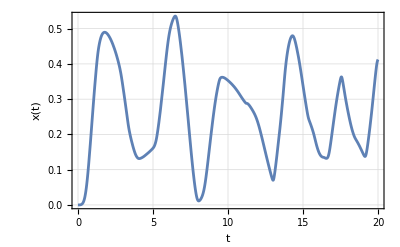

```mathematica
Plot[x[t]/.solTest,{t,0,tf},PlotRange-> All,FrameLabel-> {"t","x(t)"},Frame->True,GridLines-> Automatic]
```

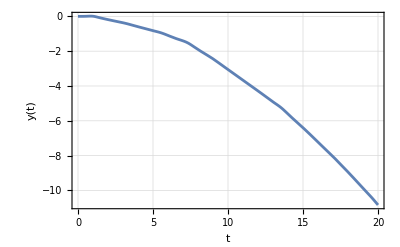

```mathematica
Plot[y[t]/.solTest,{t,0,tf},PlotRange-> All,FrameLabel-> {"t","y(t)"},Frame->True,GridLines-> Automatic]
```

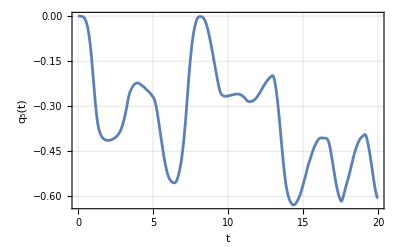

```mathematica
Plot[Subscript[q, 5][t]/.solTest,{t,0,tf},PlotRange-> All,FrameLabel-> {"t","q_5(t)"},Frame->True,GridLines-> Automatic]
```

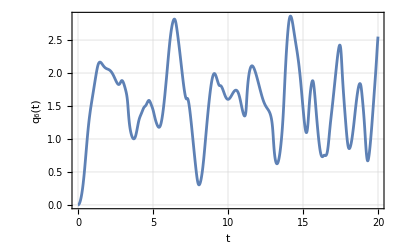

```mathematica
Plot[Subscript[q, 6][t]/.solTest,{t,0,tf},PlotRange-> All,FrameLabel-> {"t","q_6(t)"},Frame->True,GridLines-> Automatic]
```

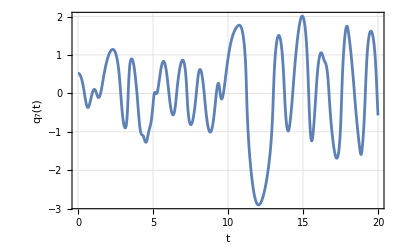

```mathematica
Plot[Subscript[q, 7][t]/.solTest,{t,0,tf},PlotRange-> All,FrameLabel-> {"t","q_7(t)"},Frame->True,GridLines-> Automatic]
```

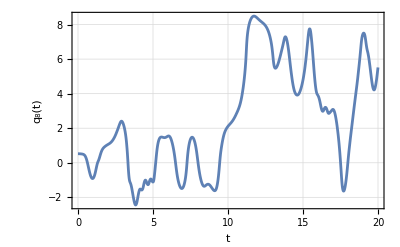

```mathematica
Plot[Subscript[q, 8][t]/.solTest,{t,0,tf},PlotRange-> All,FrameLabel-> {"t","q_8(t)"},Frame->True,GridLines-> Automatic]
```

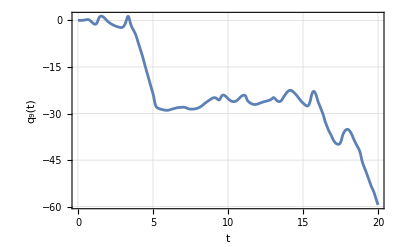

```mathematica
Plot[Subscript[q, 9][t]/.solTest,{t,0,tf},PlotRange-> All,FrameLabel-> {"t","q_9(t)"},Frame->True,GridLines-> Automatic]
```

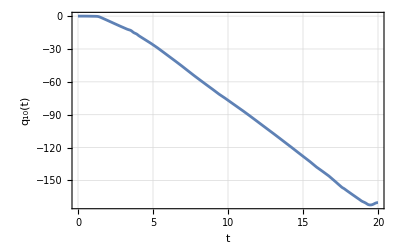

```mathematica
Plot[Subscript[q, 10][t]/.solTest,{t,0,tf},PlotRange-> All,FrameLabel-> {"t","q_10(t)"},Frame->True,GridLines-> Automatic]
```

This plot may take some time to complete.

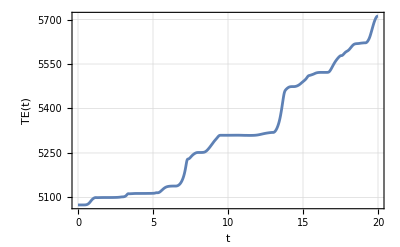

```mathematica
Plot[TEt/.solTest,{t,0,tf},PlotRange-> All,FrameLabel-> {"t","TE(t)"},Frame->True,GridLines-> Automatic]
```

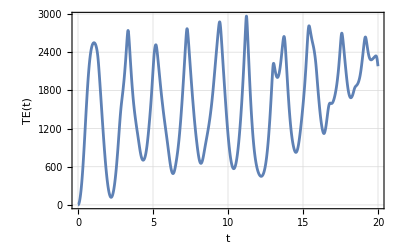

```mathematica
Plot[KEt/.solTest,{t,0,tf},PlotRange-> All,FrameLabel-> {"t","TE(t)"},Frame->True,GridLines-> Automatic]
```

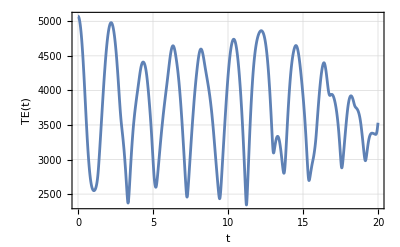

```mathematica
Plot[PEt/.solTest,{t,0,tf},PlotRange-> All,FrameLabel-> {"t","TE(t)"},Frame->True,GridLines-> Automatic]
```

```mathematica
x[t_]=x[t]/.solTest;
y[t_]=y[t]/.solTest;
Subscript[q, 5][t_]=Subscript[q, 5][t]/.solTest;
Subscript[q, 6][t_]=Subscript[q, 6][t]/.solTest;
Subscript[q, 7][t_]=Subscript[q, 7][t]/.solTest;
Subscript[q, 8][t_]=Subscript[q, 8][t]/.solTest;
Subscript[q, 9][t_]=Subscript[q, 9][t]/.solTest;
Subscript[q, 10][t_]=Subscript[q, 10][t]/.solTest;
```

Create composite graphic out of parts that have been rotated and translated

```mathematica
robotGraphicDynAnim={
(*Base graphic*)
Translate[GeometricTransformation[baseGraphic,Transpose[rotA]],{xAo,yAo,zAo}],

(*Wheel graphic*)
Translate[GeometricTransformation[wheelGraphic1,Transpose[rotA]],{xBo,yBo,zBo}],
Translate[GeometricTransformation[wheelGraphic2,Transpose[rotA]],{xCo,yCo,zCo}],
Translate[GeometricTransformation[wheelGraphic3,Transpose[rotA]],{xDo,yDo,zDo}],
Translate[GeometricTransformation[wheelGraphic4,Transpose[rotA]],{xEo,yEo,zEo}],


(*rotor*)
Translate[GeometricTransformation[rotatorGraphic,Transpose[rotF]],{xFo,yFo,zFo}],

(*joint 1*)
Translate[GeometricTransformation[jointGraphic1,Transpose[rotG]],{xGo,yGo,zGo}],

(*Arm1 graphic*)
Translate[GeometricTransformation[arm1baseGraphic,Transpose[rotH]],{xHo,yHo,zHo}],

(*Arm2 graphic*)
Translate[GeometricTransformation[arm2baseGraphic,Transpose[rotL]],{xLo,yLo,zLo}],

(*Arm3 graphic*)
Translate[GeometricTransformation[arm3baseGraphic,Transpose[rotS]],{xSo,ySo,zSo}],

(*Wrist1 graphic*)
Translate[GeometricTransformation[wristGraphic1,Transpose[rotM]],{xMo,yMo,zMo}],

(*Wrist2 graphic*)
Translate[GeometricTransformation[wristGraphic2,Transpose[rotP]],{xPo,yPo,zPo}]
};
```

```mathematica
robotGraphicDynAnimT[t_]=robotGraphicDynAnim;
```

Loop over time

```mathematica
tf=20;
```

```mathematica
Animate[Show[Graphics3D[robotGraphicDynAnimT[t],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-scale,scale},{-scale,scale},{-scale,scale}},AspectRatio->1,AxesLabel->{"X","Y","Z"}]],{t,0,tf,tf/500},AnimationRunning->False]
```

# Control Design

### Controller design

We have decided to try a proportional plus integral plus derivative (PID) control law for each motor.  To implement this we will treat each motor torque/force as a state.  So the integration will be performed by integrating the state equations, this implies that we must take two derivatives of the error, which can be problematic if the error is noisy.  This implies our desired path must be smooth up to second derivatives in time.

#### Control laws and control equations of motion

Clear everything again.

```mathematica
x[t_]=.
y[t_]=.
Subscript[q, 1][t_]=.
Subscript[q, 2][t_]=.
Subscript[q, 3][t_]=.
Subscript[q, 4][t_]=.
Subscript[q, 5][t_]=.
Subscript[q, 6][t_]=.
Subscript[q, 7][t_]=.
Subscript[q, 8][t_]=.
Subscript[q, 9][t_]=.
Subscript[q, 10][t_]=.
```

Unset::norep: Assignment on Subscript for q_1[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_2[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_3[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_4[t_] not found.

$Failed

```mathematica
Subscript[F, motx]=.
Subscript[F, moty]=.
Subscript[T, mot][1]=.
Subscript[T, mot][2]=.
Subscript[T, mot][3]=.
Subscript[T, mot][4]=.
Subscript[T, mot][5]=.
Subscript[T, mot][6]=.
Subscript[F, toolx]=.
Subscript[F, tooly]=.
Subscript[F, toolz]=.
Subscript[T, toolx]=.
Subscript[T, tooly]=.
Subscript[T, toolz]=.
```

```mathematica
ω=.
```

Here are the state equations for motor force and torque, desired minus actual is the error in a given state.  I will replace the place holder symbols for motor forces and torques with the states defined here later.

Base x-motor

```mathematica
err[1]=Subscript[x, d][t] - x[t];
eqM[1]=Subscript[Fm, x]'[t] - Subscript[K, Int][1]err[1] - Subscript[K, prop][1]D[err[1],t]- Subscript[K, deriv][1]D[err[1],{t,2}]
```

-K_Int[1] (-x[t]+x_d[t])+Fm_x'[t]-K_prop[1] (-x'[t]+x_d'[t])-K_deriv[1] (-x''[t]+x_d''[t])

Base y-motor

```mathematica
err[2]=Subscript[y, d][t] - y[t];
eqM[2]=Subscript[Fm, y]'[t] - Subscript[K, Int][2]err[2] - Subscript[K, prop][2]D[err[2],t]- Subscript[K, deriv][2]D[err[2],{t,2}]
```

-K_Int[2] (-y[t]+y_d[t])+Fm_y'[t]-K_prop[2] (-y'[t]+y_d'[t])-K_deriv[2] (-y''[t]+y_d''[t])

q_5-motor

```mathematica
err[3]=Subscript[q, d5][t] - Subscript[q, 5][t];
eqM[3]=Subscript[Tm, 1]'[t] - Subscript[K, Int][3]err[3] - Subscript[K, prop][3]D[err[3],t]- Subscript[K, deriv][3]D[err[3],{t,2}]
```

-K_Int[3] (-q_5[t]+q_d5[t])-K_prop[3] (-q_5'[t]+q_d5'[t])+Tm_1'[t]-K_deriv[3] (-q_5''[t]+q_d5''[t])

q_6-motor

```mathematica
err[4]=Subscript[q, d6][t] - Subscript[q, 6][t];
eqM[4]=Subscript[Tm, 2]'[t] - Subscript[K, Int][4]err[4] - Subscript[K, prop][4]D[err[4],t]- Subscript[K, deriv][4]D[err[4],{t,2}]
```

-K_Int[4] (-q_6[t]+q_d6[t])-K_prop[4] (-q_6'[t]+q_d6'[t])+Tm_2'[t]-K_deriv[4] (-q_6''[t]+q_d6''[t])

q_7-motor

```mathematica
err[5]=Subscript[q, d7][t] - Subscript[q, 7][t];
eqM[5]=Subscript[Tm, 3]'[t] - Subscript[K, Int][5]err[5] - Subscript[K, prop][5]D[err[5],t]- Subscript[K, deriv][5]D[err[5],{t,2}]
```

-K_Int[5] (-q_7[t]+q_d7[t])-K_prop[5] (-q_7'[t]+q_d7'[t])+Tm_3'[t]-K_deriv[5] (-q_7''[t]+q_d7''[t])

q_8-motor

```mathematica
err[6]=Subscript[q, d8][t] - Subscript[q, 8][t];
eqM[6]=Subscript[Tm, 4]'[t] - Subscript[K, Int][6]err[6] - Subscript[K, prop][6]D[err[6],t]- Subscript[K, deriv][6]D[err[6],{t,2}]
```

-K_Int[6] (-q_8[t]+q_d8[t])-K_prop[6] (-q_8'[t]+q_d8'[t])+Tm_4'[t]-K_deriv[6] (-q_8''[t]+q_d8''[t])

q_9-motor

```mathematica
err[7]=Subscript[q, d9][t] - Subscript[q, 9][t];
eqM[7]=Subscript[Tm, 5]'[t] - Subscript[K, Int][7]err[7] - Subscript[K, prop][7]D[err[7],t]- Subscript[K, deriv][7]D[err[7],{t,2}]
```

-K_Int[7] (-q_9[t]+q_d9[t])-K_prop[7] (-q_9'[t]+q_d9'[t])+Tm_5'[t]-K_deriv[7] (-q_9''[t]+q_d9''[t])

q_10-motor

```mathematica
err[8]=Subscript[q, d10][t] - Subscript[q, 10][t];
eqM[8]=Subscript[Tm, 6]'[t] - Subscript[K, Int][8]err[8] - Subscript[K, prop][8]D[err[8],t]- Subscript[K, deriv][8]D[err[8],{t,2}]
```

-K_Int[8] (-q_10[t]+q_d10[t])-K_prop[8] (-q_10'[t]+q_d10'[t])+Tm_6'[t]-K_deriv[8] (-q_10''[t]+q_d10''[t])

Replace the place holders with the states for motor forces and torques.

```mathematica
eqC[1]=eqT[1]//.{Subscript[F, motx]-> Subscript[Fm, x][t],Subscript[F, moty]-> Subscript[Fm, y][t],Subscript[T, mot][n_]-> Subscript[Tm, n][t]};
```

```mathematica
eqC[2]=eqT[2]//.{Subscript[F, motx]-> Subscript[Fm, x][t],Subscript[F, moty]-> Subscript[Fm, y][t],Subscript[T, mot][n_]-> Subscript[Tm, n][t]};
```

```mathematica
eqC[3]=eqT[3]//.{Subscript[F, motx]-> Subscript[Fm, x][t],Subscript[F, moty]-> Subscript[Fm, y][t],Subscript[T, mot][n_]-> Subscript[Tm, n][t]};
```

```mathematica
eqC[4]=eqT[4]//.{Subscript[F, motx]-> Subscript[Fm, x][t],Subscript[F, moty]-> Subscript[Fm, y][t],Subscript[T, mot][n_]-> Subscript[Tm, n][t]};
```

```mathematica
eqC[5]=eqT[5]//.{Subscript[F, motx]-> Subscript[Fm, x][t],Subscript[F, moty]-> Subscript[Fm, y][t],Subscript[T, mot][n_]-> Subscript[Tm, n][t]};
```

```mathematica
eqC[6]=eqT[6]//.{Subscript[F, motx]-> Subscript[Fm, x][t],Subscript[F, moty]-> Subscript[Fm, y][t],Subscript[T, mot][n_]-> Subscript[Tm, n][t]};
```

```mathematica
eqC[7]=eqT[7]//.{Subscript[F, motx]-> Subscript[Fm, x][t],Subscript[F, moty]-> Subscript[Fm, y][t],Subscript[T, mot][n_]-> Subscript[Tm, n][t]};
```

```mathematica
eqC[8]=eqT[8]//.{Subscript[F, motx]-> Subscript[Fm, x][t],Subscript[F, moty]-> Subscript[Fm, y][t],Subscript[T, mot][n_]-> Subscript[Tm, n][t]};
```

Now we want to design the controller gains based on the step response of the system at a given motor.  We will do this by holding all the other states constant for the given motor control constant determination.  We will also linearize the system equations so we can then use pole placement techniques to size the gains.

#### Control gains base x-motor

Base x-motor. Here we fixate all the other movements.

```mathematica
eqG[1]=eqC[1]//.{y[t]-> 0,y'[t]-> 0,y''[t]-> 0,Subscript[q, 5][t]->0,Subscript[q, 5]'[t]->0,Subscript[q, 5]''[t]->0,Subscript[q, 6][t]->0,Subscript[q, 6]'[t]->0,Subscript[q, 6]''[t]->0,Subscript[q, 7][t]->0,Subscript[q, 7]'[t]->0,Subscript[q, 7]''[t]->0,Subscript[q, 8][t]->0,Subscript[q, 8]'[t]->0,Subscript[q, 8]''[t]->0,Subscript[q, 9][t]->0,Subscript[q, 9]'[t]->0,Subscript[q, 9]''[t]->0,Subscript[q, 10][t]->0,Subscript[q, 10]'[t]->0,Subscript[q, 10]''[t]->0}//.{Subscript[Fm, y][t]-> 0,Subscript[Tm, 1][t]->0,Subscript[Tm, 2][t]->0,Subscript[Tm, 3][t]->0,Subscript[Tm, 4][t]->0,Subscript[Tm, 5][t]->0,Subscript[Tm, 6][t]->0}//.{Subscript[F, toolx]->0,Subscript[F, tooly]->0,Subscript[F, toolz]->0,Subscript[T, toolx]->0,Subscript[T, tooly]->0,Subscript[T, toolz]->0}
```

0.+Fm_x[t]-1241.46 x''[t]

Linearize the equation.

```mathematica
eqL[1]=Normal[Series[eqG[1],{x[t],0,1},{x'[t],0,1}]]
```

0.+Fm_x[t]-1241.46 x''[t]

We take a derivative to allow substitution of the motor control state equation.

```mathematica
eqLd[1]=D[eqL[1],t]
```

Fm_x'[t]-1241.46 x^(3)[t]

Solve the motor state equation for the motor force/torque derivative.

```mathematica
solM[1]=Solve[eqM[1]==0,Subscript[Fm, x]'[t]]//First
```

{Fm_x'[t]→-x[t] K_Int[1]+K_Int[1] x_d[t]-K_prop[1] x'[t]+K_prop[1] x_d'[t]-K_deriv[1] x''[t]+K_deriv[1] x_d''[t]}

Here is the complete linear equation for this motor in terms of the control gains.

```mathematica
eqLf[1]=eqLd[1]//.solM[1]
```

-x[t] K_Int[1]+K_Int[1] x_d[t]-K_prop[1] x'[t]+K_prop[1] x_d'[t]-K_deriv[1] x''[t]+K_deriv[1] x_d''[t]-1241.46 x^(3)[t]

This is the characteristic polynomial.

```mathematica
charEq[1]=eqLf[1]//.{Derivative[n_][x][t]->s^n,x[t]->1,Subscript[x, d][t]->0,Subscript[x, d]'[t]->0,Subscript[x, d]''[t]->0}
```

-1241.46 s^3-s^2 K_deriv[1]-K_Int[1]-s K_prop[1]

Put the characteristic equation in standard form.

```mathematica
charEq[1]=charEq[1]/Coefficient[charEq[1],s^3]//Expand
```

1. s^3+0.000805501 s^2 K_deriv[1]+0.000805501 K_Int[1]+0.000805501 s K_prop[1]

The desired characteristic polynomial is given by the following system with a first order pole and a second order pole pair.

```mathematica
charDesired[1]=Expand[(s+Subscript[a, 1])(s^2+ 2 Subscript[ζ, 1] Subscript[ω, n1] s + Subscript[ω, n1]^2)]
```

s^3+s^2 a_1+2 s^2 ζ_1 ω_n1+2 s a_1 ζ_1 ω_n1+s ω_n1^2+a_1 ω_n1^2

The time to peak is defined as

```mathematica
eqTp[1]=Subscript[t, p1]== π/(Subscript[ω, n1] √(1-Subscript[ζ, 1]^2));
```

The two percent settling time is given by

```mathematica
eqTs[1]=Subscript[t, s1]== 4/(Subscript[ζ, 1] Subscript[ω, n1]);
```

```mathematica
solZW[1]=Solve[{eqTp[1],eqTs[1]},{Subscript[ζ, 1],Subscript[ω, n1]}][[2]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{ζ_1→(4 t_p1)/(√(16 t_p1^2+π^2 t_s1^2)),ω_n1→(√(16 t_p1^2+π^2 t_s1^2))/(t_p1 t_s1)}

Set up equations for gains by equating coefficients of the characteristic polynomials.

```mathematica
eqGain1[1]=Coefficient[charEq[1],s^2]==Coefficient[charDesired[1],s^2]/.solZW[1]
```

0.000805501 K_deriv[1]==a_1+8/t_s1

```mathematica
eqGain2[1]=Coefficient[charEq[1],s]==Coefficient[charDesired[1],s]/.solZW[1]
```

0.000805501 K_prop[1]==(8 a_1)/t_s1+(16 t_p1^2+π^2 t_s1^2)/(t_p1^2 t_s1^2)

```mathematica
eqGain3[1]=(charEq[1]/.s->0)==(charDesired[1]/.s->0)/.solZW[1]
```

0.+0.000805501 K_Int[1]==(a_1 (16 t_p1^2+π^2 t_s1^2))/(t_p1^2 t_s1^2)

Solve for the controller gains.

```mathematica
solGains[1]=Solve[{eqGain1[1],eqGain2[1],eqGain3[1]},{Subscript[K, prop][1],Subscript[K, Int][1],Subscript[K, deriv][1]}]//First
```

{K_prop[1]→1241.46 ((8. a_1)/t_s1+(1. (16. t_p1^2+9.8696 t_s1^2))/(t_p1^2 t_s1^2)),K_Int[1]→1241.46 (0.+(1. a_1 (16. t_p1^2+9.8696 t_s1^2))/(t_p1^2 t_s1^2)),K_deriv[1]→1241.46 (1. a_1+8./t_s1)}

Now set the time constants.

```mathematica
tConstRules[1]={Subscript[a, 1]->100,Subscript[t, p1]->1/4,Subscript[t, s1]-> 1/2};
```

Check the step response

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
stepMag=5/100; (*5 cm*)
Subscript[x, d][t_]:=stepMag UnitStep[t]
stepSol[1]=NDSolve[{(eqG[1]/.solGains[1]/.tConstRules[1])==0,(eqM[1]/.solGains[1]/.tConstRules[1])==0,x'[Subscript[t, 0]]==0,x[Subscript[t, 0]]==0,Subscript[Fm, x][Subscript[t, 0]]==0},{x,Subscript[Fm, x]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{x→InterpolatingFunction[…],Fm_x→InterpolatingFunction[…]}}

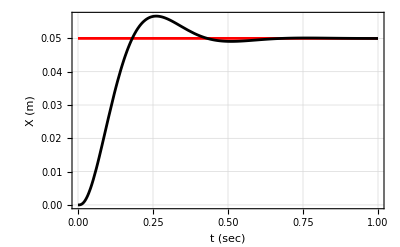

```mathematica
Plot[{Subscript[x, d][t],x[t]/.stepSol[1]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","X (m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system displacement response is good.  The desired value is in red.

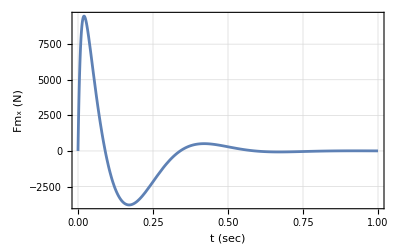

```mathematica
Plot[Subscript[Fm, x][t]/.stepSol[1],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Fm_x (N)"},PlotRange->All]
```

This is the force needed to do this step maneuver.  It is roughly 10000 pounds peak load.

Check the tracking of a polynomial.

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
Subscript[x, d][t_]:=(5 t^2+ 3 t + 1)/100 (* cm*)
trackSol[1]=NDSolve[{(eqG[1]/.solGains[1]/.tConstRules[1])==0,(eqM[1]/.solGains[1]/.tConstRules[1])==0,x'[Subscript[t, 0]]==0,x[Subscript[t, 0]]==0,Subscript[Fm, x][Subscript[t, 0]]==0},{x,Subscript[Fm, x]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{x→InterpolatingFunction[…],Fm_x→InterpolatingFunction[…]}}

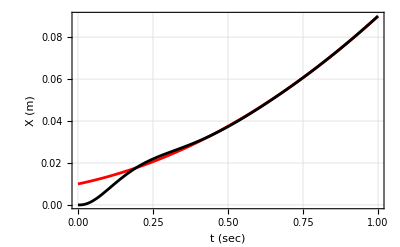

```mathematica
Plot[{Subscript[x, d][t],x[t]/.trackSol[1]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","X (m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system tracks a parabola fairly well, could be better initially, however this initial error is due to the step change at t=0.  So if we are nearer to the initial tracking curve, we should be ok.

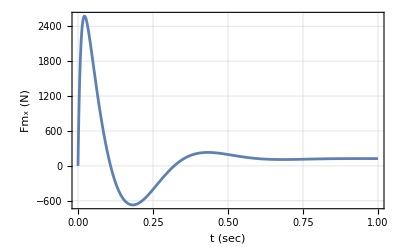

```mathematica
Plot[Subscript[Fm, x][t]/.trackSol[1],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Fm_x (N)"}, PlotRange->All]
```

Clear the desired variable.

```mathematica
Subscript[x, d][t_]=.
```

#### Control gains base y-motor

Base y-motor. Here we fixate all the other movements.

```mathematica
eqG[2]=eqC[2]//.{x[t]-> 0,x'[t]-> 0,x''[t]-> 0,Subscript[q, 5][t]->0,Subscript[q, 5]'[t]->0,Subscript[q, 5]''[t]->0,Subscript[q, 6][t]->0,Subscript[q, 6]'[t]->0,Subscript[q, 6]''[t]->0,Subscript[q, 7][t]->0,Subscript[q, 7]'[t]->0,Subscript[q, 7]''[t]->0,Subscript[q, 8][t]->0,Subscript[q, 8]'[t]->0,Subscript[q, 8]''[t]->0,Subscript[q, 9][t]->0,Subscript[q, 9]'[t]->0,Subscript[q, 9]''[t]->0,Subscript[q, 10][t]->0,Subscript[q, 10]'[t]->0,Subscript[q, 10]''[t]->0}//.{Subscript[Fm, x][t]-> 0,Subscript[Tm, 1][t]->0,Subscript[Tm, 2][t]->0,Subscript[Tm, 3][t]->0,Subscript[Tm, 4][t]->0,Subscript[Tm, 5][t]->0,Subscript[Tm, 6][t]->0}//.{Subscript[F, toolx]->0,Subscript[F, tooly]->0,Subscript[F, toolz]->0,Subscript[T, toolx]->0,Subscript[T, tooly]->0,Subscript[T, toolz]->0}
```

0.+Fm_y[t]-1241.46 y''[t]

Linearize the equation.

```mathematica
eqL[2]=Normal[Series[eqG[2],{y[t],0,1},{y'[t],0,1}]]
```

0.+Fm_y[t]-1241.46 y''[t]

We take a derivative to allow substitution of the motor control state equation.

```mathematica
eqLd[2]=D[eqL[2],t]
```

Fm_y'[t]-1241.46 y^(3)[t]

Solve the motor state equation for the motor force/torque derivative.

```mathematica
solM[2]=Solve[eqM[2]==0,Subscript[Fm, y]'[t]]//First
```

{Fm_y'[t]→-y[t] K_Int[2]+K_Int[2] y_d[t]-K_prop[2] y'[t]+K_prop[2] y_d'[t]-K_deriv[2] y''[t]+K_deriv[2] y_d''[t]}

Here is the complete linear equation for this motor in terms of the control gains.

```mathematica
eqLf[2]=eqLd[2]//.solM[2]
```

-y[t] K_Int[2]+K_Int[2] y_d[t]-K_prop[2] y'[t]+K_prop[2] y_d'[t]-K_deriv[2] y''[t]+K_deriv[2] y_d''[t]-1241.46 y^(3)[t]

This is the characteristic polynomial.

```mathematica
charEq[2]=eqLf[2]//.{Derivative[n_][y][t]->s^n,y[t]->1,Subscript[y, d][t]->0,Subscript[y, d]'[t]->0,Subscript[y, d]''[t]->0}
```

-1241.46 s^3-s^2 K_deriv[2]-K_Int[2]-s K_prop[2]

Put the characteristic equation in standard form.

```mathematica
charEq[2]=charEq[2]/Coefficient[charEq[2],s^3]//Expand
```

1. s^3+0.000805501 s^2 K_deriv[2]+0.000805501 K_Int[2]+0.000805501 s K_prop[2]

The desired characteristic polynomial is given by the following system with a first order pole and a second order pole pair.

```mathematica
charDesired[2]=Expand[(s+Subscript[a, 2])(s^2+ 2 Subscript[ζ, 2] Subscript[ω, n2] s + Subscript[ω, n2]^2)]
```

s^3+s^2 a_2+2 s^2 ζ_2 ω_n2+2 s a_2 ζ_2 ω_n2+s ω_n2^2+a_2 ω_n2^2

The time to peak is defined as

```mathematica
eqTp[2]=Subscript[t, p2]== π/(Subscript[ω, n2] √(1-Subscript[ζ, 2]^2));
```

The two percent settling time is given by

```mathematica
eqTs[2]=Subscript[t, s2]== 4/(Subscript[ζ, 2] Subscript[ω, n2]);
```

```mathematica
solZW[2]=Solve[{eqTp[2],eqTs[2]},{Subscript[ζ, 2],Subscript[ω, n2]}][[2]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{ζ_2→(4 t_p2)/(√(16 t_p2^2+π^2 t_s2^2)),ω_n2→(√(16 t_p2^2+π^2 t_s2^2))/(t_p2 t_s2)}

Set up equations for gains by equating coefficients of the characterstic polynomials.

```mathematica
eqGain1[2]=Coefficient[charEq[2],s^2]==Coefficient[charDesired[2],s^2]/.solZW[2]
```

0.000805501 K_deriv[2]==a_2+8/t_s2

```mathematica
eqGain2[2]=Coefficient[charEq[2],s]==Coefficient[charDesired[2],s]/.solZW[2]
```

0.000805501 K_prop[2]==(8 a_2)/t_s2+(16 t_p2^2+π^2 t_s2^2)/(t_p2^2 t_s2^2)

```mathematica
eqGain3[2]=(charEq[2]/.s->0)==(charDesired[2]/.s->0)/.solZW[2]
```

0.+0.000805501 K_Int[2]==(a_2 (16 t_p2^2+π^2 t_s2^2))/(t_p2^2 t_s2^2)

Solve for the controller gains.

```mathematica
solGains[2]=Solve[{eqGain1[2],eqGain2[2],eqGain3[2]},{Subscript[K, prop][2],Subscript[K, Int][2],Subscript[K, deriv][2]}]//First
```

{K_prop[2]→1241.46 ((8. a_2)/t_s2+(1. (16. t_p2^2+9.8696 t_s2^2))/(t_p2^2 t_s2^2)),K_Int[2]→1241.46 (0.+(1. a_2 (16. t_p2^2+9.8696 t_s2^2))/(t_p2^2 t_s2^2)),K_deriv[2]→1241.46 (1. a_2+8./t_s2)}

Now set the time constants.

```mathematica
tConstRules[2]={Subscript[a, 2]->100,Subscript[t, p2]->1/4,Subscript[t, s2]-> 1/2};
```

Check the step response

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
stepMag=5/100; (*5 cm*)
Subscript[y, d][t_]:=stepMag UnitStep[t]
stepSol[2]=NDSolve[{(eqG[2]/.solGains[2]/.tConstRules[2])==0,(eqM[2]/.solGains[2]/.tConstRules[2])==0,y'[Subscript[t, 0]]==0,y[Subscript[t, 0]]==0,Subscript[Fm, y][Subscript[t, 0]]==0},{y,Subscript[Fm, y]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{y→InterpolatingFunction[…],Fm_y→InterpolatingFunction[…]}}

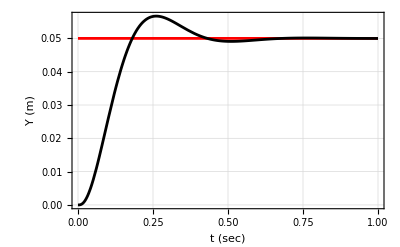

```mathematica
Plot[{Subscript[y, d][t],y[t]/.stepSol[2]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Y (m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system displacement response is good.  The desired value is in red.

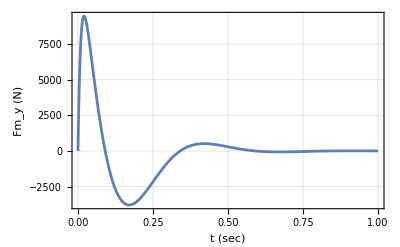

```mathematica
Plot[Subscript[Fm, y][t]/.stepSol[2],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Fm_y (N)"},PlotRange->All]
```

This is the force needed to do this step maneuver.  It is roughly 10000 pounds peak load.

Check the tracking of a polynomial.

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
Subscript[y, d][t_]:=(5 t^2+ 3 t + 1)/100 (* cm*)
trackSol[2]=NDSolve[{(eqG[2]/.solGains[2]/.tConstRules[2])==0,(eqM[2]/.solGains[2]/.tConstRules[2])==0,y'[Subscript[t, 0]]==0,y[Subscript[t, 0]]==0,Subscript[Fm, y][Subscript[t, 0]]==0},{y,Subscript[Fm, y]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{y→InterpolatingFunction[…],Fm_y→InterpolatingFunction[…]}}

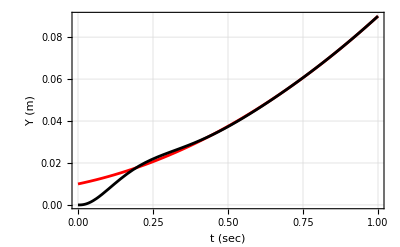

```mathematica
Plot[{Subscript[y, d][t],y[t]/.trackSol[2]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Y (m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system tracks a parabola fairly well, could be better initially, however this initial error is due to the step change at t=0.  So if we are nearer to the initial tracking curve, we should be ok.

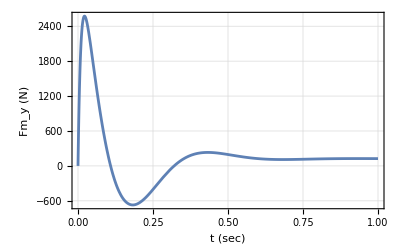

```mathematica
Plot[Subscript[Fm, y][t]/.trackSol[2],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Fm_y (N)"}, PlotRange->All]
```

Clear the desired variable.

```mathematica
Subscript[y, d][t_]=.
```

#### Control gains q_5-motor

q_5-motor. Here we fixate all the other movements.

```mathematica
eqG[3]=eqC[3]//.{x[t]-> 0,x'[t]-> 0,x''[t]-> 0,y[t]-> 0,y'[t]-> 0,y''[t]-> 0,Subscript[q, 6][t]->0,Subscript[q, 6]'[t]->0,Subscript[q, 6]''[t]->0,Subscript[q, 7][t]->0,Subscript[q, 7]'[t]->0,Subscript[q, 7]''[t]->0,Subscript[q, 8][t]->0,Subscript[q, 8]'[t]->0,Subscript[q, 8]''[t]->0,Subscript[q, 9][t]->0,Subscript[q, 9]'[t]->0,Subscript[q, 9]''[t]->0,Subscript[q, 10][t]->0,Subscript[q, 10]'[t]->0,Subscript[q, 10]''[t]->0}//.{Subscript[Fm, x][t]-> 0,Subscript[Fm, y][t]-> 0,Subscript[Tm, 2][t]->0,Subscript[Tm, 3][t]->0,Subscript[Tm, 4][t]->0,Subscript[Tm, 5][t]->0,Subscript[Tm, 6][t]->0}//.{Subscript[F, toolx]->0,Subscript[F, tooly]->0,Subscript[F, toolz]->0,Subscript[T, toolx]->0,Subscript[T, tooly]->0,Subscript[T, toolz]->0}
```

0.+Tm_1[t]+6.6 (0.-9.92385 q_5'[t]^2)+5.38333 (0.-3.46408 q_5'[t]^2)+5.81667 (0.-1.55883 q_5'[t]^2)-0.525 (0.+0.623534 q_5'[t]^2)+11.6333 (0.+0.779417 q_5'[t]^2)+10.7667 (0.+1.73204 q_5'[t]^2)+5.81667 (0.+3.27355 q_5'[t]^2)-0.525 (0.+4.15689 q_5'[t]^2)-0.525 (0.+4.61877 q_5'[t]^2)+8.1 (0.+4.96193 q_5'[t]^2)+5.38333 (0.+7.27456 q_5'[t]^2)-0.525 (0.+9.35301 q_5'[t]^2)-0.525 (0.+10.9118 q_5'[t]^2)-0.525 (0.+11.2236 q_5'[t]^2)-0.525 (0.+20.7845 q_5'[t]^2)+6.6 (0.+20.8401 q_5'[t]^2)-0.525 (0.+24.2485 q_5'[t]^2)-0.525 (0.+24.9414 q_5'[t]^2)+0.75 (0.+26.0501 q_5'[t]^2)-0.8 (0.+29.7716 q_5'[t]^2)-0.525 (0.+37.2144 q_5'[t]^2)-0.525 (0.+59.5431 q_5'[t]^2)-0.8 (0.+71.4517 q_5'[t]^2)-1689.32 q_5''[t]

Linearize the equation.

```mathematica
eqL[3]=Normal[Series[eqG[3],{Subscript[q, 1][t],0,1},{Subscript[q, 1]'[t],0,1}]]
```

0.+Tm_1[t]+6.6 (0.-9.92385 q_5'[t]^2)+5.38333 (0.-3.46408 q_5'[t]^2)+5.81667 (0.-1.55883 q_5'[t]^2)-0.525 (0.+0.623534 q_5'[t]^2)+11.6333 (0.+0.779417 q_5'[t]^2)+10.7667 (0.+1.73204 q_5'[t]^2)+5.81667 (0.+3.27355 q_5'[t]^2)-0.525 (0.+4.15689 q_5'[t]^2)-0.525 (0.+4.61877 q_5'[t]^2)+8.1 (0.+4.96193 q_5'[t]^2)+5.38333 (0.+7.27456 q_5'[t]^2)-0.525 (0.+9.35301 q_5'[t]^2)-0.525 (0.+10.9118 q_5'[t]^2)-0.525 (0.+11.2236 q_5'[t]^2)-0.525 (0.+20.7845 q_5'[t]^2)+6.6 (0.+20.8401 q_5'[t]^2)-0.525 (0.+24.2485 q_5'[t]^2)-0.525 (0.+24.9414 q_5'[t]^2)+0.75 (0.+26.0501 q_5'[t]^2)-0.8 (0.+29.7716 q_5'[t]^2)-0.525 (0.+37.2144 q_5'[t]^2)-0.525 (0.+59.5431 q_5'[t]^2)-0.8 (0.+71.4517 q_5'[t]^2)-1689.32 q_5''[t]

We take a derivative to allow substitution of the motor control state equation.

```mathematica
eqLd[3]=D[eqL[3],t]
```

Tm_1'[t]+5.68434×10^-14 q_5'[t] q_5''[t]-1689.32 q_5^(3)[t]

Solve the motor state equation for the motor force/torque derivative.

```mathematica
solM[3]=Solve[eqM[3]==0,Subscript[Tm, 1]'[t]]//First
```

{Tm_1'[t]→-K_Int[3] q_5[t]+K_Int[3] q_d5[t]-K_prop[3] q_5'[t]+K_prop[3] q_d5'[t]-K_deriv[3] q_5''[t]+K_deriv[3] q_d5''[t]}

Here is the complete linear equation for this motor in terms of the control gains.

```mathematica
eqLf[3]=eqLd[3]//.solM[3]
```

-K_Int[3] q_5[t]+K_Int[3] q_d5[t]-K_prop[3] q_5'[t]+K_prop[3] q_d5'[t]-K_deriv[3] q_5''[t]+5.68434×10^-14 q_5'[t] q_5''[t]+K_deriv[3] q_d5''[t]-1689.32 q_5^(3)[t]

This is the characteristic polynomial.

```mathematica
charEq[3]=eqLf[3]//.{Derivative[n_][Subscript[q, 5]][t]->s^n,Subscript[q, 5][t]->1,Subscript[q, d5][t]->0,Subscript[q, d5]'[t]->0,Subscript[q, d5]''[t]->0}
```

-1689.32 s^3-s^2 K_deriv[3]-K_Int[3]-s K_prop[3]

Put the characteristic equation in standard form.

```mathematica
charEq[3]=charEq[3]/Coefficient[charEq[3],s^3]//Expand
```

1. s^3+0.000591956 s^2 K_deriv[3]+0.000591956 K_Int[3]+0.000591956 s K_prop[3]

The desired characteristic polynomial is given by the following system with a first order pole and a second order pole pair.

```mathematica
charDesired[3]=Expand[(s+Subscript[a, 3])(s^2+ 2 Subscript[ζ, 3] Subscript[ω, n3] s + Subscript[ω, n3]^2)]
```

s^3+s^2 a_3+2 s^2 ζ_3 ω_n3+2 s a_3 ζ_3 ω_n3+s ω_n3^2+a_3 ω_n3^2

The time to peak is defined as

```mathematica
eqTp[3]=Subscript[t, p3]== π/(Subscript[ω, n3] √(1-Subscript[ζ, 3]^2));
```

The two percent settling time is given by

```mathematica
eqTs[3]=Subscript[t, s3]== 4/(Subscript[ζ, 3] Subscript[ω, n3]);
```

```mathematica
solZW[3]=Solve[{eqTp[3],eqTs[3]},{Subscript[ζ, 3],Subscript[ω, n3]}][[2]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{ζ_3→(4 t_p3)/(√(16 t_p3^2+π^2 t_s3^2)),ω_n3→(√(16 t_p3^2+π^2 t_s3^2))/(t_p3 t_s3)}

Set up equations for gains by equating coefficients of the characterstic polynomials.

```mathematica
eqGain1[3]=Coefficient[charEq[3],s^2]==Coefficient[charDesired[3],s^2]/.solZW[3]
```

0.000591956 K_deriv[3]==a_3+8/t_s3

```mathematica
eqGain2[3]=Coefficient[charEq[3],s]==Coefficient[charDesired[3],s]/.solZW[3]
```

0.000591956 K_prop[3]==(8 a_3)/t_s3+(16 t_p3^2+π^2 t_s3^2)/(t_p3^2 t_s3^2)

```mathematica
eqGain3[3]=(charEq[3]/.s->0)==(charDesired[3]/.s->0)/.solZW[3]
```

0.+0.000591956 K_Int[3]==(a_3 (16 t_p3^2+π^2 t_s3^2))/(t_p3^2 t_s3^2)

Solve for the controller gains.

```mathematica
solGains[3]=Solve[{eqGain1[3],eqGain2[3],eqGain3[3]},{Subscript[K, prop][3],Subscript[K, Int][3],Subscript[K, deriv][3]}]//First
```

{K_prop[3]→1689.32 ((8. a_3)/t_s3+(1. (16. t_p3^2+9.8696 t_s3^2))/(t_p3^2 t_s3^2)),K_Int[3]→1689.32 (0.+(1. a_3 (16. t_p3^2+9.8696 t_s3^2))/(t_p3^2 t_s3^2)),K_deriv[3]→1689.32 (1. a_3+8./t_s3)}

Now set the time constants.

```mathematica
tConstRules[3]={Subscript[a, 3]->100,Subscript[t, p3]->1/4,Subscript[t, s3]-> 1/2};
```

Check the step response

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
stepMag=2π/180; (*2 degrees*)
Subscript[q, d5][t_]:=stepMag UnitStep[t]
stepSol[3]=NDSolve[{(eqG[3]/.solGains[3]/.tConstRules[3])==0,(eqM[3]/.solGains[3]/.tConstRules[3])==0,Subscript[q, 5]'[Subscript[t, 0]]==0,Subscript[q, 5][Subscript[t, 0]]==0,Subscript[Tm, 1][Subscript[t, 0]]==0},{Subscript[q, 5],Subscript[Tm, 1]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{q_5→InterpolatingFunction[…],Tm_1→InterpolatingFunction[…]}}

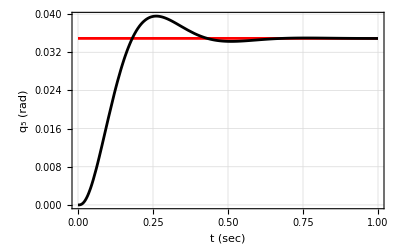

```mathematica
Plot[{Subscript[q, d5][t],Subscript[q, 5][t]/.stepSol[3]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_5 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system displacement response is good.  The desired value is in red.

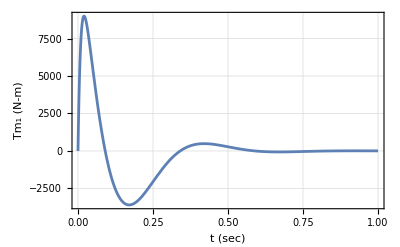

```mathematica
Plot[Subscript[Tm, 1][t]/.stepSol[3],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_1 (N-m)"},PlotRange->All]
```

This is the force needed to do this step maneuver.  It is roughly 8500 ft-lb peak torque.

Check the tracking of a polynomial.

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
Subscript[q, d5][t_]:=(5 t^2+ 3 t + 1)π/180 (*rad*)
trackSol[3]=NDSolve[{(eqG[3]/.solGains[3]/.tConstRules[3])==0,(eqM[3]/.solGains[3]/.tConstRules[3])==0,Subscript[q, 5]'[Subscript[t, 0]]==0,Subscript[q, 5][Subscript[t, 0]]==0,Subscript[Tm, 1][Subscript[t, 0]]==0},{Subscript[q, 5],Subscript[Tm, 1]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{q_5→InterpolatingFunction[…],Tm_1→InterpolatingFunction[…]}}

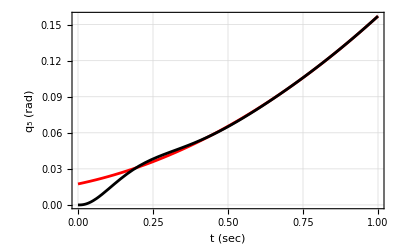

```mathematica
Plot[{Subscript[q, d5][t],Subscript[q, 5][t]/.trackSol[3]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_5 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system tracks a parabola fairly well, could be better initially, however this initial error is due to the step change at t=0.  So if we are nearer to the initial tracking curve, we should be ok.

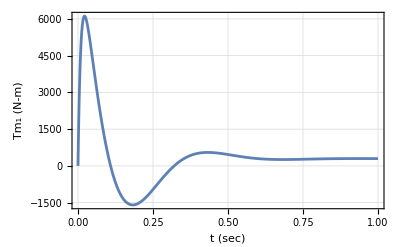

```mathematica
Plot[Subscript[Tm, 1][t]/.trackSol[3],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_1 (N-m)"}, PlotRange->All]
```

Clear the desired variable.

```mathematica
Subscript[q, d5][t_]=.
```

#### Control gains q_6-motor

q_6-motor. Here we fixate all the other movements.

```mathematica
eqG[4]=eqC[4]//.{x[t]-> 0,x'[t]-> 0,x''[t]-> 0,y[t]-> 0,y'[t]-> 0,y''[t]-> 0,Subscript[q, 5][t]->0,Subscript[q, 5]'[t]->0,Subscript[q, 5]''[t]->0,Subscript[q, 7][t]->0,Subscript[q, 7]'[t]->0,Subscript[q, 7]''[t]->0,Subscript[q, 8][t]->0,Subscript[q, 8]'[t]->0,Subscript[q, 8]''[t]->0,Subscript[q, 9][t]->0,Subscript[q, 9]'[t]->0,Subscript[q, 9]''[t]->0,Subscript[q, 10][t]->0,Subscript[q, 10]'[t]->0,Subscript[q, 10]''[t]->0}//.{Subscript[Fm, x][t]-> 0,Subscript[Fm, y][t]-> 0,Subscript[Tm, 1][t]->0,Subscript[Tm, 3][t]->0,Subscript[Tm, 4][t]->0,Subscript[Tm, 5][t]->0,Subscript[Tm, 6][t]->0}//.{Subscript[F, toolx]->0,Subscript[F, tooly]->0,Subscript[F, toolz]->0,Subscript[T, toolx]->0,Subscript[T, tooly]->0,Subscript[T, toolz]->0}
```

0.+3657.67 Cos[q_6[t]]+Tm_2[t]+0.75 (0.+486.765 Cos[q_6[t]]-37.2144 q_6''[t])-666.791 q_6''[t]-954.342 (Cos[q_6[t]]^2+Sin[q_6[t]]^2) q_6''[t]

Linearize the equation.

```mathematica
eqL[4]=Normal[Series[eqG[4],{Subscript[q, 6][t],0,1},{Subscript[q, 6]'[t],0,1}]]
```

4022.75+Tm_2[t]-1649.04 q_6''[t]

We take a derivative to allow substitution of the motor control state equation.

```mathematica
eqLd[4]=D[eqL[4],t]
```

Tm_2'[t]-1649.04 q_6^(3)[t]

Solve the motor state equation for the motor force/torque derivative.

```mathematica
solM[4]=Solve[eqM[4]==0,Subscript[Tm, 2]'[t]]//First
```

{Tm_2'[t]→-K_Int[4] q_6[t]+K_Int[4] q_d6[t]-K_prop[4] q_6'[t]+K_prop[4] q_d6'[t]-K_deriv[4] q_6''[t]+K_deriv[4] q_d6''[t]}

Here is the complete linear equation for this motor in terms of the control gains.

```mathematica
eqLf[4]=eqLd[4]//.solM[4]
```

-K_Int[4] q_6[t]+K_Int[4] q_d6[t]-K_prop[4] q_6'[t]+K_prop[4] q_d6'[t]-K_deriv[4] q_6''[t]+K_deriv[4] q_d6''[t]-1649.04 q_6^(3)[t]

This is the characteristic polynomial.

```mathematica
charEq[4]=eqLf[4]//.{Derivative[n_][Subscript[q, 6]][t]->s^n,Subscript[q, 6][t]->1,Subscript[q, d6][t]->0,Subscript[q, d6]'[t]->0,Subscript[q, d6]''[t]->0}
```

-1649.04 s^3-s^2 K_deriv[4]-K_Int[4]-s K_prop[4]

Put the characteristic equation in standard form.

```mathematica
charEq[4]=charEq[4]/Coefficient[charEq[4],s^3]//Expand
```

1. s^3+0.000606412 s^2 K_deriv[4]+0.000606412 K_Int[4]+0.000606412 s K_prop[4]

The desired characteristic polynomial is given by the following system with a first order pole and a second order pole pair.

```mathematica
charDesired[4]=Expand[(s+Subscript[a, 4])(s^2+ 2 Subscript[ζ, 4] Subscript[ω, n4] s + Subscript[ω, n4]^2)]
```

s^3+s^2 a_4+2 s^2 ζ_4 ω_n4+2 s a_4 ζ_4 ω_n4+s ω_n4^2+a_4 ω_n4^2

The time to peak is defined as

```mathematica
eqTp[4]=Subscript[t, p4]== π/(Subscript[ω, n4] √(1-Subscript[ζ, 4]^2));
```

The two percent settling time is given by

```mathematica
eqTs[4]=Subscript[t, s4]== 4/(Subscript[ζ, 4] Subscript[ω, n4]);
```

```mathematica
solZW[4]=Solve[{eqTp[4],eqTs[4]},{Subscript[ζ, 4],Subscript[ω, n4]}][[2]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{ζ_4→(4 t_p4)/(√(16 t_p4^2+π^2 t_s4^2)),ω_n4→(√(16 t_p4^2+π^2 t_s4^2))/(t_p4 t_s4)}

Set up equations for gains by equating coefficients of the characteristic polynomials.

```mathematica
eqGain1[4]=Coefficient[charEq[4],s^2]==Coefficient[charDesired[4],s^2]/.solZW[4]
```

0.000606412 K_deriv[4]==a_4+8/t_s4

```mathematica
eqGain2[4]=Coefficient[charEq[4],s]==Coefficient[charDesired[4],s]/.solZW[4]
```

0.000606412 K_prop[4]==(8 a_4)/t_s4+(16 t_p4^2+π^2 t_s4^2)/(t_p4^2 t_s4^2)

```mathematica
eqGain3[4]=(charEq[4]/.s->0)==(charDesired[4]/.s->0)/.solZW[4]
```

0.+0.000606412 K_Int[4]==(a_4 (16 t_p4^2+π^2 t_s4^2))/(t_p4^2 t_s4^2)

Solve for the controller gains.

```mathematica
solGains[4]=Solve[{eqGain1[4],eqGain2[4],eqGain3[4]},{Subscript[K, prop][4],Subscript[K, Int][4],Subscript[K, deriv][4]}]//First
```

{K_prop[4]→1649.04 ((8. a_4)/t_s4+(1. (16. t_p4^2+9.8696 t_s4^2))/(t_p4^2 t_s4^2)),K_Int[4]→1649.04 (0.+(1. a_4 (16. t_p4^2+9.8696 t_s4^2))/(t_p4^2 t_s4^2)),K_deriv[4]→1649.04 (1. a_4+8./t_s4)}

Now set the time constants.

```mathematica
tConstRules[4]={Subscript[a, 4]->10,Subscript[t, p4]->1/4,Subscript[t, s4]-> 1/2};
```

Check the step response

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
stepMag=2π/180; (*2 degrees*)
Subscript[q, d6][t_]:=stepMag UnitStep[t]
stepSol[4]=NDSolve[{(eqG[4]/.solGains[4]/.tConstRules[4])==0,(eqM[4]/.solGains[4]/.tConstRules[4])==0,Subscript[q, 6]'[Subscript[t, 0]]==0,Subscript[q, 6][Subscript[t, 0]]==0,Subscript[Tm, 2][Subscript[t, 0]]==0},{Subscript[q, 6],Subscript[Tm, 2]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{q_6→InterpolatingFunction[…],Tm_2→InterpolatingFunction[…]}}

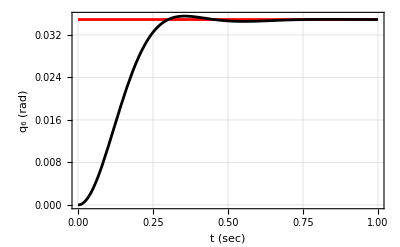

```mathematica
Plot[{Subscript[q, d6][t],Subscript[q, 6][t]/.stepSol[4]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_6 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system displacement response is good.  The desired value is in red. Notice here how the gravity load affects the settling time.  There is more undershoot than for the motors wothout gravity load.

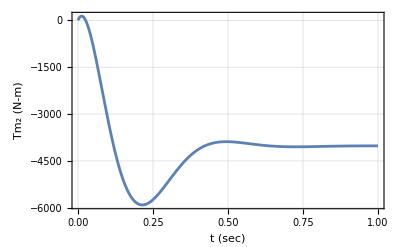

```mathematica
Plot[Subscript[Tm, 2][t]/.stepSol[4],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_2 (N-m)"},PlotRange->All]
```

This is the force needed to do this step maneuver.

Check the tracking of a polynomial.

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
Subscript[q, d6][t_]:=(5 t^2+ 3 t + 1)π/180 (*rad*)
trackSol[4]=NDSolve[{(eqG[4]/.solGains[4]/.tConstRules[4])==0,(eqM[4]/.solGains[4]/.tConstRules[4])==0,Subscript[q, 6]'[Subscript[t, 0]]==0,Subscript[q, 6][Subscript[t, 0]]==0,Subscript[Tm, 2][Subscript[t, 0]]==0},{Subscript[q, 6],Subscript[Tm, 2]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{q_6→InterpolatingFunction[…],Tm_2→InterpolatingFunction[…]}}

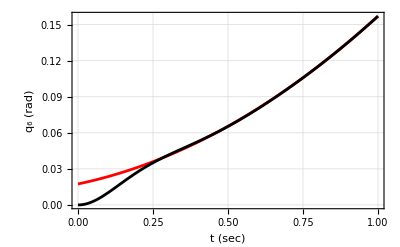

```mathematica
Plot[{Subscript[q, d6][t],Subscript[q, 6][t]/.trackSol[4]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_6 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system tracks a parabola fairly well, could be better initially, however this initial error is due to the step change at t=0.  So if we are nearer to the initial tracking curve, we should be ok.

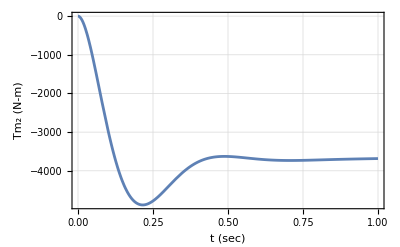

```mathematica
Plot[Subscript[Tm, 2][t]/.trackSol[4],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_2 (N-m)"}, PlotRange->All]
```

Clear the desired variable.

```mathematica
Subscript[q, d6][t_]=.
```

#### Control gains q_7-motor

q_3-motor. Here we fixate all the other movements.

```mathematica
eqG[5]=eqC[5]//.{x[t]-> 0,x'[t]-> 0,x''[t]-> 0,y[t]-> 0,y'[t]-> 0,y''[t]-> 0,Subscript[q, 5][t]->0,Subscript[q, 5]'[t]->0,Subscript[q, 5]''[t]->0,Subscript[q, 6][t]->0,Subscript[q, 6]'[t]->0,Subscript[q, 6]''[t]->0,Subscript[q, 8][t]->0,Subscript[q, 8]'[t]->0,Subscript[q, 8]''[t]->0,Subscript[q, 9][t]->0,Subscript[q, 9]'[t]->0,Subscript[q, 9]''[t]->0,Subscript[q, 10][t]->0,Subscript[q, 10]'[t]->0,Subscript[q, 10]''[t]->0}//.{Subscript[Fm, x][t]-> 0,Subscript[Fm, y][t]-> 0,Subscript[Tm, 1][t]->0,Subscript[Tm, 2][t]->0,Subscript[Tm, 4][t]->0,Subscript[Tm, 5][t]->0,Subscript[Tm, 6][t]->0}//.{Subscript[F, toolx]->0,Subscript[F, tooly]->0,Subscript[F, toolz]->0,Subscript[T, toolx]->0,Subscript[T, tooly]->0,Subscript[T, toolz]->0}
```

0.+1608.95 Cos[q_7[t]]+Tm_3[t]+0.75 (0.+389.412 Cos[q_7[t]]-29.7716 q_7''[t])-272.01 q_7''[t]-256.722 (Cos[q_7[t]]^2+Sin[q_7[t]]^2) q_7''[t]

Linearize the equation.

```mathematica
eqL[5]=Normal[Series[eqG[5],{Subscript[q, 7][t],0,1},{Subscript[q, 7]'[t],0,1}]]
```

1901.01+Tm_3[t]-551.061 q_7''[t]

We take a derivative to allow substitution of the motor control state equation.

```mathematica
eqLd[5]=D[eqL[5],t]
```

Tm_3'[t]-551.061 q_7^(3)[t]

Solve the motor state equation for the motor force/torque derivative.

```mathematica
solM[5]=Solve[eqM[5]==0,Subscript[Tm, 3]'[t]]//First
```

{Tm_3'[t]→-K_Int[5] q_7[t]+K_Int[5] q_d7[t]-K_prop[5] q_7'[t]+K_prop[5] q_d7'[t]-K_deriv[5] q_7''[t]+K_deriv[5] q_d7''[t]}

Here is the complete linear equation for this motor in terms of the control gains.

```mathematica
eqLf[5]=eqLd[5]//.solM[5]
```

-K_Int[5] q_7[t]+K_Int[5] q_d7[t]-K_prop[5] q_7'[t]+K_prop[5] q_d7'[t]-K_deriv[5] q_7''[t]+K_deriv[5] q_d7''[t]-551.061 q_7^(3)[t]

This is the characteristic polynomial.

```mathematica
charEq[5]=eqLf[5]//.{Derivative[n_][Subscript[q, 7]][t]->s^n,Subscript[q, 7][t]->1,Subscript[q, 7][t]->0,Subscript[q, d7]'[t]->0,Subscript[q, d7]''[t]->0}
```

-551.061 s^3-s^2 K_deriv[5]-K_Int[5]-s K_prop[5]+K_Int[5] q_d7[t]

Put the characteristic equation in standard form.

```mathematica
charEq[5]=charEq[5]/Coefficient[charEq[5],s^3]//Expand
```

1. s^3+0.00181468 s^2 K_deriv[5]+0.00181468 K_Int[5]+0.00181468 s K_prop[5]-0.00181468 K_Int[5] q_d7[t]

The desired characteristic polynomial is given by the following system with a first order pole and a second order pole pair.

```mathematica
charDesired[5]=Expand[(s+Subscript[a, 5])(s^2+ 2 Subscript[ζ, 5] Subscript[ω, n5] s + Subscript[ω, n5]^2)]
```

s^3+s^2 a_5+2 s^2 ζ_5 ω_n5+2 s a_5 ζ_5 ω_n5+s ω_n5^2+a_5 ω_n5^2

The time to peak is defined as

```mathematica
eqTp[5]=Subscript[t, p5]== π/(Subscript[ω, n5] √(1-Subscript[ζ, 5]^2));
```

The two percent settling time is given by

```mathematica
eqTs[5]=Subscript[t, s5]== 4/(Subscript[ζ, 5] Subscript[ω, n5]);
```

```mathematica
solZW[5]=Solve[{eqTp[5],eqTs[5]},{Subscript[ζ, 5],Subscript[ω, n5]}][[2]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{ζ_5→(4 t_p5)/(√(16 t_p5^2+π^2 t_s5^2)),ω_n5→(√(16 t_p5^2+π^2 t_s5^2))/(t_p5 t_s5)}

Set up equations for gains by equating coefficients of the characteristic polynomials.

```mathematica
eqGain1[5]=Coefficient[charEq[5],s^2]==Coefficient[charDesired[5],s^2]/.solZW[5]
```

0.00181468 K_deriv[5]==a_5+8/t_s5

```mathematica
eqGain2[5]=Coefficient[charEq[5],s]==Coefficient[charDesired[5],s]/.solZW[5]
```

0.00181468 K_prop[5]==(8 a_5)/t_s5+(16 t_p5^2+π^2 t_s5^2)/(t_p5^2 t_s5^2)

```mathematica
eqGain3[5]=(charEq[5]/.s->0)==(charDesired[5]/.s->0)/.solZW[5]
```

0.+0.00181468 K_Int[5]-0.00181468 K_Int[5] q_d7[t]==(a_5 (16 t_p5^2+π^2 t_s5^2))/(t_p5^2 t_s5^2)

Solve for the controller gains.

```mathematica
solGains[5]=Solve[{eqGain1[5],eqGain2[5],eqGain3[5]},{Subscript[K, prop][5],Subscript[K, Int][5],Subscript[K, deriv][5]}]//First
```

{K_prop[5]→551.061 ((8. a_5)/t_s5+(1. (16. t_p5^2+9.8696 t_s5^2))/(t_p5^2 t_s5^2)),K_Int[5]→(0.+(1. a_5 (16. t_p5^2+9.8696 t_s5^2))/(t_p5^2 t_s5^2))/(0.00181468-0.00181468 q_d7[t]),K_deriv[5]→551.061 (1. a_5+8./t_s5)}

Now set the time constants.

```mathematica
tConstRules[5]={Subscript[a, 5]->10,Subscript[t, p5]->1/4,Subscript[t, s5]-> 1/2};
```

Check the step response

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
stepMag=2π/180; (*2 degrees*)
Subscript[q, d7][t_]:=stepMag UnitStep[t]
stepSol[5]=NDSolve[{(eqG[5]/.solGains[5]/.tConstRules[5])==0,(eqM[5]/.solGains[5]/.tConstRules[5])==0,Subscript[q, 7]'[Subscript[t, 0]]==0,Subscript[q, 7][Subscript[t, 0]]==0,Subscript[Tm, 3][Subscript[t, 0]]==0},{Subscript[q, 7],Subscript[Tm, 3]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{q_7→InterpolatingFunction[…],Tm_3→InterpolatingFunction[…]}}

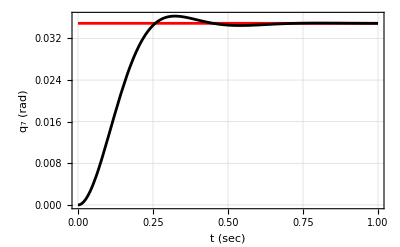

```mathematica
Plot[{Subscript[q, d7][t],Subscript[q, 7][t]/.stepSol[5]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_7 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system displacement response is good.  The desired value is in red. Notice here how the gravity load affects the settling time.  There is more undershoot than for the motors wothout gravity load.

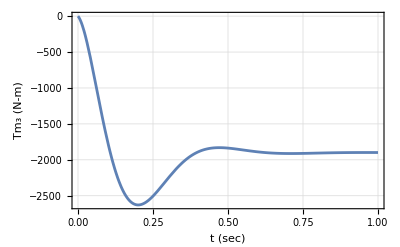

```mathematica
Plot[Subscript[Tm, 3][t]/.stepSol[5],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_3 (N-m)"},PlotRange->All]
```

This is the force needed to do this step maneuver.

Check the tracking of a polynomial.

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
Subscript[q, d7][t_]:=(5 t^2+ 3 t + 1)π/180 (*rad*)
trackSol[5]=NDSolve[{(eqG[5]/.solGains[5]/.tConstRules[5])==0,(eqM[5]/.solGains[5]/.tConstRules[5])==0,Subscript[q, 7]'[Subscript[t, 0]]==0,Subscript[q, 7][Subscript[t, 0]]==0,Subscript[Tm, 3][Subscript[t, 0]]==0},{Subscript[q, 7],Subscript[Tm, 3]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{q_7→InterpolatingFunction[…],Tm_3→InterpolatingFunction[…]}}

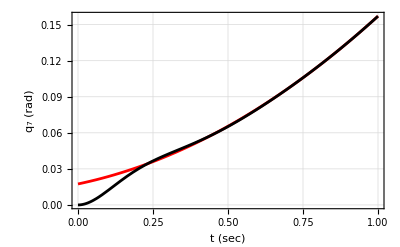

```mathematica
Plot[{Subscript[q, d7][t],Subscript[q, 7][t]/.trackSol[5]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_7 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system tracks a parabola fairly well, could be better initially, however this initial error is due to the step change at t=0.  So if we are nearer to the initial tracking curve, we should be ok.

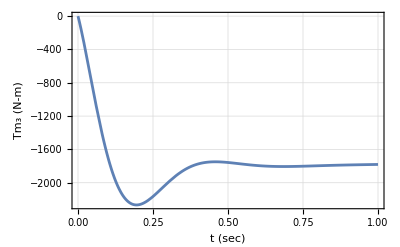

```mathematica
Plot[Subscript[Tm, 3][t]/.trackSol[5],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_3 (N-m)"}, PlotRange->All]
```

Clear the desired variable.

```mathematica
Subscript[q, d7][t_]=.
```

#### Control gains q_8-motor

q_4-motor. Here we fixate all the other movements.

```mathematica
eqG[6]=eqC[6]//.{x[t]-> 0,x'[t]-> 0,x''[t]-> 0,y[t]-> 0,y'[t]-> 0,y''[t]-> 0,Subscript[q, 5][t]->0,Subscript[q, 5]'[t]->0,Subscript[q, 5]''[t]->0,Subscript[q, 6][t]->0,Subscript[q, 6]'[t]->0,Subscript[q, 6]''[t]->0,Subscript[q, 7][t]->0,Subscript[q, 7]'[t]->0,Subscript[q, 7]''[t]->0,Subscript[q, 9][t]->0,Subscript[q, 9]'[t]->0,Subscript[q, 9]''[t]->0,Subscript[q, 10][t]->0,Subscript[q, 10]'[t]->0,Subscript[q, 10]''[t]->0}//.{Subscript[Fm, x][t]-> 0,Subscript[Fm, y][t]-> 0,Subscript[Tm, 1][t]->0,Subscript[Tm, 2][t]->0,Subscript[Tm, 3][t]->0,Subscript[Tm, 5][t]->0,Subscript[Tm, 6][t]->0}//.{Subscript[F, toolx]->0,Subscript[F, tooly]->0,Subscript[F, toolz]->0,Subscript[T, toolx]->0,Subscript[T, tooly]->0,Subscript[T, toolz]->0}
```

0.+729.188 Cos[q_8[t]]+Tm_4[t]-113.586 q_8''[t]-33.7286 (Cos[q_8[t]]^2+Sin[q_8[t]]^2) q_8''[t]

Linearize the equation.

```mathematica
eqL[6]=Normal[Series[eqG[6],{Subscript[q, 8][t],0,1},{Subscript[q, 8]'[t],0,1}]]
```

729.188+Tm_4[t]-147.315 q_8''[t]

We take a derivative to allow substitution of the motor control state equation.

```mathematica
eqLd[6]=D[eqL[6],t]
```

Tm_4'[t]-147.315 q_8^(3)[t]

Solve the motor state equation for the motor force/torque derivative.

```mathematica
solM[6]=Solve[eqM[6]==0,Subscript[Tm, 4]'[t]]//First
```

{Tm_4'[t]→-K_Int[6] q_8[t]+K_Int[6] q_d8[t]-K_prop[6] q_8'[t]+K_prop[6] q_d8'[t]-K_deriv[6] q_8''[t]+K_deriv[6] q_d8''[t]}

Here is the complete linear equation for this motor in terms of the control gains.

```mathematica
eqLf[6]=eqLd[6]//.solM[6]
```

-K_Int[6] q_8[t]+K_Int[6] q_d8[t]-K_prop[6] q_8'[t]+K_prop[6] q_d8'[t]-K_deriv[6] q_8''[t]+K_deriv[6] q_d8''[t]-147.315 q_8^(3)[t]

This is the characteristic polynomial.

```mathematica
charEq[6]=eqLf[6]//.{Derivative[n_][Subscript[q, 8]][t]->s^n,Subscript[q, 8][t]->1,Subscript[q, d8][t]->0,Subscript[q, d8]'[t]->0,Subscript[q, d8]''[t]->0}
```

-147.315 s^3-s^2 K_deriv[6]-K_Int[6]-s K_prop[6]

Put the characteristic equation in standard form.

```mathematica
charEq[6]=charEq[6]/Coefficient[charEq[6],s^3]//Expand
```

1. s^3+0.00678817 s^2 K_deriv[6]+0.00678817 K_Int[6]+0.00678817 s K_prop[6]

The desired characteristic polynomial is given by the following system with a first order pole and a second order pole pair.

```mathematica
charDesired[6]=Expand[(s+Subscript[a, 6])(s^2+ 2 Subscript[ζ, 6] Subscript[ω, n6] s + Subscript[ω, n6]^2)]
```

s^3+s^2 a_6+2 s^2 ζ_6 ω_n6+2 s a_6 ζ_6 ω_n6+s ω_n6^2+a_6 ω_n6^2

The time to peak is defined as

```mathematica
eqTp[6]=Subscript[t, p6]== π/(Subscript[ω, n6] √(1-Subscript[ζ, 6]^2));
```

The two percent settling time is given by

```mathematica
eqTs[6]=Subscript[t, s6]== 4/(Subscript[ζ, 6] Subscript[ω, n6]);
```

```mathematica
solZW[6]=Solve[{eqTp[6],eqTs[6]},{Subscript[ζ, 6],Subscript[ω, n6]}][[2]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{ζ_6→(4 t_p6)/(√(16 t_p6^2+π^2 t_s6^2)),ω_n6→(√(16 t_p6^2+π^2 t_s6^2))/(t_p6 t_s6)}

Set up equations for gains by equating coefficients of the characteristic polynomials.

```mathematica
eqGain1[6]=Coefficient[charEq[6],s^2]==Coefficient[charDesired[6],s^2]/.solZW[6]
```

0.00678817 K_deriv[6]==a_6+8/t_s6

```mathematica
eqGain2[6]=Coefficient[charEq[6],s]==Coefficient[charDesired[6],s]/.solZW[6]
```

0.00678817 K_prop[6]==(8 a_6)/t_s6+(16 t_p6^2+π^2 t_s6^2)/(t_p6^2 t_s6^2)

```mathematica
eqGain3[6]=(charEq[6]/.s->0)==(charDesired[6]/.s->0)/.solZW[6]
```

0.+0.00678817 K_Int[6]==(a_6 (16 t_p6^2+π^2 t_s6^2))/(t_p6^2 t_s6^2)

Solve for the controller gains.

```mathematica
solGains[6]=Solve[{eqGain1[6],eqGain2[6],eqGain3[6]},{Subscript[K, prop][6],Subscript[K, Int][6],Subscript[K, deriv][6]}]//First
```

{K_prop[6]→147.315 ((8. a_6)/t_s6+(1. (16. t_p6^2+9.8696 t_s6^2))/(t_p6^2 t_s6^2)),K_Int[6]→147.315 (0.+(1. a_6 (16. t_p6^2+9.8696 t_s6^2))/(t_p6^2 t_s6^2)),K_deriv[6]→147.315 (1. a_6+8./t_s6)}

Now set the time constants.

```mathematica
tConstRules[6]={Subscript[a, 6]->100,Subscript[t, p6]->1/4,Subscript[t, s6]-> 1/2};
```

Check the step response

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
stepMag=2π/180; (*2 degrees*)
Subscript[q, d8][t_]:=stepMag UnitStep[t]
stepSol[6]=NDSolve[{(eqG[6]/.solGains[6]/.tConstRules[6])==0,(eqM[6]/.solGains[6]/.tConstRules[6])==0,Subscript[q, 8]'[Subscript[t, 0]]==0,Subscript[q, 8][Subscript[t, 0]]==0,Subscript[Tm, 4][Subscript[t, 0]]==0},{Subscript[q, 8],Subscript[Tm, 4]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{q_8→InterpolatingFunction[…],Tm_4→InterpolatingFunction[…]}}

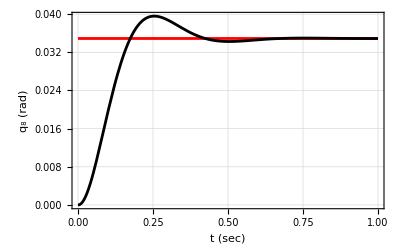

```mathematica
Plot[{Subscript[q, d8][t],Subscript[q, 8][t]/.stepSol[6]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_8 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system displacement response is good.  The desired value is in red.

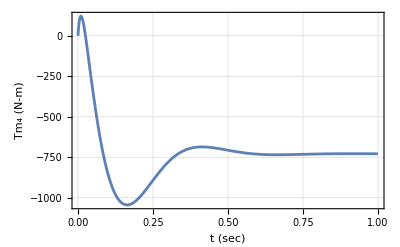

```mathematica
Plot[Subscript[Tm, 4][t]/.stepSol[6],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_4 (N-m)"},PlotRange->All]
```

This is the force needed to do this step maneuver.  It is roughly 200 ft-lb peak torque.

Check the tracking of a polynomial.

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
Subscript[q, d8][t_]:=(5 t^2+ 3 t + 1)π/180 (*rad*)
trackSol[6]=NDSolve[{(eqG[6]/.solGains[6]/.tConstRules[6])==0,(eqM[6]/.solGains[6]/.tConstRules[6])==0,Subscript[q, 8]'[Subscript[t, 0]]==0,Subscript[q, 8][Subscript[t, 0]]==0,Subscript[Tm, 4][Subscript[t, 0]]==0},{Subscript[q, 8],Subscript[Tm, 4]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{q_8→InterpolatingFunction[…],Tm_4→InterpolatingFunction[…]}}

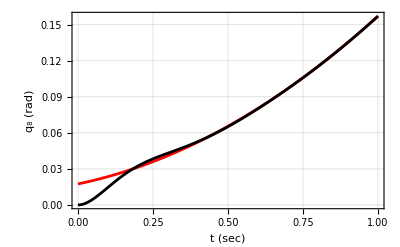

```mathematica
Plot[{Subscript[q, d8][t],Subscript[q, 8][t]/.trackSol[6]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_8 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system tracks a parabola fairly well, could be better initially, however this initial error is due to the step change at t=0.  So if we are nearer to the initial tracking curve, we should be ok.

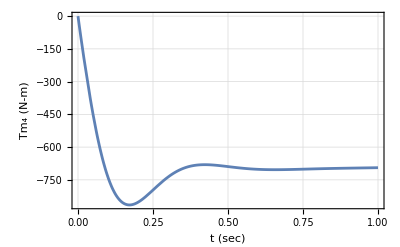

```mathematica
Plot[Subscript[Tm, 4][t]/.trackSol[6],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_4 (N-m)"}, PlotRange->All]
```

Clear the desired variable.

```mathematica
Subscript[q, d8][t_]=.
```

#### Control gains q_9-motor

q_5-motor. Here we fixate all the other movements.

```mathematica
eqG[7]=eqC[7]//.{x[t]-> 0,x'[t]-> 0,x''[t]-> 0,y[t]-> 0,y'[t]-> 0,y''[t]-> 0,Subscript[q, 5][t]->0,Subscript[q, 5]'[t]->0,Subscript[q, 5]''[t]->0,Subscript[q, 6][t]->0,Subscript[q, 6]'[t]->0,Subscript[q, 6]''[t]->0,Subscript[q, 7][t]->0,Subscript[q, 7]'[t]->0,Subscript[q, 7]''[t]->0,Subscript[q, 8][t]->0,Subscript[q, 8]'[t]->0,Subscript[q, 8]''[t]->0,Subscript[q, 10][t]->0,Subscript[q, 10]'[t]->0,Subscript[q, 10]''[t]->0}//.{Subscript[Fm, x][t]-> 0,Subscript[Fm, y][t]-> 0,Subscript[Tm, 1][t]->0,Subscript[Tm, 2][t]->0,Subscript[Tm, 3][t]->0,Subscript[Tm, 4][t]->0,Subscript[Tm, 6][t]->0}//.{Subscript[F, toolx]->0,Subscript[F, tooly]->0,Subscript[F, toolz]->0,Subscript[T, toolx]->0,Subscript[T, tooly]->0,Subscript[T, toolz]->0}
```

0.+46.896 Cos[q_9[t]]+Tm_5[t]+1/3 (0.+135.93 Cos[q_9[t]]-4.61877 q_9''[t])-4.28442 q_9''[t]-0.831379 (Cos[q_9[t]]^2+Sin[q_9[t]]^2) q_9''[t]

Linearize the equation.

```mathematica
eqL[7]=Normal[Series[eqG[7],{Subscript[q, 9][t],0,1},{Subscript[q, 9]'[t],0,1}]]
```

92.2061+Tm_5[t]-6.65539 q_9''[t]

We take a derivative to allow substitution of the motor control state equation.

```mathematica
eqLd[7]=D[eqL[7],t]
```

Tm_5'[t]-6.65539 q_9^(3)[t]

Solve the motor state equation for the motor force/torque derivative.

```mathematica
solM[7]=Solve[eqM[7]==0,Subscript[Tm, 5]'[t]]//First
```

{Tm_5'[t]→-K_Int[7] q_9[t]+K_Int[7] q_d9[t]-K_prop[7] q_9'[t]+K_prop[7] q_d9'[t]-K_deriv[7] q_9''[t]+K_deriv[7] q_d9''[t]}

Here is the complete linear equation for this motor in terms of the control gains.

```mathematica
eqLf[7]=eqLd[7]//.solM[7]
```

-K_Int[7] q_9[t]+K_Int[7] q_d9[t]-K_prop[7] q_9'[t]+K_prop[7] q_d9'[t]-K_deriv[7] q_9''[t]+K_deriv[7] q_d9''[t]-6.65539 q_9^(3)[t]

This is the characteristic polynomial.

```mathematica
charEq[7]=eqLf[7]//.{Derivative[n_][Subscript[q, 9]][t]->s^n,Subscript[q, 9][t]->1,Subscript[q, d9][t]->0,Subscript[q, d9]'[t]->0,Subscript[q, d9]''[t]->0}
```

-6.65539 s^3-s^2 K_deriv[7]-K_Int[7]-s K_prop[7]

Put the characteristic equation in standard form.

```mathematica
charEq[7]=charEq[7]/Coefficient[charEq[7],s^3]//Expand
```

1. s^3+0.150254 s^2 K_deriv[7]+0.150254 K_Int[7]+0.150254 s K_prop[7]

The desired characteristic polynomial is given by the following system with a first order pole and a second order pole pair.

```mathematica
charDesired[7]=Expand[(s+Subscript[a, 7])(s^2+ 2 Subscript[ζ, 7] Subscript[ω, n7] s + Subscript[ω, n7]^2)]
```

s^3+s^2 a_7+2 s^2 ζ_7 ω_n7+2 s a_7 ζ_7 ω_n7+s ω_n7^2+a_7 ω_n7^2

The time to peak is defined as

```mathematica
eqTp[7]=Subscript[t, p7]== π/(Subscript[ω, n7] √(1-Subscript[ζ, 7]^2));
```

The two percent settling time is given by

```mathematica
eqTs[7]=Subscript[t, s7]== 4/(Subscript[ζ, 7] Subscript[ω, n7]);
```

```mathematica
solZW[7]=Solve[{eqTp[7],eqTs[7]},{Subscript[ζ, 7],Subscript[ω, n7]}][[2]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{ζ_7→(4 t_p7)/(√(16 t_p7^2+π^2 t_s7^2)),ω_n7→(√(16 t_p7^2+π^2 t_s7^2))/(t_p7 t_s7)}

Set up equations for gains by equating coefficients of the characterstic polynomials.

```mathematica
eqGain1[7]=Coefficient[charEq[7],s^2]==Coefficient[charDesired[7],s^2]/.solZW[7]
```

0.150254 K_deriv[7]==a_7+8/t_s7

```mathematica
eqGain2[7]=Coefficient[charEq[7],s]==Coefficient[charDesired[7],s]/.solZW[7]
```

0.150254 K_prop[7]==(8 a_7)/t_s7+(16 t_p7^2+π^2 t_s7^2)/(t_p7^2 t_s7^2)

```mathematica
eqGain3[7]=(charEq[7]/.s->0)==(charDesired[7]/.s->0)/.solZW[7]
```

0.+0.150254 K_Int[7]==(a_7 (16 t_p7^2+π^2 t_s7^2))/(t_p7^2 t_s7^2)

Solve for the controller gains.

```mathematica
solGains[7]=Solve[{eqGain1[7],eqGain2[7],eqGain3[7]},{Subscript[K, prop][7],Subscript[K, Int][7],Subscript[K, deriv][7]}]//First
```

{K_prop[7]→6.65539 ((8. a_7)/t_s7+(1. (16. t_p7^2+9.8696 t_s7^2))/(t_p7^2 t_s7^2)),K_Int[7]→6.65539 (0.+(1. a_7 (16. t_p7^2+9.8696 t_s7^2))/(t_p7^2 t_s7^2)),K_deriv[7]→6.65539 (1. a_7+8./t_s7)}

Now set the time constants.  For this smaller system I had to make the first order pole mush faster to decrease overshoot and tracking error.

```mathematica
tConstRules[7]={Subscript[a, 7]->100,Subscript[t, p7]->1/4,Subscript[t, s7]-> 1/2};
```

Check the step response

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
stepMag=2π/180; (*2 degrees*)
Subscript[q, d9][t_]:=stepMag UnitStep[t]
stepSol[7]=NDSolve[{(eqG[7]/.solGains[7]/.tConstRules[7])==0,(eqM[7]/.solGains[7]/.tConstRules[7])==0,Subscript[q, 9]'[Subscript[t, 0]]==0,Subscript[q, 9][Subscript[t, 0]]==0,Subscript[Tm, 5][Subscript[t, 0]]==0},{Subscript[q, 9],Subscript[Tm, 5]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{q_9→InterpolatingFunction[…],Tm_5→InterpolatingFunction[…]}}

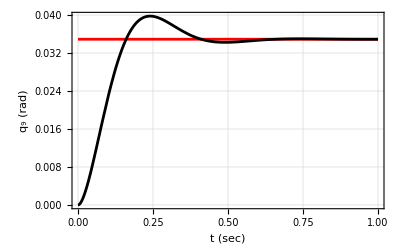

```mathematica
Plot[{Subscript[q, d9][t],Subscript[q, 9][t]/.stepSol[7]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_9 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system displacement response is good.  The desired value is in red.

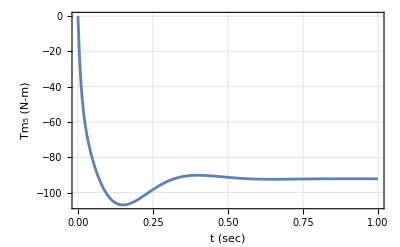

```mathematica
Plot[Subscript[Tm, 5][t]/.stepSol[7],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_5 (N-m)"},PlotRange->All]
```

This is the force needed to do this step maneuver.  It is roughly 4.5 ft-lb peak torque.

Check the tracking of a polynomial.

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
Subscript[q, d9][t_]:=(5 t^2+ 3 t + 1)π/180 (*rad*)
trackSol[7]=NDSolve[{(eqG[7]/.solGains[7]/.tConstRules[7])==0,(eqM[7]/.solGains[7]/.tConstRules[7])==0,Subscript[q, 9]'[Subscript[t, 0]]==0,Subscript[q, 9][Subscript[t, 0]]==0,Subscript[Tm, 5][Subscript[t, 0]]==0},{Subscript[q, 9],Subscript[Tm, 5]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{q_9→InterpolatingFunction[…],Tm_5→InterpolatingFunction[…]}}

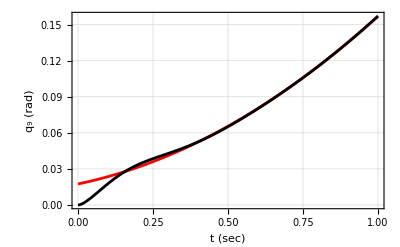

```mathematica
Plot[{Subscript[q, d9][t],Subscript[q, 9][t]/.trackSol[7]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_9 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system tracks a parabola fairly well, could be better initially, however this initial error is due to the step change at t=0.  So if we are nearer to the initial tracking curve, we should be ok.

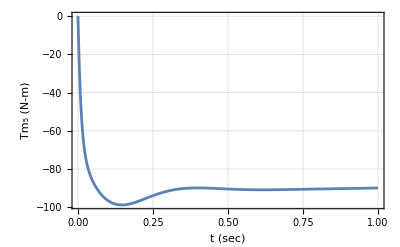

```mathematica
Plot[Subscript[Tm, 5][t]/.trackSol[7],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_5 (N-m)"}, PlotRange->All]
```

Clear the desired variable.

```mathematica
Subscript[q, d9][t_]=.
```

#### Control gains q_10-motor

q_6-motor. Here we fixate all the other movements.

```mathematica
eqG[8]=eqC[8]//.{x[t]-> 0,x'[t]-> 0,x''[t]-> 0,y[t]-> 0,y'[t]-> 0,y''[t]-> 0,Subscript[q, 5][t]->0,Subscript[q, 5]'[t]->0,Subscript[q, 5]''[t]->0,Subscript[q, 6][t]->0,Subscript[q, 6]'[t]->0,Subscript[q, 6]''[t]->0,Subscript[q, 7][t]->0,Subscript[q, 7]'[t]->0,Subscript[q, 7]''[t]->0,Subscript[q, 8][t]->0,Subscript[q, 8]'[t]->0,Subscript[q, 8]''[t]->0,Subscript[q, 9][t]->0,Subscript[q, 9]'[t]->0,Subscript[q, 9]''[t]->0}//.{Subscript[Fm, x][t]-> 0,Subscript[Fm, y][t]-> 0,Subscript[Tm, 1][t]->0,Subscript[Tm, 2][t]->0,Subscript[Tm, 3][t]->0,Subscript[Tm, 4][t]->0,Subscript[Tm, 5][t]->0}//.{Subscript[F, toolx]->0,Subscript[F, tooly]->0,Subscript[F, toolz]->0,Subscript[T, toolx]->0,Subscript[T, tooly]->0,Subscript[T, toolz]->0}
```

0.+Tm_6[t]-0.318349 q_10''[t]

Linearize the equation.

```mathematica
eqL[8]=Normal[Series[eqG[8],{Subscript[q, 10][t],0,1},{Subscript[q, 10]'[t],0,1}]]
```

0.+Tm_6[t]-0.318349 q_10''[t]

We take a derivative to allow substitution of the motor control state equation.

```mathematica
eqLd[8]=D[eqL[8],t]
```

Tm_6'[t]-0.318349 q_10^(3)[t]

Solve the motor state equation for the motor force/torque derivative.

```mathematica
solM[8]=Solve[eqM[8]==0,Subscript[Tm, 6]'[t]]//First
```

{Tm_6'[t]→-K_Int[8] q_10[t]+K_Int[8] q_d10[t]-K_prop[8] q_10'[t]+K_prop[8] q_d10'[t]-K_deriv[8] q_10''[t]+K_deriv[8] q_d10''[t]}

Here is the complete linear equation for this motor in terms of the control gains.

```mathematica
eqLf[8]=eqLd[8]//.solM[8]
```

-K_Int[8] q_10[t]+K_Int[8] q_d10[t]-K_prop[8] q_10'[t]+K_prop[8] q_d10'[t]-K_deriv[8] q_10''[t]+K_deriv[8] q_d10''[t]-0.318349 q_10^(3)[t]

This is the characteristic polynomial.

```mathematica
charEq[8]=eqLf[8]//.{Derivative[n_][Subscript[q, 10]][t]->s^n,Subscript[q, 10][t]->1,Subscript[q, d10][t]->0,Subscript[q, d10]'[t]->0,Subscript[q, d10]''[t]->0}
```

-0.318349 s^3-s^2 K_deriv[8]-K_Int[8]-s K_prop[8]

Put the characteristic equation in standard form.

```mathematica
charEq[8]=charEq[8]/Coefficient[charEq[8],s^3]//Expand
```

1. s^3+3.14121 s^2 K_deriv[8]+3.14121 K_Int[8]+3.14121 s K_prop[8]

The desired characteristic polynomial is given by the following system with a first order pole and a second order pole pair.

```mathematica
charDesired[8]=Expand[(s+Subscript[a, 8])(s^2+ 2 Subscript[ζ, 8] Subscript[ω, n8] s + Subscript[ω, n8]^2)]
```

s^3+s^2 a_8+2 s^2 ζ_8 ω_n8+2 s a_8 ζ_8 ω_n8+s ω_n8^2+a_8 ω_n8^2

The time to peak is defined as

```mathematica
eqTp[8]=Subscript[t, p8]== π/(Subscript[ω, n8] √(1-Subscript[ζ, 8]^2));
```

The two percent settling time is given by

```mathematica
eqTs[8]=Subscript[t, s8]== 4/(Subscript[ζ, 8] Subscript[ω, n8]);
```

```mathematica
solZW[8]=Solve[{eqTp[8],eqTs[8]},{Subscript[ζ, 8],Subscript[ω, n8]}][[2]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{ζ_8→(4 t_p8)/(√(16 t_p8^2+π^2 t_s8^2)),ω_n8→(√(16 t_p8^2+π^2 t_s8^2))/(t_p8 t_s8)}

Set up equations for gains by equating coefficients of the characteristic polynomials.

```mathematica
eqGain1[8]=Coefficient[charEq[8],s^2]==Coefficient[charDesired[8],s^2]/.solZW[8]
```

3.14121 K_deriv[8]==a_8+8/t_s8

```mathematica
eqGain2[8]=Coefficient[charEq[8],s]==Coefficient[charDesired[8],s]/.solZW[8]
```

3.14121 K_prop[8]==(8 a_8)/t_s8+(16 t_p8^2+π^2 t_s8^2)/(t_p8^2 t_s8^2)

```mathematica
eqGain3[8]=(charEq[8]/.s->0)==(charDesired[8]/.s->0)/.solZW[8]
```

0.+3.14121 K_Int[8]==(a_8 (16 t_p8^2+π^2 t_s8^2))/(t_p8^2 t_s8^2)

Solve for the controller gains.

```mathematica
solGains[8]=Solve[{eqGain1[8],eqGain2[8],eqGain3[8]},{Subscript[K, prop][8],Subscript[K, Int][8],Subscript[K, deriv][8]}]//First
```

{K_prop[8]→0.318349 ((8. a_8)/t_s8+(1. (16. t_p8^2+9.8696 t_s8^2))/(t_p8^2 t_s8^2)),K_Int[8]→0.318349 (0.+(1. a_8 (16. t_p8^2+9.8696 t_s8^2))/(t_p8^2 t_s8^2)),K_deriv[8]→0.318349 (1. a_8+8./t_s8)}

Now set the time constants.

```mathematica
tConstRules[8]={Subscript[a, 8]->100,Subscript[t, p8]->1/4,Subscript[t, s8]-> 1/2};
```

Check the step response

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
stepMag=2π/180; (*2 degrees*)
Subscript[q, d10][t_]:=stepMag UnitStep[t]
stepSol[8]=NDSolve[{(eqG[8]/.solGains[8]/.tConstRules[8])==0,(eqM[8]/.solGains[8]/.tConstRules[8])==0,Subscript[q, 10]'[Subscript[t, 0]]==0,Subscript[q, 10][Subscript[t, 0]]==0,Subscript[Tm, 6][Subscript[t, 0]]==0},{Subscript[q, 10],Subscript[Tm, 6]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{q_10→InterpolatingFunction[…],Tm_6→InterpolatingFunction[…]}}

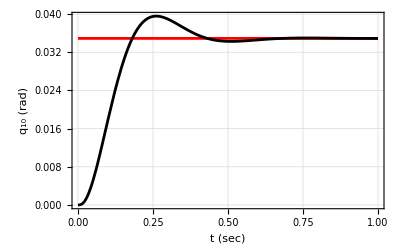

```mathematica
Plot[{Subscript[q, d10][t],Subscript[q, 10][t]/.stepSol[8]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_10 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system displacement response is good.  The desired value is in red.

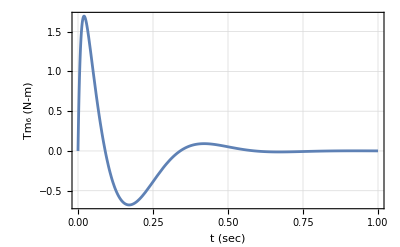

```mathematica
Plot[Subscript[Tm, 6][t]/.stepSol[8],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_6 (N-m)"},PlotRange->All]
```

This is the force needed to do this step maneuver.  It is roughly 1.8 ft-lb peak torque.

Check the tracking of a polynomial.

```mathematica
Subscript[t, 0]=-.00000001;
Subscript[t, f]=1;
Subscript[q, d10][t_]:=(5 t^2+ 3 t + 1)π/180 (*rad*)
trackSol[8]=NDSolve[{(eqG[8]/.solGains[8]/.tConstRules[8])==0,(eqM[8]/.solGains[8]/.tConstRules[8])==0,Subscript[q, 10]'[Subscript[t, 0]]==0,Subscript[q, 10][Subscript[t, 0]]==0,Subscript[Tm, 6][Subscript[t, 0]]==0},{Subscript[q, 10],Subscript[Tm, 6]},{t,Subscript[t, 0],Subscript[t, f]}]
```

{{q_10→InterpolatingFunction[…],Tm_6→InterpolatingFunction[…]}}

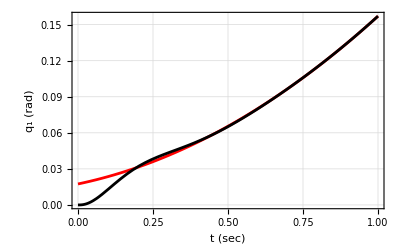

```mathematica
Plot[{Subscript[q, d10][t],Subscript[q, 10][t]/.trackSol[8]},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_1 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

We can see that the system tracks a parabola fairly well, could be better initially, however this initial error is due to the step change at t=0.  So if we are nearer to the initial tracking curve, we should be ok.

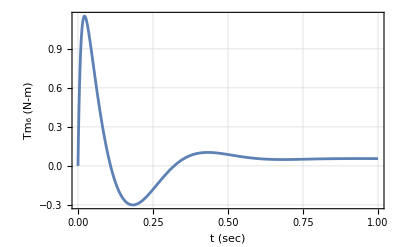

```mathematica
Plot[Subscript[Tm, 6][t]/.trackSol[8],{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_6 (N-m)"}, PlotRange->All]
```

Clear the desired variable.

```mathematica
Subscript[q, d10][t_]=.
```

# Path planning

In this section we will generate a path we want the robot to follow.  We will then pass this information to the robot via desired position and angle coordinates.  Mathematica's interpolation function can be set up where a given interpolation is fit with a sufficiently smooth spline through the desired points.  Each data set for the desired path will consist of a space point and orientation.

#### Path point generator

First we create a function that implements the code from the inverse kinematics section above.  This function has the desired space point (Sp), and tool orientation (Cor) as inputs.  Adjust the (*check reach*) section of this function for your robot.

```mathematica
x[t_]=.
y[t_]=.
Subscript[q, 1][t_]=.
Subscript[q, 2][t_]=.
Subscript[q, 3][t_]=.
Subscript[q, 4][t_]=.
Subscript[q, 5][t_]=.
Subscript[q, 6][t_]=.
Subscript[q, 7][t_]=.
Subscript[q, 8][t_]=.
Subscript[q, 9][t_]=.
Subscript[q, 10][t_]=.
tf=.
```

Unset::norep: Assignment on x for x[t_] not found.

$Failed

Unset::norep: Assignment on y for y[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_1[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_2[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_3[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_4[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_5[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_6[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_7[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_8[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_9[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_10[t_] not found.

$Failed

```mathematica
pathPointGen[{Sp_,Cor_},init_:0]=.
```

Unset::norep: Assignment on pathPointGen for pathPointGen[{Sp_,Cor_},init_:0] not found.

$Failed

```mathematica
pathPointGen[{Sp_,Cor_},init_:0]:=Module[{eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8,eq9,eq10,eq11,eq12,dT1,eqV1,dT2,eqV2,dT3,eqV3,eqR,xbo,ybo,q5o,q6o,q7o,q8o,q9o,q10o,minQXY},

(*check reach*)
If[Sp[[3]]>=Subscript[Z, act]//.{Subscript[Q, 5]-> 0,Subscript[Q, 6]-> -Pi/2,Subscript[Q, 7]-> 0,Subscript[Q, 8]-> 0,Subscript[Q, 9]->0,Subscript[Q, 10]->0},Print["Point ",Sp," is not reachable!"];Abort[]];

(*position*)
eq1=Subscript[X, act]-Sp[[1]];
eq2=Subscript[Y, act]-Sp[[2]];
eq3=Subscript[Z, act]-Sp[[3]];

(*orientation*)
eq4=Subscript[C, act][[1]][[1]]- Cor[[1]][[1]]==0;
eq5=Subscript[C, act][[1]][[2]]- Cor[[1]][[2]]==0;
eq6=Subscript[C, act][[1]][[3]]- Cor[[1]][[3]]==0;

eq7=Subscript[C, act][[2]][[1]]- Cor[[2]][[1]]==0;
eq8=Subscript[C, act][[2]][[2]]- Cor[[2]][[2]]==0;
eq9=Subscript[C, act][[2]][[3]]- Cor[[2]][[3]]==0;

eq10=Subscript[C, act][[3]][[1]]- Cor[[3]][[1]]==0;
eq11=Subscript[C, act][[3]][[2]]- Cor[[3]][[2]]==0;
eq12=Subscript[C, act][[3]][[3]]- Cor[[3]][[3]]==0;

(*tool orientation constraints*)
dT1=Cor[[1]][[1]] n[1]+ Cor[[1]][[2]] n[2] + Cor[[1]][[3]] n[3];
eqV1=1 == (p[1].dT1//TransPtoN)//.{Subscript[q, n_][t]->Subscript[Q, n]};

dT2=Cor[[2]][[1]] n[1]+ Cor[[2]][[2]] n[2] + Cor[[2]][[3]] n[3];
eqV2=1 == (p[2].dT2//TransPtoN)//.{Subscript[q, n_][t]->Subscript[Q, n]};

dT3=Cor[[3]][[1]] n[1]+ Cor[[3]][[2]] n[2] + Cor[[3]][[3]] n[3];
eqV3=1 == (p[3].dT3//TransPtoN)//.{Subscript[q, n_][t]->Subscript[Q, n]};

(*reach sphere*)
eqR=(eq1)^2+(eq2)^2+ (eq3)^2 - (radius - scalePointer pointerLength)^2;

If[init>0,
(*initial estimates*)
minQXY=Minimize[{eqR,eqV1,eqV2,eqV3,- .9Pi ≤ Subscript[Q, 5]≤  .9Pi,- (Pi + Pi/4 )≤ Subscript[Q, 6]≤  Pi/4,- Pi/2 ≤ Subscript[Q, 7]≤  Pi/2,-2 Pi ≤ Subscript[Q, 8]≤ 2 Pi,- .9Pi ≤ Subscript[Q, 9]≤ .9Pi, -2 Pi ≤ Subscript[Q, 10]≤ 2 Pi},{Subscript[Q, 5],Subscript[Q, 6],Subscript[Q, 7],Subscript[Q, 8],Subscript[Q, 9],Subscript[Q, 10],Subscript[X, base],Subscript[Y, base]}];
xbo=Subscript[X, base]/.minQXY[[2]];
ybo=Subscript[Y, base]/.minQXY[[2]];
q5o=Subscript[Q, 5]/.minQXY[[2]];
q6o=Subscript[Q, 6]/.minQXY[[2]];
q7o=Subscript[Q, 7]/.minQXY[[2]];
q8o=Subscript[Q, 8]/.minQXY[[2]];
q9o=Subscript[Q, 9]/.minQXY[[2]];
q10o=Subscript[Q, 10]/.minQXY[[2]];,

(*previous estimates as starting points for current estimate*)
xbo=Subscript[X, base]/.rootQXY;
ybo=Subscript[Y, base]/.rootQXY;
q5o=Subscript[Q, 5]/.rootQXY;
q6o=Subscript[Q, 6]/.rootQXY;
q7o=Subscript[Q, 7]/.rootQXY;
q8o=Subscript[Q, 8]/.rootQXY;
q9o=Subscript[Q, 9]/.rootQXY;
q10o=Subscript[Q, 10]/.rootQXY;];

(*inverse kinematics solution*)
rootQXY=FindRoot[{eq1==0,eq2==0,eq3==0,eqV1,eqV2,eqV3,eq4,eq12},{{Subscript[X, base],xbo},{Subscript[Y, base],ybo},{Subscript[Q, 5],q5o,-.9 Pi,.9Pi},{Subscript[Q, 6],q6o,- (Pi + Pi/4 ),Pi/4},{Subscript[Q, 7],q7o,- Pi/2,Pi/2},{Subscript[Q, 8],q8o,-2 Pi,2Pi},{Subscript[Q, 9],q9o,- .9Pi,.9Pi},{Subscript[Q, 10],q6o,- 2Pi,2Pi}},MaxIterations->10000]
]
```

Here is a test.  With this input the function returns the same results as was last found in the inverse kinematics section above.  It may take a moment to find the solution. Sp={x,y,z} is the order triple.

```mathematica
testPG=pathPointGen[{{1,1,3},Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]]},1]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {X_base,Y_base,Q_5,Q_6,Q_7,Q_8,Q_9,Q_10} = {-1.03952,-1.78199,0.785399,0.743114,-1.03306,-1.22118,0.725727,0.743114}. Try perturbing the initial point(s).

{X_base→-1.03952,Y_base→-1.78199,Q_5→0.785399,Q_6→0.743114,Q_7→-1.03306,Q_8→-1.22118,Q_9→0.725727,Q_10→0.743114}

```mathematica
{Subscript[X, act],Subscript[Y, act],Subscript[Z, act]}//.testPG
Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]]//MatrixForm
Subscript[C, act]//.testPG//Chop//MatrixForm
```

{1.,1.,3.}

(1/2 | 1/2 | 1/(√2)
-1/2 | -1/2 | 1/(√2)
1/(√2) | -1/(√2) | 0)

(0.5 | 0.5 | 0.707106
-0.858981 | 0.182396 | 0.478418
0.110236 | -0.8466 | 0.520689)

Here is what happens if the point is not reachable.

```mathematica
pathPointGen[{{1,1,7.4},Subscript[C, des][Subscript[θ, r],Subscript[θ, p],Subscript[θ, y]]}]
```

Point {1,1,7.4} is not reachable!

$Aborted

#### Path function generation

```mathematica
x[t_]=.
y[t_]=.
Subscript[q, 1][t_]=.
Subscript[q, 2][t_]=.
Subscript[q, 3][t_]=.
Subscript[q, 4][t_]=.
Subscript[q, 5][t_]=.
Subscript[q, 6][t_]=.
Subscript[q, 7][t_]=.
Subscript[q, 8][t_]=.
Subscript[q, 9][t_]=.
Subscript[q, 10][t_]=.
tf=.
```

Unset::norep: Assignment on x for x[t_] not found.

$Failed

Unset::norep: Assignment on y for y[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_1[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_2[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_3[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_4[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_5[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_6[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_7[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_8[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_9[t_] not found.

$Failed

Unset::norep: Assignment on Subscript for q_10[t_] not found.

$Failed

First we will create a list of space points and orientations we want to follow.  This list should be as dense as need (relative to point and orientation spacing) between consecutive points.

For my sample, I will assume I want the tool to stay horizontal through the motion.  I will be pick points on a the y-z plane to move to.  This would be like a painting operation.

Tman is the desired maneuver duration, delT is the maneuver time between path points.

```mathematica
Subscript[T, man]=10;
delT = 0.25;
```

```mathematica
A=1;B=1;Cc=0;ω=2 Pi (1/Subscript[T, man]);
```

Path trace in space

```mathematica
Subscript[X, p][t_]:=4
Subscript[Y, p][t_]:=2(1- Sin[ω t])
Subscript[Z, p][t_]:=2(1- Sin[2ω t])
```

```mathematica
pathPoints=Table[{{Subscript[X, p][t],Subscript[Y, p][t],Subscript[Z, p][t]},{{1,0,0},{0,1,0},{0,0,1}}},{t,0,Subscript[T, man],delT}];
TableForm[pathPoints]
```

4
2.
2. | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
1.68713
1.38197 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
1.38197
0.824429 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
1.09202
0.381966 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
0.824429
0.097887 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
0.585786
0. | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
0.381966
0.097887 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
0.217987
0.381966 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
0.097887
0.824429 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
0.0246233
1.38197 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
0.
2. | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
0.0246233
2.61803 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
0.097887
3.17557 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
0.217987
3.61803 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
0.381966
3.90211 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
0.585786
4. | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
0.824429
3.90211 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
1.09202
3.61803 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
1.38197
3.17557 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
1.68713
2.61803 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
2.
2. | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
2.31287
1.38197 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
2.61803
0.824429 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
2.90798
0.381966 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
3.17557
0.097887 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
3.41421
0. | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
3.61803
0.097887 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
3.78201
0.381966 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
3.90211
0.824429 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
3.97538
1.38197 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
4.
2. | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
3.97538
2.61803 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
3.90211
3.17557 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
3.78201
3.61803 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
3.61803
3.90211 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
3.41421
4. | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
3.17557
3.90211 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
2.90798
3.61803 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
2.61803
3.17557 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
2.31287
2.61803 | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
4
2.
2. | 1 | 0 | 0
0 | 1 | 0
0 | 0 | 1

Initialize the path generator using first point in the path.  The data is in the global variable rootQXY.

```mathematica
pathPointGen[pathPoints[[1]],1]
```

{X_base→-1.69943,Y_base→1.475,Q_5→7.99646×10^-9,Q_6→0.133976,Q_7→-0.260315,Q_8→-0.194227,Q_9→0.320566,Q_10→1.22782×10^-8}

Now apply the inverse solution across all the point and orientation data sets.  The mapping must be sequential because the previous point is used as the current point starting conditions for the inverse kinematics.

```mathematica
pathRules=Map[pathPointGen,pathPoints]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{{X_base→-1.69943,Y_base→1.475,Q_5→9.16906×10^-9,Q_6→0.133976,Q_7→-0.260315,Q_8→-0.194227,Q_9→0.320566,Q_10→1.70004×10^-8},{X_base→-1.71978,Y_base→1.16213,Q_5→-4.57706×10^-9,Q_6→0.253806,Q_7→-0.231919,Q_8→-0.233028,Q_9→0.21114,Q_10→1.419×10^-8},{X_base→-1.68072,Y_base→0.856966,Q_5→-6.87924×10^-9,Q_6→0.349659,Q_7→-0.193311,Q_8→-0.256307,Q_9→0.0999592,Q_10→2.37226×10^-8},{X_base→-1.60965,Y_base→0.567019,Q_5→1.029×10^-8,Q_6→0.41842,Q_7→-0.155024,Q_8→-0.265613,Q_9→0.00221681,Q_10→8.25136×10^-9},{X_base→-1.54395,Y_base→0.299429,Q_5→5.31822×10^-9,Q_6→0.459851,Q_7→-0.127653,Q_8→-0.266971,Q_9→-0.0652268,Q_10→1.03288×10^-8},{X_base→-1.51741,Y_base→0.0607865,Q_5→-6.46945×10^-9,Q_6→0.473801,Q_7→-0.117916,Q_8→-0.266578,Q_9→-0.0893071,Q_10→1.41552×10^-8},{X_base→-1.54399,Y_base→-0.143034,Q_5→1.22445×10^-8,Q_6→0.459755,Q_7→-0.1275,Q_8→-0.266988,Q_9→-0.0652676,Q_10→4.24877×10^-8},{X_base→-1.60996,Y_base→-0.307013,Q_5→5.9355×10^-9,Q_6→0.417738,Q_7→-0.153853,Q_8→-0.265865,Q_9→0.00197985,Q_10→2.28018×10^-8},{X_base→-1.68127,Y_base→-0.427113,Q_5→1.69515×10^-9,Q_6→0.348349,Q_7→-0.19076,Q_8→-0.257329,Q_9→0.099741,Q_10→2.55713×10^-8},{X_base→-1.72015,Y_base→-0.500377,Q_5→3.88308×10^-9,Q_6→0.252589,Q_7→-0.228937,Q_8→-0.235101,Q_9→0.211448,Q_10→3.49494×10^-8},{X_base→-1.69947,Y_base→-0.525,Q_5→-8.48265×10^-9,Q_6→0.133401,Q_7→-0.258289,Q_8→-0.196359,Q_9→0.321247,Q_10→4.75117×10^-9},{X_base→-1.61035,Y_base→-0.500377,Q_5→-7.45799×10^-9,Q_6→-0.00155787,Q_7→-0.27183,Q_8→-0.14452,Q_9→0.417908,Q_10→1.39115×10^-8},{X_base→-1.46557,Y_base→-0.427113,Q_5→-8.8935×10^-9,Q_6→-0.138147,Q_7→-0.269151,Q_8→-0.0891289,Q_9→0.496427,Q_10→-2.99525×10^-8},{X_base→-1.30045,Y_base→-0.307013,Q_5→3.24768×10^-10,Q_6→-0.256926,Q_7→-0.256814,Q_8→-0.0421541,Q_9→0.555894,Q_10→-1.70594×10^-8},{X_base→-1.16718,Y_base→-0.143034,Q_5→7.36794×10^-9,Q_6→-0.337821,Q_7→-0.244523,Q_8→-0.0124271,Q_9→0.594772,Q_10→-1.98335×10^-8},{X_base→-1.11569,Y_base→0.0607865,Q_5→-9.63283×10^-9,Q_6→-0.366381,Q_7→-0.239659,Q_8→-0.00272268,Q_9→0.608763,Q_10→-2.48042×10^-9},{X_base→-1.1673,Y_base→0.29943,Q_5→-7.78129×10^-9,Q_6→-0.338049,Q_7→-0.244378,Q_8→-0.0120074,Q_9→0.594434,Q_10→-1.83081×10^-8},{X_base→-1.30165,Y_base→0.567019,Q_5→6.78709×10^-9,Q_6→-0.25878,Q_7→-0.255718,Q_8→-0.0385621,Q_9→0.55306,Q_10→-1.19778×10^-8},{X_base→-1.46911,Y_base→0.856966,Q_5→-8.64557×10^-9,Q_6→-0.142704,Q_7→-0.266866,Q_8→-0.0795592,Q_9→0.489129,Q_10→-7.66215×10^-9},{X_base→-1.6165,Y_base→1.16213,Q_5→8.58752×10^-9,Q_6→-0.00823136,Q_7→-0.269425,Q_8→-0.128919,Q_9→0.406575,Q_10→-1.01151×10^-8},{X_base→-1.70709,Y_base→1.475,Q_5→8.23826×10^-9,Q_6→0.126166,Q_7→-0.256973,Q_8→-0.17739,Q_9→0.308196,Q_10→-1.59535×10^-8},{X_base→-1.72792,Y_base→1.78787,Q_5→6.76069×10^-9,Q_6→0.24574,Q_7→-0.22863,Q_8→-0.215858,Q_9→0.198748,Q_10→1.0811×10^-8},{X_base→-1.68865,Y_base→2.09303,Q_5→-1.80431×10^-8,Q_6→0.341708,Q_7→-0.190283,Q_8→-0.239466,Q_9→0.0880417,Q_10→5.57942×10^-8},{X_base→-1.61699,Y_base→2.38298,Q_5→-1.04404×10^-8,Q_6→0.410826,Q_7→-0.15235,Q_8→-0.24947,Q_9→-0.00900663,Q_10→9.13009×10^-9},{X_base→-1.55073,Y_base→2.65057,Q_5→-4.64916×10^-9,Q_6→0.452624,Q_7→-0.125277,Q_8→-0.251487,Q_9→-0.07586,Q_10→8.86183×10^-9},{X_base→-1.52396,Y_base→2.88921,Q_5→7.00888×10^-9,Q_6→0.466727,Q_7→-0.115655,Q_8→-0.25136,Q_9→-0.0997112,Q_10→2.56227×10^-8},{X_base→-1.55077,Y_base→3.09303,Q_5→-5.00448×10^-9,Q_6→0.452529,Q_7→-0.125124,Q_8→-0.251505,Q_9→-0.0759004,Q_10→1.47283×10^-8},{X_base→-1.61729,Y_base→3.25701,Q_5→9.58287×10^-9,Q_6→0.410146,Q_7→-0.151181,Q_8→-0.249722,Q_9→-0.00924308,Q_10→1.45418×10^-8},{X_base→-1.6892,Y_base→3.37711,Q_5→-6.53553×10^-9,Q_6→0.340393,Q_7→-0.187732,Q_8→-0.240474,Q_9→0.0878133,Q_10→2.41368×10^-8},{X_base→-1.72832,Y_base→3.45038,Q_5→-1.36476×10^-9,Q_6→0.244501,Q_7→-0.225639,Q_8→-0.21788,Q_9→0.199018,Q_10→1.25307×10^-8},{X_base→-1.70718,Y_base→3.475,Q_5→-3.99301×10^-9,Q_6→0.125546,Q_7→-0.254928,Q_8→-0.17942,Q_9→0.308803,Q_10→7.53859×10^-9},{X_base→-1.6169,Y_base→3.45038,Q_5→-6.71352×10^-9,Q_6→-0.00880533,Q_7→-0.268673,Q_8→-0.128612,Q_9→0.406091,Q_10→1.41315×10^-8},{X_base→-1.47054,Y_base→3.37711,Q_5→7.45071×10^-9,Q_6→-0.144522,Q_7→-0.266442,Q_8→-0.0748325,Q_9→0.485796,Q_10→-1.01815×10^-8},{X_base→-1.30397,Y_base→3.25701,Q_5→-3.19441×10^-10,Q_6→-0.262379,Q_7→-0.254655,Q_8→-0.0296124,Q_9→0.546647,Q_10→-1.37512×10^-7},{X_base→-1.16977,Y_base→3.09303,Q_5→1.87649×10^-9,Q_6→-0.342581,Q_7→-0.242803,Q_8→-0.00121377,Q_9→0.586598,Q_10→-1.57381×10^-8},{X_base→-1.11798,Y_base→2.88921,Q_5→1.00192×10^-9,Q_6→-0.37089,Q_7→-0.238099,Q_8→0.00800822,Q_9→0.600981,Q_10→-1.82094×10^-8},{X_base→-1.16989,Y_base→2.65057,Q_5→1.41216×10^-10,Q_6→-0.342802,Q_7→-0.242664,Q_8→-0.000805103,Q_9→0.586271,Q_10→-2.19004×10^-8},{X_base→-1.30507,Y_base→2.38298,Q_5→1.05418×10^-8,Q_6→-0.264187,Q_7→-0.253602,Q_8→-0.0261006,Q_9→0.54389,Q_10→-9.74669×10^-9},{X_base→-1.4738,Y_base→2.09303,Q_5→-6.27743×10^-9,Q_6→-0.148994,Q_7→-0.264236,Q_8→-0.0654219,Q_9→0.478651,Q_10→-5.78389×10^-9},{X_base→-1.62261,Y_base→1.78787,Q_5→-8.091×10^-9,Q_6→-0.0153908,Q_7→-0.26635,Q_8→-0.113181,Q_9→0.394922,Q_10→-1.65706×10^-8},{X_base→-1.71432,Y_base→1.475,Q_5→6.71854×10^-10,Q_6→0.118376,Q_7→-0.253674,Q_8→-0.160573,Q_9→0.29587,Q_10→-1.64009×10^-8}}

This function converts the replacement relations to just numbers representing the respective variable.

```mathematica
pathVarFun[x_]:={Subscript[X, base],Subscript[Y, base],Subscript[Q, 5],Subscript[Q, 6],Subscript[Q, 7],Subscript[Q, 8],Subscript[Q, 9],Subscript[Q, 10]}/.x
```

Each row of this corresponds to the variables X, Y, ..., respectively.

```mathematica
pathVar=Transpose[Map[pathVarFun,pathRules]];MatrixForm[pathVar]
```

(-1.69943 | -1.71978 | -1.68072 | -1.60965 | -1.54395 | -1.51741 | -1.54399 | -1.60996 | -1.68127 | -1.72015 | -1.69947 | -1.61035 | -1.46557 | -1.30045 | -1.16718 | -1.11569 | -1.1673 | -1.30165 | -1.46911 | -1.6165 | -1.70709 | -1.72792 | -1.68865 | -1.61699 | -1.55073 | -1.52396 | -1.55077 | -1.61729 | -1.6892 | -1.72832 | -1.70718 | -1.6169 | -1.47054 | -1.30397 | -1.16977 | -1.11798 | -1.16989 | -1.30507 | -1.4738 | -1.62261 | -1.71432
1.475 | 1.16213 | 0.856966 | 0.567019 | 0.299429 | 0.0607865 | -0.143034 | -0.307013 | -0.427113 | -0.500377 | -0.525 | -0.500377 | -0.427113 | -0.307013 | -0.143034 | 0.0607865 | 0.29943 | 0.567019 | 0.856966 | 1.16213 | 1.475 | 1.78787 | 2.09303 | 2.38298 | 2.65057 | 2.88921 | 3.09303 | 3.25701 | 3.37711 | 3.45038 | 3.475 | 3.45038 | 3.37711 | 3.25701 | 3.09303 | 2.88921 | 2.65057 | 2.38298 | 2.09303 | 1.78787 | 1.475
9.16906×10^-9 | -4.57706×10^-9 | -6.87924×10^-9 | 1.029×10^-8 | 5.31822×10^-9 | -6.46945×10^-9 | 1.22445×10^-8 | 5.9355×10^-9 | 1.69515×10^-9 | 3.88308×10^-9 | -8.48265×10^-9 | -7.45799×10^-9 | -8.8935×10^-9 | 3.24768×10^-10 | 7.36794×10^-9 | -9.63283×10^-9 | -7.78129×10^-9 | 6.78709×10^-9 | -8.64557×10^-9 | 8.58752×10^-9 | 8.23826×10^-9 | 6.76069×10^-9 | -1.80431×10^-8 | -1.04404×10^-8 | -4.64916×10^-9 | 7.00888×10^-9 | -5.00448×10^-9 | 9.58287×10^-9 | -6.53553×10^-9 | -1.36476×10^-9 | -3.99301×10^-9 | -6.71352×10^-9 | 7.45071×10^-9 | -3.19441×10^-10 | 1.87649×10^-9 | 1.00192×10^-9 | 1.41216×10^-10 | 1.05418×10^-8 | -6.27743×10^-9 | -8.091×10^-9 | 6.71854×10^-10
0.133976 | 0.253806 | 0.349659 | 0.41842 | 0.459851 | 0.473801 | 0.459755 | 0.417738 | 0.348349 | 0.252589 | 0.133401 | -0.00155787 | -0.138147 | -0.256926 | -0.337821 | -0.366381 | -0.338049 | -0.25878 | -0.142704 | -0.00823136 | 0.126166 | 0.24574 | 0.341708 | 0.410826 | 0.452624 | 0.466727 | 0.452529 | 0.410146 | 0.340393 | 0.244501 | 0.125546 | -0.00880533 | -0.144522 | -0.262379 | -0.342581 | -0.37089 | -0.342802 | -0.264187 | -0.148994 | -0.0153908 | 0.118376
-0.260315 | -0.231919 | -0.193311 | -0.155024 | -0.127653 | -0.117916 | -0.1275 | -0.153853 | -0.19076 | -0.228937 | -0.258289 | -0.27183 | -0.269151 | -0.256814 | -0.244523 | -0.239659 | -0.244378 | -0.255718 | -0.266866 | -0.269425 | -0.256973 | -0.22863 | -0.190283 | -0.15235 | -0.125277 | -0.115655 | -0.125124 | -0.151181 | -0.187732 | -0.225639 | -0.254928 | -0.268673 | -0.266442 | -0.254655 | -0.242803 | -0.238099 | -0.242664 | -0.253602 | -0.264236 | -0.26635 | -0.253674
-0.194227 | -0.233028 | -0.256307 | -0.265613 | -0.266971 | -0.266578 | -0.266988 | -0.265865 | -0.257329 | -0.235101 | -0.196359 | -0.14452 | -0.0891289 | -0.0421541 | -0.0124271 | -0.00272268 | -0.0120074 | -0.0385621 | -0.0795592 | -0.128919 | -0.17739 | -0.215858 | -0.239466 | -0.24947 | -0.251487 | -0.25136 | -0.251505 | -0.249722 | -0.240474 | -0.21788 | -0.17942 | -0.128612 | -0.0748325 | -0.0296124 | -0.00121377 | 0.00800822 | -0.000805103 | -0.0261006 | -0.0654219 | -0.113181 | -0.160573
0.320566 | 0.21114 | 0.0999592 | 0.00221681 | -0.0652268 | -0.0893071 | -0.0652676 | 0.00197985 | 0.099741 | 0.211448 | 0.321247 | 0.417908 | 0.496427 | 0.555894 | 0.594772 | 0.608763 | 0.594434 | 0.55306 | 0.489129 | 0.406575 | 0.308196 | 0.198748 | 0.0880417 | -0.00900663 | -0.07586 | -0.0997112 | -0.0759004 | -0.00924308 | 0.0878133 | 0.199018 | 0.308803 | 0.406091 | 0.485796 | 0.546647 | 0.586598 | 0.600981 | 0.586271 | 0.54389 | 0.478651 | 0.394922 | 0.29587
1.70004×10^-8 | 1.419×10^-8 | 2.37226×10^-8 | 8.25136×10^-9 | 1.03288×10^-8 | 1.41552×10^-8 | 4.24877×10^-8 | 2.28018×10^-8 | 2.55713×10^-8 | 3.49494×10^-8 | 4.75117×10^-9 | 1.39115×10^-8 | -2.99525×10^-8 | -1.70594×10^-8 | -1.98335×10^-8 | -2.48042×10^-9 | -1.83081×10^-8 | -1.19778×10^-8 | -7.66215×10^-9 | -1.01151×10^-8 | -1.59535×10^-8 | 1.0811×10^-8 | 5.57942×10^-8 | 9.13009×10^-9 | 8.86183×10^-9 | 2.56227×10^-8 | 1.47283×10^-8 | 1.45418×10^-8 | 2.41368×10^-8 | 1.25307×10^-8 | 7.53859×10^-9 | 1.41315×10^-8 | -1.01815×10^-8 | -1.37512×10^-7 | -1.57381×10^-8 | -1.82094×10^-8 | -2.19004×10^-8 | -9.74669×10^-9 | -5.78389×10^-9 | -1.65706×10^-8 | -1.64009×10^-8)

Now create interpolation functions to feed to the control algorithm.

#### x desired

```mathematica
Subscript[T, L]=Table[(i-1)Subscript[T, man]/(Length[pathVar[[1]]]-1),{i,1,Length[pathVar[[1]]]}]
```

{0,1/4,1/2,3/4,1,5/4,3/2,7/4,2,9/4,5/2,11/4,3,13/4,7/2,15/4,4,17/4,9/2,19/4,5,21/4,11/2,23/4,6,25/4,13/2,27/4,7,29/4,15/2,31/4,8,33/4,17/2,35/4,9,37/4,19/2,39/4,10}

Change the order to make the following plots fairly smooth.

```mathematica
Subscript[x, d][t_]=Interpolation[Transpose[{Subscript[T, L],pathVar[[1]]}],InterpolationOrder->5][t]
```

InterpolatingFunction[…][t]

Check the coordinate and the derivatives out to acceleration for smoothness.

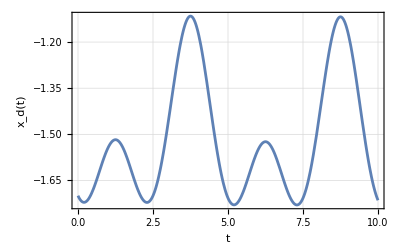

```mathematica
Plot[Subscript[x, d][t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","x_d(t)"},Frame->True,GridLines-> Automatic]
```

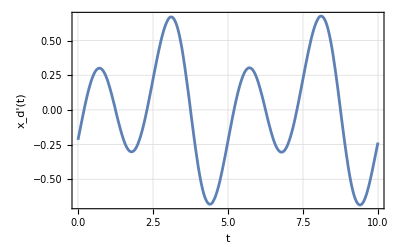

```mathematica
Plot[Subscript[x, d]'[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","x_d'(t)"},Frame->True,GridLines-> Automatic]
```

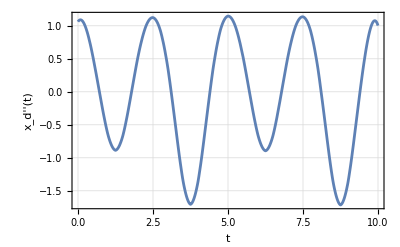

```mathematica
Plot[Subscript[x, d]''[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","x_d''(t)"},Frame->True,GridLines-> Automatic]
```

#### y desired

Change the order to make the following plots fairly smooth.

```mathematica
Subscript[y, d][t_]=Interpolation[Transpose[{Subscript[T, L],pathVar[[2]]}],InterpolationOrder->5][t]
```

InterpolatingFunction[…][t]

Check the coordinate and the derivatives out to acceleration for smoothness.

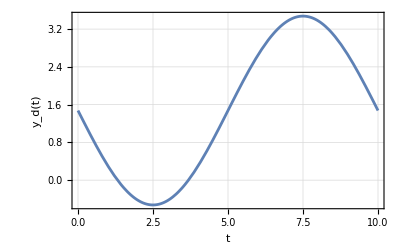

```mathematica
Plot[Subscript[y, d][t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","y_d(t)"},Frame->True,GridLines-> Automatic]
```

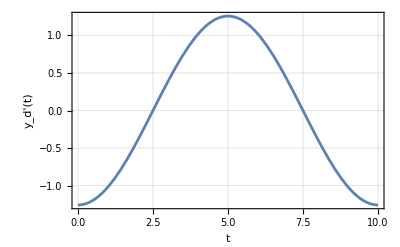

```mathematica
Plot[Subscript[y, d]'[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","y_d'(t)"},Frame->True,GridLines-> Automatic]
```

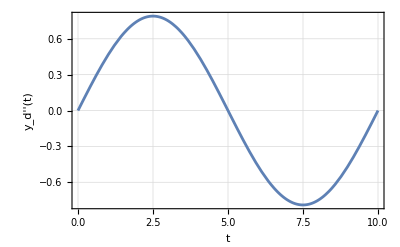

```mathematica
Plot[Subscript[y, d]''[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","y_d''(t)"},Frame->True,GridLines-> Automatic]
```

#### q_5 desired

Change the order to make the following plots fairly smooth.

```mathematica
Subscript[q, d5][t_]=Interpolation[Transpose[{Subscript[T, L],pathVar[[3]]}],InterpolationOrder->5][t]
```

InterpolatingFunction[…][t]

Check the coordinate and the derivatives out to acceleration for smoothness.

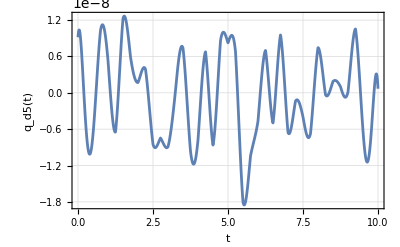

```mathematica
Plot[Subscript[q, d5][t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d5(t)"},Frame->True,GridLines-> Automatic]
```

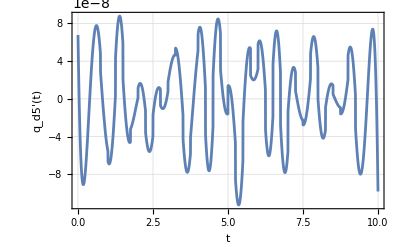

```mathematica
Plot[Subscript[q, d5]'[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d5'(t)"},Frame->True,GridLines-> Automatic]
```

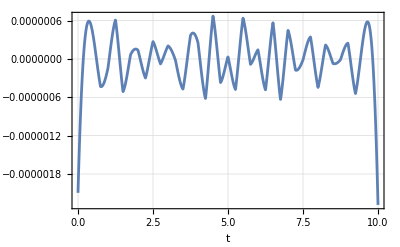

```mathematica
Plot[Subscript[q, d5]''[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d5''(t)"},Frame->True,GridLines-> Automatic]
```

#### q_6 desired

Change the order to make the following plots fairly smooth.

```mathematica
Subscript[q, d6][t_]=Interpolation[Transpose[{Subscript[T, L],pathVar[[4]]}],InterpolationOrder->5][t]
```

InterpolatingFunction[…][t]

Check the coordinate and the derivatives out to acceleration for smoothness.

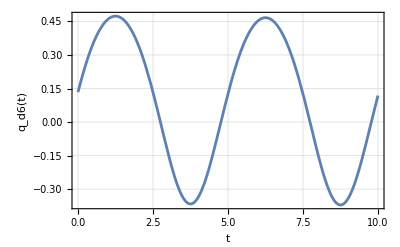

```mathematica
Plot[Subscript[q, d6][t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d6(t)"},Frame->True,GridLines-> Automatic]
```

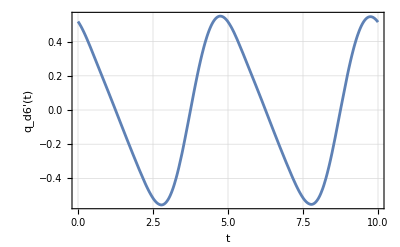

```mathematica
Plot[Subscript[q, d6]'[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d6'(t)"},Frame->True,GridLines-> Automatic]
```

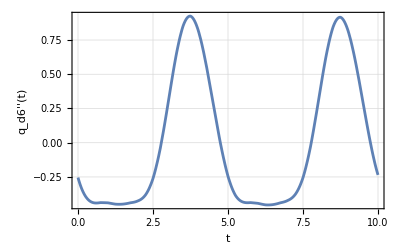

```mathematica
Plot[Subscript[q, d6]''[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d6''(t)"},Frame->True,GridLines-> Automatic]
```

#### q_7 desired

Change the order to make the following plots fairly smooth.

```mathematica
Subscript[q, d7][t_]=Interpolation[Transpose[{Subscript[T, L],pathVar[[5]]}],InterpolationOrder->5][t]
```

InterpolatingFunction[…][t]

Check the coordinate and the derivatives out to acceleration for smoothness.

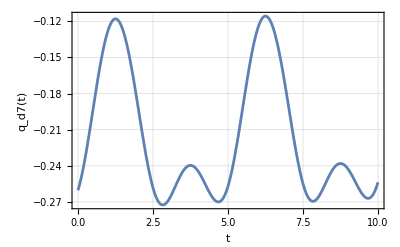

```mathematica
Plot[Subscript[q, d7][t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d7(t)"},Frame->True,GridLines-> Automatic]
```

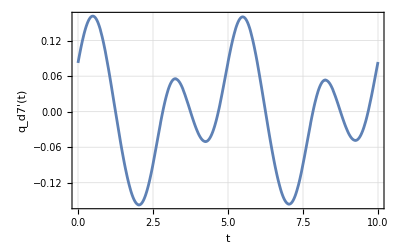

```mathematica
Plot[Subscript[q, d7]'[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d7'(t)"},Frame->True,GridLines-> Automatic]
```

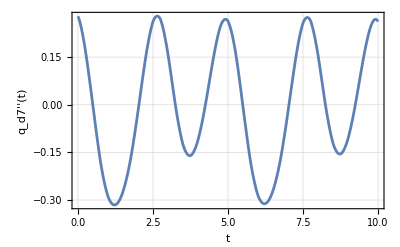

```mathematica
Plot[Subscript[q, d7]''[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d7''(t)"},Frame->True,GridLines-> Automatic]
```

#### q_8 desired

Change the order to make the following plots fairly smooth.

```mathematica
Subscript[q, d8][t_]=Interpolation[Transpose[{Subscript[T, L],pathVar[[6]]}],InterpolationOrder->5][t]
```

InterpolatingFunction[…][t]

Check the coordinate and the derivatives out to acceleration for smoothness.

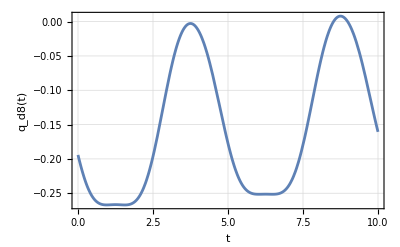

```mathematica
Plot[Subscript[q, d8][t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d8(t)"},Frame->True,GridLines-> Automatic]
```

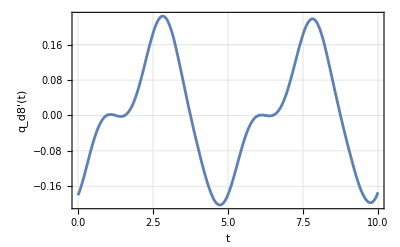

```mathematica
Plot[Subscript[q, d8]'[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d8'(t)"},Frame->True,GridLines-> Automatic]
```

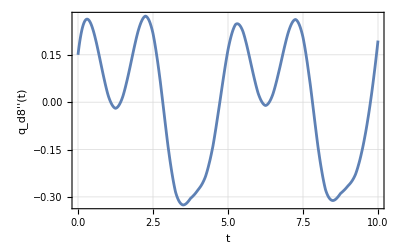

```mathematica
Plot[Subscript[q, d8]''[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d8''(t)"},Frame->True,GridLines-> Automatic]
```

#### q_9 desired

Change the order to make the following plots fairly smooth.

```mathematica
Subscript[q, d9][t_]=Interpolation[Transpose[{Subscript[T, L],pathVar[[7]]}],InterpolationOrder->5][t]
```

InterpolatingFunction[…][t]

Check the coordinate and the derivatives out to acceleration for smoothness.

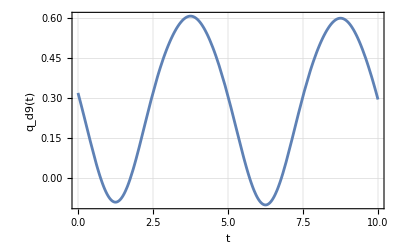

```mathematica
Plot[Subscript[q, d9][t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d9(t)"},Frame->True,GridLines-> Automatic]
```

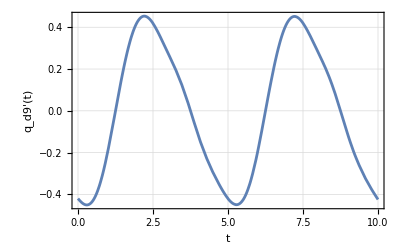

```mathematica
Plot[Subscript[q, d9]'[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d9'(t)"},Frame->True,GridLines-> Automatic]
```

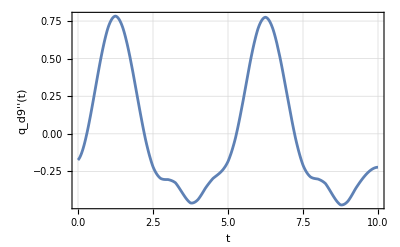

```mathematica
Plot[Subscript[q, d9]''[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d9''(t)"},Frame->True,GridLines-> Automatic]
```

#### q_10 desired

Change the order to make the following plots fairly smooth.

```mathematica
Subscript[q, d10][t_]=Interpolation[Transpose[{Subscript[T, L],pathVar[[8]]}],InterpolationOrder->5][t]
```

InterpolatingFunction[…][t]

Check the coordinate and the derivatives out to acceleration for smoothness.

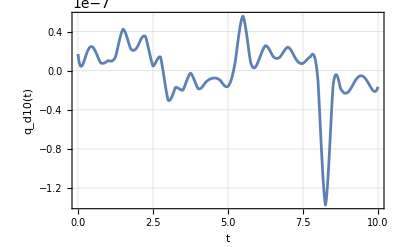

```mathematica
Plot[Subscript[q, d10][t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d10(t)"},Frame->True,GridLines-> Automatic]
```

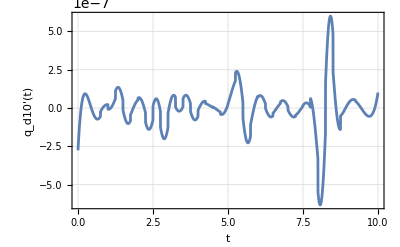

```mathematica
Plot[Subscript[q, d10]'[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d10'(t)"},Frame->True,GridLines-> Automatic]
```

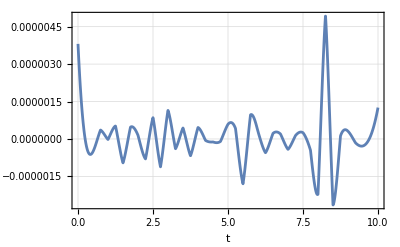

```mathematica
Plot[Subscript[q, d10]''[t],{t,0,Subscript[T, man]},PlotRange-> All,FrameLabel-> {"t","q_d10''(t)"},Frame->True,GridLines-> Automatic]
```

#### Path Planned Kinematics Animation

Here we create a simple path plan to get form the rest position to the desired position.

```mathematica
x[t_]=Subscript[x, d][t];
y[t_]=Subscript[y, d][t];
Subscript[q, 1][t_]=Subscript[q, d1][t];
Subscript[q, 2][t_]=Subscript[q, d2][t];
Subscript[q, 3][t_]=Subscript[q, d3][t];
Subscript[q, 4][t_]=Subscript[q, d4][t];
Subscript[q, 5][t_]=Subscript[q, d5][t];
Subscript[q, 6][t_]=Subscript[q, d6][t];
Subscript[q, 7][t_]=Subscript[q, d7][t];
Subscript[q, 8][t_]=Subscript[q, d8][t];
Subscript[q, 9][t_]=Subscript[q, d9][t];
Subscript[q, 10][t_]=Subscript[q, d10][t];
```

Create composite graphic out of parts that have been rotated and translated

```mathematica
pathPlot=ParametricPlot3D[{Subscript[X, p][t],Subscript[Y, p][t],Subscript[Z, p][t]},{t,0,Subscript[T, man]},ViewPoint->{1,-1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-scale,scale},{-scale,scale},{0,scale}},AspectRatio->1,AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

```mathematica
robotGraphicPathKinAnim={

(*Path point*)
Point[{Subscript[X, p][t],Subscript[Y, p][t],Subscript[Z, p][t]}],

(*Base graphic*)
Translate[GeometricTransformation[baseGraphic,Transpose[rotA]],{xAo,yAo,zAo}],
(*Wheel graphic*)
Translate[GeometricTransformation[wheelGraphic1,Transpose[rotA]],{xBo,yBo,zBo}],
Translate[GeometricTransformation[wheelGraphic2,Transpose[rotA]],{xCo,yCo,zCo}],
Translate[GeometricTransformation[wheelGraphic3,Transpose[rotA]],{xDo,yDo,zDo}],
Translate[GeometricTransformation[wheelGraphic4,Transpose[rotA]],{xEo,yEo,zEo}],
(*rotor*)
Translate[GeometricTransformation[rotatorGraphic,Transpose[rotF]],{xFo,yFo,zFo}],

(*joint 1*)
Translate[GeometricTransformation[jointGraphic1,Transpose[rotG]],{xGo,yGo,zGo}],

(*Arm1 graphic*)
Translate[GeometricTransformation[arm1baseGraphic,Transpose[rotH]],{xHo,yHo,zHo}],

(*Arm2 graphic*)
Translate[GeometricTransformation[arm2baseGraphic,Transpose[rotL]],{xLo,yLo,zLo}],

(*Arm3 graphic*)
Translate[GeometricTransformation[arm3baseGraphic,Transpose[rotS]],{xSo,ySo,zSo}],

(*Wrist1 graphic*)
Translate[GeometricTransformation[wristGraphic1,Transpose[rotM]],{xMo,yMo,zMo}],

(*Wrist2 graphic*)
Translate[GeometricTransformation[wristGraphic2,Transpose[rotP]],{xPo,yPo,zPo}],

};
```

```mathematica
robotGraphicPathKinAnimT[t_]=robotGraphicPathKinAnim;
```

Loop over time

```mathematica
Animate[Show[pathPlot,Graphics3D[robotGraphicPathKinAnimT[t],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-scale,scale},{-scale,scale},{-scale,scale}},AspectRatio->1,AxesLabel->{"X","Y","Z"}]],{t,0,Subscript[T, man],delT},AnimationRunning->False]
```

# Path planned dynamic simulation

Now we see how the robot works under control following the chosen path.

Clear the variables after each simulation and animation test.

```mathematica
x[t_]=.
y[t_]=.
Subscript[q, 1][t_]=.
Subscript[q, 2][t_]=.
Subscript[q, 3][t_]=.
Subscript[q, 4][t_]=.
Subscript[q, 5][t_]=.
Subscript[q, 6][t_]=.
Subscript[q, 7][t_]=.
Subscript[q, 8][t_]=.
Subscript[q, 9][t_]=.
Subscript[q, 10][t_]=.
tf=.
```

Tool loads, set to zero for this example.

```mathematica
Subscript[F, toolx]=0;
Subscript[F, tooly]=0;
Subscript[F, toolz]=0;
Subscript[T, toolx]=0;
Subscript[T, tooly]=0;
Subscript[T, toolz]=0;
```

Assign control gains found above.  Take note that these may be unreasonably high and must be factor into any overall design...can the amplifiers/motors needed be reasonably built.  If not trade-offs on size and speed are needed.

```mathematica
For[i=1,i≤ Subscript[N, dof],i++,Subscript[K, prop][i]=Subscript[K, prop][i]/.solGains[i]/.tConstRules[i];Subscript[K, Int][i]=Subscript[K, Int][i]/.solGains[i]/.tConstRules[i];Subscript[K, deriv][i]=Subscript[K, deriv][i]/.solGains[i]/.tConstRules[i];Print["K_prop[",i,"]=",Subscript[K, prop][i],", K_Int[",i,"]=",Subscript[K, Int][i],", K_deriv[",i,"]=",Subscript[K, deriv][i]]]
```

K_prop[1]=2.26184×10^6, K_Int[1]=2.75498×10^7, K_deriv[1]=144010.

K_prop[2]=2.26184×10^6, K_Int[2]=2.75498×10^7, K_deriv[2]=144010.

K_prop[3]=3.07779×10^6, K_Int[3]=3.74882×10^7, K_deriv[3]=195961.

K_prop[4]=629792., K_Int[4]=3.65945×10^6, K_deriv[4]=42875.1

K_prop[5]=210458., K_Int[5]=2219.14/(0.00181468-0.00181468 InterpolatingFunction[…][t]), K_deriv[5]=14327.6

K_prop[6]=268395., K_Int[6]=3.26912×10^6, K_deriv[6]=17088.5

K_prop[7]=12125.5, K_Int[7]=147692., K_deriv[7]=772.025

K_prop[8]=580.004, K_Int[8]=7064.59, K_deriv[8]=36.9284

Simulate the system with the planned path.  This may take a while.

```mathematica
Subscript[t, 0]=0;
Subscript[t, f]=Subscript[T, man];
g=9.81;solPathDyn=Monitor[NDSolve[{eqC[1]==0,eqC[2]==0,eqC[3]==0,eqC[4]==0,eqC[5]==0,eqC[6]==0,eqC[7]==0,eqC[8]==0,eqM[1]==0,eqM[2]==0,eqM[3]==0,eqM[4]==0,eqM[5]==0,eqM[6]==0,eqM[7]==0,eqM[8]==0,x''[0]==Subscript[x, d]''[0],x'[0]==Subscript[x, d]'[0],x[0]==Subscript[x, d][0],y''[0]==Subscript[y, d]''[0],y'[0]==Subscript[y, d]'[0],y[0]==Subscript[y, d][0],Subscript[q, 5]''[0]==Subscript[q, d5]''[0],Subscript[q, 5]'[0]==Subscript[q, d5]'[0],Subscript[q, 5][0]==Subscript[q, d5][0],Subscript[q, 6]''[0]==Subscript[q, d6]''[0],Subscript[q, 6]'[0]==Subscript[q, d6]'[0],Subscript[q, 6][0]==Subscript[q, d6][0],Subscript[q, 7]''[0]==Subscript[q, d7]''[0],Subscript[q, 7]'[0]==Subscript[q, d7]'[0],Subscript[q, 7][0]==Subscript[q, d7][0],Subscript[q, 8]''[0]==Subscript[q, d8]''[0],Subscript[q, 8]'[0]==Subscript[q, d8]'[0],Subscript[q, 8][0]==Subscript[q, d8][0],Subscript[q, 9]''[0]==Subscript[q, d9]''[0],Subscript[q, 9]'[0]==Subscript[q, d9]'[0],Subscript[q, 9][0]==Subscript[q, d9][0],Subscript[q, 10]''[0]==Subscript[q, d10]''[0],Subscript[q, 10]'[0]==Subscript[q, d10]'[0],Subscript[q, 10][0]==Subscript[q, d10][0],Subscript[Fm, x][0]==0,Subscript[Fm, y][0]==0,Subscript[Tm, 1][0]==0,Subscript[Tm, 2][0]==0,Subscript[Tm, 3][0]==0,Subscript[Tm, 4][0]==0,Subscript[Tm, 5][0]==0,Subscript[Tm, 6][0]==0},{x,y,Subscript[q, 5],Subscript[q, 6],Subscript[q, 7],Subscript[q, 8],Subscript[q, 9],Subscript[q, 10],Subscript[Fm, x],Subscript[Fm, y],Subscript[Tm, 1],Subscript[Tm, 2],Subscript[Tm, 3],Subscript[Tm, 4],Subscript[Tm, 5],Subscript[Tm, 6]},{t,Subscript[t, 0],Subscript[t, f]},StepMonitor:>(time=t;),MaxSteps->50000,Method->{"EquationSimplification"->"Residual"}],ProgressIndicator[time,{Subscript[t, 0],Subscript[t, f]}]]//First
```

NDSolve::ivres: NDSolve has computed initial values that give a zero residual for the differential-algebraic system, but some components are different from those specified. If you need them to be satisfied, giving initial conditions for all dependent variables and their derivatives is recommended.

{x→InterpolatingFunction[…],y→InterpolatingFunction[…],q_5→InterpolatingFunction[…],q_6→InterpolatingFunction[…],q_7→InterpolatingFunction[…],q_8→InterpolatingFunction[…],q_9→InterpolatingFunction[…],q_10→InterpolatingFunction[…],Fm_x→InterpolatingFunction[…],Fm_y→InterpolatingFunction[…],Tm_1→InterpolatingFunction[…],Tm_2→InterpolatingFunction[…],Tm_3→InterpolatingFunction[…],Tm_4→InterpolatingFunction[…],Tm_5→InterpolatingFunction[…],Tm_6→InterpolatingFunction[…]}

#### x and motor force plots

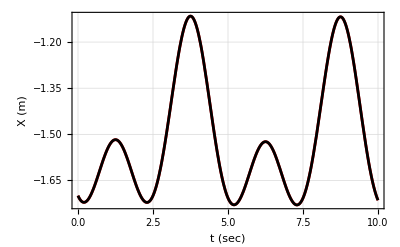

```mathematica
Plot[{Subscript[x, d][t],x[t]/.solPathDyn},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","X (m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

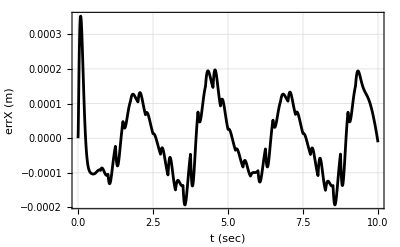

```mathematica
Plot[(Subscript[x, d][t]-x[t])/.solPathDyn,{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","errX (m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

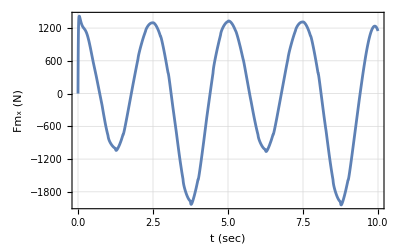

```mathematica
Plot[Subscript[Fm, x][t]/.solPathDyn,{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Fm_x (N)"},PlotRange->All]
```

#### y and motor force plots

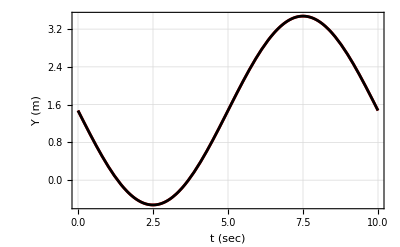

```mathematica
Plot[{Subscript[y, d][t],y[t]/.solPathDyn},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Y (m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

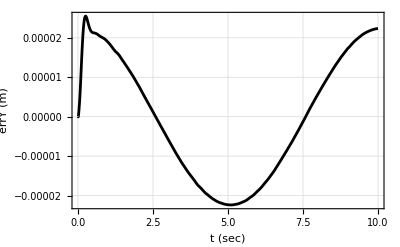

```mathematica
Plot[(Subscript[y, d][t]-y[t])/.solPathDyn,{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","errY (m)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

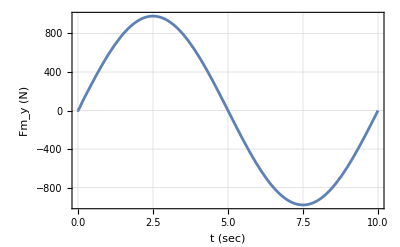

```mathematica
Plot[Subscript[Fm, y][t]/.solPathDyn,{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Fm_y (N)"},PlotRange->All]
```

#### q_5 and motor torque plots

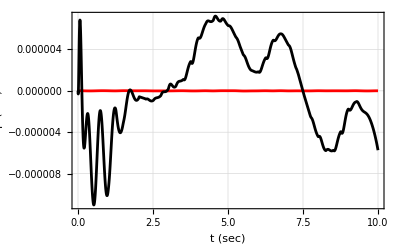

```mathematica
Plot[{Subscript[q, d5][t],Subscript[q, 5][t]/.solPathDyn},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_5 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

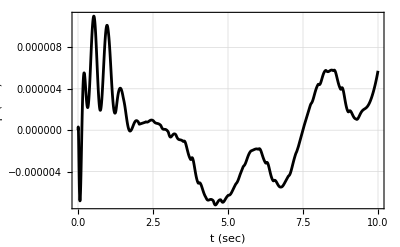

```mathematica
Plot[(Subscript[q, d5][t]-Subscript[q, 5][t])/.solPathDyn,{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","errq_5 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

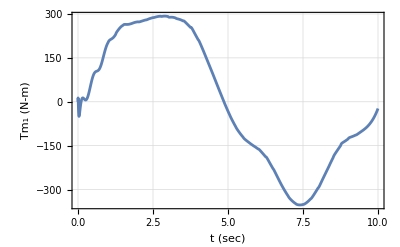

```mathematica
Plot[Subscript[Tm, 1][t]/.solPathDyn,{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_1 (N-m)"},PlotRange->All]
```

#### q_6 and motor torque plots

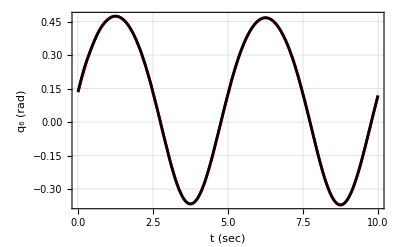

```mathematica
Plot[{Subscript[q, d6][t],Subscript[q, 6][t]/.solPathDyn},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_6 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

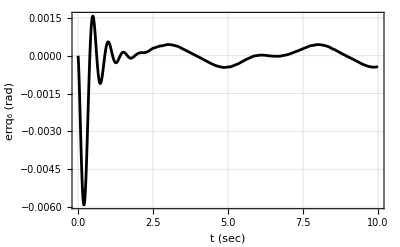

```mathematica
Plot[(Subscript[q, d6][t]-Subscript[q, 6][t])/.solPathDyn,{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","errq_6 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

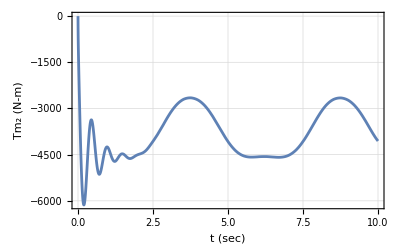

```mathematica
Plot[Subscript[Tm, 2][t]/.solPathDyn,{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_2 (N-m)"},PlotRange->All]
```

#### q_7 and motor torque plots

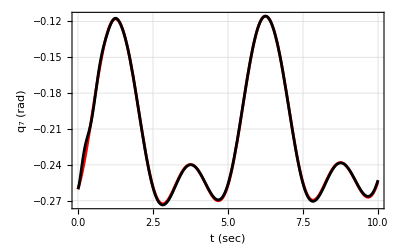

```mathematica
Plot[{Subscript[q, d7][t],Subscript[q, 7][t]/.solPathDyn},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_7 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

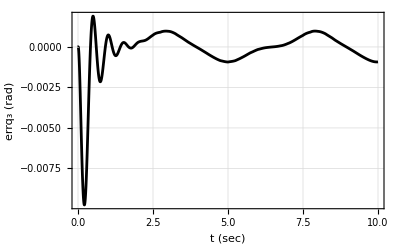

```mathematica
Plot[(Subscript[q, d7][t]-Subscript[q, 7][t])/.solPathDyn,{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","errq_3 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

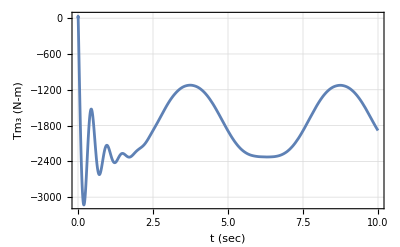

```mathematica
Plot[Subscript[Tm, 3][t]/.solPathDyn,{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_3 (N-m)"},PlotRange->All]
```

#### q_8 and motor torque plots

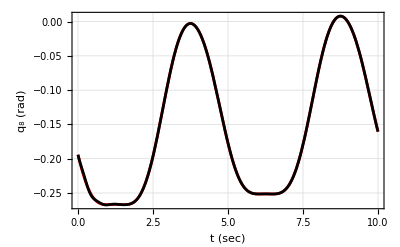

```mathematica
Plot[{Subscript[q, d8][t],Subscript[q, 8][t]/.solPathDyn},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_8 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

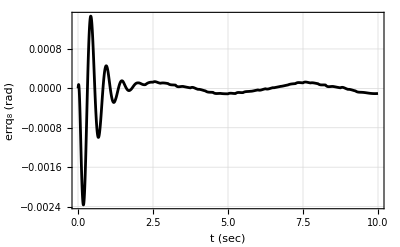

```mathematica
Plot[(Subscript[q, d8][t]-Subscript[q, 8][t])/.solPathDyn,{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","errq_8 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

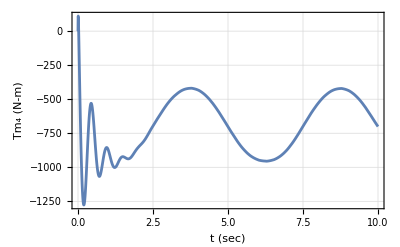

```mathematica
Plot[Subscript[Tm, 4][t]/.solPathDyn,{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_4 (N-m)"},PlotRange->All]
```

#### q_10 and motor torque plots

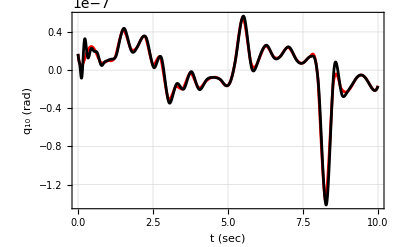

```mathematica
Plot[{Subscript[q, d10][t],Subscript[q, 10][t]/.solPathDyn},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_10 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

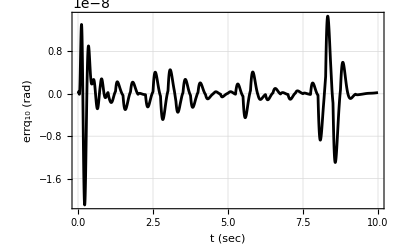

```mathematica
Plot[(Subscript[q, d10][t]-Subscript[q, 10][t])/.solPathDyn,{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","errq_10 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

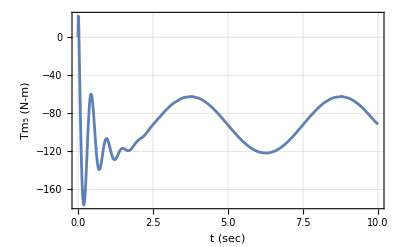

```mathematica
Plot[Subscript[Tm, 5][t]/.solPathDyn,{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_5 (N-m)"},PlotRange->All]
```

#### q_10 and motor torque plots

```mathematica
Plot[{Subscript[q, d10][t],Subscript[q, 10][t]/.solPathDyn},{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","q_10 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

-Graphics-

```mathematica
Plot[(Subscript[q, d10][t]-Subscript[q, 10][t])/.solPathDyn,{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","errq_10 (rad)"},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,0]}, PlotRange->All]
```

-Graphics-

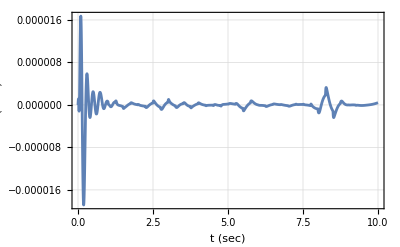

```mathematica
Plot[Subscript[Tm, 6][t]/.solPathDyn,{t,Subscript[t, 0],Subscript[t, f]}, Frame->True,GridLines->Automatic,FrameLabel->{"t (sec)","Tm_6 (N-m)"},PlotRange->All]
```

#### Animation of the path planned motion

```mathematica
x[t_]=x[t]/.solPathDyn;
y[t_]=y[t]/.solPathDyn;
Subscript[q, 5][t_]=Subscript[q, 5][t]/.solPathDyn;
Subscript[q, 6][t_]=Subscript[q, 6][t]/.solPathDyn;
Subscript[q, 7][t_]=Subscript[q, 7][t]/.solPathDyn;
Subscript[q, 8][t_]=Subscript[q, 8][t]/.solPathDyn;
Subscript[q, 9][t_]=Subscript[q, 9][t]/.solPathDyn;
Subscript[q, 10][t_]=Subscript[q, 10][t]/.solPathDyn;
```

Create composite graphic out of parts that have been rotated and translated

```mathematica
pathPlot=ParametricPlot3D[{Subscript[X, p][t],Subscript[Y, p][t],Subscript[Z, p][t]},{t,0,Subscript[T, man]},ViewPoint->{1,-1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-scale,scale},{-scale,scale},{0,scale}},AspectRatio->1,AxesLabel->{"X","Y","Z"}]
```

-Graphics3D-

```mathematica
robotGraphicPathDynAnim={

(*Path point*)
Point[{Subscript[X, p][t],Subscript[Y, p][t],Subscript[Z, p][t]}],

(*Base graphic*)
Translate[GeometricTransformation[baseGraphic,Transpose[rotA]],{xAo,yAo,zAo}],
(*Wheel graphic*)
Translate[GeometricTransformation[wheelGraphic1,Transpose[rotA]],{xBo,yBo,zBo}],
Translate[GeometricTransformation[wheelGraphic2,Transpose[rotA]],{xCo,yCo,zCo}],
Translate[GeometricTransformation[wheelGraphic3,Transpose[rotA]],{xDo,yDo,zDo}],
Translate[GeometricTransformation[wheelGraphic4,Transpose[rotA]],{xEo,yEo,zEo}],
(*rotor*)
Translate[GeometricTransformation[rotatorGraphic,Transpose[rotF]],{xFo,yFo,zFo}],

(*joint 1*)
Translate[GeometricTransformation[jointGraphic1,Transpose[rotG]],{xGo,yGo,zGo}],

(*Arm1 graphic*)
Translate[GeometricTransformation[arm1baseGraphic,Transpose[rotH]],{xHo,yHo,zHo}],

(*Arm2 graphic*)
Translate[GeometricTransformation[arm2baseGraphic,Transpose[rotL]],{xLo,yLo,zLo}],

(*Arm3 graphic*)
Translate[GeometricTransformation[arm3baseGraphic,Transpose[rotS]],{xSo,ySo,zSo}],

(*Wrist1 graphic*)
Translate[GeometricTransformation[wristGraphic1,Transpose[rotM]],{xMo,yMo,zMo}],

(*Wrist2 graphic*)
Translate[GeometricTransformation[wristGraphic2,Transpose[rotP]],{xPo,yPo,zPo}]
};
```

```mathematica
robotGraphicPathDynAnimT[t_]=robotGraphicPathDynAnim;
```

Loop over time

```mathematica
Animate[Show[pathPlot,Graphics3D[robotGraphicPathDynAnimT[t],ViewPoint->{1,1,1},ViewVertical->{0,0,1},ViewCenter->{1/2,1/2,1/2},Boxed->True,Axes->True,PlotRange->{{-scale,scale},{-scale,scale},{-scale,scale}},AspectRatio->1,AxesLabel->{"X","Y","Z"}]],{t,0,Subscript[T, man],delT},AnimationRunning->False]
```